## dt = 0

#### 4+4

```mathematica
entropy=Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy005.dat"]];
```

```mathematica
Dimensions[entropy]
```

{4020}

```mathematica
entropyn=Table[Drop[Drop[entropy,-4020+200n],20(n-1)],{n,1,21}];
```

```mathematica
Dimensions[entropyn]
```

{21}

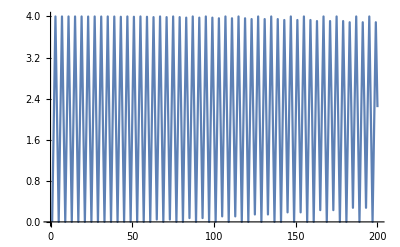

```mathematica
ListLinePlot[entropyn[[1]]]
```

```mathematica
entropynn = Table[Drop[entropyn[[i]],-11],{i,1,201}];
```

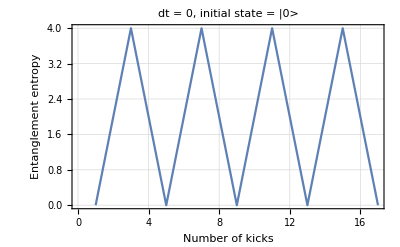

```mathematica
ListLinePlot[Drop[entropyn[[1]],-3],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"dt = 0, initial state = |0>"]
```

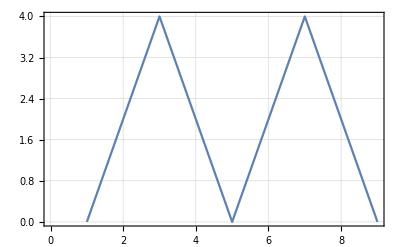
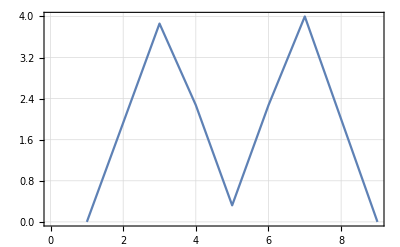
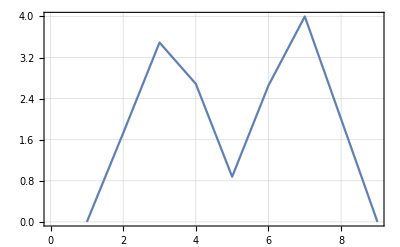
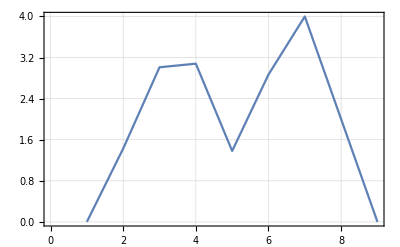
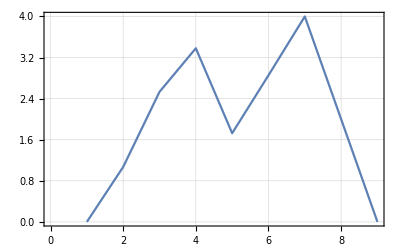
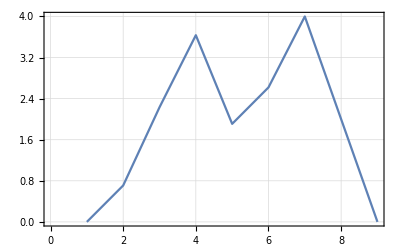
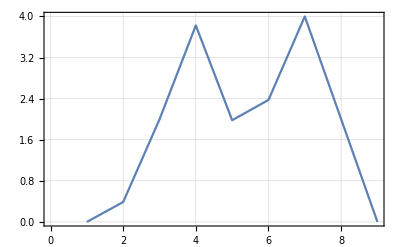
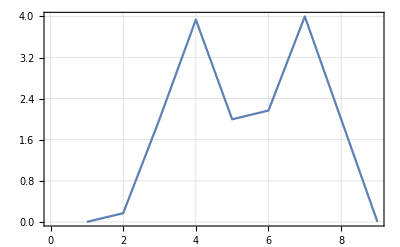
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[entropynn[[i]],PlotTheme->"Detailed"],{i,1,201,10}]
```

```mathematica
Manipulate[ListLinePlot[entropynn[[i]]],{i,1,201,1}]
```

Part::partd: Part specification entropynn⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: entropynn⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification entropynn⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: entropynn⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification entropynn⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: entropynn⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification entropynn⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: entropynn⟦1⟧ is not a list of numbers or pairs of numbers.

```mathematica
32*0.005
```

0.16

```mathematica
Max[Table[Mean[entropynn[[i]]],{i,1,201}]]
```

1.97636

```mathematica
Mean[entropynn[[32]]]
```

1.97636

```mathematica
Mean[entropynn[[10]]]
```

1.84136101291736941

```mathematica
entropymax=Table[{0.005*(n-1)*Pi,Max[entropyn[[n]]]},{n,1,201}];
```

```mathematica
entropymean=Table[{0.005 (n-1) Pi,Mean[entropyn[[n]]]},{n,1,201}];
```

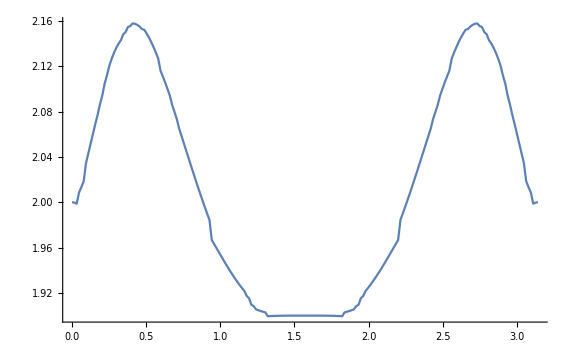

```mathematica
ListLinePlot[entropymean]
```

### (H0+longitudinal field)/2 + transverse kicks

```mathematica
entropylong2=Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy_longiby2.dat"]];
```

```mathematica
Dimensions[entropylong2]
```

{2100}

```mathematica
entropylongn2=Table[Drop[Drop[entropylong2,-2100+100n],100(n-1)],{n,1,21}];
```

```mathematica
Dimensions[entropylongn2]
```

{21,100}

```mathematica
(*Manipulate[ListLinePlot[entropylongn2[[i]]],{i,1,21}]*)
```

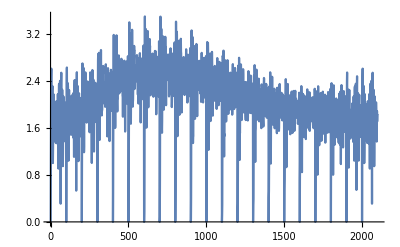

```mathematica
ListLinePlot[entropylong2]
```

### longitudinal field + transverse kicks

```mathematica
entropylong=Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy_longi.dat"]];
```

```mathematica
Dimensions[entropylong]
```

{2100}

```mathematica
entropylongn=Table[Drop[Drop[entropylong,-2100+100n],100(n-1)],{n,1,21}];
```

```mathematica
Dimensions[entropylongn]
```

{21,100}

```mathematica
(*Manipulate[ListLinePlot[entropylongn[[i]]],{i,1,21}]*)
```

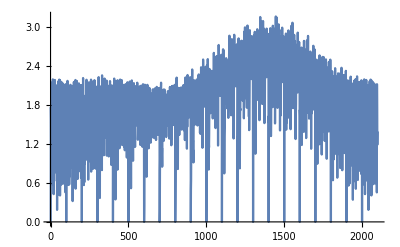

```mathematica
ListLinePlot[entropylong]
```

### (longitudinal + transverse ) kicks

```mathematica
entropylongk=Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy_longi_kick.dat"]];
```

```mathematica
Dimensions[entropylongk]
```

{21000}

```mathematica
kentropylongn=Table[Drop[Drop[entropylongk,-21000+1000n],1000(n-1)],{n,1,21}];
```

```mathematica
Dimensions[kentropylongn]
```

{21,1000}

```mathematica
(*Manipulate[ListLinePlot[Drop[kentropylongn[[i]],-950]],{i,1,21}]*)
```

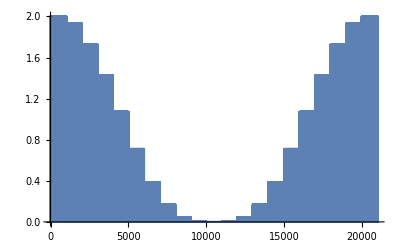

```mathematica
ListLinePlot[entropylongk]
```

```mathematica
Det[PauliMatrix[1]+PauliMatrix[2]]
```

-2

### (longitudinal + transverse ) kicks/2

```mathematica
entropylongk2=Drop[Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy_longi_kickby2.dat"]],2100];
```

```mathematica
Dimensions[entropylongk2]
```

{2100}

```mathematica
kentropylongn2=Table[Drop[Drop[entropylongk2,-2100+100n],100(n-1)],{n,1,21}];
```

```mathematica
Dimensions[kentropylongn2]
```

{21,100}

```mathematica
(*Manipulate[ListLinePlot[kentropylongn2[[i]]],{i,1,21}]*)
```

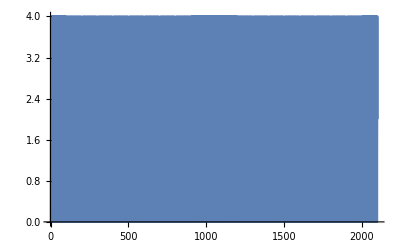

```mathematica
ListLinePlot[entropylongk2]
```

```mathematica
Det[PauliMatrix[1]+PauliMatrix[2]]
```

-2

### (longitudinal + transverse ) kicks*3/2

```mathematica
entropylongk3by2=Flatten[Import["/home/yajur/Dropbox/miniproj/nonoisy_longi_kick3by2.dat"]];
```

```mathematica
Dimensions[entropylongk3by2]
```

{2100}

```mathematica
kentropylongn3by2=Table[Drop[Drop[entropylongk3by2,-2100+100n],100(n-1)],{n,1,21}];
```

```mathematica
Dimensions[kentropylongn3by2]
```

{21,100}

```mathematica
(*Manipulate[ListLinePlot[kentropylongn3by2[[i]]],{i,1,21}]*)
```

```mathematica
ListLinePlot[entropylongk3by2]
```

-Graphics-

```mathematica
Det[PauliMatrix[1]+PauliMatrix[2]]
```

-2

## Jordan wigner - pi/4 noise - AD protocol

#### 100 = 5+95 -- initial state == BCS GS

```mathematica
jwnoise = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_100_5.dat"]];
```

```mathematica
jwnoise = Flatten@ToExpression@StringSplit[jwnoise,","];
```

```mathematica
Dimensions[jwnoise]
```

{500}

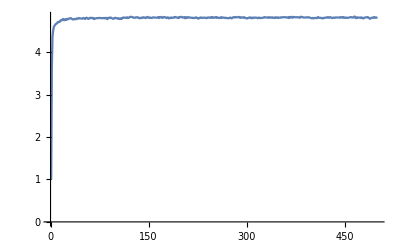

```mathematica
ListLinePlot[jwnoise,PlotRange->All]
```

#### initial state = maximallly entangled state obtained after 2 kicks, jwnoiseme_n --> n== number of kicks after which the initial state is considered

```mathematica
jwnoiseme = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_ME_100_5.dat"]];
```

```mathematica
jwnoiseme25 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_25ME_100_5.dat"]];
```

```mathematica
jwnoiseme25 = Flatten@ToExpression@StringSplit[jwnoiseme25,","];
```

```mathematica
jwnoiseme = Flatten@ToExpression@StringSplit[jwnoiseme,","];
```

```mathematica
jwnoiseme5 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_5ME_100_5.dat"]];
jwnoiseme5 = Flatten@ToExpression@StringSplit[jwnoiseme5,","];
jwnoiseme10 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_10ME_100_5.dat"]];
jwnoiseme10 = Flatten@ToExpression@StringSplit[jwnoiseme10,","];
jwnoiseme20 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_20ME_100_5.dat"]];
jwnoiseme20 = Flatten@ToExpression@StringSplit[jwnoiseme20,","];
jwnoiseme80 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_80ME_100_5.dat"]];
jwnoiseme80 = Flatten@ToExpression@StringSplit[jwnoiseme80,","];
```

```mathematica
jwnoiseme1 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_1ME_100_5.dat"]];
jwnoiseme1 = Flatten@ToExpression@StringSplit[jwnoiseme1,","];
jwnoiseme2 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_2ME_100_5.dat"]];
jwnoiseme2 = Flatten@ToExpression@StringSplit[jwnoiseme2,","];
jwnoiseme3 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_3ME_100_5.dat"]];
jwnoiseme3 = Flatten@ToExpression@StringSplit[jwnoiseme3,","];
jwnoiseme4 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_4ME_100_5.dat"]];
jwnoiseme4 = Flatten@ToExpression@StringSplit[jwnoiseme4,","];
jwnoiseme6 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_6ME_100_5.dat"]];
jwnoiseme6 = Flatten@ToExpression@StringSplit[jwnoiseme6,","];
```

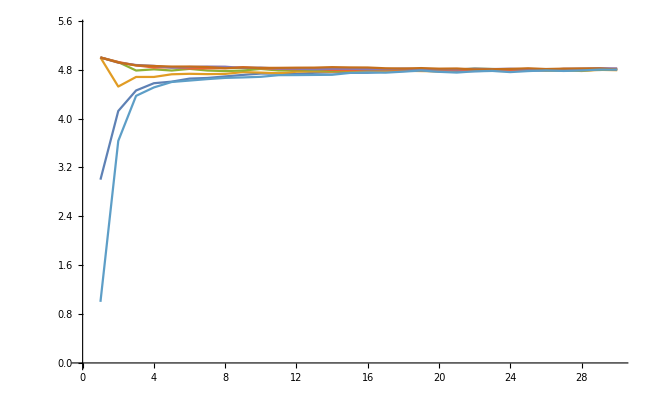

```mathematica
ListLinePlot[Drop[{jwnoiseme1,jwnoiseme2,jwnoiseme3,jwnoiseme4,jwnoiseme5,jwnoiseme6,jwnoise},0,-470],PlotRange->{0,5.5}]
```

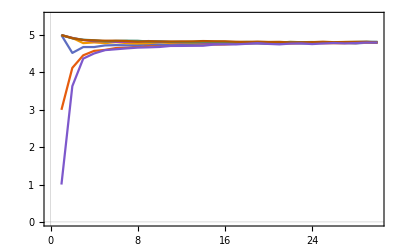

```mathematica
ListLinePlot[Drop[{jwnoiseme1,jwnoiseme2,jwnoiseme3,jwnoiseme4,jwnoiseme5,jwnoiseme6,jwnoise},0,-470],PlotTheme->"Scientific",PlotRange->{0,5.5}]
```

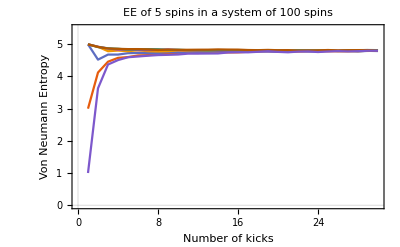

```mathematica
Show[%35,FrameLabel->{{HoldForm[Von Neumann Entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm[EE of 5 spins in a system of 100 spins],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Dimensions[jwnoiseme]
```

{500}

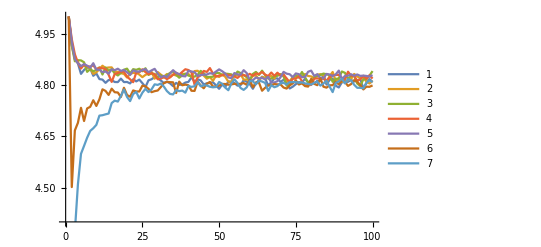

```mathematica
ListLinePlot[Drop[{jwnoiseme5,jwnoiseme10,jwnoiseme20,jwnoiseme25,jwnoiseme80,jwnoiseme,jwnoise},0,-400],PlotRange->{4.4,5}, PlotLegends -> Automatic]
```

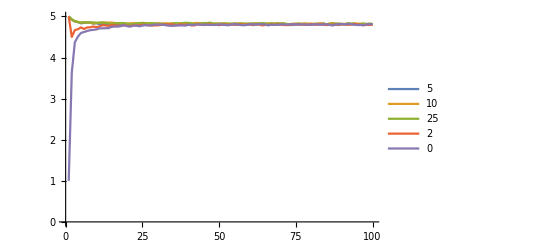

-Graphics-

#### 100 = 10 + 90

```mathematica
jwnoise10m0 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_0ME_100_10.dat"]];
jwnoise10m0 = Flatten@ToExpression@StringSplit[jwnoise10m0,","];
jwnoise10m5 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_5ME_100_10.dat"]];
jwnoise10m5 = Flatten@ToExpression@StringSplit[jwnoise10m5,","];
jwnoise10m6 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_6ME_100_10.dat"]];
jwnoise10m6 = Flatten@ToExpression@StringSplit[jwnoise10m6,","];
jwnoise10m7 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_7ME_100_10.dat"]];
jwnoise10m7 = Flatten@ToExpression@StringSplit[jwnoise10m7,","];
jwnoise10m8 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_8ME_100_10.dat"]];
jwnoise10m8 = Flatten@ToExpression@StringSplit[jwnoise10m8,","];
jwnoise10m9 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_9ME_100_10.dat"]];
jwnoise10m9 = Flatten@ToExpression@StringSplit[jwnoise10m9,","];
jwnoise10m10 = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_10ME_100_10.dat"]];
jwnoise10m10 = Flatten@ToExpression@StringSplit[jwnoise10m10,","];
```

```mathematica
Drop[jwnoise10m0,-100]
```

{1.00000000000000333,6.05231782032709376,7.83686247187841811,8.25428571703121783,8.44363352428584157,8.5926632940582266,8.64134021230799831,8.74132739219839294,8.76383247940900922,8.78207288063585345,8.77686880325735785,8.8195155472231761,8.87527532214402726,8.87126645101277944,8.92456421936169875,8.9723391300584403,8.98363107851985276,8.97453001201676059,9.01757895844739643,9.02928558513058555,9.0429000527286334,9.06590321785090048,9.07875430042053111,9.07956451478621851,9.1045324492888966,9.11991041944321879,9.11409169120103968,9.08759353073896392,9.10766094432797679,9.12117819971911814,9.10980483340599712,9.10359196124258752,9.11960321884848923,9.12653057673301227,9.10982946958969109,9.12708202539375435,9.13032306341792399,9.14653771198544696,9.19722959365276616,9.1728318205179864,9.14435728632264322,9.11271236216607683,9.16435491757616916,9.19397879600241552,9.1471530326930921,9.17218273640998127,9.18379196092638672,9.14047243160966083,9.20864461124782707,9.2153799943212622,9.2029769151919556,9.16671605623156616,9.15814205557062877,9.11907941665950972,9.13667252167516253,9.13477562422331602,9.19226973033215877,9.18861797386170132,9.21803487454059933,9.19468761582319161,9.14120871619768494,9.17172804264409791,9.19616885542180818,9.22782079483995332,9.21411491442033359,9.18877265568880652,9.22009104899993837,9.19773151325444971,9.2330565842554666,9.19989245273642098,9.22444151261712797,9.22289629464296645,9.23144032803172898,9.22048901088599493,9.22458234505600139,9.2036871139648504,9.15240388710486563,9.21297827622090537,9.19110675687978507,9.19129111397934828,9.20666052748471842,9.23492657327062538,9.22165460728613162,9.23537239763536633,9.21688419044898488,9.19337205547939718,9.21825899395814297,9.21331224715488162,9.19964301347292945,9.20494556305988176,9.23499919581648854,9.19757739487825177,9.24156166602681495,9.20385177960870848,9.21864991135894663,9.26073076607316637,9.20622728910798571,9.18429317741287932,9.14921072994058271,9.17761165331964257}

```mathematica
Dimensions[jwnoise10m5]
```

{500}

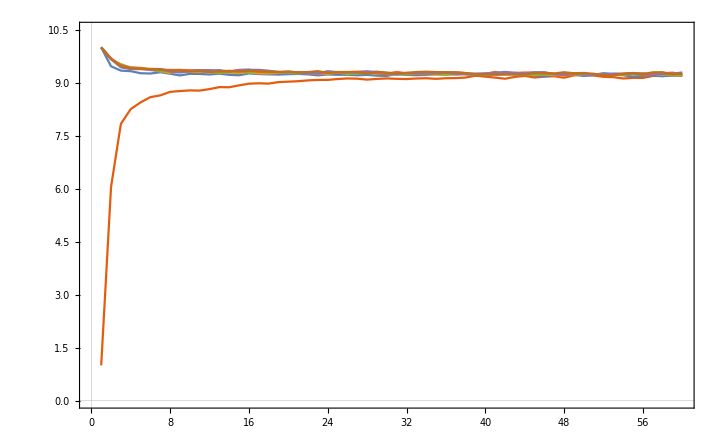

```mathematica
Show[ListLinePlot[Drop[jwnoise10m0,-140],PlotRange->{0,10.5},PlotTheme->"Scientific"],ListLinePlot[Drop[{jwnoise10m5,jwnoise10m6,jwnoise10m7,jwnoise10m8,jwnoise10m9,jwnoise10m10},0,-440],PlotRange->All]]
```

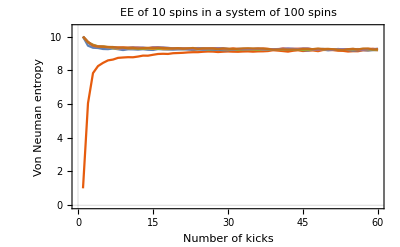

```mathematica
Show[%83,FrameLabel->{{HoldForm[Von Neuman entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm[EE of 10 spins in a system of 100 spins],LabelStyle->{GrayLevel[0]}]
```

```mathematica
jwnoise10m0k = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_0ME_100_10_initialstateisall0k.dat"]];
jwnoise10m0k = Flatten@ToExpression@StringSplit[jwnoise10m0k,","];
jwnoise10m1k = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4_0ME_100_10_initialstateisall1k.dat"]];
jwnoise10m1k = Flatten@ToExpression@StringSplit[jwnoise10m1k,","];
```

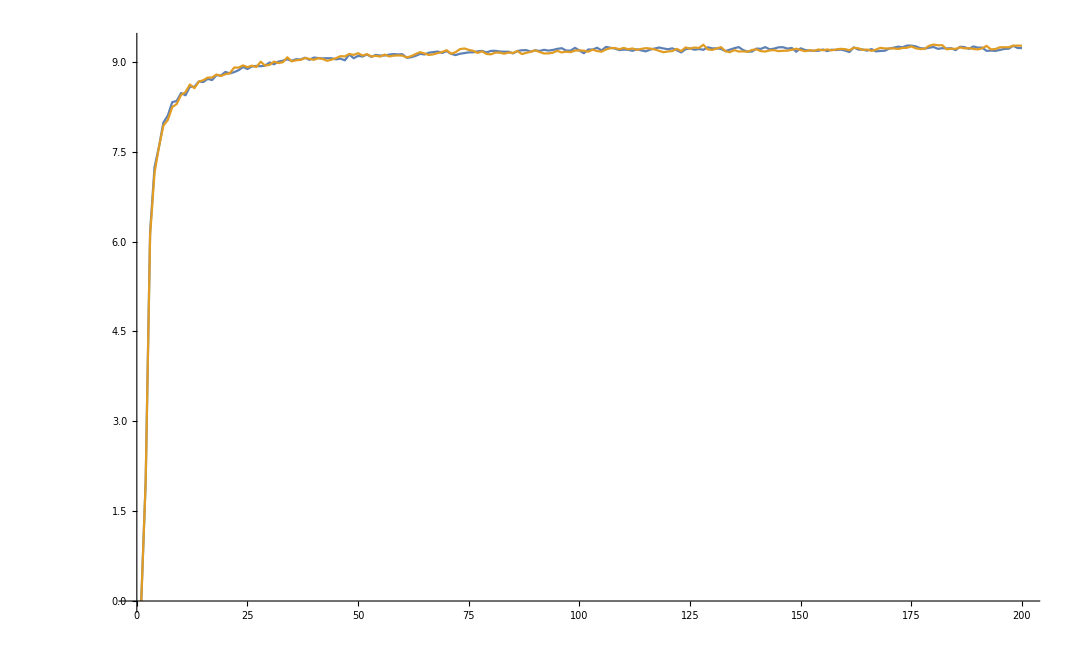

```mathematica
ListLinePlot[{jwnoise10m1k,jwnoise10m0k},PlotRange->Full]
```

## AD protocol pi/4

```mathematica
ADnoise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/final_answer.dat"]];
```

```mathematica
ADnoise = Flatten@ToExpression@StringSplit[ADnoise,","];
```

```mathematica
Dimensions[ADnoise]
```

{4200}

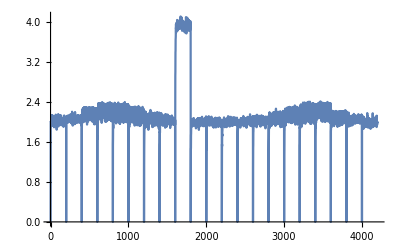

```mathematica
ListLinePlot[ADnoise,PlotRange->All]
```

```mathematica
ADnoise8n=Table[Drop[Drop[ADnoise,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[ADnoise8n]
```

{21,200}

```mathematica
N[Pi/2]
```

1.5708

```mathematica
ADnoise8max=Table[{0.05*(n-1)*Pi,Max[ADnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ADnoise8mean=Table[{0.05 (n-1) Pi,Mean[ADnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ADfitvals8 = Table[FindFit[Drop[ADnoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
ADfitvals8n = Table[{0.05( n-1) Pi,Flatten[ADfitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

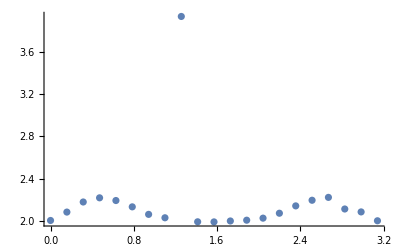

```mathematica
ListPlot[{ADfitvals8n,Efitvals8n,entropymean,fitvals},PlotRange->All]
```

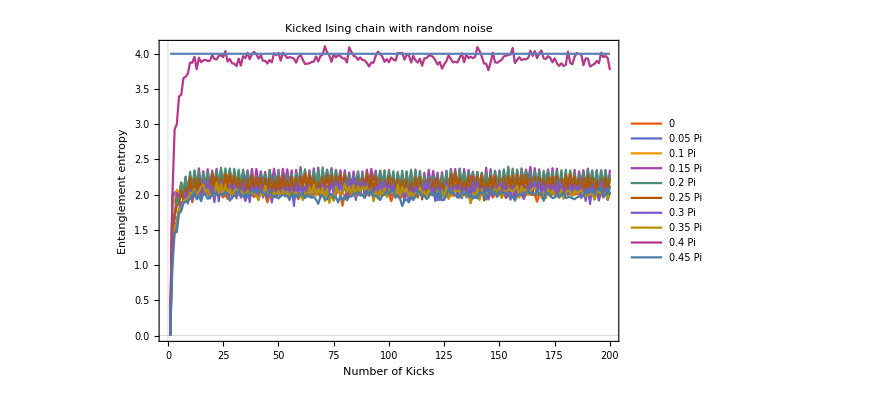

```mathematica
Show[ListLinePlot[Table[ADnoise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]],Plot[4,{x,1,200}]]
```

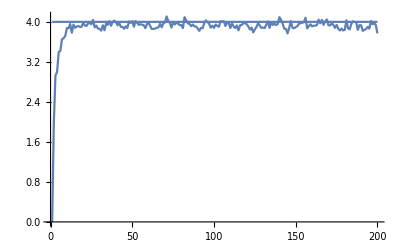

```mathematica
Show[ListLinePlot[ADnoise8n[[9]],PlotRange->All],Plot[4,{x,1,200}]]
```

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

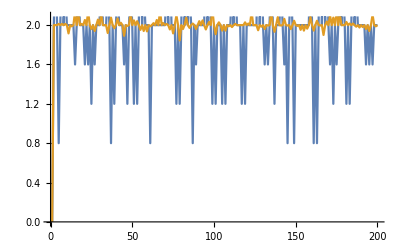

```mathematica
ListLinePlot[{AD1case0,ADnoise8n[[1]]}]
```

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

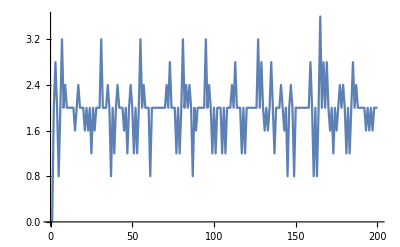

```mathematica
ListLinePlot[AD1case0,PlotRange->All]
```

## AD protocol pi/3

```mathematica
ADpiby3noise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/final_answerpiby3.dat"]];
```

```mathematica
ADpiby3noise = Flatten@ToExpression@StringSplit[ADpiby3noise,","];
```

```mathematica
Dimensions[ADpiby3noise]
```

{4200}

```mathematica
ADnoise
```

Flatten[$Failed]

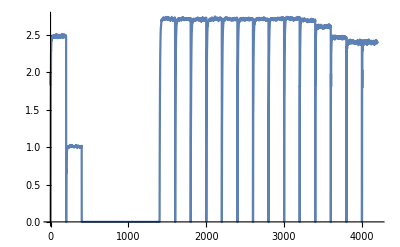

```mathematica
ListLinePlot[ADpiby3noise,PlotRange->All]
```

```mathematica
ADpiby3noise8n=Table[Drop[Drop[ADpiby3noise,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[ADpiby3noise8n]
```

{21,200}

```mathematica
N[Pi/2]
```

1.5708

```mathematica
ADpiby3noise8max=Table[{0.05*(n-1)*Pi,Max[ADpiby3noise8n[[n]]]},{n,1,21}];
```

```mathematica
ADnoise8mean=Table[{0.05 (n-1) Pi,Mean[ADnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ADpiby3fitvals8 = Table[FindFit[Drop[ADpiby3noise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
ADpiby3fitvals8n = Table[{0.05( n-1) Pi,Flatten[ADpiby3fitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

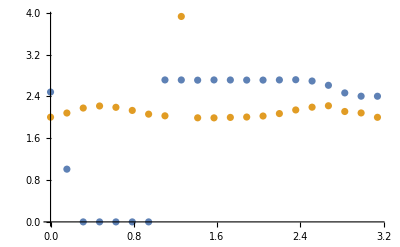

```mathematica
ListPlot[{ADpiby3fitvals8n,ADfitvals8n,Efitvals8n,entropymean,fitvals},PlotRange->All]
```

```mathematica
Show[ListLinePlot[Table[ADnoise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]],Plot[4,{x,1,200}]]
```

-Graphics-

```mathematica
Show[ListLinePlot[ADnoise8n[[9]],PlotRange->All],Plot[4,{x,1,200}]]
```

-Graphics-

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

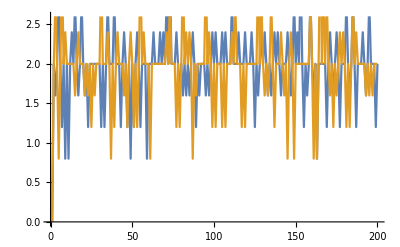

```mathematica
ListLinePlot[{AD1case0,ADnoise8n[[1]]}]
```

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

```mathematica
ListLinePlot[AD1case0,PlotRange->All]
```

-Graphics-

## AD protocol pi/64

```mathematica
ADpiby64noise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/final_answerpiby64.dat"]];
```

```mathematica
ADpiby64noise = Flatten@ToExpression@StringSplit[ADpiby64noise,","];
```

```mathematica
Dimensions[ADpiby64noise]
```

{1100}

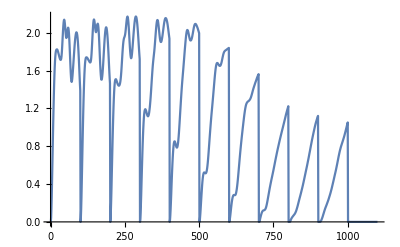

```mathematica
ListLinePlot[ADpiby64noise,PlotRange->All]
```

```mathematica
ADpiby64noise8n=Table[Drop[Drop[ADpiby64noise,-1100+100n],100(n-1)],{n,1,11}];
```

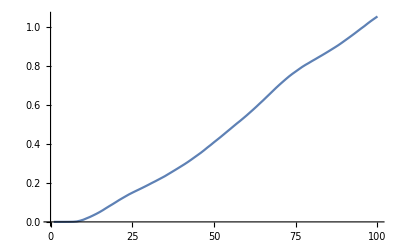

```mathematica
ListLinePlot[ADpiby64noise8n[[10]]]
```

```mathematica
Dimensions[ADpiby64noise8n]
```

{11,100}

```mathematica
N[Pi/2]
```

1.5708

```mathematica
ADnoise8max=Table[{0.05*(n-1)*Pi,Max[ADnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ADnoise8mean=Table[{0.05 (n-1) Pi,Mean[ADnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ADpiby64fitvals8 = Table[FindFit[Drop[ADpiby64noise8n[[n]],{1,30}],0*x+c,c,x],{n,1,11}];
```

```mathematica
ADpiby64fitvals8n = Table[{0.05( n-1) Pi,Flatten[ADpiby64fitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,11}];
```

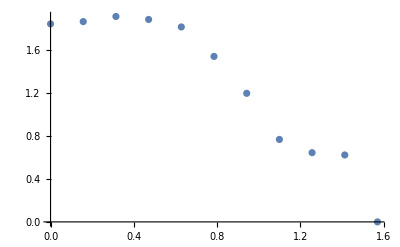

```mathematica
ListPlot[{ADpiby64fitvals8n,Efitvals8n,entropymean,fitvals},PlotRange->All]
```

```mathematica
Show[ListLinePlot[Table[ADnoise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]],Plot[4,{x,1,200}]]
```

-Graphics-

```mathematica
Show[ListLinePlot[ADnoise8n[[9]],PlotRange->All],Plot[4,{x,1,200}]]
```

-Graphics-

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

```mathematica
ListLinePlot[{AD1case0,ADnoise8n[[1]]}]
```

-Graphics-

```mathematica
AD1case0=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/AD_protocol_piby4.dat"]];
```

```mathematica
AD1case0 = Flatten@ToExpression@StringSplit[AD1case0,","];
```

```mathematica
ListLinePlot[AD1case0,PlotRange->All]
```

-Graphics-

## correct dt = pi/8-- 4+4 -- interaction unitary = exp(int*(tau[i+1]-tau[i])*dt)

```mathematica
Enoise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/Eanswers.dat"]];
```

```mathematica
Enoise = Flatten@ToExpression@StringSplit[Enoise,","];
```

```mathematica
Dimensions[Enoise]
```

{4200}

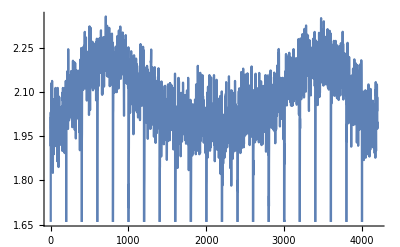

```mathematica
ListLinePlot[Enoise]
```

```mathematica
Enoise8n=Table[Drop[Drop[Enoise,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[kanoise8n]
```

{}

```mathematica
Enoise8max=Table[{0.05*(n-1)*Pi,Max[Enoise8n[[n]]]},{n,1,21}];
```

```mathematica
Enoise8mean=Table[{0.05 (n-1) Pi,Mean[Enoise8n[[n]]]},{n,1,21}];
```

```mathematica
Efitvals8 = Table[FindFit[Drop[Enoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
Efitvals8n = Table[{0.05( n-1) Pi,Flatten[Efitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

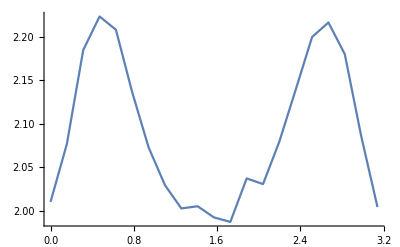

```mathematica
ListLinePlot[{Efitvals8n,entropymean,fitvals},PlotRange->All]
```

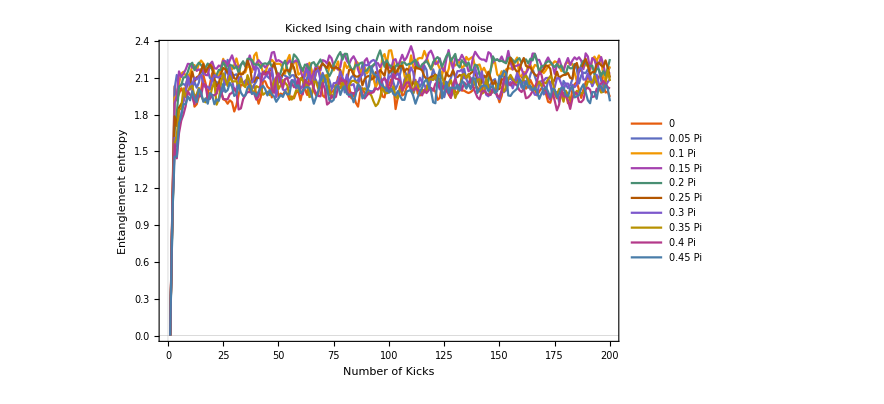

```mathematica
ListLinePlot[Table[Enoise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

## correct dt = pi/8 --3 +5

```mathematica
C3noise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/C_3_answers8.dat"]];
```

```mathematica
C3noise = Flatten@ToExpression@StringSplit[C3noise,","];
```

```mathematica
Dimensions[C3noise]
```

{4200}

```mathematica
C3noise;
```

```mathematica
C3noise8n=Table[Drop[Drop[C3noise,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
C3noise8max=Table[{0.05*(n-1)*Pi,Max[C3noise8n[[n]]]},{n,1,21}];
```

```mathematica
C3noise8mean=Table[{0.05 (n-1) Pi,Mean[C3noise8n[[n]]]},{n,1,21}];
```

```mathematica
C3fitvals8 = Table[FindFit[Drop[C3noise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
C3fitvals8n = Table[{0.05( n-1) Pi,Flatten[C3fitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

```mathematica
C3noise8max
```

{{0.,1.84653465346533618},{0.15708,1.92558872344017096},{0.314159,2.0254797283365944},{0.471239,2.06490516652382627},{0.628319,2.04898132964449831},{0.785398,1.98569262888496367},{0.942478,1.94167986038069573},{1.09956,1.86785672581779028},{1.25664,1.8361040814807672},{1.41372,1.82180692969375668},{1.5708,1.84257425742573244},{1.72788,1.86536843258622276},{1.88496,1.85931831648774937},{2.04204,1.86384889723339531},{2.19911,1.91332271452092906},{2.35619,1.97172982034966315},{2.51327,2.04701443974440522},{2.67035,2.08238674552413139},{2.82743,2.01595977243329205},{2.98451,1.93997625726481893},{3.14159,1.8603960396039545}}

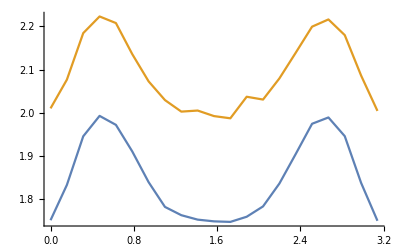

```mathematica
ListLinePlot[{C3fitvals8n,Efitvals8n,entropymean,fitvals},PlotRange->All]
```

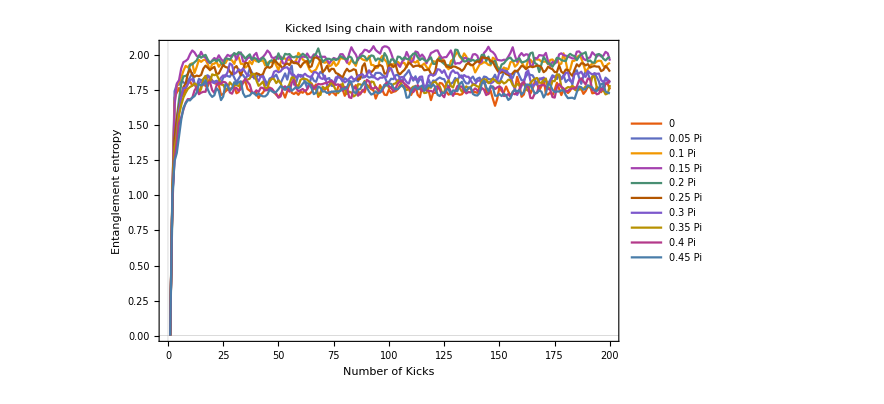

```mathematica
ListLinePlot[Table[C3noise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

## correct dt = pi/8 --2 +6

```mathematica
C2noise=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/C_2_noise/C_2_answers/C_2_answers8.dat"]];
```

```mathematica
C2noise = Flatten@ToExpression@StringSplit[C2noise,","];
```

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{0.,1.02970297029702995,1.48910891089108821,1.46138613861386157,1.45742574257425761,1.50099009900990099,1.45346534653465365,1.43564356435643625,«36»,1.51881188118811839,1.47920792079207919,1.49702970297029703,1.47524752475247589,1.4594059405940587,1.48712871287128645,«3750»},,].

ToExpression::notstrbox: StringSplit[{0.,1.02970297029702995,1.48910891089108821,1.46138613861386157,1.45742574257425761,1.50099009900990099,1.45346534653465365,1.43564356435643625,«36»,1.51881188118811839,1.47920792079207919,1.49702970297029703,1.47524752475247589,1.4594059405940587,1.48712871287128645,«3750»},,] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
Dimensions[C2noise]
```

{3800}

```mathematica
C2noise;
```

{0.000000000000000000*10^+00,9.702970297029700486*10^-01,1.698019801980197530*10^+00,1.734653465346534196*10^+00,1.766336633663366573*10^+00,1.703960396039603697*10^+00,1.726732673267326490*10^+00,1.760396039603959961*10^+00,1.797029702970297516*10^+00,1.813861386138614362*10^+00,1.784158415841583523*10^+00,1.796039603960396747*10^+00,1.759405940594058970*10^+00,1.732673267326732658*10^+00,1.776237623762376039*10^+00,1.810891089108910057*10^+00,1.780198019801979115*10^+00,1.779207920792078568*10^+00,1.843564356435642093*10^+00,1.821782178217820958*10^+00,1.801980198019801804*10^+00,1.795049504950493091*10^+00,1.790099009900989691*10^+00,1.716831683168315692*10^+00,1.723762376237622851*10^+00,1.742574257425741235*10^+00,1.755445544554454340*10^+00,1.760396039603958629*10^+00,1.767326732673265566*10^+00,1.779207920792077902*10^+00,1.728712871287128028*10^+00,1.737623762376236281*10^+00,1.793069306930691109*10^+00,1.812871287128710929*10^+00,1.814851485148513577*10^+00,1.759405940594057860*10^+00,1.747524752475246412*10^+00,1.732673267326731770*10^+00,1.728712871287126918*10^+00,1.732673267326730437*10^+00,1.695049504950493224*10^+00,1.719801980198017333*10^+00,1.733663366336631872*10^+00,1.760396039603958851*10^+00,1.761386138613860064*10^+00,1.770297029702968761*10^+00,1.757425742574255656*10^+00,1.735643564356433410*10^+00,1.717821782178215573*10^+00,1.702970297029701596*10^+00,1.724752475247523176*10^+00,1.734653465346533086*10^+00,1.698019801980195531*10^+00,1.744554455445542107*10^+00,1.784158415841580858*10^+00,1.732673267326730215*10^+00,1.723762376237621075*10^+00,1.735643564356432078*10^+00,1.717821782178214685*10^+00,1.739603960396036930*10^+00,1.732673267326730437*10^+00,1.749504950495046618*10^+00,1.721782178217818648*10^+00,1.724752475247522066*10^+00,1.738613861386135717*10^+00,1.769306930693065327*10^+00,1.792079207920788120*10^+00,1.702970297029700264*10^+00,1.734653465346530643*10^+00,1.766336633663362354*10^+00,1.753465346534651470*10^+00,1.778217821782174024*10^+00,1.718811881188115454*10^+00,1.740594059405936589*10^+00,1.729702970297025688*10^+00,1.713861386138610055*10^+00,1.775247524752470385*10^+00,1.791089108910886685*10^+00,1.758415841584154427*10^+00,1.710891089108907082*10^+00,1.746534653465342757*10^+00,1.790099009900985250*10^+00,1.795049504950490427*10^+00,1.763366336633657383*10^+00,1.787128712871282943*10^+00,1.744554455445539887*10^+00,1.720792079207917880*10^+00,1.753465346534649250*10^+00,1.735643564356431190*10^+00,1.790099009900984584*10^+00,1.774257425742568728*10^+00,1.757425742574252103*10^+00,1.750495049504944722*10^+00,1.691089108910887484*10^+00,1.728712871287124697*10^+00,1.787128712871282055*10^+00,1.751485148514845713*10^+00,1.718811881188114787*10^+00,1.715841584158411148*10^+00,1.756435643564351778*10^+00,1.731683168316826782*10^+00,1.739603960396033600*10^+00,1.743564356435637785*10^+00,1.758415841584153094*10^+00,1.789108910891082704*10^+00,1.780198019801973564*10^+00,1.780198019801974452*10^+00,1.770297029702965430*10^+00,1.765346534653458699*10^+00,1.716831683168311029*10^+00,1.749504950495043287*10^+00,1.782178217821775323*10^+00,1.717821782178212464*10^+00,1.700990099009895840*10^+00,1.777227722772271257*10^+00,1.775247524752467498*10^+00,1.781188118811873888*10^+00,1.744554455445538776*10^+00,1.680198019801975251*10^+00,1.731683168316824784*10^+00,1.731683168316826116*10^+00,1.765346534653457589*10^+00,1.802970297029695246*10^+00,1.799009900990091504*10^+00,1.776237623762369156*10^+00,1.739603960396033377*10^+00,1.718811881188113233*10^+00,1.731683168316825450*10^+00,1.722772277227717641*10^+00,1.724752475247518069*10^+00,1.725742574257419282*10^+00,1.717821782178211132*10^+00,1.721782178217815096*10^+00,1.743564356435637341*10^+00,1.739603960396033377*10^+00,1.769306930693061775*10^+00,1.760396039603953744*10^+00,1.735643564356429192*10^+00,1.737623762376230285*10^+00,1.731683168316825228*10^+00,1.773267326732664406*10^+00,1.825742574257416262*10^+00,1.832673267326723865*10^+00,1.744554455445537444*10^+00,1.722772277227716087*10^+00,1.747524752475239751*10^+00,1.690099009900984051*10^+00,1.639603960396034177*10^+00,1.690099009900982940*10^+00,1.775247524752466610*10^+00,1.743564356435636453*10^+00,1.736633663366327296*10^+00,1.777227722772268592*10^+00,1.741584158415834249*10^+00,1.710891089108903085*10^+00,1.737623762376229175*10^+00,1.756435643564347560*10^+00,1.846534653465336184*10^+00,1.792079207920782125*10^+00,1.703960396039596814*10^+00,1.719801980198012004*10^+00,1.780198019801971121*10^+00,1.787128712871276948*10^+00,1.725742574257417505*10^+00,1.759405940594051421*10^+00,1.812871287128701825*10^+00,1.799999999999990274*10^+00,1.748514851485140076*10^+00,1.781188118811872556*10^+00,1.835643564356424395*10^+00,1.723762376237615745*10^+00,1.719801980198011782*10^+00,1.735643564356426527*10^+00,1.714851485148505938*10^+00,1.754455445544544689*10^+00,1.803960396039592906*10^+00,1.760396039603950857*10^+00,1.715841584158407596*10^+00,1.753465346534642810*10^+00,1.747524752475238197*10^+00,1.730693069306920462*10^+00,1.747524752475237753*10^+00,1.780198019801969123*10^+00,1.770297029702959213*10^+00,1.761386138613850960*10^+00,1.768316831683158119*10^+00,1.761386138613851626*10^+00,1.724752475247515404*10^+00,1.744554455445534780*10^+00,1.777227722772265928*10^+00,1.778217821782166919*10^+00,1.728712871287118258*10^+00,1.731683168316822119*10^+00,1.773267326732661742*10^+00,1.752475247524741153*10^+00,1.736633663366326186*10^+00,1.758415841584147765*10^+00,1.799009900990087285*10^+00,1.795049504950482433*10^+00,1.756435643564344895*10^+00,5.112668700087696817*10^-13,1.001980198019952306*10^+00,1.743492914136425043*10^+00,1.790709937041868649*10^+00,1.789987315502776566*10^+00,1.822637731680213147*10^+00,1.806879649296030621*10^+00,1.796467901024809688*10^+00,1.817359180253037998*10^+00,1.842285940690093993*10^+00,1.873591028094642619*10^+00,1.800684824192183342*10^+00,1.779687185299610119*10^+00,1.830965162255232981*10^+00,1.822415253182047667*10^+00,1.827344958824305365*10^+00,1.850983215787197711*10^+00,1.856961893085448789*10^+00,1.839418487750482445*10^+00,1.812532888702440115*10^+00,1.811764768045241780*10^+00,1.818294534594811163*10^+00,1.792504966818429413*10^+00,1.804563766830831639*10^+00,1.838901559752913251*10^+00,1.860653315655332429*10^+00,1.851664436660559909*10^+00,1.846660661799722547*10^+00,1.873985807819850580*10^+00,1.840272315956200000*10^+00,1.807689240314328316*10^+00,1.833058343245135724*10^+00,1.859066822405422093*10^+00,1.858664013776772261*10^+00,1.834295937793685827*10^+00,1.853312009977148733*10^+00,1.905449784716120698*10^+00,1.876813943738735890*10^+00,1.834162016136198670*10^+00,1.841135582152432004*10^+00,1.866668255403058918*10^+00,1.846179098200381841*10^+00,1.855039039532515366*10^+00,1.822239449848389370*10^+00,1.791287340138462136*10^+00,1.834080870934682306*10^+00,1.842368411807220108*10^+00,1.845960263564946136*10^+00,1.862118861405114512*10^+00,1.823312240196037104*10^+00,1.800819487416662090*10^+00,1.836834310460975006*10^+00,1.870573477042014598*10^+00,1.826381864877375527*10^+00,1.894005010264105504*10^+00,1.925588723440170957*10^+00,1.790811232212248250*10^+00,1.806389452552089825*10^+00,1.857412842200850012*10^+00,1.859424457673617859*10^+00,1.852137459112034090*10^+00,1.807776807270158548*10^+00,1.766669527545108975*10^+00,1.794214633254489044*10^+00,1.852894576849428709*10^+00,1.819339928099950487*10^+00,1.810271250523770581*10^+00,1.854054862039442586*10^+00,1.882185041119142532*10^+00,1.868587678558011556*10^+00,1.826686054335985299*10^+00,1.831485475360998150*10^+00,1.837565408285117829*10^+00,1.782335619568484519*10^+00,1.780561140255244812*10^+00,1.814353718257989412*10^+00,1.857963727270256937*10^+00,1.837635187124438518*10^+00,1.812799200413716560*10^+00,1.836423043134157274*10^+00,1.825523564619810024*10^+00,1.817519934245912738*10^+00,1.811614114495301742*10^+00,1.813411712871417114*10^+00,1.825543686068385574*10^+00,1.813945925862264108*10^+00,1.856024789934558328*10^+00,1.840450172154331820*10^+00,1.844523363133371285*10^+00,1.854160329654898742*10^+00,1.840716734048204906*10^+00,1.845313707667872949*10^+00,1.842699716130446586*10^+00,1.873169470811223869*10^+00,1.874886153025281832*10^+00,1.873719940208913748*10^+00,1.858671033777648196*10^+00,1.849035452446597061*10^+00,1.809208256638516810*10^+00,1.810416850213796280*10^+00,1.832970996051201062*10^+00,1.829693802497090127*10^+00,1.857209279237887589*10^+00,1.861734156805928686*10^+00,1.836485970161112036*10^+00,1.808296342879280871*10^+00,1.852896475842767288*10^+00,1.870407705444969704*10^+00,1.893744127807454936*10^+00,1.852500297965712361*10^+00,1.819317155275189890*10^+00,1.850266640728121192*10^+00,1.801311294100851779*10^+00,1.830833661060443429*10^+00,1.822156155266953625*10^+00,1.765686733512747297*10^+00,1.787185632301456328*10^+00,1.824992544731789401*10^+00,1.788404903595240736*10^+00,1.819728855512352972*10^+00,1.817209623359116843*10^+00,1.831547166880684641*10^+00,1.841665466592411038*10^+00,1.832296461586639502*10^+00,1.829307776191219981*10^+00,1.792971603653589652*10^+00,1.775179658882979572*10^+00,1.797047282817527014*10^+00,1.807319581310581569*10^+00,1.838164629903781266*10^+00,1.822039557411692101*10^+00,1.853033720106916693*10^+00,1.855687095436489464*10^+00,1.818107225466331967*10^+00,1.799210601011961286*10^+00,1.799570734735690403*10^+00,1.834050380011236214*10^+00,1.847887020513874434*10^+00,1.817256350005811205*10^+00,1.833253042230985841*10^+00,1.840507613481905391*10^+00,1.811549344028963837*10^+00,1.848173905351542468*10^+00,1.844457558671083186*10^+00,1.829870972369624260*10^+00,1.827753847086003969*10^+00,1.833598844867615041*10^+00,1.861498317745518438*10^+00,1.818390951670701972*10^+00,1.803998624219557811*10^+00,1.841376688066745482*10^+00,1.877569596902220583*10^+00,1.906537083072230576*10^+00,1.864217251517372276*10^+00,1.836525565608470467*10^+00,1.839121588184885470*10^+00,1.881235318547592295*10^+00,1.890247152103042616*10^+00,1.853738596594617150*10^+00,1.821453991135876027*10^+00,1.820509067636842948*10^+00,1.849229503743416547*10^+00,1.872199495356403842*10^+00,1.859730135916117355*10^+00,1.856895708089216335*10^+00,1.827946094697298518*10^+00,1.790393011386083311*10^+00,1.833638008603534875*10^+00,1.834479172481550568*10^+00,1.814927079980320768*10^+00,1.818973811232042159*10^+00,1.796329913373353016*10^+00,1.825314890992559391*10^+00,1.857227020262264050*10^+00,1.846576088967218698*10^+00,1.830655904629517661*10^+00,1.864142299277082859*10^+00,1.830622280487281150*10^+00,1.859294603219511899*10^+00,1.808906172860350603*10^+00,1.824512317827529762*10^+00,1.828239682488176809*10^+00,1.792169553110248392*10^+00,1.880354549740695491*10^+00,1.893135076137179018*10^+00,1.841262501545962271*10^+00,1.796586106703279340*10^+00,1.851556385694952622*10^+00,1.884645340090311372*10^+00,1.870607247319899802*10^+00,1.827798079378006424*10^+00,1.842174594292022238*10^+00,1.871345226108250603*10^+00,1.844544239297586152*10^+00,1.813585198047497293*10^+00,1.748727967551257700*10^+00,1.781992475827734346*10^+00,1.840601106405244103*10^+00,1.827752901323554946*10^+00,1.806936407009476442*10^+00,-6.406853007629837254*10^-16,9.782178217821784205*10^-01,1.663640478684963009*10^+00,1.775315444650684471*10^+00,1.812482438487850400*10^+00,1.842308681640135726*10^+00,1.888906748912417166*10^+00,1.924624900906700686*10^+00,1.913054749973808200*10^+00,1.935308456032499791*10^+00,1.943248713086881629*10^+00,1.873121369774882750*10^+00,1.916596929845289621*10^+00,1.967328323198184181*10^+00,1.952935044954326793*10^+00,1.966154829004055138*10^+00,1.969321668125896263*10^+00,1.936217165438473886*10^+00,1.892752207523918262*10^+00,1.937384568750141201*10^+00,1.940318783117303658*10^+00,1.953672952589350587*10^+00,1.918339232240131809*10^+00,1.939553170547233973*10^+00,1.956740455983138283*10^+00,1.943544557440358478*10^+00,1.972088065148242420*10^+00,1.971012409046236868*10^+00,1.962754882291732006*10^+00,1.938431656970852623*10^+00,1.986442386853528586*10^+00,1.986032234087079962*10^+00,1.938852446677527874*10^+00,1.937439847681692306*10^+00,1.912077714570669995*10^+00,1.923718579426810571*10^+00,1.958074734089885860*10^+00,1.936293196758816171*10^+00,1.973419016602836917*10^+00,1.956943250662792178*10^+00,1.960844516961792738*10^+00,1.960426605797886968*10^+00,1.962777420888601299*10^+00,1.926752229861192545*10^+00,1.946492643084035912*10^+00,1.951259769168533165*10^+00,1.950804030390652866*10^+00,1.960995721794268842*10^+00,1.927911309955238739*10^+00,1.894688410389508970*10^+00,1.947011782658124357*10^+00,1.983120323532166385*10^+00,1.976256789911423395*10^+00,1.962889563919642422*10^+00,1.972228408691902413*10^+00,1.950563680762155139*10^+00,1.947885538734124733*10^+00,1.962903776249678600*10^+00,2.017072644673991277*10^+00,2.000881213407559311*10^+00,1.969605391497167846*10^+00,1.958424600347655087*10^+00,1.937905918263231220*10^+00,1.898660846053443318*10^+00,1.880961365062111090*10^+00,1.887732085184882003*10^+00,1.898762634280753092*10^+00,1.931858752516416811*10^+00,1.965533362636776582*10^+00,1.951852390244914304*10^+00,1.946327586159089851*10^+00,1.956378524602121916*10^+00,1.920873292523066933*10^+00,1.929512029020047592*10^+00,1.956322335399091283*10^+00,1.924391713476088617*10^+00,1.940780842017106655*10^+00,1.981178399239339250*10^+00,1.976534933388509163*10^+00,1.974569517930907292*10^+00,1.953791402193093996*10^+00,1.935491158448299220*10^+00,1.967164629943169096*10^+00,1.949595859977363066*10^+00,1.924507710586709663*10^+00,1.976367935356542427*10^+00,1.983602169056733810*10^+00,1.970882699427314089*10^+00,1.964582221860215361*10^+00,1.961475744044962388*10^+00,1.994738881717054380*10^+00,1.931176538935142295*10^+00,1.930212279260104191*10^+00,1.908376452885871100*10^+00,1.912993650950702618*10^+00,1.973006941793929325*10^+00,1.995691060130450944*10^+00,1.968869285432510496*10^+00,1.951680806817901015*10^+00,1.885221431291166150*10^+00,1.914585548415342453*10^+00,1.939147080085400709*10^+00,1.947019024603668935*10^+00,1.953142049323318696*10^+00,1.937904389948692296*10^+00,1.944457877123782374*10^+00,1.946098125153357783*10^+00,1.914405167785508510*10^+00,1.966417512067152762*10^+00,1.989320914702729981*10^+00,1.954671539112811995*10^+00,1.947841398962601334*10^+00,1.962026022281915028*10^+00,1.916923293977118137*10^+00,1.928556802446771412*10^+00,1.941768047739537595*10^+00,1.916894597130370359*10^+00,1.897817462689111334*10^+00,1.935220259192740544*10^+00,1.957841849296398928*10^+00,1.953151521735646989*10^+00,1.965273734963124630*10^+00,1.994526112965112175*10^+00,1.976926403847823366*10^+00,1.942186683691736082*10^+00,1.917510647759117504*10^+00,1.900317214145157196*10^+00,1.958035553019027430*10^+00,1.971414945946552422*10^+00,2.001058068594176564*10^+00,2.025479728336594398*10^+00,1.990202565819629399*10^+00,1.972295408666549843*10^+00,2.013282311587717643*10^+00,1.991378201797197933*10^+00,1.940981933949361471*10^+00,1.928669495063096262*10^+00,1.927017994050845617*10^+00,1.877520266857975351*10^+00,1.905727027828570064*10^+00,1.933900059071862465*10^+00,1.940932832485279702*10^+00,1.951122257443530073*10^+00,1.946206084385725621*10^+00,1.931835393876590645*10^+00,1.927828908553311349*10^+00,1.982532379570298486*10^+00,1.972252436340285131*10^+00,1.920475192899880890*10^+00,1.903093938451808631*10^+00,1.888768885581688206*10^+00,1.912471658914144612*10^+00,1.902154241367517651*10^+00,1.901930701840813809*10^+00,1.951047951602070896*10^+00,1.958228473568292882*10^+00,1.918846990960584531*10^+00,1.933873979590617909*10^+00,1.963600211381615557*10^+00,1.953636837751441035*10^+00,1.922055904457492304*10^+00,1.909145026694595959*10^+00,1.962848124481801682*10^+00,1.969281825011776288*10^+00,1.944497489504864784*10^+00,1.973507805490327005*10^+00,1.969410067961318234*10^+00,1.968887198841283492*10^+00,1.954646291482112330*10^+00,1.954078524412873774*10^+00,1.956504077276558951*10^+00,1.935318497926931114*10^+00,1.966892809107527729*10^+00,1.970016895330498174*10^+00,1.949348547455815206*10^+00,1.979259983846319848*10^+00,1.936789947294479841*10^+00,1.939996421034127394*10^+00,2.014013175155323410*10^+00,1.956077909037253759*10^+00,1.878702060335187829*10^+00,1.898788710390091783*10^+00,1.958940508035514672*10^+00,1.961243554492872798*10^+00,1.985528859849142513*10^+00,1.997947516772462961*10^+00,1.979810764089152908*10^+00,1.933801538819581944*10^+00,1.883606377838987989*10^+00,1.902841415639518141*10^+00,1.926340186697766077*10^+00,1.940806449070298978*10^+00,1.940808279723038821*10^+00,1.955416303512903520*10^+00,1.961354505821895744*10^+00,1.959269211280487255*10^+00,1.924390987348493676*10^+00,1.913435523634662516*10^+00,1.936776426456997768*10^+00,1.945856805319629457*10^+00,1.761884577098200906*10^-15,9.920792079207930714*10^-01,1.644570004144985553*10^+00,1.798282326988527968*10^+00,1.822209080863705921*10^+00,1.906345908731776895*10^+00,1.951261040681064873*10^+00,1.959038031564155569*10^+00,1.972742209871304109*10^+00,2.008493688754107165*10^+00,2.034371042428045673*10^+00,2.020701416679211881*10^+00,1.995367582913490923*10^+00,1.987084084713836241*10^+00,2.024728996186464069*10^+00,1.992449396387523386*10^+00,1.983318639456867816*10^+00,1.955249290692263608*10^+00,1.943441259326835979*10^+00,1.963074375725884835*10^+00,1.980490508834224173*10^+00,1.968343891001366863*10^+00,1.999786347588020874*10^+00,1.973487405130874173*10^+00,1.956427676415003925*10^+00,1.980104082457866621*10^+00,2.003046926221539792*10^+00,1.994066492232074106*10^+00,2.000776698673273568*10^+00,2.012870046041562500*10^+00,1.967917599299072950*10^+00,2.007035230034299733*10^+00,2.020344319122912236*10^+00,1.954938342369805238*10^+00,1.954468581235083269*10^+00,1.978597466972144225*10^+00,1.987784667567448205*10^+00,1.966461715437630930*10^+00,2.001127255798307747*10^+00,2.017000120861121903*10^+00,1.964997313216225283*10^+00,1.977005643367910848*10^+00,1.988089033022164109*10^+00,2.007045432248895089*10^+00,2.033748240173533617*10^+00,2.018024725797749941*10^+00,1.983958614353348526*10^+00,1.980209294557198518*10^+00,1.990195564796441330*10^+00,1.974828782164298024*10^+00,1.991159651910277439*10^+00,1.943634370623812169*10^+00,1.936787053217839061*10^+00,1.978927689463453543*10^+00,1.994148786110949922*10^+00,1.956438699985163288*10^+00,1.946645144851655074*10^+00,1.951913668465837803*10^+00,1.943742762131962509*10^+00,1.984654006754475120*10^+00,1.991581017221659478*10^+00,1.987289397491092124*10^+00,2.012583359710187647*10^+00,1.985988370459453201*10^+00,1.982311630363848609*10^+00,2.006159510948596125*10^+00,2.002012327823671445*10^+00,1.983359633081795081*10^+00,1.990547159577163105*10^+00,1.988831484240765279*10^+00,1.989973776416957163*10^+00,1.966096734992338169*10^+00,1.941467031510705210*10^+00,1.963479199660554952*10^+00,1.980695004115521574*10^+00,1.974115677782354528*10^+00,1.971845969405326970*10^+00,2.007370645295656342*10^+00,2.007743154501266947*10^+00,1.983647584933831753*10^+00,1.947026082699790051*10^+00,2.012037078488151831*10^+00,2.057249517442052422*10^+00,2.027518540808395997*10^+00,2.005173238355028698*10^+00,1.965764115658275468*10^+00,2.004587659849568215*10^+00,2.017206048565662879*10^+00,2.039562518921596457*10^+00,2.035920205902220559*10^+00,2.023184624056226788*10^+00,2.039782921923865455*10^+00,2.064905166523826274*10^+00,2.037159564886191987*10^+00,2.024240750321622873*10^+00,2.012092096504586980*10^+00,2.054722663104116442*10^+00,2.064068855139947978*10^+00,2.061787223346748910*10^+00,2.051195888274166990*10^+00,2.014340229372406643*10^+00,1.966977883455623521*10^+00,1.948632556244169090*10^+00,1.934639229315883613*10^+00,1.917315619560316042*10^+00,1.955550016697604532*10^+00,1.972440176479032248*10^+00,2.023779202927106446*10^+00,1.989071496992624422*10^+00,1.947750535048381026*10^+00,1.964514040491111446*10^+00,2.027239121736311933*10^+00,2.021216959745058883*10^+00,1.988623499486046553*10^+00,2.005216169174923291*10^+00,1.984835277022206412*10^+00,1.943156812756592799*10^+00,1.977815265610155970*10^+00,2.016187910215786250*10^+00,2.023286904381226492*10^+00,2.033095882433276547*10^+00,2.034712601596674553*10^+00,2.001798313076523339*10^+00,1.980152146897776522*10^+00,1.985905564557762348*10^+00,1.987101706356571018*10^+00,2.010584260850291738*10^+00,2.034667861100180719*10^+00,1.989939728930414153*10^+00,1.938458274883453569*10^+00,1.943909126677675347*10^+00,1.942090911049396462*10^+00,1.957031577901762409*10^+00,1.980256633203968164*10^+00,1.980964208362238521*10^+00,1.948263497401715227*10^+00,1.964911320809416662*10^+00,2.005768543514289792*10^+00,2.008530319449282064*10^+00,1.996720764670556258*10^+00,1.943523463689830422*10^+00,1.955492347717515234*10^+00,2.016848869332074745*10^+00,2.033305315078517417*10^+00,2.060851902250803391*10^+00,2.031293727089791279*10^+00,2.022534395645083194*10^+00,2.003962448893184867*10^+00,1.967963502755901928*10^+00,1.964445255178847161*10^+00,1.962314848568510017*10^+00,1.968168741377896547*10^+00,1.966778940309348300*10^+00,1.989796106307655688*10^+00,2.017850219818193569*10^+00,2.057353100428839898*10^+00,1.997322875869212089*10^+00,1.952590144313471887*10^+00,1.996409227843893852*10^+00,2.015998474033700916*10^+00,1.996542077522457381*10^+00,2.007296347964718564*10^+00,2.004334851427579611*10^+00,1.926218562503579257*10^+00,1.924478947978576437*10^+00,1.981678106820466079*10^+00,1.976537562899393308*10^+00,2.001450970705084043*10^+00,1.999004803633432026*10^+00,1.996387002293408708*10^+00,2.016938035073425617*10^+00,1.957399024736159676*10^+00,1.924363193524083027*10^+00,1.952886592838378066*10^+00,1.941413427454930618*10^+00,1.951886692744881246*10^+00,2.006570609024642682*10^+00,2.013983458664382109*10^+00,2.000802673792498876*10^+00,1.997429884457363913*10^+00,1.989685502700072606*10^+00,1.985555466577676897*10^+00,1.977143008765569476*10^+00,1.978011910494605674*10^+00,2.025496395629276414*10^+00,2.027905824082746111*10^+00,2.010779091850885880*10^+00,1.975713574818157792*10^+00,1.965397928930544991*10^+00,1.979551005007906150*10^+00,1.984812811787548981*10^+00,2.021640414330561519*10^+00,2.005249990507292690*10^+00,1.990231489512706897*10^+00,2.005101945691026177*10^+00,1.991807502189562706*10^+00,1.996632157402128849*10^+00,2.024349287574453982*10^+00,2.013778037098562290*10^+00,1.961677653043083058*10^+00,1.601713251907459067*10^-16,8.950495049504952894*10^-01,1.400091841063688669*10^+00,1.550953819747378448*10^+00,1.684416899851720162*10^+00,1.794575759544452032*10^+00,1.849612387968417648*10^+00,1.852986164959174342*10^+00,1.863443804248103186*10^+00,1.932504368572338427*10^+00,1.934145044767361821*10^+00,1.950280530329799200*10^+00,1.963593341919299240*10^+00,1.998887149758985515*10^+00,1.982729038131601174*10^+00,1.995357570935887281*10^+00,2.002838455743308543*10^+00,1.970358146242223052*10^+00,1.945931824184883752*10^+00,1.959211457770975384*10^+00,1.968372616221266247*10^+00,1.956603013030990379*10^+00,1.970735975191523881*10^+00,1.946797645830559365*10^+00,1.925619254342578524*10^+00,1.975999817046647955*10^+00,1.976267432325309326*10^+00,1.968279754843372809*10^+00,1.990642081073511038*10^+00,2.015589650313353243*10^+00,2.004285997502716743*10^+00,2.022336834790587901*10^+00,2.012730547649578039*10^+00,1.998142986862735171*10^+00,1.975647717511454404*10^+00,1.992661235432522160*10^+00,2.006565821214520984*10^+00,1.970075368168914487*10^+00,1.981289510704667522*10^+00,1.973743746192932580*10^+00,1.951772549658935096*10^+00,1.966738140567077853*10^+00,1.984514740209204930*10^+00,1.964889038864990889*10^+00,1.916830414937435112*10^+00,1.957209661576111204*10^+00,1.964647849251778933*10^+00,1.952018423863232988*10^+00,1.969691911313570909*10^+00,2.013981314824109692*10^+00,1.973877142068106938*10^+00,1.974686815840027698*10^+00,2.010572648374678195*10^+00,2.005722961014290817*10^+00,2.008769748882754058*10^+00,1.989279382269371510*10^+00,1.985213891145271692*10^+00,1.992929293492647913*10^+00,1.986056770437895524*10^+00,1.994687187988658739*10^+00,2.011129002136509136*10^+00,1.999034900846362817*10^+00,1.983109395570095579*10^+00,1.946583096486570241*10^+00,1.965858169264499189*10^+00,1.993988958645468657*10^+00,2.011882524059349198*10^+00,2.048981329644498306*10^+00,1.998068750830175988*10^+00,1.952216295515983191*10^+00,1.966309139177412568*10^+00,1.975109686226644623*10^+00,1.974576095466735959*10^+00,1.966331968291595400*10^+00,1.974495373599268966*10^+00,1.965740929273695148*10^+00,1.975157585853350328*10^+00,1.994430528126984958*10^+00,1.985030205330607256*10^+00,1.975052867739660600*10^+00,1.972756913991841499*10^+00,1.992738983757284199*10^+00,1.983631657570377627*10^+00,1.948161583510728434*10^+00,1.942009691760946399*10^+00,1.979236079965266182*10^+00,1.985341679623177313*10^+00,1.998708734780233698*10^+00,1.991202212830716745*10^+00,1.967052227444091139*10^+00,1.981882805820891713*10^+00,1.999169664822143755*10^+00,1.995121745469149444*10^+00,1.961499378566279983*10^+00,1.976926304124013267*10^+00,1.972073336543780364*10^+00,1.957044614606822108*10^+00,2.015685899256227653*10^+00,1.990267002054464607*10^+00,1.930594444018360667*10^+00,1.970423559832966021*10^+00,1.971350648475216127*10^+00,1.940538245120032590*10^+00,1.990853706660475231*10^+00,1.987590413100737141*10^+00,1.968825474603501213*10^+00,1.985714971352480429*10^+00,1.974776102279214074*10^+00,1.969711608641030232*10^+00,1.992992642716981289*10^+00,2.011082049523109649*10^+00,2.014815649875147496*10^+00,1.986337938849544571*10^+00,1.966043666778324761*10^+00,1.979340872904759685*10^+00,1.966676562007183326*10^+00,1.956303734739293310*10^+00,1.968588612317718756*10^+00,1.985304199964006422*10^+00,1.939387044407621108*10^+00,1.937740441161305061*10^+00,1.966265044357402791*10^+00,1.980119379418099346*10^+00,1.951267808978656149*10^+00,1.938470657830240418*10^+00,1.928603729530047994*10^+00,1.928372408735719690*10^+00,1.912387585365718401*10^+00,1.952965066481298528*10^+00,2.040339558804773024*10^+00,2.037593800720801873*10^+00,1.998610026109261195*10^+00,1.979851607332599572*10^+00,1.955554873842388908*10^+00,1.957655998297768374*10^+00,1.975893517177362613*10^+00,1.959940143210991303*10^+00,1.967559640019008516*10^+00,1.957425943025714377*10^+00,1.966832842337077336*10^+00,1.964475358851853093*10^+00,2.002716719818531388*10^+00,2.004372514496853608*10^+00,1.958698393624666023*10^+00,1.990296048436319243*10^+00,1.938855593130355048*10^+00,1.952536889258654540*10^+00,1.960590886218942286*10^+00,1.910514209437024880*10^+00,1.891636399751897901*10^+00,1.934696376796949169*10^+00,1.942381398486789035*10^+00,1.963137230699901314*10^+00,1.978124816284918097*10^+00,1.983217537081490178*10^+00,1.961148075681048875*10^+00,1.960377931324235989*10^+00,1.968313731451505788*10^+00,1.980132309147595748*10^+00,1.948510418646931974*10^+00,1.952898707307149095*10^+00,1.958623040030744056*10^+00,1.972874822423695385*10^+00,2.014471187696734500*10^+00,2.019755914646013117*10^+00,1.945128630988827378*10^+00,1.935156606627820741*10^+00,1.880618808706504330*10^+00,1.936803453422829779*10^+00,1.988134233336276369*10^+00,1.964024046128694412*10^+00,1.939245915166025291*10^+00,1.941347308930162718*10^+00,1.918199841825778407*10^+00,1.944461045741756378*10^+00,1.982007733974155528*10^+00,1.977848691942201809*10^+00,1.966505277185083944*10^+00,1.960842796409677291*10^+00,1.958553404954849864*10^+00,1.995989413918242583*10^+00,2.010335829676726860*10^+00,1.999072030125223609*10^+00,1.994049776636916960*10^+00,1.965296560962668693*10^+00,1.989848167586866667*10^+00,2.009740016607489466*10^+00,2.012743929143880450*10^+00,2.022022811688843458*10^+00,1.955117176792685818*10^+00,1.963404733644126487*10^+00,1.948222093120565157*10^+00,1.947963047600044462*10^+00,2.004212953844550782*10^+00,2.009153060781136535*10^+00,1.999525916058981334*10^+00,1.975382282308471682*10^+00,1.963258792474283476*10^+00,1.980166464049166297*10^+00,1.987884377287546078*10^+00,0.000000000000000000*10^+00,9.881188118811879972*10^-01,1.407252818510219328*10^+00,1.543093974216962705*10^+00,1.636053692647504887*10^+00,1.702005674735613150*10^+00,1.773660803060111091*10^+00,1.797801272641162518*10^+00,1.869099407410614866*10^+00,1.899996330309808856*10^+00,1.861179094605000417*10^+00,1.846785298311388379*10^+00,1.855270045319012073*10^+00,1.850410921291239186*10^+00,1.859298074336885209*10^+00,1.904532428748396233*10^+00,1.926031556967872982*10^+00,1.910822952649132933*10^+00,1.896019773525258634*10^+00,1.906930677641852645*10^+00,1.917601893599493845*10^+00,1.866220493436040240*10^+00,1.869781236553260007*10^+00,1.901466937480199126*10^+00,1.931004592030148848*10^+00,1.916238220422021632*10^+00,1.912321776295704323*10^+00,1.882979483013323962*10^+00,1.865503760495294650*10^+00,1.910653787799395431*10^+00,1.923117478619266629*10^+00,1.892154918594941337*10^+00,1.857976071644484417*10^+00,1.899956745412717307*10^+00,1.945381211962221801*10^+00,1.943551185897955946*10^+00,1.908927567594211894*10^+00,1.852220262071488932*10^+00,1.846253889204518828*10^+00,1.872364800574503052*10^+00,1.865585786945551439*10^+00,1.857226630686923396*10^+00,1.865522053541257996*10^+00,1.905298347359023481*10^+00,1.917634122691731280*10^+00,1.910688158313516904*10^+00,1.920378468665838723*10^+00,1.967278638834482729*10^+00,1.953019640537585921*10^+00,1.935083348207820464*10^+00,1.925285285534387825*10^+00,1.904759763684650054*10^+00,1.932854369312597020*10^+00,1.942308190443840399*10^+00,1.929871913512922754*10^+00,1.961008049534133102*10^+00,1.944167179182988647*10^+00,1.944352453947467030*10^+00,1.937712896643184024*10^+00,1.914921870338282206*10^+00,1.939696625013773712*10^+00,1.953774748898865710*10^+00,1.959043364230309558*10^+00,1.914065568811287976*10^+00,1.921437578163054383*10^+00,1.980336691964256657*10^+00,1.985358953381679781*10^+00,1.976547606742931285*10^+00,1.957998132311297157*10^+00,1.879376453956311810*10^+00,1.896219642771743041*10^+00,1.924696844195289858*10^+00,1.884324793717260693*10^+00,1.903596966828697834*10^+00,1.902222293200534597*10^+00,1.873134418858914740*10^+00,1.867077557339682947*10^+00,1.854689534237292659*10^+00,1.840060768147820935*10^+00,1.878540104842452596*10^+00,1.903538354914302788*10^+00,1.885252907803725009*10^+00,1.890661335554465472*10^+00,1.900366773025779166*10^+00,1.894302749574435785*10^+00,1.825348090061315265*10^+00,1.832072443097595649*10^+00,1.920418105357124094*10^+00,1.942999317941276560*10^+00,1.872324881536770791*10^+00,1.889081609627744296*10^+00,1.879169419394970175*10^+00,1.894909265219060668*10^+00,1.921680950411801092*10^+00,1.923442407712280033*10^+00,1.930500839964132131*10^+00,1.921233673893263383*10^+00,1.869111860047468099*10^+00,1.870793281410015219*10^+00,1.926711409951346043*10^+00,1.936515812795115865*10^+00,1.916077696978317091*10^+00,1.932757246540198093*10^+00,1.877889661155933476*10^+00,1.864456177988122132*10^+00,1.882013830659036380*10^+00,1.895917878385390498*10^+00,1.921065675407961582*10^+00,1.946910985111688364*10^+00,1.936005000759898564*10^+00,1.917244336605662181*10^+00,1.924811783383695962*10^+00,1.925881622059048670*10^+00,1.924158583313114956*10^+00,1.917529241330401923*10^+00,1.893213230328125718*10^+00,1.895206352303115516*10^+00,1.899822089180860152*10^+00,1.868784572721494008*10^+00,1.856345912496080608*10^+00,1.890096623084319027*10^+00,1.970108504835265784*10^+00,1.959413471335001322*10^+00,1.955876287622029919*10^+00,1.963185965577817216*10^+00,1.919297923457333299*10^+00,1.918157238247283791*10^+00,1.909860617300640495*10^+00,1.920169321294670217*10^+00,1.918765569990218411*10^+00,1.910434073507589092*10^+00,1.903304124510747819*10^+00,1.888440980938549396*10^+00,1.904175378357263471*10^+00,1.935008891820178434*10^+00,1.944657889513088822*10^+00,1.932504415896124650*10^+00,1.929969301267444592*10^+00,1.945887451895268461*10^+00,1.956534504685863762*10^+00,1.951856270340471378*10^+00,1.985692628884963673*10^+00,1.982189993255300209*10^+00,1.980904965510373872*10^+00,1.977250991021600734*10^+00,1.959549359813451685*10^+00,1.953985630377266025*10^+00,1.920754112812581571*10^+00,1.893948916517031122*10^+00,1.871729969762457868*10^+00,1.878842356489171861*10^+00,1.886418360952586637*10^+00,1.866210163562060487*10^+00,1.860125324737666785*10^+00,1.855064766240204444*10^+00,1.872667454595589254*10^+00,1.890557508879161075*10^+00,1.884692246019075812*10^+00,1.903288983938915102*10^+00,1.925354656924803676*10^+00,1.918606462656577305*10^+00,1.900844091200485142*10^+00,1.915030175184136096*10^+00,1.920613578298790980*10^+00,1.915253862255402506*10^+00,1.920232000753528956*10^+00,1.926971030412562902*10^+00,1.924800093454419825*10^+00,1.913531216992438777*10^+00,1.879241072425156922*10^+00,1.891849849608900458*10^+00,1.918376489741360880*10^+00,1.907844274837590781*10^+00,1.900441960748138870*10^+00,1.880070219116605212*10^+00,1.881037939319471386*10^+00,1.928211808343713418*10^+00,1.882714942955187265*10^+00,1.871426344876478520*10^+00,1.898362119714916307*10^+00,1.894610480244076856*10^+00,1.869330249694821866*10^+00,1.853385372735540715*10^+00,1.897615646974091685*10^+00,1.935818309483304578*10^+00,1.920245589761612859*10^+00,1.943042201579096684*10^+00,1.941151412490174977*10^+00,1.927610395994976411*10^+00,1.937056035506869778*10^+00,1.912278681607996411*10^+00,1.919906299430934826*10^+00,1.922721082176473972*10^+00,1.919040135839988892*10^+00,1.919111921722634229*10^+00,1.886738095751364419*10^+00,1.895108147499490192*10^+00,1.923836321173865604*10^+00,1.906686359830008115*10^+00,1.883408657109774120*10^+00,-6.406853007629837254*10^-16,9.722772277227715865*10^-01,1.301289531938501387*10^+00,1.453797831249590500*10^+00,1.609187855968250869*10^+00,1.702804584513549768*10^+00,1.766192604945232558*10^+00,1.767586780712411265*10^+00,1.794671019783462329*10^+00,1.824005404896679616*10^+00,1.829879804129448839*10^+00,1.794241593699888782*10^+00,1.776902211575801083*10^+00,1.805800509801020581*10^+00,1.809341743283340298*10^+00,1.786558426326861237*10^+00,1.804715812719488444*10^+00,1.850580411727880348*10^+00,1.845809985716948987*10^+00,1.807432812980632741*10^+00,1.801262058560804569*10^+00,1.811131381141611651*10^+00,1.816224965495564669*10^+00,1.840036493719109600*10^+00,1.856660477694095590*10^+00,1.847322665536817565*10^+00,1.880674365593127728*10^+00,1.941679860380695732*10^+00,1.930529075301492758*10^+00,1.866790431474749656*10^+00,1.877806707465431879*10^+00,1.900049654244970299*10^+00,1.888095998645187290*10^+00,1.905381789064644060*10^+00,1.879822188592617849*10^+00,1.852697881256425871*10^+00,1.857502810942775362*10^+00,1.845883056444828307*10^+00,1.851071207770999427*10^+00,1.839278545189204861*10^+00,1.814797066429475692*10^+00,1.848872686894437845*10^+00,1.850423027030316581*10^+00,1.787243838358267611*10^+00,1.785430204416317057*10^+00,1.812556143281232934*10^+00,1.836378117492704742*10^+00,1.882945559918144607*10^+00,1.890112745799828131*10^+00,1.878715950160770420*10^+00,1.885974664358004205*10^+00,1.906332434139845322*10^+00,1.912669423386685441*10^+00,1.913963624904622796*10^+00,1.889768822501745937*10^+00,1.861084380224023116*10^+00,1.861071754959772839*10^+00,1.839128257222366614*10^+00,1.862221019231138142*10^+00,1.846098988372469440*10^+00,1.853578739483224824*10^+00,1.868186906949972359*10^+00,1.853555131078111096*10^+00,1.846331707104530206*10^+00,1.846903371233370450*10^+00,1.879465337536927239*10^+00,1.878890213277953913*10^+00,1.866238646110447874*10^+00,1.837360526230003011*10^+00,1.830905212223858269*10^+00,1.854625170286471336*10^+00,1.787188106017570943*10^+00,1.787001489819058486*10^+00,1.822673151309893935*10^+00,1.796668075772627216*10^+00,1.842446258192039554*10^+00,1.842155822716951663*10^+00,1.840069531667654301*10^+00,1.824811437276153914*10^+00,1.806669731929535061*10^+00,1.817422382701037176*10^+00,1.832918011228604982*10^+00,1.848451890780586693*10^+00,1.827584837614754321*10^+00,1.832786162488539317*10^+00,1.855706207656738771*10^+00,1.859715411958661191*10^+00,1.864908587137398932*10^+00,1.844222951075177530*10^+00,1.860849313515501535*10^+00,1.892506934363283433*10^+00,1.860634132820853104*10^+00,1.850497842908641166*10^+00,1.835652737941822599*10^+00,1.826722071399925929*10^+00,1.840972031310436519*10^+00,1.840040095194606762*10^+00,1.846908123058672579*10^+00,1.846833948882437682*10^+00,1.911470927673264208*10^+00,1.904905995567238941*10^+00,1.862364845554343784*10^+00,1.829996517955132296*10^+00,1.812316792106919872*10^+00,1.841512093710912845*10^+00,1.845232167808454449*10^+00,1.831432883075013951*10^+00,1.807791151892219617*10^+00,1.798099605159194647*10^+00,1.847481615320678783*10^+00,1.836919560946008501*10^+00,1.827090427680657658*10^+00,1.826634255126513340*10^+00,1.846074426754686915*10^+00,1.848370426163495450*10^+00,1.752531764512913925*10^+00,1.785099839328473159*10^+00,1.852536968154638197*10^+00,1.863770053727533904*10^+00,1.854428276403011777*10^+00,1.863765689893539523*10^+00,1.900801994778863691*10^+00,1.896661464850679879*10^+00,1.874249180371097667*10^+00,1.893087936665131865*10^+00,1.855411216880061165*10^+00,1.829958794329906047*10^+00,1.875575084234462953*10^+00,1.893274066257108590*10^+00,1.874511305165166508*10^+00,1.876276038622173514*10^+00,1.852074157515985586*10^+00,1.838320019201635791*10^+00,1.858866485449053529*10^+00,1.847097358309689241*10^+00,1.846465612789220057*10^+00,1.818718050254055418*10^+00,1.795216010744055568*10^+00,1.794437375098108634*10^+00,1.815973035485153542*10^+00,1.822211242580799695*10^+00,1.803570389097560067*10^+00,1.799806105803696044*10^+00,1.810994463979395119*10^+00,1.808971080583408719*10^+00,1.798644890050865586*10^+00,1.808259666953706990*10^+00,1.822649356896797856*10^+00,1.820832765625055139*10^+00,1.882476896201620731*10^+00,1.898450388742224604*10^+00,1.889679915984357139*10^+00,1.880513254378038068*10^+00,1.870605430837779970*10^+00,1.864321405234612428*10^+00,1.798557102781610961*10^+00,1.754980733372527135*10^+00,1.716639428360769770*10^+00,1.747610215655911681*10^+00,1.781462521227214824*10^+00,1.797301417509056254*10^+00,1.875648024782124779*10^+00,1.892703211660453411*10^+00,1.819076064310316765*10^+00,1.775917848904592811*10^+00,1.791385615336865689*10^+00,1.803722976009822565*10^+00,1.824520741019623582*10^+00,1.833197311314569866*10^+00,1.841183248170734865*10^+00,1.819737466693555517*10^+00,1.792930813444506333*10^+00,1.803480887270739519*10^+00,1.845607385348404295*10^+00,1.845183696471709212*10^+00,1.859379367041033682*10^+00,1.849259512046717902*10^+00,1.829241744776104905*10^+00,1.846848769795080614*10^+00,1.874482959319122122*10^+00,1.877114899407835713*10^+00,1.816154382597316319*10^+00,1.813285797675980193*10^+00,1.868213172895552443*10^+00,1.869309139395172847*10^+00,1.870293431218646552*10^+00,1.883060437957660538*10^+00,1.855398724294486268*10^+00,1.845556619713385915*10^+00,1.887732894778310744*10^+00,1.873283275683119253*10^+00,1.863258465317804147*10^+00,1.871081065216398054*10^+00,1.867699418928641331*10^+00,1.869807145979078600*10^+00,1.823097742799589804*10^+00,1.809226887486367064*10^+00,1.829860668722997241*10^+00,1.813110030361460900*10^+00,1.802202877823095406*10^+00,-3.203426503814918134*10^-16,1.053465346534653513*10^+00,1.342653163465627797*10^+00,1.430273552311859930*10^+00,1.573748338838943939*10^+00,1.644227740824109052*10^+00,1.699494408746062613*10^+00,1.732960283484577868*10^+00,1.760407647065479475*10^+00,1.774468512890294170*10^+00,1.782534191719992167*10^+00,1.799794764646906131*10^+00,1.788243348880141914*10^+00,1.730735719526197425*10^+00,1.759579415266223190*10^+00,1.830671546391477333*10^+00,1.852107318056710028*10^+00,1.791700355096004227*10^+00,1.806960529181464548*10^+00,1.864088328688840335*10^+00,1.857916208934617286*10^+00,1.862632897429816081*10^+00,1.829968557566883147*10^+00,1.790871039239137597*10^+00,1.789256337476371028*10^+00,1.758534990156648492*10^+00,1.764054596213660231*10^+00,1.807266600802498013*10^+00,1.789209574822072435*10^+00,1.789157649254100590*10^+00,1.786832518907226719*10^+00,1.780972537608889628*10^+00,1.807488876315754167*10^+00,1.800828363124492570*10^+00,1.819716782957691681*10^+00,1.826534952013801449*10^+00,1.833296897959022953*10^+00,1.865276600937877172*10^+00,1.867856725817790275*10^+00,1.821496428045104476*10^+00,1.782132829459341483*10^+00,1.795391370938273612*10^+00,1.812183460840680826*10^+00,1.764837433728410288*10^+00,1.766414377746046149*10^+00,1.815582194603226229*10^+00,1.833413897821030147*10^+00,1.830629893072053704*10^+00,1.801732465579567455*10^+00,1.820489567182017598*10^+00,1.800952292970801505*10^+00,1.756697716223613481*10^+00,1.770275608894220642*10^+00,1.765064212499049434*10^+00,1.795685035216525893*10^+00,1.842153036527710119*10^+00,1.840480855412103933*10^+00,1.789736865517347342*10^+00,1.779605976405604029*10^+00,1.825200713988865298*10^+00,1.832667880278777028*10^+00,1.831253284381803903*10^+00,1.826520087142389226*10^+00,1.808912530423844478*10^+00,1.798687143088421259*10^+00,1.767506840397974788*10^+00,1.755655084137597743*10^+00,1.716290240789199562*10^+00,1.716864922078511047*10^+00,1.776027867577357533*10^+00,1.762773333451703950*10^+00,1.767281945368151197*10^+00,1.783989532781168341*10^+00,1.810012827064978458*10^+00,1.782522075921815885*10^+00,1.750552623888301351*10^+00,1.729893643341311238*10^+00,1.754431390707865468*10^+00,1.799752323407612931*10^+00,1.754563949673433099*10^+00,1.723358751322423110*10^+00,1.740947406142361986*10^+00,1.733022548702890964*10^+00,1.706321329098690276*10^+00,1.717461437620800835*10^+00,1.793988561534572979*10^+00,1.792164239575335882*10^+00,1.785715972657202055*10^+00,1.816902293295657334*10^+00,1.774650839699241089*10^+00,1.775552432714841089*10^+00,1.813111496151560864*10^+00,1.809149473429874311*10^+00,1.771776210651136108*10^+00,1.750175154064680161*10^+00,1.765972651192704967*10^+00,1.760439165706871867*10^+00,1.775725920296371996*10^+00,1.805050612301160484*10^+00,1.767674031457986183*10^+00,1.767947453749868503*10^+00,1.794701411337726205*10^+00,1.799330972100805948*10^+00,1.820117801626747189*10^+00,1.810215516561881621*10^+00,1.787529250975929518*10^+00,1.761466569587554432*10^+00,1.752035790647199942*10^+00,1.758841424711582224*10^+00,1.761959295046795937*10^+00,1.776639760066228257*10^+00,1.773374644003062661*10^+00,1.766969988985686912*10^+00,1.757517884940419384*10^+00,1.756471256610689702*10^+00,1.730452248790342207*10^+00,1.733439904191405478*10^+00,1.772472536006352906*10^+00,1.768217761006495081*10^+00,1.806727784499044143*10^+00,1.811533814745637905*10^+00,1.790261875040936257*10^+00,1.778438496788157464*10^+00,1.734660883291868183*10^+00,1.731981245998037044*10^+00,1.797691068257709857*10^+00,1.821793424487518687*10^+00,1.781018171680000206*10^+00,1.770580994591074209*10^+00,1.817476911643787663*10^+00,1.828734025095166471*10^+00,1.766284911618198006*10^+00,1.740673899570970518*10^+00,1.760017012785630053*10^+00,1.778343833181894595*10^+00,1.763429751541214507*10^+00,1.773290997490649001*10^+00,1.792697205604839583*10^+00,1.786917681055900653*10^+00,1.777570356491653181*10^+00,1.774390874429675469*10^+00,1.818447366326277459*10^+00,1.827852261207680407*10^+00,1.827184675219993393*10^+00,1.801153020473079680*10^+00,1.812096927564283755*10^+00,1.833460828638792783*10^+00,1.821761552331840450*10^+00,1.804712630055591127*10^+00,1.798145953801326469*10^+00,1.816346029808426410*10^+00,1.798973736895272957*10^+00,1.807545100265931071*10^+00,1.826060370807320199*10^+00,1.822645615820010612*10^+00,1.787424694321916974*10^+00,1.774425833698402677*10^+00,1.795762752317196176*10^+00,1.783915240676746006*10^+00,1.796192942490876243*10^+00,1.803389501165817643*10^+00,1.758122480287875433*10^+00,1.746104159677063006*10^+00,1.802144345165910266*10^+00,1.819925826733122642*10^+00,1.831700141312291530*10^+00,1.838461634983777460*10^+00,1.805197837175797959*10^+00,1.803145272009034628*10^+00,1.822312533905390053*10^+00,1.834040586031886244*10^+00,1.764081621595364968*10^+00,1.764743574935299542*10^+00,1.816917339721708879*10^+00,1.815222727712214157*10^+00,1.865686103551120745*10^+00,1.858724231383786618*10^+00,1.775339521055384617*10^+00,1.746403118613772065*10^+00,1.762200094133220318*10^+00,1.773174480997014024*10^+00,1.769780737082012889*10^+00,1.781900224794959131*10^+00,1.755859022656587332*10^+00,1.746490800510144048*10^+00,1.755647722340517580*10^+00,1.757561635674087963*10^+00,1.759711965338552009*10^+00,1.778359978245799944*10^+00,1.774926816972275168*10^+00,1.770714615218556665*10^+00,1.849541095339457542*10^+00,1.848211875769167012*10^+00,1.773178488089004690*10^+00,1.763454962622193589*10^+00,1.759111259480027778*10^+00,1.752155364752559175*10^+00,1.721098026198038200*10^+00,1.727840355556417240*10^+00,1.787308202648061117*10^+00,1.601713251907459067*10^-16,1.001980198019801982*10^+00,1.252608240778785076*10^+00,1.377448906561871134*10^+00,1.516257070926775086*10^+00,1.557256756226262917*10^+00,1.612065736440616792*10^+00,1.661704112657775623*10^+00,1.687415103071228772*10^+00,1.686564942165199588*10^+00,1.695976584226961403*10^+00,1.748759509013657842*10^+00,1.773169694451362188*10^+00,1.722355303454398356*10^+00,1.733337196868861563*10^+00,1.739495020941969061*10^+00,1.739347633966257245*10^+00,1.801062826283929885*10^+00,1.810733766829428992*10^+00,1.751448336991798360*10^+00,1.731570793128031971*10^+00,1.784589066869464391*10^+00,1.805149434013857190*10^+00,1.796402450208693713*10^+00,1.810672158104352336*10^+00,1.806736446747077007*10^+00,1.787095084711241011*10^+00,1.734402667871556947*10^+00,1.725882239513194305*10^+00,1.762984162574943392*10^+00,1.766997591006711277*10^+00,1.745557238000503553*10^+00,1.759408821111241750*10^+00,1.808995144334699434*10^+00,1.831959393581102269*10^+00,1.810546432742095480*10^+00,1.790766888778764443*10^+00,1.737374975302582669*10^+00,1.730443468739261137*10^+00,1.750079124173698375*10^+00,1.737900481114479811*10^+00,1.769945172963241609*10^+00,1.766320142013889205*10^+00,1.749112645125328047*10^+00,1.752418187203858446*10^+00,1.763698684951994888*10^+00,1.762849860048316231*10^+00,1.741617588348590262*10^+00,1.726278585057830162*10^+00,1.697375882668509028*10^+00,1.706566538700649005*10^+00,1.768750534486889237*10^+00,1.778916244998550056*10^+00,1.755564545933095966*10^+00,1.740552825087699595*10^+00,1.804338706762170119*10^+00,1.823978948472652739*10^+00,1.766629792171681146*10^+00,1.742914540007640456*10^+00,1.751081868346642034*10^+00,1.759703464418132857*10^+00,1.743469058499075297*10^+00,1.756942356064588928*10^+00,1.788006185286672212*10^+00,1.788946299241637616*10^+00,1.761228013642018198*10^+00,1.777607447506891480*10^+00,1.795808783980570977*10^+00,1.792265221293633415*10^+00,1.795202444524794272*10^+00,1.801039189882089886*10^+00,1.803456288669823326*10^+00,1.811506562213010874*10^+00,1.817461588091193958*10^+00,1.802274971127778125*10^+00,1.788626784422411076*10^+00,1.792518636554733646*10^+00,1.779216235076954034*10^+00,1.747338357957465504*10^+00,1.772590917790747067*10^+00,1.771436742091690331*10^+00,1.700468627521154463*10^+00,1.695098253425690427*10^+00,1.769136247492776093*10^+00,1.771468978254510329*10^+00,1.711256045269466508*10^+00,1.727960443217054332*10^+00,1.743283206389637074*10^+00,1.759275149661068349*10^+00,1.825430010168313855*10^+00,1.814063055679008718*10^+00,1.768315608608330036*10^+00,1.762111547968565173*10^+00,1.775001112278795867*10^+00,1.757060107685765038*10^+00,1.737115113477849304*10^+00,1.746928731151814462*10^+00,1.788182127142154743*10^+00,1.804645532344030467*10^+00,1.779605688869609903*10^+00,1.767276128395656398*10^+00,1.743475283716102497*10^+00,1.764675573091075478*10^+00,1.798201826489911337*10^+00,1.814836773641240741*10^+00,1.818364356475802301*10^+00,1.796635424086525212*10^+00,1.785658441850058065*10^+00,1.770572410737165869*10^+00,1.750620084452643832*10^+00,1.737101912773818091*10^+00,1.758796387977776154*10^+00,1.787472031614155688*10^+00,1.766411270247855381*10^+00,1.745536002394528552*10^+00,1.754952868774281916*10^+00,1.750750461944042824*10^+00,1.744527124844410970*10^+00,1.746251032039765283*10^+00,1.737079868141414796*10^+00,1.775276842457866655*10^+00,1.778672997702309688*10^+00,1.755017569577105752*10^+00,1.717393105187230207*10^+00,1.700697351908164068*10^+00,1.756625405880495538*10^+00,1.775870923368651821*10^+00,1.739943822659445916*10^+00,1.710240234543788151*10^+00,1.744932175076558956*10^+00,1.781146884480941051*10^+00,1.777125961776825802*10^+00,1.776833675216973329*10^+00,1.747110318074607482*10^+00,1.728141135292907249*10^+00,1.737857705543129017*10^+00,1.735387504067487541*10^+00,1.746917691290231334*10^+00,1.764055874727809448*10^+00,1.750254920833399730*10^+00,1.737147042330949187*10^+00,1.767077684345848887*10^+00,1.754443530775537718*10^+00,1.715869761998420229*10^+00,1.727167554761813717*10^+00,1.767148078101890007*10^+00,1.778061876398776775*10^+00,1.759011844945675085*10^+00,1.771037352864000214*10^+00,1.779073172681190806*10^+00,1.765892273265520673*10^+00,1.709260870549643263*10^+00,1.713787589765918051*10^+00,1.723158185947931686*10^+00,1.703336450504205457*10^+00,1.729144912347991392*10^+00,1.721625366472367524*10^+00,1.731933208613729569*10^+00,1.756541382256771477*10^+00,1.797361665264552100*10^+00,1.810884909850998259*10^+00,1.780667551291281958*10^+00,1.769170919662610642*10^+00,1.696324134311586018*10^+00,1.693265791243214524*10^+00,1.727832259212429555*10^+00,1.735089132162737080*10^+00,1.782598486577001928*10^+00,1.786378969385961302*10^+00,1.788210910750157590*10^+00,1.776036202078172588*10^+00,1.761883585739904223*10^+00,1.752932950884033891*10^+00,1.702038655507615683*10^+00,1.697938283601538867*10^+00,1.772225224663745324*10^+00,1.794189514433436994*10^+00,1.774655251352152963*10^+00,1.763793505002468009*10^+00,1.739636389803908889*10^+00,1.746957619159948072*10^+00,1.758775144009452340*10^+00,1.763630145955022988*10^+00,1.761700610390258381*10^+00,1.776994085793048850*10^+00,1.820199008127656670*10^+00,1.836104081480767203*10^+00,1.813673082570102624*10^+00,1.791551062256094173*10^+00,1.834600128508521166*10^+00,1.827996408975265386*10^+00,1.752991862702737214*10^+00,1.745645550001075907*10^+00,1.721618421020911338*10^+00,1.726762989293453066*10^+00,1.760750811625959367*10^+00,1.753021681012181698*10^+00,1.796670762598874926*10^+00,1.803944325262628379*10^+00,1.821554281936239583*10^+00,0.000000000000000000*10^+00,1.009900990099009688*10^+00,1.246641146147097867*10^+00,1.303009209112440336*10^+00,1.420872101313882974*10^+00,1.539632862232181543*10^+00,1.625790550250538757*10^+00,1.656464903790590970*10^+00,1.680237680358680485*10^+00,1.678249373762388919*10^+00,1.698053072941861474*10^+00,1.707954976902386734*10^+00,1.734686840286272735*10^+00,1.795078436785747522*10^+00,1.785168603216309213*10^+00,1.797049694103118433*10^+00,1.821806929693756683*10^+00,1.757452982916039907*10^+00,1.722801816687000276*10^+00,1.702999039163153538*10^+00,1.714882767925706597*10^+00,1.764383820002294767*10^+00,1.745580063813394478*10^+00,1.680237894329522641*10^+00,1.705971638329345064*10^+00,1.793096423406522533*10^+00,1.780219206934671394*10^+00,1.747553153501675949*10^+00,1.764383751321645377*10^+00,1.807946698119202722*10^+00,1.793095004907008683*10^+00,1.807944341425204327*10^+00,1.814874449886872299*10^+00,1.729732050271010069*10^+00,1.702013296307983259*10^+00,1.709933359254779850*10^+00,1.712908708118196177*10^+00,1.732710396685954723*10^+00,1.729731453881833581*10^+00,1.711909535579778652*10^+00,1.727756309411987878*10^+00,1.713895914918560637*10^+00,1.706962162812670325*10^+00,1.706966926737225831*10^+00,1.720824537264817433*10^+00,1.755477837297704902*10^+00,1.743591619729740083*10^+00,1.733691417090160058*10^+00,1.739631904875285295*10^+00,1.758440840325968813*10^+00,1.780235646343679035*10^+00,1.768352542851766573*10^+00,1.752506650775823349*10^+00,1.774278951205237043*10^+00,1.776269814405199821*10^+00,1.746569673145542456*10^+00,1.760420953752247275*10^+00,1.772308733697910199*10^+00,1.765380036701402089*10^+00,1.776263911798227513*10^+00,1.797057075901196788*10^+00,1.813881088133245889*10^+00,1.800024984029042097*10^+00,1.794088969349181495*10^+00,1.764385659021672881*10^+00,1.722808189520040667*10^+00,1.732708953642407845*10^+00,1.776265814269228249*10^+00,1.768342795884239038*10^+00,1.741613107219880163*10^+00,1.742604140772767707*10^+00,1.730718276213352835*10^+00,1.734688107638278076*10^+00,1.739643716729157852*10^+00,1.741624584194705339*10^+00,1.742616763878203523*10^+00,1.742607117346002266*10^+00,1.744585662452879049*10^+00,1.762405769965470270*10^+00,1.759435502020378905*10^+00,1.770322170816653884*10^+00,1.810913857958182938*10^+00,1.802005695780048100*10^+00,1.739632403867420685*10^+00,1.728738905133180292*10^+00,1.754484415618426274*10^+00,1.760431293881210557*10^+00,1.790130316962094570*10^+00,1.809921508053538908*10^+00,1.770323206034688512*10^+00,1.740621253437233396*10^+00,1.719831847832585359*10^+00,1.726755351856844145*10^+00,1.742598520826814879*10^+00,1.727754665832880621*10^+00,1.734679107417803623*10^+00,1.760422279495694742*10^+00,1.790117112164495650*10^+00,1.783202309060944568*10^+00,1.800031104950342575*10^+00,1.796071628376417539*10^+00,1.768352113035308593*10^+00,1.757462357375117357*10^+00,1.758453846673393217*10^+00,1.775277826865919284*10^+00,1.787162972067271927*10^+00,1.767362001097932289*10^+00,1.697063172485228311*10^+00,1.700025705982367130*10^+00,1.744581250390571769*10^+00,1.766375217771911643*10^+00,1.779239922907295268*10^+00,1.756462785906635293*10^+00,1.774285355675778275*10^+00,1.784187363721905006*10^+00,1.746567188738134435*10^+00,1.768344641486597535*10^+00,1.787155210117410631*10^+00,1.773298381916257771*10^+00,1.792108688244692383*10^+00,1.772299366051947933*10^+00,1.717851931805857824*10^+00,1.708950030035354839*10^+00,1.734691884921569116*10^+00,1.729732663753926536*10^+00,1.756467505034156051*10^+00,1.756462515892030618*10^+00,1.721809390577205168*10^+00,1.749536589773479145*10^+00,1.746558758023394997*10^+00,1.745577349080947638*10^+00,1.795076028820800529*10^+00,1.810919301320464525*10^+00,1.766366955495058066*10^+00,1.744584663933745450*10^+00,1.769339112901113120*10^+00,1.770328718014761105*10^+00,1.723800150739877246*10^+00,1.714887565899036792*10^+00,1.712903323339040274*10^+00,1.729730902644706525*10^+00,1.799035888899785496*10^+00,1.818834313567355698*10^+00,1.772306368326481918*10^+00,1.744577719955636486*10^+00,1.781213240506125617*10^+00,1.772303485417268787*10^+00,1.711907873534535884*10^+00,1.710931044914110188*10^+00,1.723794009928761417*10^+00,1.708944821762925281*10^+00,1.725782085644848918*10^+00,1.712907953201259437*10^+00,1.681223462519900291*10^+00,1.693098467977185217*10^+00,1.739627822790397627*10^+00,1.752503941672248988*10^+00,1.742599188902105301*10^+00,1.750525955093573449*10^+00,1.719834742660037774*10^+00,1.737656186241750111*10^+00,1.791121309234358305*10^+00,1.791118984424345806*10^+00,1.785178059869142686*10^+00,1.758450507000400176*10^+00,1.726769351183478074*10^+00,1.731716068972732225*10^+00,1.749543742989176476*10^+00,1.740631138814687118*10^+00,1.699047719100041709*10^+00,1.725780782824996251*10^+00,1.797064849065751480*10^+00,1.788148088489436072*10^+00,1.753496003617479593*10^+00,1.737653611925694896*10^+00,1.741616973415802461*10^+00,1.741612937417181373*10^+00,1.749536694762796163*10^+00,1.749536398562555828*10^+00,1.715875997584379142*10^+00,1.694099169512539804*10^+00,1.696081146821053487*10^+00,1.697075222922031168*10^+00,1.689145563819191898*10^+00,1.736666213142129767*10^+00,1.777257676767914019*10^+00,1.772302347853243143*10^+00,1.754482636449352428*10^+00,1.759428747947249017*10^+00,1.786160662800306609*10^+00,1.777252743797647527*10^+00,1.770320738210484857*10^+00,1.750524089072341694*10^+00,1.744582649410584940*10^+00,1.765375826456043740*10^+00,1.795072613297733932*10^+00,1.798053735494196559*10^+00,1.741618121014456122*10^+00,1.732703787738391288*10^+00,1.728746784837642325*10^+00,0.000000000000000000*10^+00,1.039603960396039639*10^+00,1.307920792079208194*10^+00,1.379207920792079101*10^+00,1.497029702970297027*10^+00,1.603960396039603609*10^+00,1.664356435643564947*10^+00,1.691089108910890371*10^+00,1.726732673267326046*10^+00,1.733663366336632983*10^+00,1.750495049504949829*10^+00,1.735643564356434299*10^+00,1.715841584158414923*10^+00,1.724752475247523620*10^+00,1.737623762376236725*10^+00,1.765346534653464250*10^+00,1.769306930693067548*10^+00,1.729702970297027687*10^+00,1.730693069306929122*10^+00,1.763366336633661158*10^+00,1.766336633663363909*10^+00,1.764356435643561927*10^+00,1.771287128712868419*10^+00,1.705940594059402571*10^+00,1.689108910891086834*10^+00,1.727722772277225260*10^+00,1.725742574257423279*10^+00,1.682178217821779453*10^+00,1.689108910891086612*10^+00,1.722772277227719639*10^+00,1.713861386138611165*10^+00,1.708910891089105988*10^+00,1.724752475247522288*10^+00,1.737623762376234726*10^+00,1.728712871287124919*10^+00,1.756435643564351778*10^+00,1.773267326732668625*10^+00,1.759405940594055417*10^+00,1.747524752475244192*10^+00,1.713861386138610721*10^+00,1.722772277227719195*10^+00,1.740594059405937255*10^+00,1.732673267326728439*10^+00,1.746534653465341869*10^+00,1.738613861386134385*10^+00,1.775247524752469719*10^+00,1.782178217821775990*10^+00,1.733663366336629208*10^+00,1.744554455445539887*10^+00,1.751485148514846824*10^+00,1.751485148514846824*10^+00,1.754455445544549352*10^+00,1.739603960396034044*10^+00,1.721782178217815540*10^+00,1.694059405940589569*10^+00,1.691089108910886374*10^+00,1.702970297029698266*10^+00,1.754455445544547798*10^+00,1.766336633663359690*10^+00,1.736633663366330405*10^+00,1.733663366336628320*10^+00,1.737623762376231173*10^+00,1.722772277227717641*10^+00,1.703960396039597480*10^+00,1.711881188118805186*10^+00,1.683168316831678002*10^+00,1.669306930693063684*10^+00,1.699999999999994627*10^+00,1.712871287128707287*10^+00,1.725742574257419060*10^+00,1.756435643564349114*10^+00,1.753465346534645475*10^+00,1.756435643564347560*10^+00,1.827722772277218022*10^+00,1.842574257425732442*10^+00,1.831683168316821098*10^+00,1.826732673267316587*10^+00,1.756435643564347115*10^+00,1.731683168316823895*10^+00,1.759405940594050533*10^+00,1.766336633663357469*10^+00,1.778217821782168695*10^+00,1.773267326732663962*10^+00,1.762376237623752839*10^+00,1.772277227722762971*10^+00,1.758415841584148431*10^+00,1.752475247524743152*10^+00,1.802970297029691915*10^+00,1.808910891089097639*10^+00,1.757425742574247218*10^+00,1.744554455445534336*10^+00,1.742574257425732132*10^+00,1.729702970297019693*10^+00,1.760396039603949081*10^+00,1.783168316831671207*10^+00,1.799009900990086841*10^+00,1.783168316831671207*10^+00,1.738613861386127946*10^+00,1.743564356435632456*10^+00,1.731683168316821231*10^+00,1.727722772277217933*10^+00,1.732673267326723110*10^+00,1.725742574257416395*10^+00,1.728712871287117592*10^+00,1.745544554455433772*10^+00,1.776237623762363826*10^+00,1.771287128712859538*10^+00,1.764356435643551935*10^+00,1.752475247524740709*10^+00,1.735643564356424751*10^+00,1.768316831683155232*10^+00,1.756435643564343341*10^+00,1.736633663366323965*10^+00,1.737623762376226066*10^+00,1.725742574257414619*10^+00,1.713861386138602061*10^+00,1.725742574257413953*10^+00,1.736633663366324631*10^+00,1.709900990098998985*10^+00,1.708910891089097550*10^+00,1.730693069306918686*10^+00,1.745544554455432662*10^+00,1.750495049504937173*10^+00,1.745544554455431774*10^+00,1.735643564356423196*10^+00,1.723762376237611305*10^+00,1.738613861386125059*10^+00,1.751485148514837498*10^+00,1.743564356435630458*10^+00,1.716831683168304812*10^+00,1.728712871287116259*10^+00,1.731683168316817900*10^+00,1.750495049504936285*10^+00,1.801980198019785151*10^+00,1.792079207920776129*10^+00,1.740594059405927263*10^+00,1.730693069306917797*10^+00,1.792079207920775241*10^+00,1.802970297029685698*10^+00,1.737623762376223180*10^+00,1.738613861386124171*10^+00,1.752475247524737823*10^+00,1.720792079207907888*10^+00,1.715841584158402933*10^+00,1.721782178217808656*10^+00,1.733663366336620104*10^+00,1.733663366336620104*10^+00,1.718811881188105906*10^+00,1.729702970297016140*10^+00,1.777227722772260821*10^+00,1.764356435643549048*10^+00,1.749504950495034850*10^+00,1.768316831683152568*10^+00,1.760396039603944640*10^+00,1.729702970297015696*10^+00,1.715841584158402711*10^+00,1.748514851485133637*10^+00,1.781188118811864340*10^+00,1.779207920792062581*10^+00,1.751485148514836387*10^+00,1.760396039603944640*10^+00,1.780198019801963127*10^+00,1.762376237623746400*10^+00,1.761386138613845409*10^+00,1.769306930693052893*10^+00,1.718811881188105239*10^+00,1.708910891089095996*10^+00,1.719801980198006008*10^+00,1.722772277227708759*10^+00,1.787128712871269176*10^+00,1.787128712871269176*10^+00,1.757425742574241001*10^+00,1.754455445544538250*10^+00,1.764356435643547716*10^+00,1.736633663366321301*10^+00,1.730693069306915577*10^+00,1.743564356435628016*10^+00,1.724752475247509409*10^+00,1.730693069306915355*10^+00,1.738613861386122839*10^+00,1.751485148514834389*10^+00,1.782178217821763333*10^+00,1.797029702970277087*10^+00,1.764356435643545939*10^+00,1.732673267326716005*10^+00,1.751485148514834167*10^+00,1.741584158415824479*10^+00,1.734653465346517764*10^+00,1.735643564356418311*10^+00,1.702970297029687829*10^+00,1.707920792079192784*10^+00,1.750495049504932288*10^+00,1.770297029702950331*10^+00,1.744554455445526120*10^+00,1.732673267326715116*10^+00,1.757425742574237670*10^+00,1.771287128712850434*10^+00,1.763366336633642950*10^+00,1.756435643564336235*10^+00,1.751485148514832169*10^+00,-3.203426503814918134*10^-16,1.005940594059405724*10^+00,1.260503815330069832*10^+00,1.348549835332290892*10^+00,1.486208117908853765*10^+00,1.616857942008814719*10^+00,1.674306098652015518*10^+00,1.685180115145772817*10^+00,1.724786681699512991*10^+00,1.730718943640386032*10^+00,1.732706100504539437*10^+00,1.712896040860666158*10^+00,1.722799655955937093*10^+00,1.789131759188661075*10^+00,1.786159289588282295*10^+00,1.750522015509440310*10^+00,1.734681456605398298*10^+00,1.688147123946971861*10^+00,1.696075872082316138*10^+00,1.735671801935380065*10^+00,1.741615720128609324*10^+00,1.733696172380415623*10^+00,1.734680725445095550*10^+00,1.744582872654162564*10^+00,1.743599908253360864*10^+00,1.753494666112500600*10^+00,1.773290420313843319*10^+00,1.755474607889019101*10^+00,1.715872221780394780*10^+00,1.740620749792051170*10^+00,1.745571055378395631*10^+00,1.724783652512454690*10^+00,1.744586074067549619*10^+00,1.714883832863481672*10^+00,1.715873659006089458*10^+00,1.768341994068014511*10^+00,1.795076763571096690*10^+00,1.854474148465131034*10^+00,1.865368432586222758*10^+00,1.822796741809999066*10^+00,1.809924007155942816*10^+00,1.786164265688931163*10^+00,1.778241806466605013*10^+00,1.843584666256799842*10^+00,1.850518658262499505*10^+00,1.810915514482824618*10^+00,1.801009735750569440*10^+00,1.791113947117713323*10^+00,1.785176655045612515*10^+00,1.801018171234156862*10^+00,1.795072669086688943*10^+00,1.736670419197264836*10^+00,1.739637969631573577*10^+00,1.708946669740381896*10^+00,1.698060116422414945*10^+00,1.733698080676082220*10^+00,1.720816419610263770*10^+00,1.730724118203313289*10^+00,1.733692497391912335*10^+00,1.743591416624547197*10^+00,1.761414550173948435*10^+00,1.755473693549168157*10^+00,1.759442529874335248*10^+00,1.762410318515789998*10^+00,1.754488572592237006*10^+00,1.761415882408810196*10^+00,1.772309039463344282*10^+00,1.758450744953775402*10^+00,1.733693063543966240*10^+00,1.718844407676094255*10^+00,1.715879385859133022*10^+00,1.756471870418538250*10^+00,1.731711771590556781*10^+00,1.690136538170323721*10^+00,1.706969625496543630*10^+00,1.705972779186241350*10^+00,1.708951428850533194*10^+00,1.740627480393857729*10^+00,1.771321284197691082*10^+00,1.716868930196711274*10^+00,1.703994648812241719*10^+00,1.731718344817382738*10^+00,1.723802777761811234*10^+00,1.771322435829854935*10^+00,1.766374885772599379*10^+00,1.745580998217655111*10^+00,1.744585595489625218*10^+00,1.699048352245394300*10^+00,1.702028801935699720*10^+00,1.734690995386658940*10^+00,1.745575376619538321*10^+00,1.772308506949118456*10^+00,1.784192830224181847*10^+00,1.763400682842568568*10^+00,1.753494011285539278*10^+00,1.753500282246297948*10^+00,1.763401145335690590*10^+00,1.721813486669445226*10^+00,1.716864954477712368*10^+00,1.748543679736081602*10^+00,1.748545191116654074*10^+00,1.739644547552051668*10^+00,1.721818583980334383*10^+00,1.710925248890752259*10^+00,1.732708641125264570*10^+00,1.763396081192216247*10^+00,1.769328166153644410*10^+00,1.796070066011858923*10^+00,1.787158886029764915*10^+00,1.723791353433663298*10^+00,1.733695927105708412*10^+00,1.732705487766487362*10^+00,1.712902344226471474*10^+00,1.708944845509703381*10^+00,1.702013423386264934*10^+00,1.718842743998772127*10^+00,1.733692159066847926*10^+00,1.753493254626032005*10^+00,1.739637990807426648*10^+00,1.708948042306202453*10^+00,1.715879982607226850*10^+00,1.709935664834271618*10^+00,1.712911381523209542*10^+00,1.739640826925878736*10^+00,1.757452985451543048*10^+00,1.756467339373075420*10^+00,1.744589645742352202*10^+00,1.791114897859297006*10^+00,1.770324174269403583*10^+00,1.711914846445710570*10^+00,1.750523402464491562*10^+00,1.794085717309040096*10^+00,1.784187297545590134*10^+00,1.784187200326735168*10^+00,1.776264035846024658*10^+00,1.754479815971362600*10^+00,1.753498443079599234*10^+00,1.726765264175881054*10^+00,1.723796602237908759*10^+00,1.776270576228687670*10^+00,1.788150525834219406*10^+00,1.802008061936093197*10^+00,1.811900186180112060*10^+00,1.766364867680522366*10^+00,1.760429750776713487*10^+00,1.809926408373807583*10^+00,1.797057102726173028*10^+00,1.754485275760363949*10^+00,1.724787184097625437*10^+00,1.673311349545845150*10^+00,1.693100995771356310*10^+00,1.784181461669212876*10^+00,1.779238240750406597*10^+00,1.660433097002871339*10^+00,1.661421711025559800*10^+00,1.749541757872792536*10^+00,1.732709039297690712*10^+00,1.733706323162741869*10^+00,1.748550065976824053*10^+00,1.734686239452707612*10^+00,1.728746034201701143*10^+00,1.694094240986306232*10^+00,1.695075971335924248*10^+00,1.755471359610865090*10^+00,1.776271241009147239*10^+00,1.752503984079417654*10^+00,1.748543002483789355*10^+00,1.794081324870307359*10^+00,1.802998061650875838*10^+00,1.779241314686104136*10^+00,1.777251439516688070*10^+00,1.754477801026029127*10^+00,1.761405167849486419*10^+00,1.771308782918458391*10^+00,1.767351409392453609*10^+00,1.763389059153662730*10^+00,1.750530096793432078*10^+00,1.793101437704421208*10^+00,1.809927294514926066*10^+00,1.744586651449846482*10^+00,1.742607408222775822*10^+00,1.757455966911242617*10^+00,1.773295314643752896*10^+00,1.807950432988681522*10^+00,1.781222390933328015*10^+00,1.726771388506411542*10^+00,1.707954415663141878*10^+00,1.717860441934381699*10^+00,1.724790919632756214*10^+00,1.713892480282725117*10^+00,1.730723642923385652*10^+00,1.737658788858376324*10^+00,1.736673293265402762*10^+00,1.764389415428206043*10^+00,1.785170207138911280*10^+00,1.808931465302960451*10^+00,1.806957792788030703*10^+00,1.753493564392703430*10^+00,1.729733801372492108*10^+00,1.783199945206669357*10^+00,1.601713251907459067*10^-16,9.603960396039602498*10^-01,1.222699311221519647*10^+00,1.414326481650036049*10^+00,1.559365265710480619*10^+00,1.596198792401247735*10^+00,1.649254485061060871*10^+00,1.675901379259129298*10^+00,1.702808176472337065*10^+00,1.702481998266158314*10^+00,1.701891173606468577*10^+00,1.740638947505436240*10^+00,1.734116696234595745*10^+00,1.655688710459346735*10^+00,1.664941237583621669*10^+00,1.703470528937786721*10^+00,1.702084163236964764*10^+00,1.691003270003091474*10^+00,1.700671930219944672*10^+00,1.744632413033784468*10^+00,1.733346581941555442*10^+00,1.742950440768809894*10^+00,1.765796083775092340*10^+00,1.776321750034869362*10^+00,1.789040923789527726*10^+00,1.766540924543534397*10^+00,1.770868440190221049*10^+00,1.764353147021465951*10^+00,1.736932247173673227*10^+00,1.778098061547692676*10^+00,1.779798663219346988*10^+00,1.711470586653753623*10^+00,1.689888423855599786*10^+00,1.698457253682319257*10^+00,1.703068682529689459*10^+00,1.720742369915688741*10^+00,1.740674953981019124*10^+00,1.737922271996186652*10^+00,1.744081169452295743*10^+00,1.746143962726407262*10^+00,1.742772363698124938*10^+00,1.750282397673468493*10^+00,1.749365084223461819*10^+00,1.747394561572515492*10^+00,1.755633413287877698*10^+00,1.821781066237460056*10^+00,1.840999632885029103*10^+00,1.786181202203898533*10^+00,1.770371912669001624*10^+00,1.756362310340629396*10^+00,1.743146957658150642*10^+00,1.739626774343276505*10^+00,1.746842213946252054*10^+00,1.760310221563954780*10^+00,1.764034137819811221*10^+00,1.778377911978763271*10^+00,1.775142512505145431*10^+00,1.757522920928522359*10^+00,1.745151766953833006*10^+00,1.806642143319846960*10^+00,1.811343234230470722*10^+00,1.702114757581191906*10^+00,1.709040321947883356*10^+00,1.790660301211219441*10^+00,1.796415447311179081*10^+00,1.780721323374421017*10^+00,1.767234634903075863*10^+00,1.761127743057319783*10^+00,1.761097204338775368*10^+00,1.699450246021114941*10^+00,1.692512973097577644*10^+00,1.705712551217693385*10^+00,1.702325598749717672*10^+00,1.720536080809215385*10^+00,1.740012901249133881*10^+00,1.765405770728844193*10^+00,1.793704836161564176*10^+00,1.807765249319746914*10^+00,1.819588238743816033*10^+00,1.815077142873571470*10^+00,1.779933382922874952*10^+00,1.805282807965854719*10^+00,1.795969670389232276*10^+00,1.761916807737370805*10^+00,1.765178017887253148*10^+00,1.741430597008638337*10^+00,1.745261315908876565*10^+00,1.806691071190066999*10^+00,1.804898348778076977*10^+00,1.806087387131545485*10^+00,1.841062613226117417*10^+00,1.785231410974867261*10^+00,1.758347182635206840*10^+00,1.811717294172500381*10^+00,1.796341659132677293*10^+00,1.737036236647532927*10^+00,1.752412160757701454*10^+00,1.803954048151691580*10^+00,1.788738068590081554*10^+00,1.767143598322017173*10^+00,1.778176888265092792*10^+00,1.771727995855717941*10^+00,1.769884437294815038*10^+00,1.803217095160410510*10^+00,1.798691629342386022*10^+00,1.777862408411024164*10^+00,1.766597891150152533*10^+00,1.751180781412123855*10^+00,1.764279596824724905*10^+00,1.812951739019465380*10^+00,1.809266499922034255*10^+00,1.778365410007394676*10^+00,1.755611400917738818*10^+00,1.734948018554170135*10^+00,1.753638689791087391*10^+00,1.792426214761721370*10^+00,1.817392247168635455*10^+00,1.756207330491821317*10^+00,1.759848742245304409*10^+00,1.769364330931215923*10^+00,1.735145386856747685*10^+00,1.724005370985638441*10^+00,1.707572924567571482*10^+00,1.686994172934747294*10^+00,1.674061864163941316*10^+00,1.693241085401490098*10^+00,1.737300597556471260*10^+00,1.743709890296921916*10^+00,1.748185006789740426*10^+00,1.747734430171133280*10^+00,1.744683280619665489*10^+00,1.727092282908284204*10^+00,1.700247854130380931*10^+00,1.759339874853041108*10^+00,1.768522428401324120*10^+00,1.721718542260135987*10^+00,1.739212352262309302*10^+00,1.785714566499671418*10^+00,1.780804233638255907*10^+00,1.737869158317127960*10^+00,1.734983937266767695*10^+00,1.727632564306754492*10^+00,1.733364367283052321*10^+00,1.729046904290491682*10^+00,1.736090128764430141*10^+00,1.766232572428104497*10^+00,1.790586408905038063*10^+00,1.823606224171767654*10^+00,1.800525782086789706*10^+00,1.828888344625777318*10^+00,1.850621735825958236*10^+00,1.859318316487749367*10^+00,1.840706637075174568*10^+00,1.752821634733790379*10^+00,1.755635192627588603*10^+00,1.767644436275883413*10^+00,1.755164861554253219*10^+00,1.722578605093455506*10^+00,1.729719174049239028*10^+00,1.746644548979516820*10^+00,1.738775395579791105*10^+00,1.778190301074659807*10^+00,1.767861907586525172*10^+00,1.804163535763333881*10^+00,1.807228169615592073*10^+00,1.749272945412079894*10^+00,1.738572628640617346*10^+00,1.722662273453342996*10^+00,1.723286777563764360*10^+00,1.743358712684187628*10^+00,1.733251052111354884*10^+00,1.727003395127642227*10^+00,1.728770307297406772*10^+00,1.697618194445364326*10^+00,1.688335324277931759*10^+00,1.739294686950933810*10^+00,1.774685823392142092*10^+00,1.785837104378599438*10^+00,1.771629819069303391*10^+00,1.716122941049176509*10^+00,1.737350526130077677*10^+00,1.762677032194849280*10^+00,1.785167481309188009*10^+00,1.793125908051932171*10^+00,1.782060192056377446*10^+00,1.796119282118976423*10^+00,1.776802986446283983*10^+00,1.734046618742465018*10^+00,1.726876382001085286*10^+00,1.714445935423354328*10^+00,1.700734653205463243*10^+00,1.703199163785140913*10^+00,1.687992155996398180*10^+00,1.698643467050331646*10^+00,1.717745840859323359*10^+00,1.772139030784749547*10^+00,1.780727714414091167*10^+00,1.757469797908002951*10^+00,1.756489828596286662*10^+00,1.794108348326811431*10^+00,-3.203426503814918134*10^-16,9.999999999999998890*10^-01,1.280631387673148991*10^+00,1.390797080887785864*10^+00,1.538256321030446738*10^+00,1.588301426125135141*10^+00,1.648259437485087631*10^+00,1.719525749132381431*10^+00,1.737408262824569727*10^+00,1.765882250309325885*10^+00,1.794878933194208770*10^+00,1.777630296855361669*10^+00,1.791680348842097592*10^+00,1.814965361037247149*10^+00,1.830343788785165238*10^+00,1.813492073717832831*10^+00,1.801071837983349244*10^+00,1.825595988764121991*10^+00,1.829356835783381374*10^+00,1.823016069984000120*10^+00,1.824534060423279369*10^+00,1.793880290101675934*10^+00,1.798651439135402708*10^+00,1.863848897233395308*10^+00,1.858237698694135132*10^+00,1.766242585970917434*10^+00,1.763914715925657406*10^+00,1.808229854347620735*10^+00,1.812316152084267884*10^+00,1.787725028356392354*10^+00,1.769044498589614545*10^+00,1.831222110566936179*10^+00,1.818569747930394387*10^+00,1.766135250184319272*10^+00,1.773033455603264308*10^+00,1.822150603327921337*10^+00,1.845853859944142306*10^+00,1.799387029451730902*10^+00,1.808336145349222379*10^+00,1.831227553497593252*10^+00,1.821652345832201370*10^+00,1.785221856967173171*10^+00,1.766313475244424058*10^+00,1.752462641656809428*10^+00,1.749973084987336280*10^+00,1.777889144841660274*10^+00,1.768752238434349033*10^+00,1.772338045080936952*10^+00,1.765746231087140350*10^+00,1.752409471671725560*10^+00,1.769199438705673977*10^+00,1.788818985483256352*10^+00,1.784961713741063605*10^+00,1.771070107173562169*10^+00,1.789343424548938355*10^+00,1.807732160457418802*10^+00,1.826050896082003216*10^+00,1.835362166511342874*10^+00,1.818802655784727218*10^+00,1.820645469028890240*10^+00,1.819290987148119987*10^+00,1.755242275525114692*10^+00,1.758479853683814875*10^+00,1.823418917688999885*10^+00,1.838906672752565585*10^+00,1.793053849466776484*10^+00,1.759538529490388248*10^+00,1.802790792235156037*10^+00,1.799952057415650675*10^+00,1.754383204624703652*10^+00,1.777988320807592615*10^+00,1.829441858071866989*10^+00,1.833865998142727882*10^+00,1.773175398722476981*10^+00,1.778447265912490804*10^+00,1.810325123426656857*10^+00,1.802560386667678038*10^+00,1.772764239442399914*10^+00,1.763887552917085211*10^+00,1.794821504073325746*10^+00,1.809281583961547479*10^+00,1.845201933499370783*10^+00,1.818808018750048161*10^+00,1.773286708614401741*10^+00,1.781860978843481158*10^+00,1.799095177799138856*10^+00,1.802758139086561684*10^+00,1.788797203121932577*10^+00,1.790514576538511093*10^+00,1.782577561407773015*10^+00,1.777410836818671624*10^+00,1.844274778462132502*10^+00,1.807196942535707507*10^+00,1.769934079725712150*10^+00,1.788493508876801474*10^+00,1.755343776706537184*10^+00,1.769519488905440863*10^+00,1.776521063794945121*10^+00,1.757377422733344297*10^+00,1.743636116727127705*10^+00,1.751312106006927438*10^+00,1.725312187658467167*10^+00,1.724066852630647073*10^+00,1.744083963105322876*10^+00,1.750885155810709692*10^+00,1.758642139130216053*10^+00,1.762393471064915396*10^+00,1.754021958930210623*10^+00,1.743999568028478331*10^+00,1.769030770873485814*10^+00,1.790145260913373448*10^+00,1.810507481963668619*10^+00,1.801442957492835228*10^+00,1.766786594900418450*10^+00,1.782694736759138143*10^+00,1.837663531280987472*10^+00,1.835280064469504424*10^+00,1.834939141171430643*10^+00,1.832917617435643853*10^+00,1.792974958576009081*10^+00,1.793758341927837119*10^+00,1.790016784222348223*10^+00,1.802213970199205706*10^+00,1.853605061774144636*10^+00,1.839983405912408720*10^+00,1.825997891603718504*10^+00,1.816454403591275302*10^+00,1.791076689390103560*10^+00,1.779127454555953669*10^+00,1.791295553970561505*10^+00,1.814730868345354464*10^+00,1.829136623903179215*10^+00,1.808378221173621014*10^+00,1.771614615118467739*10^+00,1.752814897648773851*10^+00,1.742397346151682624*10^+00,1.764671616082197136*10^+00,1.774549230245858977*10^+00,1.762882691303271132*10^+00,1.783089211307470334*10^+00,1.802296261726075155*10^+00,1.783668316368656637*10^+00,1.774419944987723152*10^+00,1.787614699968436582*10^+00,1.774739016966268013*10^+00,1.714277073604260959*10^+00,1.699955707774447378*10^+00,1.727251618325847504*10^+00,1.740082559727880396*10^+00,1.754333395065356793*10^+00,1.759079176767739838*10^+00,1.781642615778242789*10^+00,1.792722445060119130*10^+00,1.712663060851190577*10^+00,1.707048626057305007*10^+00,1.704370784826417795*10^+00,1.718669795204175399*10^+00,1.776465549900870800*10^+00,1.739866571748063473*10^+00,1.803825984490388556*10^+00,1.849378623347647466*10^+00,1.802199761434074343*10^+00,1.808827254217183045*10^+00,1.820500024937325767*10^+00,1.830360141594087331*10^+00,1.835080615735561027*10^+00,1.838251922794509996*10^+00,1.843536647451377908*10^+00,1.805964973405842056*10^+00,1.790525281796471191*10^+00,1.774934251181965239*10^+00,1.721684954149887536*10^+00,1.726442615290165961*10^+00,1.789074247804245621*10^+00,1.813971745149279835*10^+00,1.829096156618890134*10^+00,1.830148551599629858*10^+00,1.815730923473311886*10^+00,1.820070726727964772*10^+00,1.812065695432973245*10^+00,1.808553777595566014*10^+00,1.787476477075394810*10^+00,1.808857825179713164*10^+00,1.817340951330120857*10^+00,1.811588931770498734*10^+00,1.814885009874044997*10^+00,1.776153947559300006*10^+00,1.749190203382170461*10^+00,1.756043922272338964*10^+00,1.752640899824958076*10^+00,1.753527694074749288*10^+00,1.768996424495684172*10^+00,1.750225612002028752*10^+00,1.742641211949198299*10^+00,1.757282640164147702*10^+00,1.759061315291626570*10^+00,1.764784715358774347*10^+00,1.731831325598940152*10^+00,1.724567548111263671*10^+00,1.768575993327158979*10^+00,1.121199276335218364*10^-15,9.683168316831683997*10^-01,1.316909186428909750*10^+00,1.510648338915755007*10^+00,1.664661854470047553*10^+00,1.707082926895971742*10^+00,1.758633552666008626*10^+00,1.761918845999310701*10^+00,1.775788918891076262*10^+00,1.807160068176518086*10^+00,1.815578018795223292*10^+00,1.820119555052478244*10^+00,1.819035207425449885*10^+00,1.824616599952428864*10^+00,1.859424078224785282*10^+00,1.851108994293167109*10^+00,1.832453182249647039*10^+00,1.853967036578074268*10^+00,1.853858418524040319*10^+00,1.834973494503106872*10^+00,1.823650554884920005*10^+00,1.809076463869673246*10^+00,1.817298329115253797*10^+00,1.813421920450153157*10^+00,1.782373591071266361*10^+00,1.758257628464677591*10^+00,1.749185883354088977*10^+00,1.789553471993446498*10^+00,1.814188129465549082*10^+00,1.822552187560146919*10^+00,1.820940939018270255*10^+00,1.828001589766485857*10^+00,1.852925189998545719*10^+00,1.875412723483764088*10^+00,1.873925772864975636*10^+00,1.858420742218529709*10^+00,1.844011152409879228*10^+00,1.850597393911358246*10^+00,1.835521181790920275*10^+00,1.821775628756839405*10^+00,1.836054196979719055*10^+00,1.777475671664993984*10^+00,1.781089554183414858*10^+00,1.847872168084110811*10^+00,1.831901637925685389*10^+00,1.809385351286038279*10^+00,1.817258221899344717*10^+00,1.825544844542922318*10^+00,1.830958266071993412*10^+00,1.775616641041729782*10^+00,1.807859143415452063*10^+00,1.911875435387424327*10^+00,1.903141985257937430*10^+00,1.860978777882762003*10^+00,1.866501554404303542*10^+00,1.828861939089069688*10^+00,1.802157140219371234*10^+00,1.821797405725478436*10^+00,1.833367443422325049*10^+00,1.798076884709601808*10^+00,1.796186206431862331*10^+00,1.839370033084661848*10^+00,1.831137005027221543*10^+00,1.815515924704627526*10^+00,1.808119089268491297*10^+00,1.817369313037660028*10^+00,1.803181699636622115*10^+00,1.787294329466784015*10^+00,1.798020877385928751*10^+00,1.795453707413400934*10^+00,1.803427403338657919*10^+00,1.803952558129138017*10^+00,1.805218636006982402*10^+00,1.774329947687312226*10^+00,1.785538186094768554*10^+00,1.822620558509282951*10^+00,1.816908754580529584*10^+00,1.840684892498831937*10^+00,1.856729900873983263*10^+00,1.816517098298221500*10^+00,1.805772678219134120*10^+00,1.857497237335729467*10^+00,1.875004528557090433*10^+00,1.845729843928099356*10^+00,1.868588648980820777*10^+00,1.907106610283169301*10^+00,1.902035791136799769*10^+00,1.913322714520929058*10^+00,1.903756441839914437*10^+00,1.857953417613562586*10^+00,1.866343224381420640*10^+00,1.871060058799439041*10^+00,1.860697941138753642*10^+00,1.867977706963159568*10^+00,1.874643583976379979*10^+00,1.842813036421358186*10^+00,1.834181933853838098*10^+00,1.870418946791705839*10^+00,1.847489183450012895*10^+00,1.851062815458269784*10^+00,1.840086633604138155*10^+00,1.881577306950641182*10^+00,1.886962160993131743*10^+00,1.834107288944697878*10^+00,1.842289349779621777*10^+00,1.877857729687684829*10^+00,1.892959952437854865*10^+00,1.887809516784710206*10^+00,1.878866630503892132*10^+00,1.901269717273900373*10^+00,1.887842827833916770*10^+00,1.863403614444216760*10^+00,1.853183514846312718*10^+00,1.866898458895642543*10^+00,1.867227194641778443*10^+00,1.858385897386227059*10^+00,1.844197920147076175*10^+00,1.800394873686980146*10^+00,1.807779567292217893*10^+00,1.833302172349302595*10^+00,1.823129201691070289*10^+00,1.849303848183064591*10^+00,1.859724188535442746*10^+00,1.839089132193742593*10^+00,1.836827848278220543*10^+00,1.833065729034900393*10^+00,1.823300062870874649*10^+00,1.847787809161455908*10^+00,1.848769101822964611*10^+00,1.838976053242670883*10^+00,1.851599970677237916*10^+00,1.867846975522732489*10^+00,1.851560491955056786*10^+00,1.815423497542513420*10^+00,1.808089563137728062*10^+00,1.838999783728234361*10^+00,1.835347336537934027*10^+00,1.845188414402314514*10^+00,1.834506855829628025*10^+00,1.767370438988353554*10^+00,1.754479072366362802*10^+00,1.794656766154647309*10^+00,1.790278737022428679*10^+00,1.808683290947018074*10^+00,1.813929811932742275*10^+00,1.773221366658010556*10^+00,1.778606146588278536*10^+00,1.791122126713388774*10^+00,1.784509651294172494*10^+00,1.821908185730261476*10^+00,1.838595918008064212*10^+00,1.820193633553616852*10^+00,1.852117664772162442*10^+00,1.853521720077534463*10^+00,1.844579937463385555*10^+00,1.876684800387211638*10^+00,1.859946700119686991*10^+00,1.840204624426311719*10^+00,1.804193050086041028*10^+00,1.795813541954759174*10^+00,1.822925764913906788*10^+00,1.821479645995262242*10^+00,1.806238018946662027*10^+00,1.833747113099331250*10^+00,1.821319778785842169*10^+00,1.788538697794979981*10^+00,1.795833913345372679*10^+00,1.787750648026058764*10^+00,1.809427355017273920*10^+00,1.854100275153415911*10^+00,1.824240905204365770*10^+00,1.821034098125553280*10^+00,1.837702299193436417*10^+00,1.818082143659959682*10^+00,1.801993830313384004*10^+00,1.837351165331786440*10^+00,1.843406672419789727*10^+00,1.862708631500656686*10^+00,1.879978919103668211*10^+00,1.845118979697506267*10^+00,1.861570716910885270*10^+00,1.862961309743064620*10^+00,1.855479996742636528*10^+00,1.904082009553816235*10^+00,1.891733560181223961*10^+00,1.856299951162308393*10^+00,1.843412560528808530*10^+00,1.804380478083581929*10^+00,1.795997031140296629*10^+00,1.822262733487149511*10^+00,1.823443447004286400*10^+00,1.867025925460178648*10^+00,1.879032088642895504*10^+00,1.792613990167702065*10^+00,1.800464761289760185*10^+00,1.842149753995286021*10^+00,1.833879352102872895*10^+00,1.819572647828112899*10^+00,1.826733202269736900*10^+00,1.844472757327818568*10^+00,-3.203426503814918134*10^-16,9.999999999999995559*10^-01,1.430494400986734638*10^+00,1.519320716220977863*10^+00,1.627079309252122297*10^+00,1.764254417950607889*10^+00,1.848524016379117452*10^+00,1.876026581221415190*10^+00,1.881072422788698351*10^+00,1.862651841198294633*10^+00,1.901141157378653856*10^+00,1.916317407412281071*10^+00,1.919625841508410424*10^+00,1.955276376098281643*10^+00,1.963091408137113580*10^+00,1.930487213212137787*10^+00,1.905910579703433916*10^+00,1.945828139151743574*10^+00,1.957954405256726149*10^+00,1.875672267628838430*10^+00,1.864533205037900876*10^+00,1.886149369582924562*10^+00,1.858683196452363351*10^+00,1.879855599339586458*10^+00,1.852698753652064045*10^+00,1.856288217701415499*10^+00,1.858271134751183995*10^+00,1.845280545352965706*10^+00,1.837047391013549635*10^+00,1.862597007520972570*10^+00,1.879037147222908821*10^+00,1.878609183474504229*10^+00,1.862877209713655446*10^+00,1.861923982577442072*10^+00,1.889112517870828345*10^+00,1.896696612464136456*10^+00,1.901743640063764174*10^+00,1.948442984661497901*10^+00,1.914560359453682414*10^+00,1.881994022256742838*10^+00,1.930374472368076244*10^+00,1.956562925447416834*10^+00,1.948503531775297670*10^+00,1.952139658341032424*10^+00,1.955677069097502274*10^+00,1.893508915077239507*10^+00,1.874491305915773509*10^+00,1.891523894731153677*10^+00,1.865957839373697524*10^+00,1.899214090394645282*10^+00,1.929395384833347160*10^+00,1.937115665140088927*10^+00,1.939932543354846217*10^+00,1.910485649908830075*10^+00,1.901714789117052939*10^+00,1.891428965940888052*10^+00,1.912134456441823005*10^+00,1.926259764364739668*10^+00,1.923731302885041794*10^+00,1.934563229691012687*10^+00,1.904338348714312179*10^+00,1.873322587878517576*10^+00,1.871896321444836753*10^+00,1.839245295660448143*10^+00,1.815347610832540814*10^+00,1.867117344729035677*10^+00,1.879084286500086520*10^+00,1.913289734178290402*10^+00,1.926453560982405833*10^+00,1.864033751242103909*10^+00,1.883743433194770001*10^+00,1.918971445322482428*10^+00,1.898041273392846229*10^+00,1.885946272696044979*10^+00,1.906767303907573208*10^+00,1.934085339833089501*10^+00,1.915671031611517305*10^+00,1.922471805955676016*10^+00,1.919302631098877887*10^+00,1.881104402017617527*10^+00,1.903210187060675462*10^+00,1.931438857354043970*10^+00,1.913493152426074762*10^+00,1.951380429442247877*10^+00,1.947507155774867549*10^+00,1.879164290982640928*10^+00,1.861796576750776255*10^+00,1.866251118072974169*10^+00,1.871168464901118877*10^+00,1.868272544294726112*10^+00,1.889331240874575712*10^+00,1.910407017494514026*10^+00,1.910802849970782091*10^+00,1.926009619734609934*10^+00,1.918402762115938742*10^+00,1.873151757982790544*10^+00,1.885521307994234119*10^+00,1.920762500266034012*10^+00,1.921203204488812766*10^+00,1.888556184389402759*10^+00,1.893155604019600036*10^+00,1.947570892948299548*10^+00,1.923326149127821516*10^+00,1.869235729954368486*10^+00,1.860398286843742977*10^+00,1.899882970969567708*10^+00,1.890387263832147058*10^+00,1.937531581473600051*10^+00,1.966854824621533826*10^+00,1.912952011494934990*10^+00,1.911842694824231970*10^+00,1.932503718918194835*10^+00,1.927444483716261647*10^+00,1.909029382792071905*10^+00,1.926632710127092141*10^+00,1.913621617172936773*10^+00,1.903391520412416327*10^+00,1.895740675192785663*10^+00,1.903476160650156013*10^+00,1.911064815434588837*10^+00,1.875112285009059354*10^+00,1.852517772982368083*10^+00,1.871946254837204338*10^+00,1.914015776634906407*10^+00,1.919775521372314664*10^+00,1.902548308705954927*10^+00,1.881323947621835968*10^+00,1.925912702950990374*10^+00,1.958796210256024350*10^+00,1.935403660698182149*10^+00,1.932746778861469839*10^+00,1.931274274032751537*10^+00,1.915225623092076779*10^+00,1.919159162116039097*10^+00,1.910353541710836600*10^+00,1.864337477389741426*10^+00,1.862509437770415222*10^+00,1.871659308148346357*10^+00,1.855377292350304685*10^+00,1.902175571610077665*10^+00,1.892062507145632511*10^+00,1.872407405970261562*10^+00,1.892976064163949479*10^+00,1.886006496323013204*10^+00,1.895920786148846959*10^+00,1.898219733596335557*10^+00,1.885266834328020780*10^+00,1.891529902686350573*10^+00,1.914420161954446531*10^+00,1.882766453832578790*10^+00,1.889354962392931991*10^+00,1.912963489374470916*10^+00,1.916040796462670670*10^+00,1.905874426090474749*10^+00,1.909472478456416100*10^+00,1.934411214322766526*10^+00,1.919818012990392342*10^+00,1.884917139632720229*10^+00,1.884863791939230149*10^+00,1.875685229990743608*10^+00,1.884408240028676351*10^+00,1.897572436502121818*10^+00,1.912916534466137186*10^+00,1.893885263465310276*10^+00,1.896988893422662192*10^+00,1.936763321607174682*10^+00,1.925731111181131716*10^+00,1.930836962862511275*10^+00,1.916252978624042314*10^+00,1.917168869553662836*10^+00,1.912740235595744132*10^+00,1.900026355567538738*10^+00,1.924702289139696099*10^+00,1.962070903330729310*10^+00,1.971729820349663154*10^+00,1.930443963677892727*10^+00,1.941149588271364523*10^+00,1.921747593003285903*10^+00,1.906602906531604358*10^+00,1.896959075706462494*10^+00,1.897045041957419853*10^+00,1.917332217194271715*10^+00,1.942531440562433653*10^+00,1.922894231572956691*10^+00,1.917371087770021632*10^+00,1.926194461671696390*10^+00,1.902512279265606399*10^+00,1.888144795578577062*10^+00,1.899393197088647067*10^+00,1.904917717397885957*10^+00,1.904836486146953112*10^+00,1.918539165532265445*10^+00,1.900373810448096945*10^+00,1.877603079976134293*10^+00,1.885253197949251724*10^+00,1.921572214141383794*10^+00,1.923880140822048279*10^+00,1.931944302966388749*10^+00,1.938800846102023412*10^+00,1.936820126560779176*10^+00,8.008566259537276846*10^-16,9.801980198019800694*10^-01,1.485141060423299075*10^+00,1.616874167001491003*10^+00,1.729305677120639428*10^+00,1.814315029381409206*10^+00,1.875238778149115770*10^+00,1.943698910894405385*10^+00,1.962933136853020955*10^+00,1.915376888780744524*10^+00,1.920500801884388320*10^+00,1.966116433497430593*10^+00,1.967802787425317224*10^+00,1.966518838699011340*10^+00,1.983655021267089591*10^+00,2.004298988227350531*10^+00,2.003212215858400924*10^+00,1.987436237160279173*10^+00,1.965219951342727978*10^+00,2.013827343945748360*10^+00,2.015793049224899214*10^+00,2.047014439744405223*10^+00,2.043084858845087393*10^+00,1.956794673949994179*10^+00,1.951335446306301291*10^+00,1.997896654387971926*10^+00,1.966340470103890459*10^+00,1.938859353468609825*10^+00,1.910092371339527473*10^+00,1.891292417760923605*10^+00,1.918962086174414328*10^+00,1.925054599571927483*10^+00,1.892215586942837868*10^+00,1.901529492527277432*10^+00,1.946803989641026744*10^+00,1.929217848279840108*10^+00,1.902660555305903278*10^+00,1.960559008909173340*10^+00,1.934310913668280785*10^+00,1.938026145173938009*10^+00,1.965193908217533592*10^+00,1.911578648939106673*10^+00,1.922429519005742327*10^+00,1.928366752266830852*10^+00,1.954027639068238731*10^+00,1.995628437402146238*10^+00,2.009436249202491087*10^+00,1.946696800999197619*10^+00,1.943302204195167970*10^+00,1.973008929895028629*10^+00,1.975280128134122348*10^+00,1.946494212148836445*10^+00,1.955593383884661973*10^+00,2.020229615408534407*10^+00,2.017483980635017993*10^+00,1.941863295174148130*10^+00,1.943058890167976172*10^+00,1.917670638906501690*10^+00,1.951637780470906636*10^+00,1.968377766111745641*10^+00,1.965514160702083624*10^+00,2.006718657126620897*10^+00,2.038507559688629733*10^+00,1.950338721054843294*10^+00,1.941752487163543650*10^+00,2.017362547531264649*10^+00,1.966800121127329826*10^+00,1.929616080243836240*10^+00,1.941583912077060603*10^+00,1.958005956211722243*10^+00,1.946170208554116599*10^+00,1.921358859383025530*10^+00,1.921344622533096347*10^+00,1.934210063463003060*10^+00,1.962769822526735597*10^+00,1.967514038883319438*10^+00,1.974523822156928565*10^+00,1.990992473311915978*10^+00,1.972403767736856661*10^+00,1.980999742447549394*10^+00,1.977743143531837333*10^+00,1.955528158659456617*10^+00,1.978734655413721732*10^+00,1.965084834559379434*10^+00,1.967556439943736191*10^+00,1.968678502946056064*10^+00,1.951760532497218703*10^+00,1.975957906866858238*10^+00,1.994193367503608316*10^+00,1.981787167282923035*10^+00,1.968345126694630132*10^+00,1.989719343119495276*10^+00,2.007523688141269247*10^+00,1.988675402889442445*10^+00,1.977283144045706376*10^+00,1.976140353675100547*10^+00,1.994130357210762927*10^+00,2.004914679116425624*10^+00,2.003499277502201803*10^+00,2.001406214611430201*10^+00,1.976494186273379583*10^+00,1.942003724284073973*10^+00,1.974404067708640298*10^+00,2.023800345087587438*10^+00,2.015142085487936718*10^+00,2.022159551361029983*10^+00,2.021667520367654181*10^+00,1.975364325904560570*10^+00,1.969682923363977656*10^+00,1.974276942993847817*10^+00,1.964440180506562106*10^+00,1.969631810644334902*10^+00,1.957795304663814351*10^+00,1.962918824767209802*10^+00,1.984030889675726161*10^+00,1.965066200188410495*10^+00,1.936393915761089657*10^+00,1.933481924689073761*10^+00,1.959140098163737020*10^+00,1.993652974702114111*10^+00,1.994455530734758675*10^+00,2.012691886610412872*10^+00,1.994827517113423765*10^+00,1.968074051226938126*10^+00,1.965169724342807234*10^+00,1.982417713760046052*10^+00,1.959725897384155813*10^+00,1.948040126294375840*10^+00,1.955543792987627816*10^+00,1.952694594663286987*10^+00,1.977109649088163223*10^+00,1.982800874224909693*10^+00,1.995717469234561392*10^+00,1.953601686812365568*10^+00,1.938812097184397620*10^+00,1.949242587756934153*10^+00,1.948317588642877407*10^+00,1.979126037334948407*10^+00,1.979615960090768345*10^+00,1.969329422747875702*10^+00,1.999317091159946047*10^+00,2.024087502524981819*10^+00,1.998164948149661058*10^+00,1.973036384124293718*10^+00,1.996826016727405895*10^+00,1.994311732804111781*10^+00,2.006291078890706014*10^+00,2.000309775697396653*10^+00,1.974779970321047795*10^+00,1.951717973504082826*10^+00,1.988029467111336768*10^+00,1.991634622303045887*10^+00,1.988841203593501250*10^+00,1.983561683018697952*10^+00,1.981161625632738232*10^+00,1.944890593358298725*10^+00,1.985752169613558049*10^+00,2.015233595606594097*10^+00,1.973892404818719193*10^+00,1.947695397637270842*10^+00,1.944691674718095786*10^+00,1.900212283198886798*10^+00,1.898736345407441961*10^+00,1.990532020813184477*10^+00,1.983789841514031149*10^+00,1.945139619853216262*10^+00,1.972607540397181669*10^+00,1.979708783059983102*10^+00,1.989986558226612301*10^+00,2.031916385708983253*10^+00,2.027016285344690250*10^+00,1.949439975376527467*10^+00,1.949540351553720186*10^+00,1.989259781853461639*10^+00,1.969470284587880871*10^+00,1.990444505328253122*10^+00,2.018698414998149282*10^+00,1.971607554073853352*10^+00,1.965252178103313208*10^+00,1.971668825039285977*10^+00,1.990986862223332210*10^+00,2.019374727490751198*10^+00,2.006075022541946140*10^+00,1.987678887995295129*10^+00,1.970924198097932623*10^+00,1.973756756504206455*10^+00,1.990566783927143257*10^+00,2.008362581036580163*10^+00,2.007066253511103238*10^+00,1.951287390995001481*10^+00,1.911595895901929243*10^+00,1.911887163159534220*10^+00,1.934487906796485301*10^+00,1.966340778422661861*10^+00,2.002553625047976293*10^+00,2.012914754757387126*10^+00,1.996604924241986767*10^+00,1.932755984454987086*10^+00,1.936191681934659847*10^+00,1.948478405379895362*10^+00,4.805139755722376954*10^-16,9.881188118811883303*10^-01,1.596068713218705026*10^+00,1.702100052930429985*10^+00,1.798112468622124593*10^+00,1.872334481331663580*10^+00,1.894276678957613314*10^+00,1.931762811772807176*10^+00,1.932556130004415840*10^+00,1.963694055372009917*10^+00,1.996568430216498324*10^+00,1.971722561780695493*10^+00,1.972661913685720192*10^+00,2.009360674031452909*10^+00,2.014897214046452500*10^+00,2.011579487954282985*10^+00,1.998207905188893463*10^+00,1.943775234549197428*10^+00,1.945853652481544183*10^+00,1.990348674335478130*10^+00,1.992284953902544675*10^+00,1.999802401820185205*10^+00,2.009495607347270063*10^+00,2.004769382948549783*10^+00,2.000873391542473456*10^+00,2.004244144893428281*10^+00,1.994104616759044601*10^+00,1.979639343691094844*10^+00,1.949535941068112121*10^+00,1.966506500170142502*10^+00,2.038518432819422799*10^+00,1.998698555742435268*10^+00,1.956837363808573205*10^+00,1.940591616805117159*10^+00,1.962367635530062548*10^+00,1.985747129429395352*10^+00,2.011113518134568512*10^+00,2.000274649656869297*10^+00,2.007796518317442214*10^+00,2.022486785302357593*10^+00,2.033018462831420958*10^+00,2.013607106024354110*10^+00,1.996170303635471877*10^+00,2.014783842125603019*10^+00,2.026920841058855061*10^+00,2.021742137684892526*10^+00,2.006746493957967115*10^+00,1.991406235154123072*10^+00,1.980961542271512776*10^+00,2.009444214478566693*10^+00,2.004051395118984669*10^+00,1.985870735582894842*10^+00,2.002822987216035688*10^+00,2.006975853417794387*10^+00,1.986926814525190821*10^+00,2.024952129003553036*10^+00,2.011105654477669979*10^+00,1.976932200087338387*10^+00,1.989123452107691037*10^+00,2.029502971952170221*10^+00,2.030428033031021151*10^+00,2.012838985822431592*10^+00,1.984037620981529138*10^+00,1.969993873989507982*10^+00,1.971548740633134456*10^+00,1.966849729437273986*10^+00,2.004740184441685003*10^+00,1.999837153666245815*10^+00,1.975662733021630535*10^+00,2.005780395372566804*10^+00,1.989306772730231154*10^+00,1.990244650389968228*10^+00,2.013253876883072557*10^+00,2.000142369712705648*10^+00,1.982100557584003386*10^+00,1.957975277967666017*10^+00,2.004668976389670121*10^+00,2.011813411619849834*10^+00,2.020404969126266881*10^+00,2.010963868940118804*10^+00,1.976869943856124356*10^+00,2.017240064164231850*10^+00,1.984313524021849684*10^+00,2.014534789272876658*10^+00,2.052735491042397609*10^+00,1.993163805639570629*10^+00,2.015367754623151875*10^+00,1.981080458715070991*10^+00,1.978560044914891680*10^+00,1.983830580567576440*10^+00,1.976295614281236235*10^+00,1.985479399758604435*10^+00,2.011404859537730960*10^+00,2.021247692068207424*10^+00,1.982624853345237748*10^+00,1.960330795014274985*10^+00,1.985590047578110751*10^+00,2.047452004378935264*10^+00,2.082386745524131388*10^+00,2.033434291181505760*10^+00,2.006016458659898749*10^+00,2.054683193173763467*10^+00,2.017247709683052115*10^+00,1.971273109658332912*10^+00,1.992776659332661016*10^+00,2.045086415200367824*10^+00,2.019329855196416279*10^+00,1.976209527629933849*10^+00,1.962881911689988046*10^+00,1.907894488934632315*10^+00,1.913314635638110994*10^+00,1.958441421449097053*10^+00,1.959623778887114032*10^+00,1.923595232525672882*10^+00,1.920130117457572227*10^+00,1.981171778531815919*10^+00,1.989879790457796060*10^+00,1.973690588486678665*10^+00,1.992976521687237268*10^+00,2.022642413397396588*10^+00,2.030029708867621352*10^+00,2.027676742085096073*10^+00,2.021879576336793605*10^+00,1.981042156616113381*10^+00,1.963892114104021092*10^+00,1.999040322496919542*10^+00,2.002673211503309236*10^+00,2.017634260434916005*10^+00,2.032388767244001748*10^+00,2.012087296150506077*10^+00,1.989621608332064584*10^+00,2.017603017982012581*10^+00,2.007233569429436315*10^+00,1.952570888459903564*10^+00,1.971980426694555311*10^+00,1.973972174131783275*10^+00,1.993222587547105462*10^+00,2.022478540012637716*10^+00,2.015535875154454093*10^+00,2.008847925241501464*10^+00,1.994219982281177028*10^+00,1.986093668435202408*10^+00,1.951572707468811840*10^+00,1.965790913698232112*10^+00,1.976481034376398993*10^+00,1.961451714300690652*10^+00,1.981307758242390804*10^+00,1.946894936385496822*10^+00,1.963456170716326499*10^+00,1.978400759180862778*10^+00,1.969514262091647705*10^+00,2.011763324658782714*10^+00,1.994476219554626173*10^+00,1.978396594141452747*10^+00,2.030303555539289651*10^+00,2.020046874303012885*10^+00,2.004473043129839205*10^+00,2.038958295727406167*10^+00,2.010784350274831933*10^+00,2.010144001917010481*10^+00,1.985820267058101329*10^+00,1.964465059762843913*10^+00,1.950629881611090966*10^+00,1.983367293658014896*10^+00,1.984179589174910108*10^+00,2.013135203618391600*10^+00,1.975888540149650430*10^+00,1.987877684475525708*10^+00,1.997525839457507724*10^+00,1.960790046472424386*10^+00,1.971592909361763679*10^+00,2.010939890868792101*10^+00,2.046479629242844656*10^+00,2.031885555658311304*10^+00,1.994901702020569934*10^+00,1.974731688134088170*10^+00,1.998452439721791096*10^+00,2.010667484276318362*10^+00,2.034036122349268005*10^+00,1.993779227119479192*10^+00,1.957755217823036853*10^+00,1.978259423965003982*10^+00,2.032328957598533048*10^+00,1.978747706574340404*10^+00,1.925100284647965232*10^+00,1.953368939034653362*10^+00,1.968271962663389996*10^+00,1.956172090824191301*10^+00,1.942056810859001725*10^+00,1.975933486681534346*10^+00,1.944420964763326154*10^+00,1.932535507417888043*10^+00,1.959740180994558933*10^+00,1.966384415556887921*10^+00,1.993468021873888052*10^+00,1.972867073122509085*10^+00,1.950705691537798936*10^+00,1.982812868083515978*10^+00,1.966484755073454549*10^+00,1.912474521807151717*10^+00,0.000000000000000000*10^+00,1.039603960396039639*10^+00,1.670245462292952343*10^+00,1.698010497673985153*10^+00,1.762909722403525725*10^+00,1.825291896227481558*10^+00,1.851331919207909849*10^+00,1.874830900253357191*10^+00,1.912153327658641100*10^+00,1.921596382882997833*10^+00,1.948851353187941227*10^+00,1.989338308351525475*10^+00,1.944644216027489714*10^+00,1.916368979118764804*10^+00,1.904125166112625722*10^+00,1.922358995145028171*10^+00,1.906482067552443649*10^+00,1.901462875845765232*10^+00,1.997505939190036273*10^+00,2.007683214694174989*10^+00,1.938855440710400169*10^+00,1.894400423548444845*10^+00,1.943252920435784015*10^+00,1.898266099254321215*10^+00,1.863213698589219147*10^+00,1.938671751568180834*10^+00,1.952278799659077135*10^+00,1.928106209695763074*10^+00,1.937669731284110464*10^+00,2.007866253287503788*10^+00,1.950244589794897898*10^+00,1.881946030600177844*10^+00,1.887778049975158856*10^+00,1.942804034022207915*10^+00,1.945503384515778533*10^+00,1.935155789112113611*10^+00,2.014750142791205345*10^+00,2.015959772433292052*10^+00,1.966125902554999305*10^+00,1.950291755350836098*10^+00,1.973523973774628626*10^+00,1.983573414272437940*10^+00,1.977050932852305376*10^+00,1.915970034268283051*10^+00,1.937342711296899500*10^+00,1.962712287172076353*10^+00,1.968850415819886512*10^+00,1.939880736690617224*10^+00,1.940479469507406796*10^+00,1.937639259949019754*10^+00,1.948649575536206768*10^+00,1.967578121013184855*10^+00,1.928363519265985593*10^+00,1.942316120734721707*10^+00,1.955141265396920458*10^+00,1.912359647320464928*10^+00,1.902518557082631290*10^+00,1.900269035955929997*10^+00,1.924884200606251872*10^+00,1.908796064212380239*10^+00,1.957813547077532634*10^+00,2.008136315088995705*10^+00,1.991646144703793864*10^+00,1.934884775089865672*10^+00,1.887642191241226008*10^+00,1.899800138513917602*10^+00,1.944177511449490359*10^+00,1.973976537189891856*10^+00,1.972046653162589314*10^+00,1.957401107418532016*10^+00,1.923987716120140856*10^+00,1.928688137528493218*10^+00,1.967994149767033685*10^+00,1.979330905875837043*10^+00,1.974643237925349792*10^+00,1.973768398605048047*10^+00,1.962421629555210156*10^+00,1.962540362524062276*10^+00,1.979594144667572442*10^+00,1.982559837135521086*10^+00,1.932080499984049515*10^+00,1.902795379891685013*10^+00,1.919402978233788692*10^+00,1.936284498189064118*10^+00,1.946824524931391132*10^+00,1.944538201250759935*10^+00,1.973359359377497624*10^+00,1.968128615247864310*10^+00,1.963425435626337201*10^+00,1.959523589722907522*10^+00,1.907334363613729877*10^+00,1.941199293797581937*10^+00,1.974891988036868717*10^+00,1.958519853059927929*10^+00,1.933834085877413012*10^+00,1.949764456570218796*10^+00,1.960762052743165285*10^+00,1.924476044979098077*10^+00,1.908753637660959290*10^+00,1.917841301172294122*10^+00,1.937670956750924489*10^+00,1.952444794603067857*10^+00,1.993859033734996622*10^+00,1.964379190175160383*10^+00,1.927407006964947822*10^+00,1.903996021000080141*10^+00,1.940387834158294522*10^+00,1.943467464701363445*10^+00,1.896530074005652544*10^+00,1.909653145985529266*10^+00,1.921769440338588320*10^+00,1.983911212462416307*10^+00,1.950260292287162800*10^+00,1.943018334287278659*10^+00,1.994671860986404255*10^+00,1.961083170988163316*10^+00,1.883308838351086312*10^+00,1.936923933705039902*10^+00,1.966350801784146007*10^+00,1.934703550390256099*10^+00,1.949179594875876997*10^+00,1.924757991494655318*10^+00,1.952806832061372733*10^+00,1.925637471913146603*10^+00,1.937459479414187724*10^+00,1.961238929351533766*10^+00,1.927444874531049512*10^+00,1.869224175750857642*10^+00,1.902531792581407366*10^+00,1.945499763413645944*10^+00,1.964051163768998576*10^+00,1.950175132726392979*10^+00,1.923918674106287252*10^+00,1.917539050261960032*10^+00,1.914857975370805265*10^+00,1.979330311590721037*10^+00,1.953618227522447848*10^+00,1.915471183236668651*10^+00,1.918119709517231541*10^+00,1.920157494435978940*10^+00,1.939361246644707659*10^+00,1.969214333331030353*10^+00,1.914596384527399886*10^+00,1.889241101725945171*10^+00,1.945801786617653129*10^+00,1.989033659608757665*10^+00,1.990806077145703012*10^+00,1.961078122445943706*10^+00,1.921435324654940491*10^+00,1.921974091879949054*10^+00,1.986710990363167673*10^+00,1.949235984089212170*10^+00,1.958412169164947203*10^+00,1.987614335553191669*10^+00,1.979909271895432310*10^+00,1.941051324003616241*10^+00,1.925167322914125734*10^+00,1.956911744386892638*10^+00,1.960938484270327020*10^+00,1.983855738617595232*10^+00,1.984598855528492800*10^+00,1.999836571909732630*10^+00,1.981590370100314136*10^+00,1.937553783070537605*10^+00,1.906002383754688667*10^+00,1.971565936998656676*10^+00,2.012682880039083244*10^+00,1.968103342297523373*10^+00,1.938322338382389542*10^+00,1.941496909733325005*10^+00,1.960731137539250657*10^+00,1.932977394631091528*10^+00,1.917737157415571048*10^+00,1.920785894026675322*10^+00,2.004691423660144078*10^+00,1.983819789328045147*10^+00,1.894059055201990027*10^+00,1.986003855413754238*10^+00,1.973801740095284085*10^+00,1.880311376711622851*10^+00,1.878995240304435210*10^+00,1.943671676253328373*10^+00,1.930318632881175445*10^+00,1.928344818139362760*10^+00,1.954294157831639067*10^+00,1.929619068489252465*10^+00,1.936491218414825521*10^+00,1.926612493051785835*10^+00,1.939624342377841204*10^+00,1.938056970664457701*10^+00,1.900853689207245401*10^+00,1.944669637516313943*10^+00,1.965504911735667770*10^+00,1.940048581979317177*10^+00,1.966519307982316445*10^+00,1.968079945494712213*10^+00,1.948040678780486257*10^+00,1.960744785012922264*10^+00,1.945393728601056527*10^+00,1.944110323991292466*10^+00,5.114270413339602067*10^-13,1.005940594059555160*10^+00,1.708251719601030727*10^+00,1.761294085680646715*10^+00,1.783616803874515266*10^+00,1.729952097600806260*10^+00,1.756931346799435190*10^+00,1.765944420995338326*10^+00,1.833543284942011464*10^+00,1.939976257264818926*10^+00,1.879709758822537768*10^+00,1.852526806282456029*10^+00,1.849549644752887412*10^+00,1.788531433274025195*10^+00,1.791989412438393048*10^+00,1.827531321077574322*10^+00,1.842744014304231737*10^+00,1.861522757588677024*10^+00,1.824261872102060700*10^+00,1.804720186465234466*10^+00,1.882098553553169573*10^+00,1.856430245374084853*10^+00,1.833408598834494363*10^+00,1.852408564334822261*10^+00,1.865522515297451944*10^+00,1.848556003306695450*10^+00,1.822222305022462407*10^+00,1.798722045931846703*10^+00,1.822062188959775231*10^+00,1.842308831274230618*10^+00,1.811685042423691883*10^+00,1.770769880209585034*10^+00,1.836213360181806475*10^+00,1.904151048707775518*10^+00,1.872963164605114805*10^+00,1.837833817731192809*10^+00,1.860943165366554464*10^+00,1.873180416783022384*10^+00,1.845754292791823126*10^+00,1.820413664513278018*10^+00,1.845664332236822913*10^+00,1.850876176508187143*10^+00,1.819189337408543938*10^+00,1.837747403841570204*10^+00,1.871349695164012505*10^+00,1.863175202527066698*10^+00,1.841490247299546690*10^+00,1.834339363535726131*10^+00,1.855586605586035054*10^+00,1.833104019744651092*10^+00,1.825025550317650014*10^+00,1.831426890037326505*10^+00,1.862312913007915682*10^+00,1.875149077988929047*10^+00,1.860546005979114348*10^+00,1.778812661757406488*10^+00,1.773704330338193413*10^+00,1.816351666693785338*10^+00,1.800796630505499207*10^+00,1.817817470937148405*10^+00,1.860379407660757600*10^+00,1.833855794092680735*10^+00,1.816426532423141227*10^+00,1.849363055402202027*10^+00,1.900112376804888203*10^+00,1.861922575289998827*10^+00,1.783590525329463272*10^+00,1.862500763281926597*10^+00,1.862577067260103192*10^+00,1.823807233975177855*10^+00,1.797219038045957173*10^+00,1.811913717816309388*10^+00,1.785243652252402446*10^+00,1.806465113159606561*10^+00,1.887783803993944298*10^+00,1.826092970614441979*10^+00,1.829886160079382762*10^+00,1.869592428541084317*10^+00,1.837190430337860780*10^+00,1.878241596460648699*10^+00,1.835487913250077652*10^+00,1.817167008026738362*10^+00,1.840369203014927235*10^+00,1.801843018274704944*10^+00,1.828052045394499503*10^+00,1.878567991290646777*10^+00,1.831539570869390676*10^+00,1.809039098371068244*10^+00,1.851307329522170253*10^+00,1.859322284084495180*10^+00,1.853625359599845090*10^+00,1.892081420470238307*10^+00,1.848642045595566774*10^+00,1.838551957756323851*10^+00,1.838683125494158244*10^+00,1.849044903865446621*10^+00,1.819971554296165417*10^+00,1.839207201209502873*10^+00,1.839203982551125716*10^+00,1.794373046865467503*10^+00,1.801744997597854780*10^+00,1.838478163565802959*10^+00,1.831935843471577341*10^+00,1.858743496068122392*10^+00,1.854855917187124170*10^+00,1.848939067595002150*10^+00,1.860583542620541042*10^+00,1.853303404578586111*10^+00,1.853606388374435809*10^+00,1.871973577093424712*10^+00,1.846769383724103264*10^+00,1.855864672721143638*10^+00,1.848937449313745818*10^+00,1.814236213145983712*10^+00,1.847112919536407549*10^+00,1.863425985567039644*10^+00,1.845698023757512019*10^+00,1.828896703381496236*10^+00,1.802767449901787611*10^+00,1.847824690475160292*10^+00,1.877068323413230377*10^+00,1.808698482925455764*10^+00,1.804935483227280146*10^+00,1.848129143447670986*10^+00,1.796771114587367268*10^+00,1.801540808257434012*10^+00,1.894109307731391079*10^+00,1.836015847161940773*10^+00,1.826596906500787654*10^+00,1.841288600858422164*10^+00,1.852820121922610364*10^+00,1.861211227016018821*10^+00,1.823618374828526401*10^+00,1.841030592716425662*10^+00,1.829246845866472126*10^+00,1.819486547249116626*10^+00,1.827382916338963881*10^+00,1.861996439477029419*10^+00,1.869194068131354580*10^+00,1.811866300901197047*10^+00,1.774397818991974018*10^+00,1.835120554238850898*10^+00,1.843628573499842327*10^+00,1.863647027635411124*10^+00,1.818859782609631770*10^+00,1.833161210028189547*10^+00,1.857794502902168077*10^+00,1.814137195453451534*10^+00,1.851005610314023109*10^+00,1.816328347008233646*10^+00,1.803794984789737876*10^+00,1.823730073359495218*10^+00,1.821449372307618608*10^+00,1.881834735222705834*10^+00,1.870335097678090808*10^+00,1.816896397178790590*10^+00,1.827744724815264510*10^+00,1.794210540974345403*10^+00,1.833406131241017922*10^+00,1.883607399460843324*10^+00,1.847350684654052833*10^+00,1.853314028043166362*10^+00,1.826337409256226119*10^+00,1.805542591320735690*10^+00,1.862674191629014819*10^+00,1.780247140771156866*10^+00,1.733942025639040319*10^+00,1.778170648091406569*10^+00,1.818811609034686416*10^+00,1.783978788204565902*10^+00,1.785786079912598190*10^+00,1.840264111946368741*10^+00,1.865115310463407727*10^+00,1.860665658909732123*10^+00,1.837434933140946525*10^+00,1.856025412164511890*10^+00,1.808521210774914234*10^+00,1.800926227367306565*10^+00,1.800503609073477618*10^+00,1.857775429547156687*10^+00,1.905234204422351141*10^+00,1.883540457333989560*10^+00,1.913590839984089298*10^+00,1.898550371292689665*10^+00,1.842163414685128231*10^+00,1.820305286322079441*10^+00,1.854511290534656576*10^+00,1.814881811728665806*10^+00,1.874343756218785906*10^+00,1.890040830003472561*10^+00,1.885299247377589138*10^+00,1.821375210380994591*10^+00,1.753785657382641583*10^+00,1.814652848328996981*10^+00,1.856101522626173672*10^+00,1.835033263355254851*10^+00,1.815952107367641677*10^+00,1.830036687903929815*10^+00,1.874225442710929501*10^+00,1.897449989486553301*10^+00,0.000000000000000000*10^+00,9.841584158415844774*10^-01,1.731683168316831001*10^+00,1.718811881188118784*10^+00,1.755445544554454784*10^+00,1.749504950495048838*10^+00,1.690099009900990490*10^+00,1.737623762376238501*10^+00,1.734653465346533752*10^+00,1.747524752475246634*10^+00,1.819801980198020086*10^+00,1.768316831683167889*10^+00,1.682178217821782340*10^+00,1.748514851485147403*10^+00,1.767326732673266454*10^+00,1.729702970297029907*10^+00,1.673267326732672977*10^+00,1.717821782178216905*10^+00,1.773267326732671734*10^+00,1.746534653465345643*10^+00,1.743564356435642893*10^+00,1.762376237623761277*10^+00,1.779207920792078346*10^+00,1.793069306930691553*10^+00,1.767326732673266454*10^+00,1.748514851485147625*10^+00,1.715841584158414035*10^+00,1.716831683168316358*10^+00,1.761386138613859398*10^+00,1.727722772277226815*10^+00,1.732673267326730437*10^+00,1.769306930693067992*10^+00,1.748514851485147625*10^+00,1.729702970297027242*10^+00,1.773267326732671068*10^+00,1.789108910891086923*10^+00,1.727722772277226593*10^+00,1.717821782178215795*10^+00,1.708910891089107542*10^+00,1.772277227722770521*10^+00,1.801980198019799140*10^+00,1.728712871287127584*10^+00,1.723762376237621741*10^+00,1.780198019801977560*10^+00,1.756435643564355109*10^+00,1.712871287128710840*10^+00,1.738613861386136605*10^+00,1.717821782178215795*10^+00,1.769306930693067548*10^+00,1.778217821782175356*10^+00,1.695049504950493002*10^+00,1.712871287128710396*10^+00,1.729702970297027687*10^+00,1.796039603960392750*10^+00,1.831683168316829535*10^+00,1.753465346534651914*10^+00,1.737623762376235392*10^+00,1.786138613861383284*10^+00,1.783168316831680089*10^+00,1.759405940594056972*10^+00,1.757425742574254102*10^+00,1.792079207920789008*10^+00,1.729702970297026132*10^+00,1.735643564356432744*10^+00,1.758415841584155093*10^+00,1.761386138613858066*10^+00,1.737623762376235392*10^+00,1.748514851485145627*10^+00,1.683168316831680889*10^+00,1.700990099009898060*10^+00,1.782178217821778210*10^+00,1.741584158415838246*10^+00,1.736633663366333513*10^+00,1.767326732673264456*10^+00,1.738613861386135495*10^+00,1.694059405940590679*10^+00,1.699999999999996181*10^+00,1.750495049504946943*10^+00,1.752475247524748925*10^+00,1.763366336633659159*10^+00,1.770297029702965430*10^+00,1.777227722772273255*10^+00,1.797029702970292853*10^+00,1.805940594059401105*10^+00,1.792079207920787676*10^+00,1.774257425742569172*10^+00,1.749504950495044397*10^+00,1.752475247524748259*10^+00,1.715841584158412036*10^+00,1.655445544554452475*10^+00,1.647524752475243659*10^+00,1.734653465346530421*10^+00,1.773267326732667515*10^+00,1.815841584158411459*10^+00,1.860396039603954499*10^+00,1.756435643564350224*10^+00,1.715841584158411148*10^+00,1.733663366336629208*10^+00,1.735643564356431190*10^+00,1.742574257425738349*10^+00,1.768316831683162560*10^+00,1.805940594059399995*10^+00,1.791089108910884020*10^+00,1.729702970297025466*10^+00,1.719801980198015556*10^+00,1.799009900990093058*10^+00,1.799999999999994271*10^+00,1.746534653465341869*10^+00,1.801980198019796031*10^+00,1.802970297029697022*10^+00,1.761386138613856067*10^+00,1.739603960396033822*10^+00,1.723762376237617744*10^+00,1.770297029702964320*10^+00,1.798019801980192511*10^+00,1.774257425742567618*10^+00,1.771287128712865089*10^+00,1.783168316831677869*10^+00,1.781188118811874999*10^+00,1.785148514851477408*10^+00,1.730693069306924681*10^+00,1.708910891089102435*10^+00,1.764356435643558818*10^+00,1.799999999999993383*10^+00,1.703960396039599479*10^+00,1.724752475247519401*10^+00,1.743564356435636675*10^+00,1.688118811881182735*10^+00,1.706930693069301341*10^+00,1.776237623762368933*10^+00,1.746534653465339204*10^+00,1.717821782178211354*10^+00,1.749504950495042843*10^+00,1.781188118811873444*10^+00,1.769306930693062219*10^+00,1.739603960396032711*10^+00,1.714851485148507715*10^+00,1.755445544554447901*10^+00,1.807920792079199312*10^+00,1.740594059405934146*10^+00,1.771287128712863090*10^+00,1.815841584158406574*10^+00,1.720792079207914105*10^+00,1.698019801980191534*10^+00,1.760396039603952634*10^+00,1.732673267326725108*10^+00,1.702970297029696489*10^+00,1.696039603960389330*10^+00,1.736633663366329738*10^+00,1.748514851485140964*10^+00,1.784158415841574863*10^+00,1.808910891089099859*10^+00,1.791089108910881800*10^+00,1.767326732673258682*10^+00,1.730693069306922904*10^+00,1.731683168316824339*10^+00,1.720792079207912995*10^+00,1.727722772277219487*10^+00,1.768316831683159229*10^+00,1.763366336633654941*10^+00,1.745544554455437325*10^+00,1.784158415841574863*10^+00,1.745544554455437547*10^+00,1.692079207920784922*10^+00,1.700990099009893841*10^+00,1.761386138613850960*10^+00,1.708910891089100881*10^+00,1.740594059405931704*10^+00,1.783168316831673206*10^+00,1.757425742574247884*10^+00,1.731683168316824117*10^+00,1.714851485148507049*10^+00,1.713861386138606280*10^+00,1.756435643564347782*10^+00,1.759405940594051199*10^+00,1.701980198019793944*10^+00,1.683168316831675781*10^+00,1.742574257425733908*10^+00,1.786138613861376401*10^+00,1.745544554455436881*10^+00,1.734653465346525314*10^+00,1.751485148514841494*10^+00,1.792079207920781014*10^+00,1.777227722772266816*10^+00,1.707920792079199002*10^+00,1.767326732673256684*10^+00,1.763366336633653386*10^+00,1.720792079207911440*10^+00,1.733663366336624101*10^+00,1.710891089108901086*10^+00,1.683168316831675337*10^+00,1.755445544554445902*10^+00,1.767326732673257128*10^+00,1.743564356435633567*10^+00,1.773267326732660853*10^+00,1.806930693069295435*10^+00,1.749504950495040179*10^+00,1.760396039603949303*10^+00,1.776237623762364715*10^+00,1.767326732673256018*10^+00}

```mathematica
C2noise8n=Table[Drop[Drop[C2noise,-3800+200n],200(n-1)],{n,1,19}];
```

{}

```mathematica
C2noise8max=Table[{0.05*(n-1)*Pi,Max[C2noise8n[[n]]]},{n,1,19}];
```

```mathematica
C2noise8mean=Table[{0.05 (n-1) Pi,Mean[C2noise8n[[n]]]},{n,1,19}];
```

```mathematica
C2fitvals8 = Table[FindFit[Drop[C2noise8n[[n]],{1,60}],0*x+c,c,x],{n,1,19}];
```

```mathematica
C2fitvals8n = Table[{0.05( n-1) Pi,Flatten[C2fitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,19}];
```

```mathematica
C2noise8max
```

{{0.,1.586138613861382},{0.15708,1.60052473149990271},{0.314159,1.62262533528813191},{0.471239,1.62963067322801969},{0.628319,1.63641186021300955},{0.785398,1.60187257022738327},{0.942478,1.58613059703359904},{1.09956,1.56727736535904549},{1.25664,1.55983084906797775},{1.41372,1.54252294916589317},{1.5708,1.55643564356435538},{1.72788,1.56429016855580971},{1.88496,1.58890080459272665},{2.04204,1.58592378950387913},{2.19911,1.59542152658068548},{2.35619,1.60641660821125631},{2.51327,1.61686065489597786},{2.67035,1.63092453540957649},{2.82743,1.62823211376171573}}

```mathematica
C2fitvals8n={{0.,1.50369165487977225165714285714285714276`18.161812596522466},{0.15707963267948966,1.53220395893333450567857142857142857133`18.167888934287497},{0.3141592653589793,1.56607260802874160839285714285714285704`18.177559762591113},{0.471238898038469,1.57575119742370958195714285714285714276`18.18213898157093},{0.6283185307179586,1.5719961205032297149999999999999999999`18.181076735863314},{0.7853981633974483,1.54960702515120098487142857142857142847`18.173549285239154},{0.942477796076938,1.52789143578962846987142857142857142848`18.16719942869994},{1.0995574287564276,1.50760693794686316184285714285714285705`18.15446702263425},{1.2566370614359172,1.50388506545644553079999999999999999991`18.159073621232633},{1.413716694115407,1.49448747224073423345714285714285714276`18.159423544266577},{1.5707963267948966,1.5023903818953306351999999999999999999`18.15524581945098},{1.7278759594743864,1.50136128533807639484285714285714285705`18.160016453435436},{1.884955592153876,1.50593487810736704122142857142857142848`18.154364500135852},{2.0420352248333655,1.52699820554372862452142857142857142847`18.16918123935358},{2.199114857512855,1.53335470050151146791428571428571428562`18.164113921426004},{2.356194490192345,1.55532570576714697730714285714285714276`18.17703250056113},{2.5132741228718345,1.56549496172124518017857142857142857133`18.18306062761537},{2.6703537555513246,1.57690042401497502332857142857142857133`18.18289508486496},{2.827433388230814,1.5702150095787909036999999999999999999`18.172584770071044},{0.95 Pi,1.53220395893333450567857142857142857133`18.167888934287497},{Pi,1.50369165487977225165714285714285714276`18.161812596522466}}
```

{{0.,1.50369165487977225},{0.15708,1.53220395893333451},{0.314159,1.56607260802874161},{0.471239,1.57575119742370958},{0.628319,1.57199612050322971},{0.785398,1.54960702515120098},{0.942478,1.52789143578962847},{1.09956,1.50760693794686316},{1.25664,1.50388506545644553},{1.41372,1.49448747224073423},{1.5708,1.50239038189533064},{1.72788,1.50136128533807639},{1.88496,1.50593487810736704},{2.04204,1.52699820554372862},{2.19911,1.53335470050151147},{2.35619,1.55532570576714698},{2.51327,1.56549496172124518},{2.67035,1.57690042401497502},{2.82743,1.5702150095787909},{2.98451,1.53220395893333451},{π,1.50369165487977225}}

```mathematica
pageentropy[m_,n_]:=N[Sum[1/k,{k,n+1,m n}] - (m-1)/(2n)]/Log[2]
```

```mathematica
pageentropy[2^3,2^5]
```

2.8226

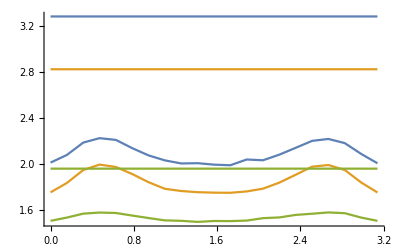

```mathematica
Show[ListLinePlot[{Efitvals8n,C3fitvals8n,C2fitvals8n,entropymean,fitvals},PlotRange->All],Plot[{pageentropy[2^4,2^4],pageentropy[2^3,2^5],pageentropy[2^2,2^6]},{x,0,Pi},PlotRange->All],PlotRange->All]
```

Page values for each part is different

```mathematica
ListLinePlot[Table[C3noise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

-Graphics-

## CC correct dt = pi/8 -- interaction unitary = exp(int*tau[i]*dt)

```mathematica
ECnoise8=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/ECanswers8.dat"]];
```

```mathematica
Dimensions[ECnoise8]
```

{4200}

```mathematica
ECnoise8n=Table[Drop[Drop[ECnoise8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
ECnoise8max=Table[{0.05*(n-1)*Pi,Max[ECnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ECnoise8mean=Table[{0.05 (n-1) Pi,Mean[ECnoise8n[[n]]]},{n,1,21}];
```

```mathematica
ECfitvals8 = Table[FindFit[Drop[ECnoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
ECfitvals8n = Table[{0.05( n-1) Pi,Flatten[ECfitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

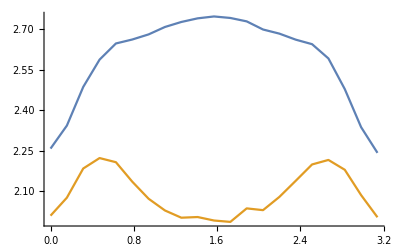

```mathematica
ListLinePlot[{ECfitvals8n,Efitvals8n},PlotRange->All]
```

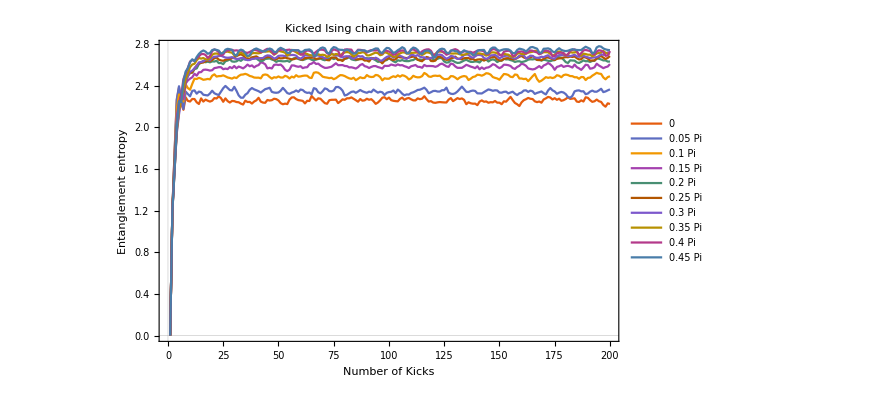

```mathematica
ListLinePlot[Table[ECnoise8n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

## correct dt = pi/128

```mathematica
Enoise128=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/Eanswers128.dat"]];
```

```mathematica
Dimensions[Enoise128]
```

{4200}

```mathematica
Enoise128n=Table[Drop[Drop[Enoise128,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[Enoise128n]
```

{21,200}

```mathematica
Enoise128max=Table[{0.05*(n-1)*Pi,Max[Enoise128n[[n]]]},{n,1,21}];
```

```mathematica
Enoise128mean=Table[{0.05 (n-1) Pi,Mean[Enoise128n[[n]]]},{n,1,21}];
```

```mathematica
Efitvals128 = Table[FindFit[Drop[Enoise128n[[n]],{1,150}],0*x+c,c,x],{n,1,21}];
```

```mathematica
Efitvals128n = Table[{0.05( n-1) Pi,Flatten[Efitvals128/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

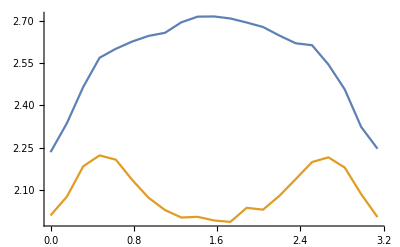

```mathematica
ListLinePlot[{Efitvals128n,Efitvals8n,entropymean,fitvals},PlotRange->All]
```

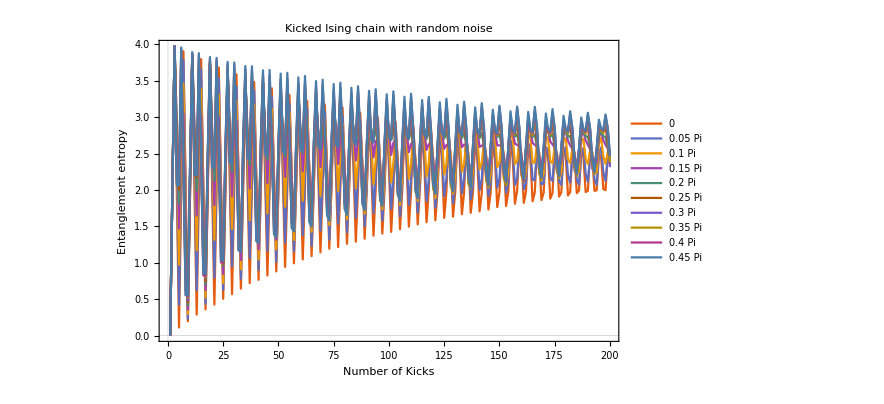

```mathematica
ListLinePlot[Table[Enoise128n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

## CCcorrect dt = pi/512

```mathematica
Enoise512=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/Eanswers512.dat"]];
```

```mathematica
Dimensions[Enoise512]
```

{10500}

```mathematica
Enoise512n=Table[Drop[Drop[Enoise512,-10500+500n],500(n-1)],{n,1,21}];
```

```mathematica
Dimensions[Enoise512n]
```

{21,500}

```mathematica
Enoise512max=Table[{0.05*(n-1)*Pi,Max[Enoise512n[[n]]]},{n,1,21}];
```

```mathematica
Enoise512mean=Table[{0.05 (n-1) Pi,Mean[Enoise512n[[n]]]},{n,1,21}];
```

```mathematica
Efitvals512 = Table[FindFit[Drop[Enoise512n[[n]],{1,150}],0*x+c,c,x],{n,1,21}];
```

```mathematica
Efitvals512n = Table[{0.05( n-1) Pi,Flatten[Efitvals512/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

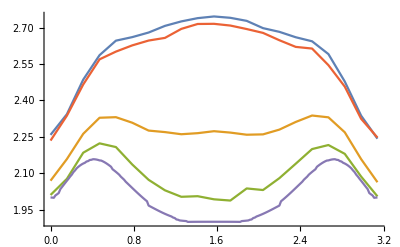

```mathematica
ListLinePlot[{ECfitvals8n,Efitvals512n,Efitvals8n,Efitvals128n,entropymean,fitvals},PlotRange->All]
```

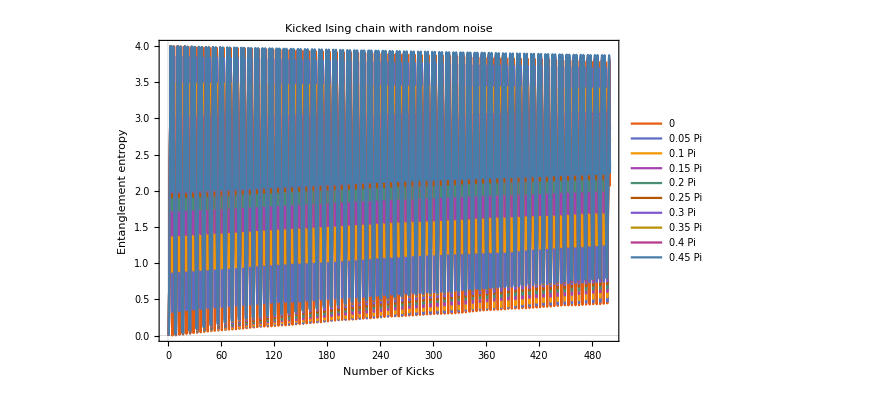

```mathematica
ListLinePlot[Table[Enoise512n[[i]],{i,1,10}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]},PlotLegends->Placed[{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},{0.5,0.53}]]
```

## dt = pi/8

#### datapoints

```mathematica
nois90={0.,0.3630888,0.41581805,0.54838985,0.58903883,0.67443704,0.70374006,0.74802173,0.77023374,0.7799963,0.79391026,0.80161342,0.81522262,0.8703467,0.88427884,0.88877554,0.90884475,0.94745429,0.95730368,0.94039351,0.95059238,0.93918189,0.94311041,0.9613399,0.96070648,0.97604086,0.98772604,0.99191927,0.99801651,0.99817979,0.99819399,1.00909471,1.01132624,0.98151235,0.98785393,1.00631849,1.00986397,1.01646256,1.01744932,1.02403947,1.02834987,1.03458382,1.04477916,1.05087582,1.04255789,1.00897474,1.0053303,1.01531073,1.01092485,1.02858163,1.0272489,1.01484673,1.01685415,0.99484358,0.98930749,0.98002927,0.97777693,1.00866649,1.00944935,1.01261036,1.01546833,1.00461918,1.01431367,1.01535425,1.02325678,1.04082575,1.03859184,1.01655226,1.02333297,1.0390341,1.04624519,1.02618944,1.01701845,1.04773637,1.04826367,1.0438188,1.0422117,1.04812837,1.04856935,1.03537067,1.02608302,1.02968984,1.03200759,1.02472103,1.02738923,1.02286838,1.02153173,1.04500446,1.05380747,1.0357905,1.03515249,1.02636061,1.01999706,1.03244976,1.03474101,1.03433774,1.02871827,1.01984703,1.0261919,1.02417507,1.02442604,1.03411301,1.02681481,1.02347242,1.02947797,1.02778966,1.03173726,1.02573291,1.02419159,1.02417731,1.01987697,1.03808143,1.05531463,1.05958706,1.06072888,1.05267839,1.05002417,1.06246968,1.05794433,1.0419298,1.05439148,1.07111964,1.06520872,1.06353873,1.06745737,1.06945663,1.06420282,1.04647985,1.05729756,1.0933293,1.08942572,1.08935605,1.10344446,1.10509785,1.0986824,1.09257049,1.09738949,1.09256468,1.09541861,1.0963513,1.08878666,1.09035703,1.09215466,1.08420891,1.07948157,1.07017539,1.06967189,1.05432896,1.0551398,1.07119892,1.07086628,1.06858147,1.05879691,1.0604597,1.0644507,1.06251771,1.06613727,1.086531,1.08789984,1.08934958,1.09176581,1.08537684,1.0872586,1.09208003,1.08736465,1.05834615,1.0577029,1.0650925,1.05688475,1.04488513,1.03386598,1.01524542,1.02680955,1.04443634,1.04144593,1.04932835,1.04891195,1.05341579,1.05030918,1.03501921,1.0311338,1.02928539,1.02601484,1.03449219,1.04284207,1.0611072,1.06183257,1.05389161,1.0559523,1.04104006,1.03895371,1.05550616,1.05159555,1.04130218,1.04526841,1.0528583,1.06191889,1.0333656,1.02271564,1.02559243}
```

{0.,0.363089,0.415818,0.54839,0.589039,0.674437,0.70374,0.748022,0.770234,0.779996,0.79391,0.801613,0.815223,0.870347,0.884279,0.888776,0.908845,0.947454,0.957304,0.940394,0.950592,0.939182,0.94311,0.96134,0.960706,0.976041,0.987726,0.991919,0.998017,0.99818,0.998194,1.00909,1.01133,0.981512,0.987854,1.00632,1.00986,1.01646,1.01745,1.02404,1.02835,1.03458,1.04478,1.05088,1.04256,1.00897,1.00533,1.01531,1.01092,1.02858,1.02725,1.01485,1.01685,0.994844,0.989307,0.980029,0.977777,1.00867,1.00945,1.01261,1.01547,1.00462,1.01431,1.01535,1.02326,1.04083,1.03859,1.01655,1.02333,1.03903,1.04625,1.02619,1.01702,1.04774,1.04826,1.04382,1.04221,1.04813,1.04857,1.03537,1.02608,1.02969,1.03201,1.02472,1.02739,1.02287,1.02153,1.045,1.05381,1.03579,1.03515,1.02636,1.02,1.03245,1.03474,1.03434,1.02872,1.01985,1.02619,1.02418,1.02443,1.03411,1.02681,1.02347,1.02948,1.02779,1.03174,1.02573,1.02419,1.02418,1.01988,1.03808,1.05531,1.05959,1.06073,1.05268,1.05002,1.06247,1.05794,1.04193,1.05439,1.07112,1.06521,1.06354,1.06746,1.06946,1.0642,1.04648,1.0573,1.09333,1.08943,1.08936,1.10344,1.1051,1.09868,1.09257,1.09739,1.09256,1.09542,1.09635,1.08879,1.09036,1.09215,1.08421,1.07948,1.07018,1.06967,1.05433,1.05514,1.0712,1.07087,1.06858,1.0588,1.06046,1.06445,1.06252,1.06614,1.08653,1.0879,1.08935,1.09177,1.08538,1.08726,1.09208,1.08736,1.05835,1.0577,1.06509,1.05688,1.04489,1.03387,1.01525,1.02681,1.04444,1.04145,1.04933,1.04891,1.05342,1.05031,1.03502,1.03113,1.02929,1.02601,1.03449,1.04284,1.06111,1.06183,1.05389,1.05595,1.04104,1.03895,1.05551,1.0516,1.0413,1.04527,1.05286,1.06192,1.03337,1.02272,1.02559}

```mathematica
nois0={0.,1.068,1.65407142,1.6451109,1.87213724,1.89769978,1.94955557,1.92937014,1.99636286,1.93939085,1.94387072,1.91603162,1.92970997,1.90850366,1.96707542,1.98729132,2.01558607,2.04161785,1.96738185,1.95637229,1.98502945,2.00111971,1.99778375,2.05814374,2.0315844,2.02828589,2.01555132,2.00184243,2.00881999,1.93101412,1.95577952,1.9901665,2.03529692,1.99356628,1.9670983,1.92438989,1.9463577,1.99489774,1.94081634,1.94649989,1.95965652,2.00752766,2.0635664,2.03742855,1.97228512,2.02305282,2.05035669,2.10286268,2.03862232,2.04344977,2.03518795,1.98164408,1.99966927,1.95986035,1.99295399,2.01148244,1.99531772,1.97044769,1.96245711,2.02752761,2.03826899,2.01534536,2.02635,2.00598706,2.00623989,1.97979421,1.97333188,1.99524929,2.03098203,2.04991737,2.0557355,2.04475095,2.04875961,2.00691613,1.98240059,1.97266896,2.00179632,1.98457307,2.01149484,2.00694289,1.98990555,2.03468477,2.09479044,2.07421555,2.01692731,2.00264423,2.03774278,1.99189235,1.97936561,1.98911679,2.0596787,2.06323578,2.01129225,2.04095686,2.00399754,2.00386067,2.04343789,2.03313796,1.98237335,2.0424847,1.99184097,1.98978323,1.98106089,1.95851023,2.02076107,2.04086607,2.07743373,2.07880767,2.0517045,1.99869773,2.03536904,2.00592259,1.97531323,2.04520738,2.03910093,2.0171397,2.02546835,2.04496497,2.01853476,1.99515181,2.03213069,2.07888441,2.05388962,2.03463909,2.01257026,2.00291137,2.01389487,2.05322806,2.03161811,2.04489365,2.04865567,2.05587337,2.02760892,2.02279895,2.04123331,2.05181162,2.06781095,2.01688579,2.04946698,2.05452013,2.01442312,2.01409962,2.02407526,1.98138023,2.01835997,2.02508936,2.00118394,1.98097371,1.99554887,2.04863084,2.0435599,2.00109392,2.05892102,2.04324607,2.04010205,2.07995689,2.0636053,2.01794084,2.0328805,2.12598935,2.12590615,2.06075799,2.02051124,2.02526205,1.98011806,1.96260262,2.01337351,2.06296868,2.04530781,2.06876505,2.04111716,2.03101536,2.03264046,2.02466207,1.97077501,2.01647382,2.00031611,1.98315654,2.01809908,1.99634733,2.00567624,2.04732235,2.06176331,2.03487682,2.0283754,2.0253392,2.04428054,2.03945984,2.04033781,2.04583217,2.05639811,2.02911407,2.05985066,2.07328078,2.02938057,2.05439907,2.06585519,2.00577767,2.05246356,2.02372829}
```

{0.,1.068,1.65407,1.64511,1.87214,1.8977,1.94956,1.92937,1.99636,1.93939,1.94387,1.91603,1.92971,1.9085,1.96708,1.98729,2.01559,2.04162,1.96738,1.95637,1.98503,2.00112,1.99778,2.05814,2.03158,2.02829,2.01555,2.00184,2.00882,1.93101,1.95578,1.99017,2.0353,1.99357,1.9671,1.92439,1.94636,1.9949,1.94082,1.9465,1.95966,2.00753,2.06357,2.03743,1.97229,2.02305,2.05036,2.10286,2.03862,2.04345,2.03519,1.98164,1.99967,1.95986,1.99295,2.01148,1.99532,1.97045,1.96246,2.02753,2.03827,2.01535,2.02635,2.00599,2.00624,1.97979,1.97333,1.99525,2.03098,2.04992,2.05574,2.04475,2.04876,2.00692,1.9824,1.97267,2.0018,1.98457,2.01149,2.00694,1.98991,2.03468,2.09479,2.07422,2.01693,2.00264,2.03774,1.99189,1.97937,1.98912,2.05968,2.06324,2.01129,2.04096,2.004,2.00386,2.04344,2.03314,1.98237,2.04248,1.99184,1.98978,1.98106,1.95851,2.02076,2.04087,2.07743,2.07881,2.0517,1.9987,2.03537,2.00592,1.97531,2.04521,2.0391,2.01714,2.02547,2.04496,2.01853,1.99515,2.03213,2.07888,2.05389,2.03464,2.01257,2.00291,2.01389,2.05323,2.03162,2.04489,2.04866,2.05587,2.02761,2.0228,2.04123,2.05181,2.06781,2.01689,2.04947,2.05452,2.01442,2.0141,2.02408,1.98138,2.01836,2.02509,2.00118,1.98097,1.99555,2.04863,2.04356,2.00109,2.05892,2.04325,2.0401,2.07996,2.06361,2.01794,2.03288,2.12599,2.12591,2.06076,2.02051,2.02526,1.98012,1.9626,2.01337,2.06297,2.04531,2.06877,2.04112,2.03102,2.03264,2.02466,1.97078,2.01647,2.00032,1.98316,2.0181,1.99635,2.00568,2.04732,2.06176,2.03488,2.02838,2.02534,2.04428,2.03946,2.04034,2.04583,2.0564,2.02911,2.05985,2.07328,2.02938,2.0544,2.06586,2.00578,2.05246,2.02373}

```mathematica
nois45={3.20342650*10^-16,6.42936412*10^-01,9.02253338*10^-01,1.06227814*10^+00,1.24462068*10^+00,1.32147149*10^+00,1.43765502*10^+00,1.47974063*10^+00,1.54660487*10^+00,1.59387270*10^+00,1.66095877*10^+00,1.68387246*10^+00,1.70742863*10^+00,1.73634470*10^+00,1.76769909*10^+00,1.75209689*10^+00,1.77429449*10^+00,1.79729994*10^+00,1.82740870*10^+00,1.87422578*10^+00,1.86648710*10^+00,1.85952048*10^+00,1.88349992*10^+00,1.90131918*10^+00,1.88293985*10^+00,1.87635426*10^+00,1.90660072*10^+00,1.91787962*10^+00,1.93659944*10^+00,1.95752727*10^+00,1.97325399*10^+00,1.99131049*10^+00,1.97104428*10^+00,1.94144193*10^+00,1.96038283*10^+00,1.97743733*10^+00,1.95777828*10^+00,1.94668511*10^+00,1.96914606*10^+00,1.95562371*10^+00,1.98374704*10^+00,2.01256330*10^+00,2.02143286*10^+00,2.03639624*10^+00,2.08477244*10^+00,2.09961851*10^+00,2.08196757*10^+00,2.06388842*10^+00,2.03158769*10^+00,2.00947808*10^+00,2.00509314*10^+00,2.00214400*10^+00,2.00392401*10^+00,2.02363183*10^+00,2.03730345*10^+00,2.00931511*10^+00,2.02175017*10^+00,2.05274903*10^+00,2.04031104*10^+00,2.05061506*10^+00,2.08044632*10^+00,2.04400434*10^+00,2.03221479*10^+00,2.06571020*10^+00,2.06943020*10^+00,2.05125673*10^+00,2.05539515*10^+00,2.05322105*10^+00,2.09901908*10^+00,2.10157362*10^+00,2.09335592*10^+00,2.09594851*10^+00,2.08863851*10^+00,2.08855467*10^+00,2.09395400*10^+00,2.08483160*10^+00,2.07636825*10^+00,2.07924985*10^+00,2.05998774*10^+00,2.06713394*10^+00,2.07636148*10^+00,2.06908357*10^+00,2.08809600*10^+00,2.10060116*10^+00,2.11685774*10^+00,2.11888974*10^+00,2.10136017*10^+00,2.12197324*10^+00,2.12526617*10^+00,2.13393833*10^+00,2.12192463*10^+00,2.11070374*10^+00,2.11447506*10^+00,2.13189536*10^+00,2.11563923*10^+00,2.09882037*10^+00,2.08819374*10^+00,2.11433932*10^+00,2.13864978*10^+00,2.12260163*10^+00,2.11903388*10^+00,2.12047511*10^+00,2.12932841*10^+00,2.14241791*10^+00,2.15335052*10^+00,2.14429102*10^+00,2.14271870*10^+00,2.14763149*10^+00,2.12931920*10^+00,2.10913506*10^+00,2.10529098*10^+00,2.08955767*10^+00,2.09602253*10^+00,2.09923762*10^+00,2.11546982*10^+00,2.12606404*10^+00,2.15210285*10^+00,2.16926807*10^+00,2.18908749*10^+00,2.15544643*10^+00,2.12336701*10^+00,2.10793850*10^+00,2.12661921*10^+00,2.12597671*10^+00,2.14333112*10^+00,2.17224234*10^+00,2.18442018*10^+00,2.19903309*10^+00,2.16422838*10^+00,2.13195077*10^+00,2.12947623*10^+00,2.14975552*10^+00,2.15490410*10^+00,2.16982640*10^+00,2.15973675*10^+00,2.12792719*10^+00,2.13379335*10^+00,2.10718025*10^+00,2.12457351*10^+00,2.13308652*10^+00,2.13536430*10^+00,2.13456524*10^+00,2.12453213*10^+00,2.14309907*10^+00,2.15138054*10^+00,2.14134639*10^+00,2.13219524*10^+00,2.08933048*10^+00,2.09942642*10^+00,2.13201081*10^+00,2.12702295*10^+00,2.11281097*10^+00,2.09555706*10^+00,2.09638457*10^+00,2.13210250*10^+00,2.14887621*10^+00,2.14611584*10^+00,2.14278097*10^+00,2.12729781*10^+00,2.14682692*10^+00,2.14339200*10^+00,2.11488008*10^+00,2.12153568*10^+00,2.11119447*10^+00,2.08803480*10^+00,2.07980488*10^+00,2.04392092*10^+00,2.02309696*10^+00,2.05958856*10^+00,2.07299502*10^+00,2.06891127*10^+00,2.10524921*10^+00,2.09768920*10^+00,2.09170124*10^+00,2.08447071*10^+00,2.09747420*10^+00,2.09452332*10^+00,2.09363014*10^+00,2.11060291*10^+00,2.12445953*10^+00,2.13778411*10^+00,2.12710799*10^+00,2.13210909*10^+00,2.09739532*10^+00,2.08619320*10^+00,2.04486555*10^+00,2.02414500*10^+00,2.08136509*10^+00,2.08776796*10^+00,2.06478242*10^+00,2.07114486*10^+00,2.06842525*10^+00,2.08101543*10^+00,2.07175011*10^+00,2.06277734*10^+00,2.04191522*10^+00,2.04283523*10^+00,2.05209673*10^+00,2.04839585*10^+00,2.07652833*10^+00}
```

{3.20343×10^-16,0.642936,0.902253,1.06228,1.24462,1.32147,1.43766,1.47974,1.5466,1.59387,1.66096,1.68387,1.70743,1.73634,1.7677,1.7521,1.77429,1.7973,1.82741,1.87423,1.86649,1.85952,1.8835,1.90132,1.88294,1.87635,1.9066,1.91788,1.9366,1.95753,1.97325,1.99131,1.97104,1.94144,1.96038,1.97744,1.95778,1.94669,1.96915,1.95562,1.98375,2.01256,2.02143,2.0364,2.08477,2.09962,2.08197,2.06389,2.03159,2.00948,2.00509,2.00214,2.00392,2.02363,2.0373,2.00932,2.02175,2.05275,2.04031,2.05062,2.08045,2.044,2.03221,2.06571,2.06943,2.05126,2.0554,2.05322,2.09902,2.10157,2.09336,2.09595,2.08864,2.08855,2.09395,2.08483,2.07637,2.07925,2.05999,2.06713,2.07636,2.06908,2.0881,2.1006,2.11686,2.11889,2.10136,2.12197,2.12527,2.13394,2.12192,2.1107,2.11448,2.1319,2.11564,2.09882,2.08819,2.11434,2.13865,2.1226,2.11903,2.12048,2.12933,2.14242,2.15335,2.14429,2.14272,2.14763,2.12932,2.10914,2.10529,2.08956,2.09602,2.09924,2.11547,2.12606,2.1521,2.16927,2.18909,2.15545,2.12337,2.10794,2.12662,2.12598,2.14333,2.17224,2.18442,2.19903,2.16423,2.13195,2.12948,2.14976,2.1549,2.16983,2.15974,2.12793,2.13379,2.10718,2.12457,2.13309,2.13536,2.13457,2.12453,2.1431,2.15138,2.14135,2.1322,2.08933,2.09943,2.13201,2.12702,2.11281,2.09556,2.09638,2.1321,2.14888,2.14612,2.14278,2.1273,2.14683,2.14339,2.11488,2.12154,2.11119,2.08803,2.0798,2.04392,2.0231,2.05959,2.073,2.06891,2.10525,2.09769,2.0917,2.08447,2.09747,2.09452,2.09363,2.1106,2.12446,2.13778,2.12711,2.13211,2.0974,2.08619,2.04487,2.02415,2.08137,2.08777,2.06478,2.07114,2.06843,2.08102,2.07175,2.06278,2.04192,2.04284,2.0521,2.0484,2.07653}

```mathematica
nois30={-6.40685301*10^-16,7.97263814*10^-01,1.23261731*10^+00,1.38713639*10^+00,1.54813411*10^+00,1.54878352*10^+00,1.67117759*10^+00,1.69021871*10^+00,1.74737174*10^+00,1.82325725*10^+00,1.86013312*10^+00,1.89274927*10^+00,1.94206961*10^+00,1.95269335*10^+00,1.99002845*10^+00,1.95218746*10^+00,1.96724537*10^+00,2.01137769*10^+00,2.02346819*10^+00,2.01269528*10^+00,2.03707334*10^+00,2.02198105*10^+00,2.05722218*10^+00,2.07008935*10^+00,2.10329650*10^+00,2.10405924*10^+00,2.11254456*10^+00,2.12757139*10^+00,2.12288266*10^+00,2.11172446*10^+00,2.11231385*10^+00,2.10278070*10^+00,2.12604356*10^+00,2.19045839*10^+00,2.17986587*10^+00,2.22317691*10^+00,2.21981042*10^+00,2.21324131*10^+00,2.18804930*10^+00,2.20630420*10^+00,2.22117099*10^+00,2.18463946*10^+00,2.21098402*10^+00,2.19870406*10^+00,2.19640253*10^+00,2.22481611*10^+00,2.22566729*10^+00,2.19333871*10^+00,2.22391926*10^+00,2.18977395*10^+00,2.17414626*10^+00,2.22112230*10^+00,2.21526015*10^+00,2.21794942*10^+00,2.23527118*10^+00,2.18367930*10^+00,2.20328081*10^+00,2.20619037*10^+00,2.21069923*10^+00,2.23957920*10^+00,2.26498780*10^+00,2.27075824*10^+00,2.23810915*10^+00,2.25909868*10^+00,2.28202732*10^+00,2.23238032*10^+00,2.21879590*10^+00,2.21180654*10^+00,2.24932723*10^+00,2.22777060*10^+00,2.23460082*10^+00,2.27868389*10^+00,2.29755287*10^+00,2.29170338*10^+00,2.29545756*10^+00,2.32243812*10^+00,2.27142558*10^+00,2.27033963*10^+00,2.25274584*10^+00,2.23843200*10^+00,2.21034971*10^+00,2.25069370*10^+00,2.25886418*10^+00,2.24960928*10^+00,2.25399313*10^+00,2.23179300*10^+00,2.28969187*10^+00,2.25783403*10^+00,2.27584761*10^+00,2.29778975*10^+00,2.28007118*10^+00,2.26122453*10^+00,2.27521212*10^+00,2.28328240*10^+00,2.27911090*10^+00,2.25933648*10^+00,2.24974725*10^+00,2.27769885*10^+00,2.25026960*10^+00,2.23956525*10^+00,2.24299236*10^+00,2.22131678*10^+00,2.25746478*10^+00,2.25027997*10^+00,2.23394075*10^+00,2.24960018*10^+00,2.24466067*10^+00,2.28062460*10^+00,2.27247206*10^+00,2.31141908*10^+00,2.31909623*10^+00,2.32976730*10^+00,2.32118618*10^+00,2.31025240*10^+00,2.32530295*10^+00,2.28645858*10^+00,2.29841207*10^+00,2.29758332*10^+00,2.29260727*10^+00,2.27648262*10^+00,2.28271169*10^+00,2.25703347*10^+00,2.28751905*10^+00,2.29274902*10^+00,2.28168347*10^+00,2.29883128*10^+00,2.28407390*10^+00,2.31314359*10^+00,2.29686369*10^+00,2.32218494*10^+00,2.32772331*10^+00,2.32940181*10^+00,2.30785405*10^+00,2.32364173*10^+00,2.31533078*10^+00,2.31422356*10^+00,2.32302237*10^+00,2.29150472*10^+00,2.31540851*10^+00,2.29670305*10^+00,2.30918744*10^+00,2.33736542*10^+00,2.33026380*10^+00,2.34887975*10^+00,2.33892101*10^+00,2.32564207*10^+00,2.32987455*10^+00,2.34940664*10^+00,2.33447164*10^+00,2.29726431*10^+00,2.31872281*10^+00,2.29391698*10^+00,2.31528384*10^+00,2.31378535*10^+00,2.26848783*10^+00,2.28137282*10^+00,2.30964471*10^+00,2.27704446*10^+00,2.26354704*10^+00,2.29704423*10^+00,2.30529439*10^+00,2.26179930*10^+00,2.26284297*10^+00,2.27161826*10^+00,2.25590061*10^+00,2.27761471*10^+00,2.26069544*10^+00,2.28124669*10^+00,2.30840477*10^+00,2.25452366*10^+00,2.23592855*10^+00,2.26017156*10^+00,2.28688706*10^+00,2.29047236*10^+00,2.31104788*10^+00,2.30968816*10^+00,2.29425943*10^+00,2.26555682*10^+00,2.24982619*10^+00,2.29076916*10^+00,2.31087556*10^+00,2.31472004*10^+00,2.33700767*10^+00,2.32437680*10^+00,2.31047000*10^+00,2.30292131*10^+00,2.32856062*10^+00,2.32435190*10^+00,2.30562048*10^+00,2.31346741*10^+00,2.27970638*10^+00,2.29521906*10^+00,2.29377397*10^+00,2.32570539*10^+00,2.30258504*10^+00,2.25625211*10^+00,2.26924094*10^+00,2.28582780*10^+00,2.26214524*10^+00,2.26650409*10^+00}
```

{-6.40685×10^-16,0.797264,1.23262,1.38714,1.54813,1.54878,1.67118,1.69022,1.74737,1.82326,1.86013,1.89275,1.94207,1.95269,1.99003,1.95219,1.96725,2.01138,2.02347,2.0127,2.03707,2.02198,2.05722,2.07009,2.1033,2.10406,2.11254,2.12757,2.12288,2.11172,2.11231,2.10278,2.12604,2.19046,2.17987,2.22318,2.21981,2.21324,2.18805,2.2063,2.22117,2.18464,2.21098,2.1987,2.1964,2.22482,2.22567,2.19334,2.22392,2.18977,2.17415,2.22112,2.21526,2.21795,2.23527,2.18368,2.20328,2.20619,2.2107,2.23958,2.26499,2.27076,2.23811,2.2591,2.28203,2.23238,2.2188,2.21181,2.24933,2.22777,2.2346,2.27868,2.29755,2.2917,2.29546,2.32244,2.27143,2.27034,2.25275,2.23843,2.21035,2.25069,2.25886,2.24961,2.25399,2.23179,2.28969,2.25783,2.27585,2.29779,2.28007,2.26122,2.27521,2.28328,2.27911,2.25934,2.24975,2.2777,2.25027,2.23957,2.24299,2.22132,2.25746,2.25028,2.23394,2.2496,2.24466,2.28062,2.27247,2.31142,2.3191,2.32977,2.32119,2.31025,2.3253,2.28646,2.29841,2.29758,2.29261,2.27648,2.28271,2.25703,2.28752,2.29275,2.28168,2.29883,2.28407,2.31314,2.29686,2.32218,2.32772,2.3294,2.30785,2.32364,2.31533,2.31422,2.32302,2.2915,2.31541,2.2967,2.30919,2.33737,2.33026,2.34888,2.33892,2.32564,2.32987,2.34941,2.33447,2.29726,2.31872,2.29392,2.31528,2.31379,2.26849,2.28137,2.30964,2.27704,2.26355,2.29704,2.30529,2.2618,2.26284,2.27162,2.2559,2.27761,2.2607,2.28125,2.3084,2.25452,2.23593,2.26017,2.28689,2.29047,2.31105,2.30969,2.29426,2.26556,2.24983,2.29077,2.31088,2.31472,2.33701,2.32438,2.31047,2.30292,2.32856,2.32435,2.30562,2.31347,2.27971,2.29522,2.29377,2.32571,2.30259,2.25625,2.26924,2.28583,2.26215,2.2665}

```mathematica
nois20={9.61027951*10^-16,9.60450832*10^-01,1.42059163*10^+00,1.53115080*10^+00,1.73016896*10^+00,1.70611448*10^+00,1.81321757*10^+00,1.85814524*10^+00,1.95925794*10^+00,1.94650051*10^+00,1.99636124*10^+00,2.01368490*10^+00,2.04035168*10^+00,2.05742592*10^+00,2.09234218*10^+00,2.06006235*10^+00,2.04267826*10^+00,2.01771546*10^+00,2.08375022*10^+00,2.11233750*10^+00,2.10372246*10^+00,2.08635399*10^+00,2.11729900*10^+00,2.10292153*10^+00,2.11753800*10^+00,2.10398601*10^+00,2.09958585*10^+00,2.12246088*10^+00,2.10741441*10^+00,2.10372556*10^+00,2.12241490*10^+00,2.14864856*10^+00,2.17560873*10^+00,2.16507948*10^+00,2.16917959*10^+00,2.18807944*10^+00,2.21612780*10^+00,2.21488415*10^+00,2.20824517*10^+00,2.22423731*10^+00,2.20289432*10^+00,2.20731279*10^+00,2.17784094*10^+00,2.16311926*10^+00,2.14772336*10^+00,2.17321597*10^+00,2.19615514*10^+00,2.17543622*10^+00,2.20554791*10^+00,2.20049212*10^+00,2.16603971*10^+00,2.19314832*10^+00,2.20961594*10^+00,2.21078727*10^+00,2.19902414*10^+00,2.23265556*10^+00,2.24243937*10^+00,2.21403498*10^+00,2.19732959*10^+00,2.16806496*10^+00,2.20183022*10^+00,2.17176858*10^+00,2.17209982*10^+00,2.18054079*10^+00,2.16644826*10^+00,2.18515640*10^+00,2.18057759*10^+00,2.21675829*10^+00,2.18499217*10^+00,2.19868923*10^+00,2.21072734*10^+00,2.19701016*10^+00,2.24078874*10^+00,2.22415267*10^+00,2.20585409*10^+00,2.19290308*10^+00,2.21407836*10^+00,2.20523370*10^+00,2.21673169*10^+00,2.22828470*10^+00,2.24199786*10^+00,2.24385823*10^+00,2.22915707*10^+00,2.21808743*10^+00,2.23787245*10^+00,2.23821034*10^+00,2.22757451*10^+00,2.23069272*10^+00,2.21140768*10^+00,2.23806320*10^+00,2.25843643*10^+00,2.22184723*10^+00,2.23250610*10^+00,2.23897606*10^+00,2.27425118*10^+00,2.26383443*10^+00,2.25823006*10^+00,2.27270175*10^+00,2.22929039*10^+00,2.24073794*10^+00,2.21539980*10^+00,2.17314807*10^+00,2.21677267*10^+00,2.24760295*10^+00,2.26063514*10^+00,2.25552861*10^+00,2.22617698*10^+00,2.24968987*10^+00,2.25549584*10^+00,2.24736614*10^+00,2.24689741*10^+00,2.24237203*10^+00,2.24241833*10^+00,2.26682064*10^+00,2.28078708*10^+00,2.25777680*10^+00,2.24337452*10^+00,2.27402430*10^+00,2.23551923*10^+00,2.22639344*10^+00,2.22256797*10^+00,2.20470821*10^+00,2.22088944*10^+00,2.22754225*10^+00,2.22028378*10^+00,2.24082398*10^+00,2.26662393*10^+00,2.24107964*10^+00,2.26621382*10^+00,2.22617026*10^+00,2.23473282*10^+00,2.27818506*10^+00,2.28119666*10^+00,2.27787943*10^+00,2.27949638*10^+00,2.25869497*10^+00,2.26066250*10^+00,2.26223318*10^+00,2.24864623*10^+00,2.25990768*10^+00,2.25591218*10^+00,2.27351944*10^+00,2.25632164*10^+00,2.28223140*10^+00,2.25466718*10^+00,2.23646946*10^+00,2.24726585*10^+00,2.25258892*10^+00,2.24608001*10^+00,2.19674024*10^+00,2.20277168*10^+00,2.18886766*10^+00,2.21158827*10^+00,2.23852308*10^+00,2.23287317*10^+00,2.28003195*10^+00,2.26937320*10^+00,2.23366199*10^+00,2.24269466*10^+00,2.23306430*10^+00,2.23771616*10^+00,2.24548455*10^+00,2.25496459*10^+00,2.24892643*10^+00,2.20771335*10^+00,2.20789884*10^+00,2.21483436*10^+00,2.24194225*10^+00,2.26666698*10^+00,2.25149716*10^+00,2.24757491*10^+00,2.21410521*10^+00,2.24865956*10^+00,2.25165150*10^+00,2.24230754*10^+00,2.27200250*10^+00,2.21838275*10^+00,2.22631574*10^+00,2.23523076*10^+00,2.24847694*10^+00,2.27286946*10^+00,2.25555870*10^+00,2.25117433*10^+00,2.23753777*10^+00,2.24293361*10^+00,2.23169755*10^+00,2.25547100*10^+00,2.23585916*10^+00,2.20860068*10^+00,2.26147954*10^+00,2.28426723*10^+00,2.28777890*10^+00,2.28247349*10^+00,2.26253726*10^+00,2.24744944*10^+00,2.27080496*10^+00,2.30982846*10^+00,2.27245664*10^+00,2.25540173*10^+00,2.26198042*10^+00}
```

{9.61028×10^-16,0.960451,1.42059,1.53115,1.73017,1.70611,1.81322,1.85815,1.95926,1.9465,1.99636,2.01368,2.04035,2.05743,2.09234,2.06006,2.04268,2.01772,2.08375,2.11234,2.10372,2.08635,2.1173,2.10292,2.11754,2.10399,2.09959,2.12246,2.10741,2.10373,2.12241,2.14865,2.17561,2.16508,2.16918,2.18808,2.21613,2.21488,2.20825,2.22424,2.20289,2.20731,2.17784,2.16312,2.14772,2.17322,2.19616,2.17544,2.20555,2.20049,2.16604,2.19315,2.20962,2.21079,2.19902,2.23266,2.24244,2.21403,2.19733,2.16806,2.20183,2.17177,2.1721,2.18054,2.16645,2.18516,2.18058,2.21676,2.18499,2.19869,2.21073,2.19701,2.24079,2.22415,2.20585,2.1929,2.21408,2.20523,2.21673,2.22828,2.242,2.24386,2.22916,2.21809,2.23787,2.23821,2.22757,2.23069,2.21141,2.23806,2.25844,2.22185,2.23251,2.23898,2.27425,2.26383,2.25823,2.2727,2.22929,2.24074,2.2154,2.17315,2.21677,2.2476,2.26064,2.25553,2.22618,2.24969,2.2555,2.24737,2.2469,2.24237,2.24242,2.26682,2.28079,2.25778,2.24337,2.27402,2.23552,2.22639,2.22257,2.20471,2.22089,2.22754,2.22028,2.24082,2.26662,2.24108,2.26621,2.22617,2.23473,2.27819,2.2812,2.27788,2.2795,2.25869,2.26066,2.26223,2.24865,2.25991,2.25591,2.27352,2.25632,2.28223,2.25467,2.23647,2.24727,2.25259,2.24608,2.19674,2.20277,2.18887,2.21159,2.23852,2.23287,2.28003,2.26937,2.23366,2.24269,2.23306,2.23772,2.24548,2.25496,2.24893,2.20771,2.2079,2.21483,2.24194,2.26667,2.2515,2.24757,2.21411,2.24866,2.25165,2.24231,2.272,2.21838,2.22632,2.23523,2.24848,2.27287,2.25556,2.25117,2.23754,2.24293,2.2317,2.25547,2.23586,2.2086,2.26148,2.28427,2.28778,2.28247,2.26254,2.24745,2.2708,2.30983,2.27246,2.2554,2.26198}

```mathematica
nois135={-9.61027951*10^-16,6.37687951*10^-01,8.89139097*10^-01,1.07608576*10^+00,1.23873726*10^+00,1.31258340*10^+00,1.41431443*10^+00,1.49965019*10^+00,1.58344393*10^+00,1.59675734*10^+00,1.67329447*10^+00,1.66662846*10^+00,1.70658919*10^+00,1.73849154*10^+00,1.77047326*10^+00,1.78231025*10^+00,1.79773272*10^+00,1.79544213*10^+00,1.81755878*10^+00,1.84873853*10^+00,1.86175010*10^+00,1.86541025*10^+00,1.87259093*10^+00,1.86809115*10^+00,1.88330118*10^+00,1.89415686*10^+00,1.91341512*10^+00,1.91307659*10^+00,1.90250727*10^+00,1.90651213*10^+00,1.91586886*10^+00,1.91866552*10^+00,1.92632191*10^+00,1.97251411*10^+00,1.97878950*10^+00,1.90314875*10^+00,1.90142577*10^+00,1.95356806*10^+00,1.98478228*10^+00,1.97386502*10^+00,1.97439292*10^+00,1.95813181*10^+00,1.95174544*10^+00,1.96841652*10^+00,1.97206226*10^+00,1.98133656*10^+00,1.96078301*10^+00,1.96083313*10^+00,1.96016376*10^+00,1.98446408*10^+00,1.98722147*10^+00,1.96826302*10^+00,1.98120380*10^+00,1.96859440*10^+00,1.96897737*10^+00,1.99168393*10^+00,1.98547670*10^+00,2.02272635*10^+00,2.02701666*10^+00,2.01232945*10^+00,2.02637103*10^+00,2.02281163*10^+00,2.03743857*10^+00,2.06349599*10^+00,2.07685021*10^+00,2.03679944*10^+00,2.04790204*10^+00,2.06221262*10^+00,2.05998529*10^+00,2.07921536*10^+00,2.10192111*10^+00,2.06359459*10^+00,2.05273691*10^+00,2.03406269*10^+00,2.02830419*10^+00,2.06872987*10^+00,2.04869675*10^+00,2.04670542*10^+00,2.03968512*10^+00,2.02240918*10^+00,2.02113910*10^+00,2.04633338*10^+00,2.05896741*10^+00,2.04678966*10^+00,2.06990112*10^+00,2.09181716*10^+00,2.08140103*10^+00,2.05436335*10^+00,2.03740949*10^+00,2.05989075*10^+00,2.05861292*10^+00,2.05562442*10^+00,2.05097360*10^+00,2.09306774*10^+00,2.11812176*10^+00,2.11622407*10^+00,2.10669605*10^+00,2.10691982*10^+00,2.08987204*10^+00,2.06935549*10^+00,2.08884978*10^+00,2.07621952*10^+00,2.08364638*10^+00,2.06877056*10^+00,2.05396199*10^+00,2.06118364*10^+00,2.05896427*10^+00,2.05192085*10^+00,2.03156808*10^+00,2.04844095*10^+00,2.04684735*10^+00,2.06470555*10^+00,2.10024064*10^+00,2.08317367*10^+00,2.08061486*10^+00,2.06444258*10^+00,2.05832499*10^+00,2.06538409*10^+00,2.06609222*10^+00,2.07411873*10^+00,2.08955227*10^+00,2.09879434*10^+00,2.07506304*10^+00,2.06941925*10^+00,2.09219337*10^+00,2.08081041*10^+00,2.07717283*10^+00,2.11263588*10^+00,2.13013649*10^+00,2.09758566*10^+00,2.08411017*10^+00,2.12754675*10^+00,2.15493912*10^+00,2.14121399*10^+00,2.13517965*10^+00,2.11056747*10^+00,2.11937238*10^+00,2.11072291*10^+00,2.08677731*10^+00,2.08497074*10^+00,2.10391030*10^+00,2.10777349*10^+00,2.07275978*10^+00,2.09926596*10^+00,2.11452260*10^+00,2.11112561*10^+00,2.10731151*10^+00,2.06224196*10^+00,2.09665042*10^+00,2.12318305*10^+00,2.13764415*10^+00,2.14223723*10^+00,2.12541740*10^+00,2.13220147*10^+00,2.12561787*10^+00,2.14740518*10^+00,2.12903778*10^+00,2.11193754*10^+00,2.10722519*10^+00,2.09969944*10^+00,2.09163900*10^+00,2.07725517*10^+00,2.08413617*10^+00,2.10319308*10^+00,2.13038929*10^+00,2.15525061*10^+00,2.15707893*10^+00,2.12887938*10^+00,2.10851724*10^+00,2.10160925*10^+00,2.12079158*10^+00,2.15131121*10^+00,2.15223894*10^+00,2.13105514*10^+00,2.13025362*10^+00,2.13594531*10^+00,2.14755974*10^+00,2.12064423*10^+00,2.08911357*10^+00,2.07747907*10^+00,2.07693066*10^+00,2.08348949*10^+00,2.09664181*10^+00,2.11083327*10^+00,2.10734658*10^+00,2.11964842*10^+00,2.14087229*10^+00,2.11634905*10^+00,2.10156606*10^+00,2.11582118*10^+00,2.12064334*10^+00,2.10721963*10^+00,2.11991701*10^+00,2.13204263*10^+00,2.11218768*10^+00,2.13107437*10^+00,2.13369715*10^+00,2.11223386*10^+00,2.12950295*10^+00,2.13571758*10^+00}
```

{-9.61028×10^-16,0.637688,0.889139,1.07609,1.23874,1.31258,1.41431,1.49965,1.58344,1.59676,1.67329,1.66663,1.70659,1.73849,1.77047,1.78231,1.79773,1.79544,1.81756,1.84874,1.86175,1.86541,1.87259,1.86809,1.8833,1.89416,1.91342,1.91308,1.90251,1.90651,1.91587,1.91867,1.92632,1.97251,1.97879,1.90315,1.90143,1.95357,1.98478,1.97387,1.97439,1.95813,1.95175,1.96842,1.97206,1.98134,1.96078,1.96083,1.96016,1.98446,1.98722,1.96826,1.9812,1.96859,1.96898,1.99168,1.98548,2.02273,2.02702,2.01233,2.02637,2.02281,2.03744,2.0635,2.07685,2.0368,2.0479,2.06221,2.05999,2.07922,2.10192,2.06359,2.05274,2.03406,2.0283,2.06873,2.0487,2.04671,2.03969,2.02241,2.02114,2.04633,2.05897,2.04679,2.0699,2.09182,2.0814,2.05436,2.03741,2.05989,2.05861,2.05562,2.05097,2.09307,2.11812,2.11622,2.1067,2.10692,2.08987,2.06936,2.08885,2.07622,2.08365,2.06877,2.05396,2.06118,2.05896,2.05192,2.03157,2.04844,2.04685,2.06471,2.10024,2.08317,2.08061,2.06444,2.05832,2.06538,2.06609,2.07412,2.08955,2.09879,2.07506,2.06942,2.09219,2.08081,2.07717,2.11264,2.13014,2.09759,2.08411,2.12755,2.15494,2.14121,2.13518,2.11057,2.11937,2.11072,2.08678,2.08497,2.10391,2.10777,2.07276,2.09927,2.11452,2.11113,2.10731,2.06224,2.09665,2.12318,2.13764,2.14224,2.12542,2.1322,2.12562,2.14741,2.12904,2.11194,2.10723,2.0997,2.09164,2.07726,2.08414,2.10319,2.13039,2.15525,2.15708,2.12888,2.10852,2.10161,2.12079,2.15131,2.15224,2.13106,2.13025,2.13595,2.14756,2.12064,2.08911,2.07748,2.07693,2.08349,2.09664,2.11083,2.10735,2.11965,2.14087,2.11635,2.10157,2.11582,2.12064,2.10722,2.11992,2.13204,2.11219,2.13107,2.1337,2.11223,2.1295,2.13572}

```mathematica
nois60={-3.20342650*10^-16,4.92985345*10^-01,6.41673496*10^-01,8.35201060*10^-01,9.36276649*10^-01,9.78191355*10^-01,1.04478185*10^+00,1.15443407*10^+00,1.21485031*10^+00,1.23258206*10^+00,1.28823664*10^+00,1.34989420*10^+00,1.37451431*10^+00,1.35801190*10^+00,1.36877790*10^+00,1.34125740*10^+00,1.35270324*10^+00,1.42191246*10^+00,1.44783544*10^+00,1.45142748*10^+00,1.46804748*10^+00,1.46192561*10^+00,1.47615924*10^+00,1.47992630*10^+00,1.52310071*10^+00,1.56298039*10^+00,1.56736259*10^+00,1.55835650*10^+00,1.55435993*10^+00,1.56125927*10^+00,1.58069415*10^+00,1.58109367*10^+00,1.58482839*10^+00,1.57283277*10^+00,1.57608506*10^+00,1.62420160*10^+00,1.63423034*10^+00,1.61511325*10^+00,1.60342895*10^+00,1.58496625*10^+00,1.59257133*10^+00,1.62542644*10^+00,1.62022463*10^+00,1.62127026*10^+00,1.63950702*10^+00,1.65891564*10^+00,1.68851578*10^+00,1.70268143*10^+00,1.70974946*10^+00,1.68756292*10^+00,1.67312894*10^+00,1.68818055*10^+00,1.68711923*10^+00,1.65789611*10^+00,1.65002327*10^+00,1.64869930*10^+00,1.64107010*10^+00,1.65269137*10^+00,1.65321262*10^+00,1.62135219*10^+00,1.61485475*10^+00,1.63336507*10^+00,1.63869192*10^+00,1.66957741*10^+00,1.67459989*10^+00,1.66308381*10^+00,1.67205802*10^+00,1.68062035*10^+00,1.67698863*10^+00,1.66869412*10^+00,1.66826070*10^+00,1.64903899*10^+00,1.65590760*10^+00,1.68247044*10^+00,1.67468214*10^+00,1.64494617*10^+00,1.66464628*10^+00,1.69808833*10^+00,1.67415205*10^+00,1.66266395*10^+00,1.67642780*10^+00,1.68087589*10^+00,1.67258761*10^+00,1.64828460*10^+00,1.64859752*10^+00,1.65515199*10^+00,1.64991662*10^+00,1.66150250*10^+00,1.68866752*10^+00,1.69321927*10^+00,1.71516010*10^+00,1.75325595*10^+00,1.75403230*10^+00,1.73224291*10^+00,1.71919507*10^+00,1.68388540*10^+00,1.66100357*10^+00,1.66599293*10^+00,1.66216657*10^+00,1.64555474*10^+00,1.64755914*10^+00,1.66930716*10^+00,1.67404220*10^+00,1.66775880*10^+00,1.67666322*10^+00,1.69083770*10^+00,1.67588953*10^+00,1.65810838*10^+00,1.64411952*10^+00,1.63018041*10^+00,1.62581239*10^+00,1.63111733*10^+00,1.63443279*10^+00,1.64120969*10^+00,1.64621891*10^+00,1.66183076*10^+00,1.65722463*10^+00,1.63839956*10^+00,1.62396401*10^+00,1.61426077*10^+00,1.63847014*10^+00,1.68792568*10^+00,1.71305500*10^+00,1.71377395*10^+00,1.69266383*10^+00,1.67713044*10^+00,1.67561089*10^+00,1.68188531*10^+00,1.67218527*10^+00,1.65354676*10^+00,1.66268353*10^+00,1.67555680*10^+00,1.68348983*10^+00,1.69389459*10^+00,1.71583188*10^+00,1.71778453*10^+00,1.72243353*10^+00,1.69852165*10^+00,1.69064515*10^+00,1.68611857*10^+00,1.69983413*10^+00,1.72779325*10^+00,1.71803111*10^+00,1.69277889*10^+00,1.67358756*10^+00,1.68094074*10^+00,1.68752016*10^+00,1.67968893*10^+00,1.66767258*10^+00,1.65679323*10^+00,1.66200092*10^+00,1.63112742*10^+00,1.62502948*10^+00,1.62638455*10^+00,1.62748535*10^+00,1.63995129*10^+00,1.64181492*10^+00,1.64403722*10^+00,1.63572155*10^+00,1.63663753*10^+00,1.63760227*10^+00,1.64888233*10^+00,1.65974979*10^+00,1.68818816*10^+00,1.68955730*10^+00,1.68415412*10^+00,1.70382804*10^+00,1.70691944*10^+00,1.68674791*10^+00,1.68984671*10^+00,1.69995503*10^+00,1.69070989*10^+00,1.68805867*10^+00,1.68666587*10^+00,1.70047095*10^+00,1.68763375*10^+00,1.68331683*10^+00,1.73005497*10^+00,1.74708285*10^+00,1.73009325*10^+00,1.72830941*10^+00,1.74473203*10^+00,1.72240816*10^+00,1.68493702*10^+00,1.67959742*10^+00,1.69164958*10^+00,1.71132454*10^+00,1.72387152*10^+00,1.73246097*10^+00,1.70699462*10^+00,1.68100344*10^+00,1.68956439*10^+00,1.69776006*10^+00,1.69150277*10^+00,1.70177945*10^+00,1.72033916*10^+00,1.71982135*10^+00,1.74365567*10^+00,1.75620538*10^+00,1.76890338*10^+00}
```

{-3.20343×10^-16,0.492985,0.641673,0.835201,0.936277,0.978191,1.04478,1.15443,1.21485,1.23258,1.28824,1.34989,1.37451,1.35801,1.36878,1.34126,1.3527,1.42191,1.44784,1.45143,1.46805,1.46193,1.47616,1.47993,1.5231,1.56298,1.56736,1.55836,1.55436,1.56126,1.58069,1.58109,1.58483,1.57283,1.57609,1.6242,1.63423,1.61511,1.60343,1.58497,1.59257,1.62543,1.62022,1.62127,1.63951,1.65892,1.68852,1.70268,1.70975,1.68756,1.67313,1.68818,1.68712,1.6579,1.65002,1.6487,1.64107,1.65269,1.65321,1.62135,1.61485,1.63337,1.63869,1.66958,1.6746,1.66308,1.67206,1.68062,1.67699,1.66869,1.66826,1.64904,1.65591,1.68247,1.67468,1.64495,1.66465,1.69809,1.67415,1.66266,1.67643,1.68088,1.67259,1.64828,1.6486,1.65515,1.64992,1.6615,1.68867,1.69322,1.71516,1.75326,1.75403,1.73224,1.7192,1.68389,1.661,1.66599,1.66217,1.64555,1.64756,1.66931,1.67404,1.66776,1.67666,1.69084,1.67589,1.65811,1.64412,1.63018,1.62581,1.63112,1.63443,1.64121,1.64622,1.66183,1.65722,1.6384,1.62396,1.61426,1.63847,1.68793,1.71306,1.71377,1.69266,1.67713,1.67561,1.68189,1.67219,1.65355,1.66268,1.67556,1.68349,1.69389,1.71583,1.71778,1.72243,1.69852,1.69065,1.68612,1.69983,1.72779,1.71803,1.69278,1.67359,1.68094,1.68752,1.67969,1.66767,1.65679,1.662,1.63113,1.62503,1.62638,1.62749,1.63995,1.64181,1.64404,1.63572,1.63664,1.6376,1.64888,1.65975,1.68819,1.68956,1.68415,1.70383,1.70692,1.68675,1.68985,1.69996,1.69071,1.68806,1.68667,1.70047,1.68763,1.68332,1.73005,1.74708,1.73009,1.72831,1.74473,1.72241,1.68494,1.6796,1.69165,1.71132,1.72387,1.73246,1.70699,1.681,1.68956,1.69776,1.6915,1.70178,1.72034,1.71982,1.74366,1.75621,1.7689}

```mathematica
nois180={0.,1.036,1.61080443,1.69581354,1.8244013,1.78983951,1.88196852,1.9683635,2.03383598,1.97127675,1.99743215,1.97114687,1.96323419,1.88862487,1.98704857,2.00907301,1.99336881,2.02917363,2.02058812,2.01106323,2.04221349,2.06370737,2.04857928,2.03312113,2.05948602,2.02018616,2.03725137,2.01258995,1.98060727,2.05307654,2.06302414,2.00083801,1.98849442,2.02991295,2.0343243,1.97599575,2.05290745,2.07607619,2.02684454,2.02014543,2.00682741,1.98454695,2.02349979,2.01681057,1.97222278,2.0306406,2.00200771,1.94078149,1.96114153,1.96328388,2.02141681,2.03932,2.05300844,1.99758201,1.98040859,2.03338065,2.04887319,2.06569642,2.0195819,2.07419461,2.0034409,2.00965575,2.03595857,2.04112365,2.02076282,1.98694589,2.03975784,2.04791222,2.05334995,2.03491269,2.06664689,2.04072859,2.07504591,2.03343362,2.05577723,1.9622153,1.92389679,1.99493883,2.0397259,2.02916265,1.96721294,1.95173346,2.00918404,2.00520947,1.99632751,2.01016469,2.02042833,2.02354335,2.02670271,2.06605208,2.05551767,2.04731347,2.00224933,1.99531657,1.95506017,1.97250418,1.98253371,1.99898589,1.98682753,2.00077581,1.99454828,1.98470805,2.04360893,2.02964278,2.01447317,2.06282033,2.04999465,2.03124106,2.04006807,2.02624482,2.02686027,2.06896611,2.02678631,1.98397483,2.00404794,2.04420121,2.05674968,2.03704518,2.03426183,2.03892984,1.99029944,1.9890203,2.02950212,2.01220509,2.03358421,2.02879542,2.04715618,2.04801043,2.01311079,2.0277753,2.05300684,1.99500227,1.98385363,2.00641159,2.01782257,2.02190558,2.01949459,2.03902536,2.06566674,2.03177884,2.01734948,2.02386722,2.00428103,2.03082529,2.04536881,2.00179065,1.99453026,1.98902425,2.00554811,2.01075414,2.00517435,2.04567069,2.0426154,2.0073737,2.02918114,2.0611284,2.05232629,2.04743901,2.00661101,2.03395982,2.00859481,2.01708489,2.00210403,2.02868803,2.00611419,1.96926593,2.02529508,2.05536976,2.01655921,2.00197527,2.01559477,2.03083229,2.03011643,2.01704832,2.068319,2.06765847,2.07267804,2.0624478,1.97560281,1.99881643,2.03339124,2.04164599,2.03510936,2.00008573,1.94787707,1.94951787,2.03781992,2.01980098,2.01764093,2.02457195,1.9883992,2.06216454,2.08062808,2.0130989,2.00621505,2.00711617,2.00788296,2.04209836,2.03360055,2.03122598}
```

{0.,1.036,1.6108,1.69581,1.8244,1.78984,1.88197,1.96836,2.03384,1.97128,1.99743,1.97115,1.96323,1.88862,1.98705,2.00907,1.99337,2.02917,2.02059,2.01106,2.04221,2.06371,2.04858,2.03312,2.05949,2.02019,2.03725,2.01259,1.98061,2.05308,2.06302,2.00084,1.98849,2.02991,2.03432,1.976,2.05291,2.07608,2.02684,2.02015,2.00683,1.98455,2.0235,2.01681,1.97222,2.03064,2.00201,1.94078,1.96114,1.96328,2.02142,2.03932,2.05301,1.99758,1.98041,2.03338,2.04887,2.0657,2.01958,2.07419,2.00344,2.00966,2.03596,2.04112,2.02076,1.98695,2.03976,2.04791,2.05335,2.03491,2.06665,2.04073,2.07505,2.03343,2.05578,1.96222,1.9239,1.99494,2.03973,2.02916,1.96721,1.95173,2.00918,2.00521,1.99633,2.01016,2.02043,2.02354,2.0267,2.06605,2.05552,2.04731,2.00225,1.99532,1.95506,1.9725,1.98253,1.99899,1.98683,2.00078,1.99455,1.98471,2.04361,2.02964,2.01447,2.06282,2.04999,2.03124,2.04007,2.02624,2.02686,2.06897,2.02679,1.98397,2.00405,2.0442,2.05675,2.03705,2.03426,2.03893,1.9903,1.98902,2.0295,2.01221,2.03358,2.0288,2.04716,2.04801,2.01311,2.02778,2.05301,1.995,1.98385,2.00641,2.01782,2.02191,2.01949,2.03903,2.06567,2.03178,2.01735,2.02387,2.00428,2.03083,2.04537,2.00179,1.99453,1.98902,2.00555,2.01075,2.00517,2.04567,2.04262,2.00737,2.02918,2.06113,2.05233,2.04744,2.00661,2.03396,2.00859,2.01708,2.0021,2.02869,2.00611,1.96927,2.0253,2.05537,2.01656,2.00198,2.01559,2.03083,2.03012,2.01705,2.06832,2.06766,2.07268,2.06245,1.9756,1.99882,2.03339,2.04165,2.03511,2.00009,1.94788,1.94952,2.03782,2.0198,2.01764,2.02457,1.9884,2.06216,2.08063,2.0131,2.00622,2.00712,2.00788,2.0421,2.0336,2.03123}

```mathematica
nois150={-3.20342650*10^-16,7.51141114*10^-01,1.21028440*10^+00,1.33136488*10^+00,1.50227208*10^+00,1.59278089*10^+00,1.67899175*10^+00,1.73490245*10^+00,1.80881747*10^+00,1.81426002*10^+00,1.87819218*10^+00,1.89804615*10^+00,1.90876539*10^+00,1.93381400*10^+00,1.94729158*10^+00,1.99036255*10^+00,2.07331725*10^+00,2.08896864*10^+00,2.12451247*10^+00,2.13652947*10^+00,2.13372131*10^+00,2.08082869*10^+00,2.11254345*10^+00,2.13415309*10^+00,2.13503201*10^+00,2.10822732*10^+00,2.04936326*10^+00,2.09351081*10^+00,2.11440193*10^+00,2.14175807*10^+00,2.13661890*10^+00,2.13293421*10^+00,2.15754393*10^+00,2.15508613*10^+00,2.16229263*10^+00,2.14545879*10^+00,2.16004627*10^+00,2.18031421*10^+00,2.13976632*10^+00,2.15298611*10^+00,2.14727189*10^+00,2.13276353*10^+00,2.17120133*10^+00,2.16900062*10^+00,2.19015873*10^+00,2.18801987*10^+00,2.18118621*10^+00,2.17429489*10^+00,2.18762340*10^+00,2.25300224*10^+00,2.23737442*10^+00,2.18488040*10^+00,2.20276852*10^+00,2.19192503*10^+00,2.16812027*10^+00,2.18970610*10^+00,2.20007237*10^+00,2.17978781*10^+00,2.20302345*10^+00,2.21651919*10^+00,2.20412455*10^+00,2.24481152*10^+00,2.25864432*10^+00,2.25040545*10^+00,2.24919137*10^+00,2.25975919*10^+00,2.26702716*10^+00,2.28190049*10^+00,2.26334867*10^+00,2.25504663*10^+00,2.26482683*10^+00,2.27780915*10^+00,2.30455092*10^+00,2.25200930*10^+00,2.22621788*10^+00,2.22073163*10^+00,2.24626249*10^+00,2.26222048*10^+00,2.22579793*10^+00,2.24038743*10^+00,2.26005809*10^+00,2.28023103*10^+00,2.25939178*10^+00,2.26405558*10^+00,2.30525974*10^+00,2.27032451*10^+00,2.22325108*10^+00,2.22274080*10^+00,2.21367018*10^+00,2.24715226*10^+00,2.26332097*10^+00,2.27090378*10^+00,2.29988781*10^+00,2.29683726*10^+00,2.30505746*10^+00,2.26310924*10^+00,2.27913743*10^+00,2.30591027*10^+00,2.30210497*10^+00,2.30682292*10^+00,2.28518718*10^+00,2.27471889*10^+00,2.27235780*10^+00,2.27279032*10^+00,2.28767006*10^+00,2.26679834*10^+00,2.27712245*10^+00,2.28016919*10^+00,2.31671604*10^+00,2.32498598*10^+00,2.29806504*10^+00,2.29430683*10^+00,2.29905462*10^+00,2.30704258*10^+00,2.30459066*10^+00,2.31962186*10^+00,2.33836047*10^+00,2.33982435*10^+00,2.32008270*10^+00,2.31647836*10^+00,2.30017207*10^+00,2.29884563*10^+00,2.31032873*10^+00,2.32550131*10^+00,2.29793314*10^+00,2.29348259*10^+00,2.32006552*10^+00,2.25829223*10^+00,2.24121192*10^+00,2.29112296*10^+00,2.28714768*10^+00,2.26842177*10^+00,2.25114603*10^+00,2.26170014*10^+00,2.27279591*10^+00,2.27071473*10^+00,2.24892445*10^+00,2.25003252*10^+00,2.24683815*10^+00,2.28693964*10^+00,2.31667125*10^+00,2.31837495*10^+00,2.32520977*10^+00,2.33302756*10^+00,2.31417114*10^+00,2.32569204*10^+00,2.30147643*10^+00,2.31326464*10^+00,2.29339007*10^+00,2.31981666*10^+00,2.31462460*10^+00,2.27958554*10^+00,2.26335176*10^+00,2.29213030*10^+00,2.32512366*10^+00,2.31713605*10^+00,2.32910407*10^+00,2.28859364*10^+00,2.30472724*10^+00,2.28570612*10^+00,2.29483594*10^+00,2.31261314*10^+00,2.30128988*10^+00,2.31160096*10^+00,2.32730878*10^+00,2.33177433*10^+00,2.33213142*10^+00,2.34404882*10^+00,2.32643624*10^+00,2.33768663*10^+00,2.34618381*10^+00,2.33036746*10^+00,2.33731401*10^+00,2.31834918*10^+00,2.34518491*10^+00,2.32724250*10^+00,2.31475021*10^+00,2.32366783*10^+00,2.29846546*10^+00,2.28380661*10^+00,2.28163001*10^+00,2.27067463*10^+00,2.28589281*10^+00,2.26744733*10^+00,2.28341589*10^+00,2.28646376*10^+00,2.27884201*10^+00,2.27175172*10^+00,2.24344614*10^+00,2.27484163*10^+00,2.28596087*10^+00,2.29087367*10^+00,2.31850115*10^+00,2.31051357*10^+00,2.31178034*10^+00,2.35248835*10^+00,2.36306898*10^+00,2.35927422*10^+00,2.34601571*10^+00,2.37013036*10^+00}
```

{-3.20343×10^-16,0.751141,1.21028,1.33136,1.50227,1.59278,1.67899,1.7349,1.80882,1.81426,1.87819,1.89805,1.90877,1.93381,1.94729,1.99036,2.07332,2.08897,2.12451,2.13653,2.13372,2.08083,2.11254,2.13415,2.13503,2.10823,2.04936,2.09351,2.1144,2.14176,2.13662,2.13293,2.15754,2.15509,2.16229,2.14546,2.16005,2.18031,2.13977,2.15299,2.14727,2.13276,2.1712,2.169,2.19016,2.18802,2.18119,2.17429,2.18762,2.253,2.23737,2.18488,2.20277,2.19193,2.16812,2.18971,2.20007,2.17979,2.20302,2.21652,2.20412,2.24481,2.25864,2.25041,2.24919,2.25976,2.26703,2.2819,2.26335,2.25505,2.26483,2.27781,2.30455,2.25201,2.22622,2.22073,2.24626,2.26222,2.2258,2.24039,2.26006,2.28023,2.25939,2.26406,2.30526,2.27032,2.22325,2.22274,2.21367,2.24715,2.26332,2.2709,2.29989,2.29684,2.30506,2.26311,2.27914,2.30591,2.3021,2.30682,2.28519,2.27472,2.27236,2.27279,2.28767,2.2668,2.27712,2.28017,2.31672,2.32499,2.29807,2.29431,2.29905,2.30704,2.30459,2.31962,2.33836,2.33982,2.32008,2.31648,2.30017,2.29885,2.31033,2.3255,2.29793,2.29348,2.32007,2.25829,2.24121,2.29112,2.28715,2.26842,2.25115,2.2617,2.2728,2.27071,2.24892,2.25003,2.24684,2.28694,2.31667,2.31837,2.32521,2.33303,2.31417,2.32569,2.30148,2.31326,2.29339,2.31982,2.31462,2.27959,2.26335,2.29213,2.32512,2.31714,2.3291,2.28859,2.30473,2.28571,2.29484,2.31261,2.30129,2.3116,2.32731,2.33177,2.33213,2.34405,2.32644,2.33769,2.34618,2.33037,2.33731,2.31835,2.34518,2.32724,2.31475,2.32367,2.29847,2.28381,2.28163,2.27067,2.28589,2.26745,2.28342,2.28646,2.27884,2.27175,2.24345,2.27484,2.28596,2.29087,2.3185,2.31051,2.31178,2.35249,2.36307,2.35927,2.34602,2.37013}

```mathematica
nois75={-6.40685301*10^-16,3.74627929*10^-01,4.52072181*10^-01,6.28443054*10^-01,6.90668013*10^-01,7.74407114*10^-01,8.14447708*10^-01,8.51237147*10^-01,8.96967619*10^-01,9.52853368*10^-01,9.75032859*10^-01,9.99202759*10^-01,1.01754545*10^+00,1.02135566*10^+00,1.04672717*10^+00,1.07138362*10^+00,1.08231730*10^+00,1.11738273*10^+00,1.13544861*10^+00,1.14685117*10^+00,1.15824682*10^+00,1.16048678*10^+00,1.17503091*10^+00,1.18072680*10^+00,1.18794845*10^+00,1.17519483*10^+00,1.18758150*10^+00,1.21036711*10^+00,1.20941264*10^+00,1.18720587*10^+00,1.17633643*10^+00,1.18138816*10^+00,1.18916374*10^+00,1.18420080*10^+00,1.18628567*10^+00,1.19898830*10^+00,1.20560495*10^+00,1.23026219*10^+00,1.23229783*10^+00,1.21353529*10^+00,1.20249985*10^+00,1.19559629*10^+00,1.20969952*10^+00,1.21028764*10^+00,1.21289430*10^+00,1.19121579*10^+00,1.18061314*10^+00,1.18129311*10^+00,1.18575160*10^+00,1.19285412*10^+00,1.19737816*10^+00,1.19546374*10^+00,1.18712565*10^+00,1.17673657*10^+00,1.18456558*10^+00,1.17985255*10^+00,1.16513075*10^+00,1.16683644*10^+00,1.17242573*10^+00,1.17088984*10^+00,1.17895202*10^+00,1.20196526*10^+00,1.20291087*10^+00,1.19206314*10^+00,1.19950370*10^+00,1.19194312*10^+00,1.18632756*10^+00,1.18871084*10^+00,1.18727257*10^+00,1.20875954*10^+00,1.21416671*10^+00,1.22113020*10^+00,1.22174901*10^+00,1.20364427*10^+00,1.21281332*10^+00,1.22651881*10^+00,1.21849948*10^+00,1.22723136*10^+00,1.23798858*10^+00,1.25812084*10^+00,1.26637234*10^+00,1.25992196*10^+00,1.26167137*10^+00,1.28623263*10^+00,1.29330749*10^+00,1.26092707*10^+00,1.25140486*10^+00,1.25929967*10^+00,1.26653623*10^+00,1.25003449*10^+00,1.24079349*10^+00,1.24357875*10^+00,1.24905249*10^+00,1.25329960*10^+00,1.25158065*10^+00,1.25084789*10^+00,1.25052706*10^+00,1.23606235*10^+00,1.23345926*10^+00,1.24820906*10^+00,1.25274077*10^+00,1.24907672*10^+00,1.25076935*10^+00,1.25491911*10^+00,1.26559248*10^+00,1.26754782*10^+00,1.25475514*10^+00,1.24186375*10^+00,1.23391580*10^+00,1.22052117*10^+00,1.22853210*10^+00,1.24230832*10^+00,1.24551270*10^+00,1.23835036*10^+00,1.24542577*10^+00,1.27643005*10^+00,1.27471529*10^+00,1.27599407*10^+00,1.28224775*10^+00,1.28159054*10^+00,1.28871473*10^+00,1.28167190*10^+00,1.27990804*10^+00,1.29497850*10^+00,1.29758544*10^+00,1.30625893*10^+00,1.30749076*10^+00,1.29533292*10^+00,1.28967756*10^+00,1.27739351*10^+00,1.26470588*10^+00,1.26032972*10^+00,1.27331489*10^+00,1.30494101*10^+00,1.31021752*10^+00,1.29700754*10^+00,1.29390383*10^+00,1.28865887*10^+00,1.29219090*10^+00,1.29370376*10^+00,1.28671701*10^+00,1.26258846*10^+00,1.25138907*10^+00,1.24605949*10^+00,1.24663091*10^+00,1.25526422*10^+00,1.25851960*10^+00,1.24903456*10^+00,1.23339547*10^+00,1.21463148*10^+00,1.22859682*10^+00,1.23201243*10^+00,1.22051662*10^+00,1.23107634*10^+00,1.24326778*10^+00,1.24207638*10^+00,1.23658141*10^+00,1.25201661*10^+00,1.25458184*10^+00,1.24766164*10^+00,1.24451614*10^+00,1.24649994*10^+00,1.24271440*10^+00,1.23582364*10^+00,1.23716859*10^+00,1.23542365*10^+00,1.23264204*10^+00,1.21995788*10^+00,1.23837313*10^+00,1.25012178*10^+00,1.24335724*10^+00,1.26280934*10^+00,1.26921589*10^+00,1.27521175*10^+00,1.27106498*10^+00,1.27646459*10^+00,1.26779390*10^+00,1.25129593*10^+00,1.24613151*10^+00,1.25137317*10^+00,1.25352125*10^+00,1.25969468*10^+00,1.27744682*10^+00,1.28397378*10^+00,1.28586371*10^+00,1.29277835*10^+00,1.30000515*10^+00,1.30548933*10^+00,1.31468989*10^+00,1.30660986*10^+00,1.29992916*10^+00,1.29688521*10^+00,1.28472147*10^+00,1.26054377*10^+00,1.24341593*10^+00,1.23869256*10^+00,1.25097762*10^+00,1.24548540*10^+00,1.23269199*10^+00,1.23763842*10^+00}
```

{-6.40685×10^-16,0.374628,0.452072,0.628443,0.690668,0.774407,0.814448,0.851237,0.896968,0.952853,0.975033,0.999203,1.01755,1.02136,1.04673,1.07138,1.08232,1.11738,1.13545,1.14685,1.15825,1.16049,1.17503,1.18073,1.18795,1.17519,1.18758,1.21037,1.20941,1.18721,1.17634,1.18139,1.18916,1.1842,1.18629,1.19899,1.2056,1.23026,1.2323,1.21354,1.2025,1.1956,1.2097,1.21029,1.21289,1.19122,1.18061,1.18129,1.18575,1.19285,1.19738,1.19546,1.18713,1.17674,1.18457,1.17985,1.16513,1.16684,1.17243,1.17089,1.17895,1.20197,1.20291,1.19206,1.1995,1.19194,1.18633,1.18871,1.18727,1.20876,1.21417,1.22113,1.22175,1.20364,1.21281,1.22652,1.2185,1.22723,1.23799,1.25812,1.26637,1.25992,1.26167,1.28623,1.29331,1.26093,1.2514,1.2593,1.26654,1.25003,1.24079,1.24358,1.24905,1.2533,1.25158,1.25085,1.25053,1.23606,1.23346,1.24821,1.25274,1.24908,1.25077,1.25492,1.26559,1.26755,1.25476,1.24186,1.23392,1.22052,1.22853,1.24231,1.24551,1.23835,1.24543,1.27643,1.27472,1.27599,1.28225,1.28159,1.28871,1.28167,1.27991,1.29498,1.29759,1.30626,1.30749,1.29533,1.28968,1.27739,1.26471,1.26033,1.27331,1.30494,1.31022,1.29701,1.2939,1.28866,1.29219,1.2937,1.28672,1.26259,1.25139,1.24606,1.24663,1.25526,1.25852,1.24903,1.2334,1.21463,1.2286,1.23201,1.22052,1.23108,1.24327,1.24208,1.23658,1.25202,1.25458,1.24766,1.24452,1.2465,1.24271,1.23582,1.23717,1.23542,1.23264,1.21996,1.23837,1.25012,1.24336,1.26281,1.26922,1.27521,1.27106,1.27646,1.26779,1.2513,1.24613,1.25137,1.25352,1.25969,1.27745,1.28397,1.28586,1.29278,1.30001,1.30549,1.31469,1.30661,1.29993,1.29689,1.28472,1.26054,1.24342,1.23869,1.25098,1.24549,1.23269,1.23764}

```mathematica
nois105={0.,0.38089785,0.44626564,0.60505699,0.68436158,0.81563525,0.87883052,0.92037995,0.95002638,0.98006222,1.00783248,1.03561178,1.05391472,1.0322128,1.02891253,1.03639135,1.05220368,1.09341941,1.10669839,1.1201288,1.13540281,1.128389,1.12043024,1.12560859,1.13999676,1.13373547,1.14339517,1.14802453,1.14662147,1.15653714,1.16653173,1.18243773,1.19356095,1.20776002,1.21143726,1.19259317,1.18145935,1.16832403,1.17673896,1.18325065,1.18969755,1.19292112,1.19143506,1.18904253,1.18663401,1.18091843,1.17771301,1.19108724,1.18949149,1.18077898,1.18634289,1.19585915,1.1865062,1.16773517,1.17712287,1.17527259,1.17837296,1.17896037,1.18803155,1.20069919,1.19898913,1.19018931,1.1902941,1.20358231,1.21192597,1.2185884,1.23084922,1.23593606,1.23544888,1.23392709,1.2360527,1.22924945,1.23322781,1.2426625,1.23515417,1.23086173,1.22178078,1.23121299,1.23553791,1.22023733,1.2169559,1.23645511,1.24064044,1.24435825,1.23161227,1.20383175,1.20100949,1.2117781,1.21789472,1.21757972,1.21385486,1.2006169,1.20396836,1.21746796,1.22185906,1.22686659,1.22722611,1.20508775,1.19577183,1.20758865,1.2060825,1.20570065,1.21050995,1.18986504,1.20240417,1.21762114,1.21223354,1.22255821,1.21758126,1.20424202,1.21091408,1.19560638,1.19320938,1.20832117,1.20760563,1.19803197,1.1973559,1.20945975,1.2327649,1.25982576,1.25884419,1.24395944,1.24546749,1.24499384,1.22920924,1.21959125,1.21625498,1.21114899,1.21896538,1.21213321,1.21001497,1.22637075,1.23319032,1.26114541,1.26074672,1.23513779,1.23759475,1.23893085,1.24224758,1.25037953,1.25387166,1.25023117,1.23904906,1.24024325,1.24301988,1.2419522,1.23810808,1.21318197,1.21494885,1.22147837,1.22408046,1.21731939,1.21584153,1.23028645,1.22753947,1.2299554,1.23947923,1.25549111,1.26030428,1.26144188,1.27219806,1.27449932,1.27471953,1.28965722,1.28700864,1.24566973,1.23514649,1.23202527,1.23719404,1.26722985,1.27658996,1.28152381,1.27799122,1.26483005,1.27440353,1.28844702,1.26882937,1.24726189,1.24765827,1.24107474,1.24458082,1.26961545,1.26455542,1.23134824,1.22582976,1.20454044,1.20875233,1.23266172,1.24257365,1.25482989,1.25249143,1.2372932,1.24250232,1.25240335,1.24436637,1.2379028,1.23402374,1.22866846,1.23283527,1.25065106}
```

{0.,0.380898,0.446266,0.605057,0.684362,0.815635,0.878831,0.92038,0.950026,0.980062,1.00783,1.03561,1.05391,1.03221,1.02891,1.03639,1.0522,1.09342,1.1067,1.12013,1.1354,1.12839,1.12043,1.12561,1.14,1.13374,1.1434,1.14802,1.14662,1.15654,1.16653,1.18244,1.19356,1.20776,1.21144,1.19259,1.18146,1.16832,1.17674,1.18325,1.1897,1.19292,1.19144,1.18904,1.18663,1.18092,1.17771,1.19109,1.18949,1.18078,1.18634,1.19586,1.18651,1.16774,1.17712,1.17527,1.17837,1.17896,1.18803,1.2007,1.19899,1.19019,1.19029,1.20358,1.21193,1.21859,1.23085,1.23594,1.23545,1.23393,1.23605,1.22925,1.23323,1.24266,1.23515,1.23086,1.22178,1.23121,1.23554,1.22024,1.21696,1.23646,1.24064,1.24436,1.23161,1.20383,1.20101,1.21178,1.21789,1.21758,1.21385,1.20062,1.20397,1.21747,1.22186,1.22687,1.22723,1.20509,1.19577,1.20759,1.20608,1.2057,1.21051,1.18987,1.2024,1.21762,1.21223,1.22256,1.21758,1.20424,1.21091,1.19561,1.19321,1.20832,1.20761,1.19803,1.19736,1.20946,1.23276,1.25983,1.25884,1.24396,1.24547,1.24499,1.22921,1.21959,1.21625,1.21115,1.21897,1.21213,1.21001,1.22637,1.23319,1.26115,1.26075,1.23514,1.23759,1.23893,1.24225,1.25038,1.25387,1.25023,1.23905,1.24024,1.24302,1.24195,1.23811,1.21318,1.21495,1.22148,1.22408,1.21732,1.21584,1.23029,1.22754,1.22996,1.23948,1.25549,1.2603,1.26144,1.2722,1.2745,1.27472,1.28966,1.28701,1.24567,1.23515,1.23203,1.23719,1.26723,1.27659,1.28152,1.27799,1.26483,1.2744,1.28845,1.26883,1.24726,1.24766,1.24107,1.24458,1.26962,1.26456,1.23135,1.22583,1.20454,1.20875,1.23266,1.24257,1.25483,1.25249,1.23729,1.2425,1.2524,1.24437,1.2379,1.23402,1.22867,1.23284,1.25065}

```mathematica
nois120={-3.20342650*10^-16,4.79014101*10^-01,6.41016973*10^-01,8.40561167*10^-01,9.39678947*10^-01,1.05032249*10^+00,1.12738846*10^+00,1.21396872*10^+00,1.27654352*10^+00,1.27358863*10^+00,1.29807555*10^+00,1.31671244*10^+00,1.35301964*10^+00,1.38436816*10^+00,1.41429153*10^+00,1.41638458*10^+00,1.42661222*10^+00,1.43496264*10^+00,1.45053022*10^+00,1.50009213*10^+00,1.52796239*10^+00,1.49033440*10^+00,1.48150471*10^+00,1.47203846*10^+00,1.48978923*10^+00,1.49539803*10^+00,1.50309240*10^+00,1.53461795*10^+00,1.52967992*10^+00,1.55311613*10^+00,1.57219278*10^+00,1.56162135*10^+00,1.55986179*10^+00,1.56977939*10^+00,1.58321297*10^+00,1.58556557*10^+00,1.58240629*10^+00,1.59202221*10^+00,1.59336249*10^+00,1.56972540*10^+00,1.56450921*10^+00,1.53572683*10^+00,1.54616697*10^+00,1.56083683*10^+00,1.57487159*10^+00,1.58925745*10^+00,1.59133942*10^+00,1.59700165*10^+00,1.59478144*10^+00,1.59837297*10^+00,1.58693649*10^+00,1.60218539*10^+00,1.62767257*10^+00,1.65010865*10^+00,1.64185844*10^+00,1.61471568*10^+00,1.63219388*10^+00,1.63858948*10^+00,1.63726851*10^+00,1.63917921*10^+00,1.63928642*10^+00,1.61945452*10^+00,1.60475904*10^+00,1.60045202*10^+00,1.58471528*10^+00,1.58981648*10^+00,1.59057182*10^+00,1.62981264*10^+00,1.64568489*10^+00,1.59652025*10^+00,1.59559097*10^+00,1.62883829*10^+00,1.64191460*10^+00,1.63370392*10^+00,1.63512234*10^+00,1.67562006*10^+00,1.68547386*10^+00,1.68579901*10^+00,1.68953168*10^+00,1.66778818*10^+00,1.66550003*10^+00,1.63648264*10^+00,1.62939608*10^+00,1.64896282*10^+00,1.67591761*10^+00,1.69341398*10^+00,1.68762338*10^+00,1.71037924*10^+00,1.72580985*10^+00,1.71307022*10^+00,1.72940998*10^+00,1.72782279*10^+00,1.72498550*10^+00,1.73582810*10^+00,1.72896989*10^+00,1.70036202*10^+00,1.67961200*10^+00,1.67980143*10^+00,1.66888437*10^+00,1.65181041*10^+00,1.64412424*10^+00,1.64483473*10^+00,1.65035505*10^+00,1.65307955*10^+00,1.65788360*10^+00,1.65442189*10^+00,1.65111638*10^+00,1.64234931*10^+00,1.65535131*10^+00,1.67146863*10^+00,1.66440367*10^+00,1.65870700*10^+00,1.66953927*10^+00,1.66528826*10^+00,1.65635428*10^+00,1.67327066*10^+00,1.67202902*10^+00,1.65488008*10^+00,1.65173368*10^+00,1.65271700*10^+00,1.64813114*10^+00,1.67758164*10^+00,1.69986461*10^+00,1.68863911*10^+00,1.67302703*10^+00,1.69080743*10^+00,1.70059116*10^+00,1.68974066*10^+00,1.69875021*10^+00,1.72160536*10^+00,1.71845815*10^+00,1.68464483*10^+00,1.68795296*10^+00,1.68857118*10^+00,1.69579664*10^+00,1.69746148*10^+00,1.69024561*10^+00,1.68557376*10^+00,1.68314429*10^+00,1.69657738*10^+00,1.70146611*10^+00,1.69132332*10^+00,1.68044560*10^+00,1.65559066*10^+00,1.64427278*10^+00,1.65427029*10^+00,1.66563229*10^+00,1.69774814*10^+00,1.69673675*10^+00,1.66213917*10^+00,1.65892362*10^+00,1.64351194*10^+00,1.63791357*10^+00,1.64410041*10^+00,1.65410586*10^+00,1.65718067*10^+00,1.65012221*10^+00,1.65436874*10^+00,1.64676777*10^+00,1.65931548*10^+00,1.67586623*10^+00,1.69770707*10^+00,1.69159306*10^+00,1.66459935*10^+00,1.66683744*10^+00,1.65227034*10^+00,1.64898015*10^+00,1.66886290*10^+00,1.68980203*10^+00,1.71078841*10^+00,1.71359908*10^+00,1.71366752*10^+00,1.72137139*10^+00,1.71640703*10^+00,1.72580816*10^+00,1.72474529*10^+00,1.72624239*10^+00,1.71825447*10^+00,1.70445761*10^+00,1.69693244*10^+00,1.69886842*10^+00,1.67502740*10^+00,1.65977669*10^+00,1.63168244*10^+00,1.64698228*10^+00,1.69011119*10^+00,1.69449326*10^+00,1.68143018*10^+00,1.66711566*10^+00,1.66537084*10^+00,1.65555575*10^+00,1.64446401*10^+00,1.66341038*10^+00,1.68934431*10^+00,1.69042615*10^+00,1.68656402*10^+00,1.67216152*10^+00,1.68321647*10^+00,1.68098925*10^+00,1.67095601*10^+00}
```

{-3.20343×10^-16,0.479014,0.641017,0.840561,0.939679,1.05032,1.12739,1.21397,1.27654,1.27359,1.29808,1.31671,1.35302,1.38437,1.41429,1.41638,1.42661,1.43496,1.45053,1.50009,1.52796,1.49033,1.4815,1.47204,1.48979,1.4954,1.50309,1.53462,1.52968,1.55312,1.57219,1.56162,1.55986,1.56978,1.58321,1.58557,1.58241,1.59202,1.59336,1.56973,1.56451,1.53573,1.54617,1.56084,1.57487,1.58926,1.59134,1.597,1.59478,1.59837,1.58694,1.60219,1.62767,1.65011,1.64186,1.61472,1.63219,1.63859,1.63727,1.63918,1.63929,1.61945,1.60476,1.60045,1.58472,1.58982,1.59057,1.62981,1.64568,1.59652,1.59559,1.62884,1.64191,1.6337,1.63512,1.67562,1.68547,1.6858,1.68953,1.66779,1.6655,1.63648,1.6294,1.64896,1.67592,1.69341,1.68762,1.71038,1.72581,1.71307,1.72941,1.72782,1.72499,1.73583,1.72897,1.70036,1.67961,1.6798,1.66888,1.65181,1.64412,1.64483,1.65036,1.65308,1.65788,1.65442,1.65112,1.64235,1.65535,1.67147,1.6644,1.65871,1.66954,1.66529,1.65635,1.67327,1.67203,1.65488,1.65173,1.65272,1.64813,1.67758,1.69986,1.68864,1.67303,1.69081,1.70059,1.68974,1.69875,1.72161,1.71846,1.68464,1.68795,1.68857,1.6958,1.69746,1.69025,1.68557,1.68314,1.69658,1.70147,1.69132,1.68045,1.65559,1.64427,1.65427,1.66563,1.69775,1.69674,1.66214,1.65892,1.64351,1.63791,1.6441,1.65411,1.65718,1.65012,1.65437,1.64677,1.65932,1.67587,1.69771,1.69159,1.6646,1.66684,1.65227,1.64898,1.66886,1.6898,1.71079,1.7136,1.71367,1.72137,1.71641,1.72581,1.72475,1.72624,1.71825,1.70446,1.69693,1.69887,1.67503,1.65978,1.63168,1.64698,1.69011,1.69449,1.68143,1.66712,1.66537,1.65556,1.64446,1.66341,1.68934,1.69043,1.68656,1.67216,1.68322,1.68099,1.67096}

#### plots

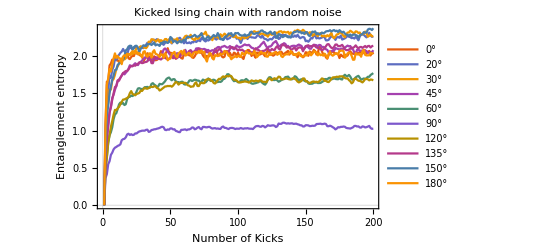

```mathematica
ListLinePlot[{Legended[nois0,"0°"],Legended[nois20,"20°"],Legended[nois30,"30°"],Legended[nois45,"45°"],Legended[nois60,"60°"],,Legended[nois90,"90°"],Legended[nois120,"120°"],Legended[nois135,"135°"],Legended[nois150,"150°"],Legended[nois180,"180°"]},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

```mathematica
Vnet[R]
```

Vnet[R]

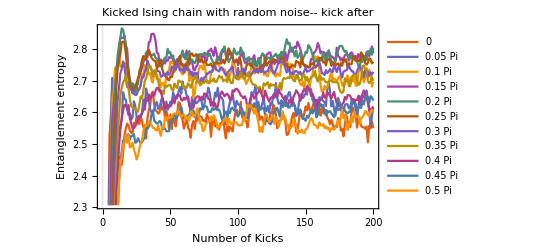

```mathematica
Simplify[%128]
```

```mathematica
ventropy[t_]:=√(a (1-ArcTan[t/b]/(t/b)))
```

```mathematica
FindFit[nois0,ventropy[t],{a,b},t]
```

{a→4.22716,b→1.37429}

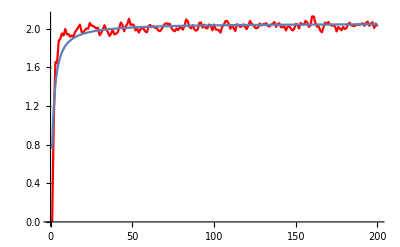

```mathematica
Show[ListLinePlot[nois0,PlotStyle->Red],Plot[ventropy[t]/.{a->4.227162749804977,b->1.3742895010661202},{t,1,200},PlotRange->All]]
```

```mathematica
FindFit[nois90,ventropy[t],{a,b},t]
```

{a→1.16364,b→3.72181}

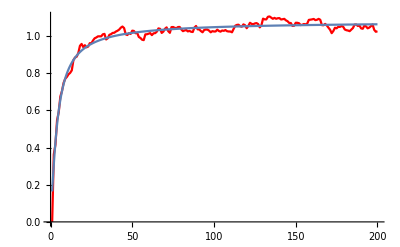

```mathematica
Show[ListLinePlot[nois90,PlotStyle->Red],Plot[ventropy[t]/.{a->1.1636394848739355,b->3.7218057391520176},{t,1,200},PlotRange->All]]
```

```mathematica
FindFit[nois105,ventropy[t],{a,b},t]
```

{a→1.59605,b→3.53565}

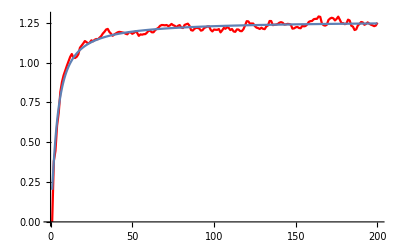

```mathematica
Show[ListLinePlot[nois105,PlotStyle->Red],Plot[ventropy[t]/.{a->1.5960539096721336,b->3.5356482305968515},{t,1,200},PlotRange->All]]
```

```mathematica
FindFit[nois120,ventropy[t],{a,b},t]
```

{a→2.93941,b→3.8359}

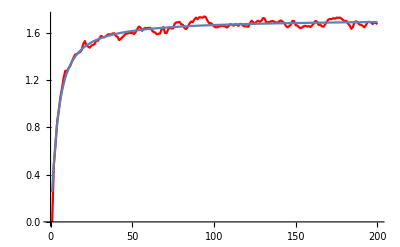

```mathematica
Show[ListLinePlot[nois120,PlotStyle->Red,PlotRange->All],Plot[ventropy[t]/.{a->2.9394140775486335,b->3.8358983659741015},{t,1,200},PlotRange->All]]
```

```mathematica
Manipulate[Show[ListLinePlot[nois90,PlotStyle->Red],Plot[ventropy[t]/.{a->q,b->w},{t,0,200},PlotRange->All]],{q,0,10},{w,1,100}]
```

ListLinePlot::lpn: nois90 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[nois90,PlotStyle→RGBColor[1, 0, 0]],].

```mathematica
bess[R_]:=Sqrt[a (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)])]
```

```mathematica
Function[R,a (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)])]
```

Function[R,a (R^2 BesselI[0,R/(2 Rd)] BesselK[0,R/(2 Rd)]-R^2 BesselI[1,R/(2 Rd)] BesselK[1,R/(2 Rd)])]

```mathematica
Manipulate[Plot[bess[r]/.{a->q,Rd->w},{r,0,900},PlotRange->All],{q,0,10},{w,1,10000}]
```

```mathematica
Manipulate[Show[ListLinePlot[nois0],Plot[0.0056 e Vnet[R*3.086*10^19]/.{ρ0->3 a ρMilkyway,Rc->b RcMilkyway,Σ0->c Subscript[Σ, MilkyWay],Rd-> d Subscript[Rd, MilkyWay]},{R,0,200},PlotRange->All],PlotRange->All],{a,0.1,4},{b,0.1,4},{c,0.1,4},{d,0.1,4},{e,0.1,4}]
```

ListLinePlot::lpn: nois0 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[nois0],,PlotRange→All].

```mathematica
FindFit[Drop[nois90,-170], a -d Exp[-e x],{a,d,e},x]
```

{a→0.965443,d→1.01861,e→0.189856}

```mathematica
Manipulate[Plot[1-a Exp[-b t],{t,0,100}],{a,0,10},{b,0,10}]
```

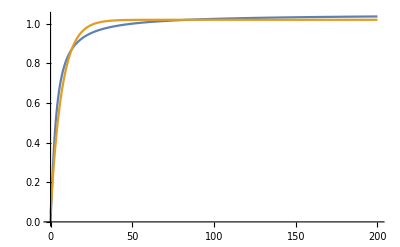

```mathematica
Plot[{ventropy[t]/.{a->1.1,b->3},a-d Exp[-e t]/.{a->1.0197446586864853,d->0.9785472096337658,e->0.14509008433389414}},{t,0,200},PlotRange->All]
```

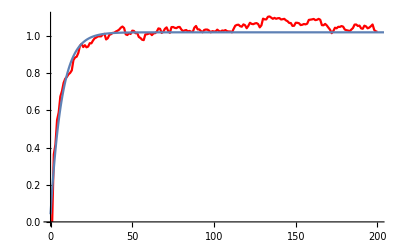

```mathematica
Show[ListLinePlot[Drop[nois90],PlotStyle->Red],Plot[a-d Exp[-e x]/.{a->1.0197446586864853,d->0.9785472096337658,e->0.14509008433389414},{x,0,2000},PlotRange->All]]
```

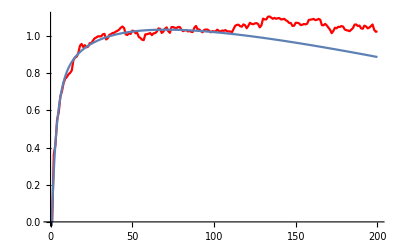

```mathematica
Show[ListLinePlot[Drop[nois90],PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->-0.21746387410412107,b->0.7069868369191148,c->-0.0008606242213454921,d->-0.6143446138754819,e->0.34660560292088294},{x,0,200},PlotRange->All]]
```

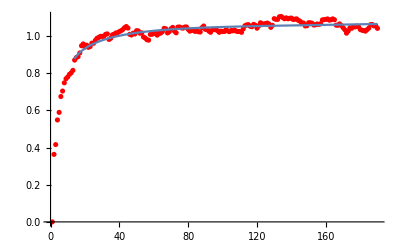

```mathematica
Show[ListPlot[Drop[nois90,-10],PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->-0.3311052887584087,b->0.8646400566710369,c->0.0034627589123955534,d->-0.6100069734032445,e->0.27072219931253116},{x,1,190}]]
```

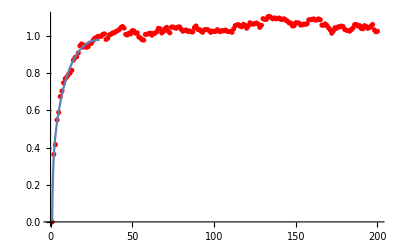

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->0.5534801177708996,b->-0.253046328553623,c->-0.04221626470528879,d->-2.579072302505343,e->2.3031720397360282},{x,1,30}]]
```

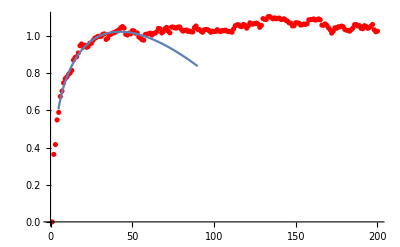

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->0.19915885623069984,b->0.1610559570980988,c->-0.019705430897474997,d->-0.8481544626434205,e->0.9412876721450883},{x,1,90}]]
```

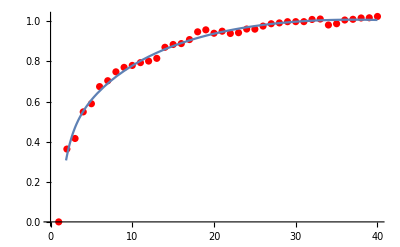

```mathematica
Show[ListPlot[Drop[nois90,-160],PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->0.31210417387548667,b->0.025982112242386838,c->-0.026407427183689405,d->-1.008437761199951,e->1.1915442625237795},{x,1,40}]]
```

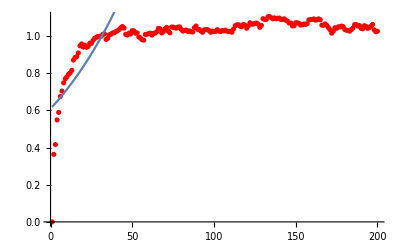

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[d Exp[-e x]/.{d->0.60836398069815,e->-0.015837128902372197},{x,1,40}]]
```

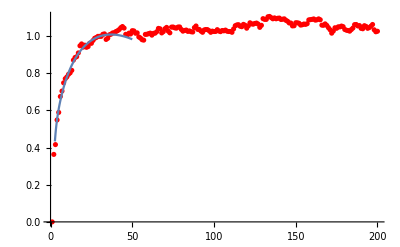

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-e x]/.{a->0.31210417387548667,b->0.025982112242386838,c->-0.026407427183689405,d->-1.008437761199951,e->1.1915442625237795},{x,1,50}]]
```

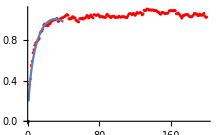

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c x+d Exp[-d x]/.{a->0.6956677983003448,b->-0.4356557774779859,c->-0.04748197849625604,d->-0.01634461738947615},{x,1,40}]]
```

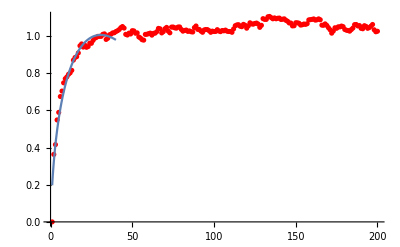

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c x/.{a->0.7201855916995139,b->-0.4743227806423396,c->-0.04884192720060195},{x,1,40}]]
```

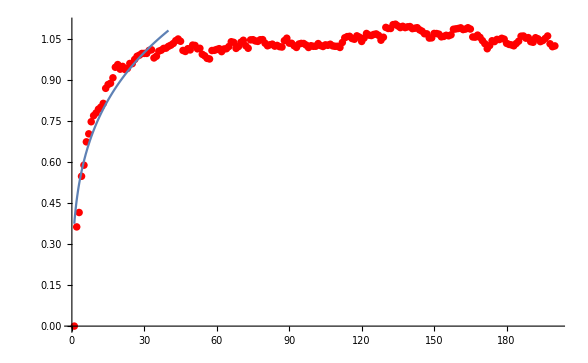

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)/.{a->-0.06864091668277866,b->0.4433543277598657},{x,1,40}],PlotRange->All]
```

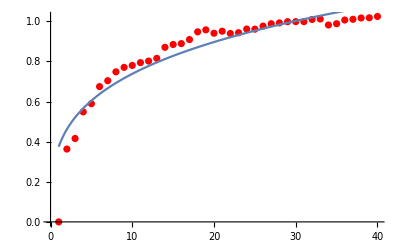

```mathematica
Show[ListPlot[Drop[nois90,-160],PlotStyle->Red],Plot[a √x+b x^(1/3)/.{a->-0.06864091668277812,b->0.4433543277598646,c->0.},{x,1,40}]]
```

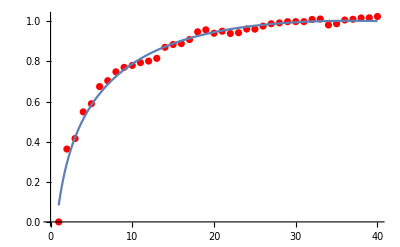

```mathematica
Show[ListPlot[Drop[nois90,-160],PlotStyle->Red],Plot[a √x+b x^(1/3)+c/.{a->-0.7074734864050769,b->1.9364162558934312,c->-1.1467207323230948},{x,1,40}]]
```

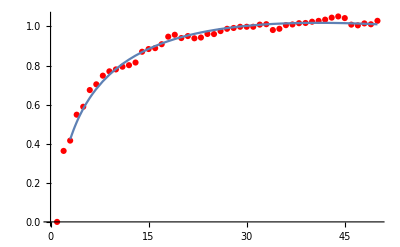

```mathematica
Show[ListPlot[Drop[nois90,-150],PlotStyle->Red],Plot[a √x+b x^(1/3)+c/.{a->-0.6536096555864669,b->1.8197072346100223,c->-1.0713892357108552},{x,1,50}]]
```

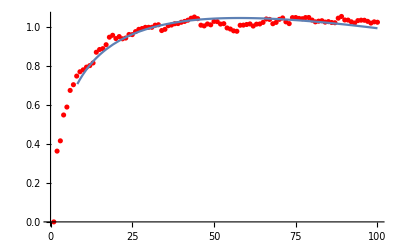

```mathematica
Show[ListPlot[Drop[nois90,-100],PlotStyle->Red],Plot[a √x+b x^(1/3)+c/.{a->-0.4724485636374186,b->1.3934480364247075,c->-0.749959945109806},{x,1,100}]]
```

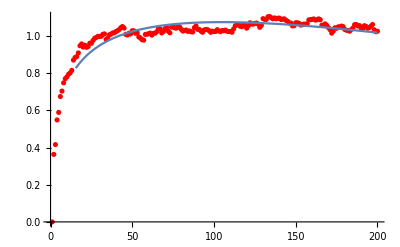

```mathematica
Show[ListPlot[nois90,PlotStyle->Red],Plot[a √x+b x^(1/3)+c/.{a->-0.26470059297313414,b->0.8620395872247836,c->-0.27986047631915323},{x,1,200}]]
```

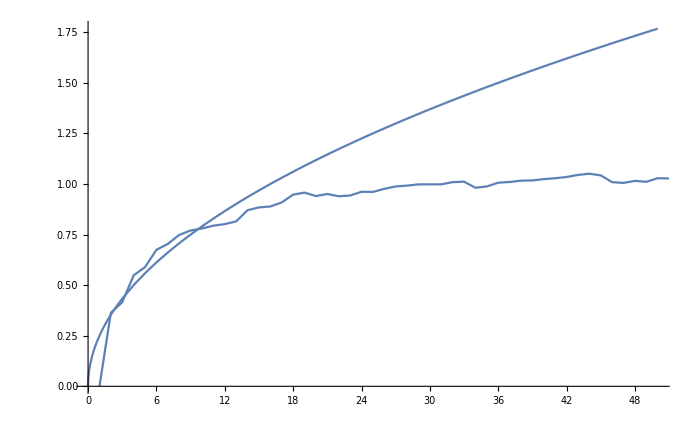

```mathematica
Show[Plot[0.25Sqrt[x],{x,0,50}],ListLinePlot[nois90]]
```

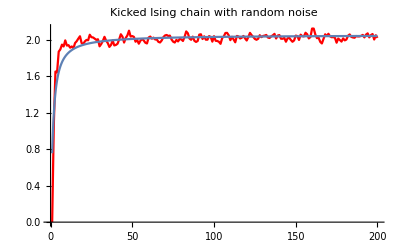

```mathematica
Show[%44,PlotLegends->{ "0°","20°","30°","45°","60°","90°","120°","135°","150°","180°"},FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise],LabelStyle->{FontFamily->"TeX Gyre Pagella",12,GrayLevel[0]}]
```

#### findfit

```mathematica
FindFit[Drop[nois0,{1,60}],0*x+c,c,x]
```

{c→2.02739}

```mathematica
FindFit[Drop[nois20,{1,60}],0*x+c,c,x]
```

{c→2.23893}

```mathematica
FindFit[Drop[nois30,{1,60}],0*x+c,c,x]
```

{c→2.28506}

```mathematica
FindFit[Drop[nois45,{1,60}],0*x+c,c,x]
```

{c→2.10772}

```mathematica
FindFit[Drop[nois60,{1,60}],0*x+c,c,x]
```

{c→1.6792}

```mathematica
FindFit[Drop[nois90,{1,60}],0*x+c,c,x]
```

{c→1.05059}

```mathematica
FindFit[Drop[nois135,{1,60}],0*x+c,c,x]
```

{c→2.09153}

```mathematica
FindFit[Drop[nois180,{1,60}],0*x+c,c,x]
```

{c→2.0209}

```mathematica
FindFit[Drop[nois150,{1,60}],0*x+c,c,x]
```

{c→2.29094}

```mathematica
FindFit[Drop[nois75,{1,60}],0*x+c,c,x]
```

{c→1.25383}

```mathematica
FindFit[Drop[nois105,{1,60}],0*x+c,c,x]
```

{c→1.23215}

```mathematica
FindFit[Drop[nois120,{1,60}],0*x+c,c,x]
```

{c→1.67177}

```mathematica
fitvals={{0,2.0273925657142855},{20,2.2389346833571424},{30,2.285056863642857},{45,2.1077225889999998},{60,1.6792030354999998},{75,1.2538272654285714},{90,1.0505887500714282},{105,1.232146851142857},{120,1.671773177285714},{135,2.0915349040714286},{150,2.290936501071428},{180,2.020903649785714}}
```

{{0,2.02739},{20,2.23893},{30,2.28506},{45,2.10772},{60,1.6792},{75,1.25383},{90,1.05059},{105,1.23215},{120,1.67177},{135,2.09153},{150,2.29094},{180,2.0209}}

```mathematica
fitvals[[1]][[2]]
```

2.02739

```mathematica
fitvals=Table[{fitvals[[n]][[1]]Pi/180,fitvals[[n]][[2]]},{n,1,Dimensions[fitvals][[1]]}]
```

{{0,2.02739},{π/9,2.23893},{π/6,2.28506},{π/4,2.10772},{π/3,1.6792},{(5 π)/12,1.25383},{π/2,1.05059},{(7 π)/12,1.23215},{(2 π)/3,1.67177},{(3 π)/4,2.09153},{(5 π)/6,2.29094},{π,2.0209}}

```mathematica
Cos[Pi]
```

-1

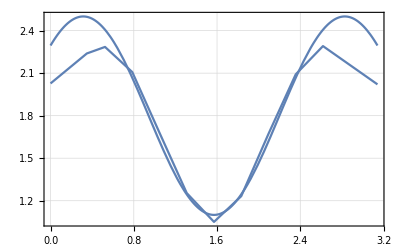

```mathematica
Show[ListLinePlot[fitvals,PlotTheme->"Detailed"],Plot[0.7Cos[2.5x-Pi/4]+1.8,{x,0,Pi}],PlotRange->All]
```

```mathematica
Show[%134,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of four consecutive spins],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]}]
```

Show::gcomb: Could not combine the graphics objects in Show[«1»].

Show[{0.,1.61965834084848748,2.7155566656555532,2.59562272561507834,2.55435601869183993,2.28846310495979211,2.11998346050359654,2.23894592890415556,2.32012679257037524,2.35475584414715744,2.35027403524253709,2.31889173569832119,2.32136626617654462,2.28668822738095656,2.29698574173855619,2.31551708453821492,2.30801980989250799,2.30806700149094146,2.3089330022101322,2.32145310929484783,2.35097719774355252,2.33783386480616207,2.29585482838422861,2.29801924439832206,2.30708729181298677,2.31666157587319077,2.32884069957483009,2.32171217586335787,2.31272823642249614,2.30305310445776756,2.31846697983669303,2.31232748336463256,2.31270203124649276,2.34866956090644896,2.33413719835257494,2.28376894604125802,2.29962530910976559,2.32319174415140495,2.32755868174234726,2.33777204500536806,2.31336902734482486,2.34303539911006498,2.33758435437281342,2.33099648333501852,2.29990752497241857,2.28757043672448557,2.32006104947998626,2.33216918701192633,2.32459900142525777,2.30756214235114543,2.30793801265143017,2.30330227474143667,2.30167727151801627,2.3104010520309628,2.2803023029039684,2.28121658562151231,2.31593334889563041,2.32799484335090989,2.34166468164085861,2.33874576968312553,2.27142169481856282,2.2787277716998906,2.32223266011482288,2.34437401934110845,2.33090682069918431,2.33001648866371625,2.3167638994810793,2.30024071667942431,2.33816187997535341,2.33083990738621871,2.29365846811585517,2.29734803348854344,2.29268664221751628,2.28311946476624295,2.28865350218466634,2.32959225051634888,2.34335144521396499,2.33710872319358165,2.3406980428317361,2.32891786494590392,2.3101467989129918,2.31904655862464804,2.33357946734210575,2.34294629063503157,2.30038856897737798,2.29206451699637004,2.31882665634383756,2.31628636666281418,2.3162592806368747,2.2991935449486971,2.30031646585781679,2.29095556890478713,2.33898411420582786,2.34296754973221511,2.31665741321180718,2.33236123128481587,2.3093716497148451,2.31477732179512019,2.32721108726355963,2.33719232913081543,2.33998411475945689,2.33155726440339572,2.31782566717066674,2.32733277784503434,2.32047884044245478,2.32733541641320585,2.30711078869458408,2.33935576167205905,2.34703991280261715,2.32640711933353694,2.30605794923133933,2.29143406728823784,2.31056687214221279,2.33946480840110471,2.34076612192380296,2.29838728025516303,2.30841677102518483,2.330552669697457,2.31316363925505542,2.29665351671456142,2.31989069548817817,2.31783792470368288,2.31847011864395736,2.33261726977989925,2.3338192454452571,2.31382900744979692,2.34092069083650811,2.32495232857335443,2.30006733440054356,2.32295868619192802,2.31503316826957528,2.28363456375132756,2.32258121797638939,2.33183528967305254,2.30683815413868176,2.31915770956612688,2.32328960678551066,2.33144724196777409,2.34585601599386351,2.30888969228152963,2.31290023507713638,2.33176511498660366,2.32408324895837737,2.33147978948586232,2.31582605930601204,2.29299307658106377,2.33244560153156888,2.3302944728879611,2.32782068501347927,2.37161622596856558,2.34840623236946433,2.31722544053443702,2.32623705469953679,2.33864907370269348,2.36122561795907204,2.32949272365615867,2.29891941663942045,2.27911855062250623,2.30337614590240625,2.33537501403827852,2.31423246537997818,2.31831198425817942,2.30967281823016712,2.30523601526102828,2.3009201410762663,2.32066264831094138,2.33089334935630133,2.30367977817141378,2.30137802541796699,2.31918528380667732,2.33751803451612528,2.35034335121490035,2.35789684059360827,2.33539432877920339,2.2783493241972721,2.30988960237970398,2.32620928151455475,2.32231511942725932,2.35769814266976852,2.34358936193542533,2.31972934283405996,2.28906962437783124,2.28321745951117938,2.31679164467832299,2.31970381966994355,2.32092121279215879,2.29087827931098609,2.27809541081066813,2.32913720040980321,2.3412733137579842,2.34307306512570035,2.3123820738431955,2.30294651133748562,2.29765994560440223,2.3245807563714318,2.34570311358526418,2.35182004823728441,2.31911843909215421,2.32620239569433984,2.30592845569046379,2.7229125282426518×10^-14,1.62001589538688373,2.70186813924089497,2.60916926235772584,2.54910679159604925,2.31953118985711493,2.18033945140912211,2.33057659937228978,2.38083021986042898,2.38695654800735735,2.39621741440748748,2.38537322204749547,2.42610649129788047,2.43783454058619942,2.38650347094764381,2.39733104572893607,2.39765158322008354,2.39964658101023609,2.41326415397147986,2.4233556966196983,2.42928471098692755,2.4247696507736376,2.3911729002212021,2.3978202515890823,2.42457975627128741,2.44313359542230701,2.42016273710847285,2.43880636470889867,2.40245753453445365,2.39295240541451726,2.41998504137321691,2.43763987082396838,2.42655596740255941,2.37911390126758171,2.35572214854928541,2.40679799947236139,2.43072847940899628,2.42640082104897381,2.41442196487134808,2.43383948132057926,2.42436191659653311,2.43904391543867583,2.42110877190043494,2.40341892442064209,2.40967580406907977,2.40977817450017096,2.40058437412539227,2.41033362514437544,2.43161861020901515,2.41938748382821256,2.39424304717786907,2.4062654148573599,2.39702993694280098,2.40726084465596024,2.38242220709532804,2.42067968965580027,2.43702346209844123,2.40653887211456086,2.44097690117141397,2.41461643403148285,2.39769146854791293,2.4163675874446513,2.40629749275216875,2.42870787318587711,2.40636758756134928,2.3804925752161652,2.38712959199315655,2.39648419070655727,2.41081086233002617,2.40240277537741953,2.38023680188906761,2.37549989130140515,2.41390149802803,2.41096709229201478,2.40463942426467359,2.39695800785415525,2.41484106557489531,2.39415750800753058,2.40239887467958413,2.41419858437685964,2.41859830149271282,2.42066521025393566,2.40287530132787186,2.40900090046749771,2.38977743628010719,2.39054594548454835,2.40387703172585132,2.3912252931868152,2.4076929735645991,2.41429250997429135,2.39525942017487381,2.39151973261038497,2.4049883095597524,2.40371728341698132,2.39599420722617928,2.40155134506040646,2.41532986723450316,2.40753517490750957,2.39917595348666879,2.41003971162286002,2.41837327716185291,2.40972098185642425,2.39190007982696118,2.4035522385703989,2.41023454110648672,2.4128653411162917,2.40629187046475979,2.41277548933151564,2.44045552380808983,2.40896150958529187,2.39647273237489911,2.39176620968394182,2.39511665485897574,2.39219467923406182,2.42057193769056056,2.40587683004179542,2.39096822059060976,2.3915042669514337,2.37721862840121823,2.40562752122752732,2.43461996098228939,2.42413048149789212,2.42606986040251638,2.43033180143697436,2.37652335459572317,2.39878478254380667,2.41011514137493865,2.40018650242941689,2.39179613479029563,2.38248127215638172,2.40698374929631731,2.41583475151528315,2.42601256714497149,2.41895395093153276,2.4094285436457934,2.40100667078020136,2.38578695485723991,2.37833152188020103,2.40329526148784822,2.42353785218811213,2.40496364286845843,2.39992589914547283,2.41981588357936817,2.40560791550681996,2.38747801507882462,2.42540342026246014,2.4319881421488927,2.44287800226858254,2.41399680830995278,2.39558266640112638,2.38662183150635698,2.38926547972243819,2.42269075155209057,2.41699307447398226,2.39054311627454119,2.40077943543924643,2.387400945676871,2.40591701509698774,2.40561935430957741,2.39298795427996458,2.39932521694515977,2.41283662560158874,2.43045905788199024,2.41659443551712005,2.39935626475621344,2.41635206322234897,2.41926757267457804,2.42092719299804315,2.40120927061310407,2.37311477824662331,2.39523924082221873,2.44254472309778459,2.43861264038093362,2.39690461396185262,2.39187137200419775,2.38087707046294295,2.39941933349095882,2.41336919305833186,2.40263846397591596,2.36961676142232935,2.37984363677336663,2.4013565606890146,2.38983447252052139,2.41377534469800059,2.41562509173937157,2.41365918805529978,2.42952664227353354,2.40978067568450749,2.36615449592671645,2.38753446721995921,2.42093020875896237,2.43370616097902381,2.46425240423872793,2.43335482085398347,2.39859477626743267,2.37893360836103884,2.37342307065096758,2.41969514945319375,2.44176668967073818,2.41743208594012282,-9.61027951144475588×10^-16,1.57053526320607007,2.58686588002849005,2.56099224971088058,2.55964506501914846,2.46061025025943181,2.40448850873091979,2.51332991158268193,2.51983494656327345,2.52530008593062272,2.55693421190253867,2.57256111645321806,2.56924564469033356,2.54855556801436034,2.53056403862823132,2.53549779528482233,2.55351204742445104,2.5564281436251397,2.53338889244384546,2.5607925688591231,2.56843232579273906,2.56787589693722396,2.55148048929804316,2.53373262006165145,2.56423661750272292,2.58620207639781974,2.58400011271817665,2.57342724843093018,2.54943800823365407,2.55475284388293078,2.56456476078065254,2.57305173972320755,2.56038549823348882,2.54379718534016197,2.55456386608819885,2.55544667213731147,2.56371170711271912,2.56924259866565929,2.56248440609317063,2.52915064368345188,2.53955460635352992,2.57599477781444453,2.55873550946513184,2.53927600372875073,2.55747864511820389,2.58627256669657291,2.56673600993626172,2.54820051734957032,2.53590433778369251,2.51982474761812325,2.53910530834290871,2.57734305078566806,2.57085275269061553,2.55458624955580893,2.54459029423382166,2.54147685661171607,2.54564193907537417,2.55874707751028341,2.56196501915259578,2.57651976195884114,2.5332139459787002,2.53535478661770863,2.56028449353532484,2.56080390057506202,2.55537837825117231,2.54920938416228138,2.56168475005671592,2.56993489773834316,2.58027035429971274,2.55236323152424793,2.53089658741476997,2.54161336285216022,2.54328255489320432,2.5493706238696161,2.56705150239147706,2.57623105193961655,2.56379524038104201,2.55465398147204104,2.53295949095826778,2.519810921238407,2.55980479055792465,2.57990213230562304,2.57533212893762409,2.56641793844967348,2.54100998177664472,2.54310573713255872,2.53189540793465051,2.5501081764983442,2.57565378971307535,2.58031112046544608,2.55532341557850629,2.59362404060436225,2.59986437051875807,2.54993508981798955,2.55413064711976778,2.54761443582859171,2.54510420225645717,2.5600450601413316,2.56451775613497413,2.55112083644893861,2.51176630906934095,2.53122597114406478,2.57683098633047969,2.58544988290143474,2.5481530071864209,2.54942330422118513,2.53939363353248027,2.54749405963215603,2.5741717230397172,2.55843807628786202,2.55888950962593942,2.54358423321928973,2.56502780806777819,2.55236025097489216,2.52840308887718246,2.54216819768858038,2.54790029650320271,2.57263962633283017,2.5537298351149289,2.54712405165725775,2.52875249911867828,2.55636354261571563,2.57043387913829413,2.55786361370774973,2.5610493538877761,2.53487093518426709,2.5545933795031055,2.57045029623342503,2.55079755387485907,2.54907103283416614,2.59078753258369066,2.56987796291470971,2.53049976665123966,2.51534644993548806,2.52299477692375662,2.52745069683682688,2.54502464578915433,2.55287502697799962,2.55877463981926168,2.56739324533282076,2.56628726840355981,2.56983878287015699,2.57306464775391008,2.54534493761344161,2.54802986731499281,2.55949350838840184,2.52933382661674289,2.54487079976145481,2.57042215881288794,2.55800742176038964,2.55660969974563779,2.54804937641181484,2.56837230926414017,2.57337247443157891,2.5727204016265226,2.57249175147177756,2.55747773710887971,2.55956172877919252,2.57022641203562019,2.5599270783910395,2.56555492481408187,2.55342399428555256,2.54966858730889756,2.54764295785049733,2.54465245166942466,2.54326224834397818,2.54686028827154232,2.5554770110447298,2.55628736526023381,2.54973878077054295,2.55014232307223221,2.55879590841714055,2.58890488467613578,2.56733728844245146,2.54578821836815195,2.56173352998311588,2.58530193512645434,2.58123952953221325,2.56008006270587174,2.55968947318576712,2.5350287445231614,2.54836508580861265,2.55441074838585358,2.53923289233979377,2.53160653753538156,2.52186126129261679,2.54729074009866174,2.55751473635575133,2.55244487299802936,2.53847036813330007,2.53862227007226826,2.53558339694569179,2.54850755071200963,2.5382598942997876,2.53219063837494085,2.5412337745514515,2.53388264472710123,2.567186931366082,2.58684017656398524,2.54739172294241367,1.12119927633521836×10^-15,1.52072305506949124,2.44791274979923212,2.52133960587354755,2.53479247089194226,2.54833125921453085,2.51585773645847999,2.57479332645801273,2.61269075108465199,2.6464594997178561,2.65022320007994594,2.63324534981886815,2.6163261426350557,2.62584411705817011,2.64188851779283018,2.64248357990231897,2.64779538893296218,2.66623729917698382,2.65172096879482222,2.64024109335707413,2.65414178704947057,2.67807791906647985,2.66462231803661354,2.63753479131962099,2.64808012767483403,2.66412495488252299,2.65695389447995423,2.66536336959439479,2.64118262846039453,2.63605995997032405,2.66316477025163501,2.65642414045403585,2.66496522702478655,2.66799809674214616,2.67816328681953619,2.65998290346587574,2.67675898706227278,2.68604055568727462,2.66409398129645858,2.68128276295222934,2.67133054842162077,2.64803321387467605,2.66802168716089483,2.67831724616682232,2.66124367953490593,2.62932771182529379,2.62048058419281249,2.62888950297626733,2.6380111424308117,2.65308609946937279,2.66199360681572816,2.67799198594888255,2.65930953899825706,2.6453144634763972,2.64237214095912387,2.64125062819506251,2.6503122639570682,2.67003214904612651,2.66067892857299526,2.63845250090769756,2.64494574490057177,2.66000219314133313,2.6523759075569795,2.64834254747484499,2.65985913557624665,2.67007442222171454,2.6687096235788621,2.65225253333030109,2.66397241067228574,2.65439771141572534,2.64590758818359451,2.63856232470232488,2.63403858689297854,2.64135499667574569,2.65834584281947528,2.66774345037790495,2.64789744567591567,2.64996469287802716,2.65038775728411213,2.64336078591500145,2.66989678876736081,2.67034910386133939,2.64838621232147853,2.63791944895650721,2.63137684391420734,2.64845201381507867,2.65961610486768185,2.66003153621686472,2.6649922432029971,2.65744295866795754,2.6504204402383662,2.63296331768037994,2.6241186478441052,2.646323875716452,2.64270466648748137,2.6469054824243452,2.67617823306582547,2.6741544694588324,2.65867766886019297,2.64167015527299132,2.65686281826777293,2.65861195717905074,2.62614074886507298,2.64296916645002922,2.64318303081611328,2.65284846448122424,2.66179557666511224,2.64453196180370664,2.65809883009396053,2.66222425664810647,2.67780070945258775,2.6637847312839229,2.63759988825935432,2.63001956666173431,2.62209623165896089,2.66446666489278172,2.67155765972286297,2.64641291093963682,2.64600961532241374,2.62820175730374883,2.63253608278018181,2.64240237388033306,2.63457344136508986,2.6443927091650794,2.67407172735742149,2.66856414270712028,2.65022628465386401,2.6474395389603087,2.65751318328636943,2.67634443883683515,2.64690990346546418,2.65222439537054822,2.66655132849573029,2.66563158450836246,2.64864551123154346,2.64772465104977428,2.65851474104546925,2.65814537432643938,2.64676161036624347,2.64041932656191891,2.65047428451112799,2.66747752426224682,2.67963325701861521,2.64491724909268466,2.64558820454741284,2.66035445172574647,2.65110024837981584,2.640992818562379,2.64685778685696738,2.66752855482383078,2.6625089299811604,2.65881781632972247,2.64437154077401004,2.65303438206371833,2.67012424806362514,2.67092360733219447,2.65889054366346889,2.62515008513321524,2.63623504438045453,2.64973099316623983,2.62968852594536307,2.63129356386957047,2.65414560157807378,2.65821944962321544,2.6597344885215839,2.66476371168261483,2.66468835306234597,2.65983982110078365,2.643897176799896,2.65012626402387763,2.67590076909231556,2.6653520629782923,2.63985495266225234,2.64379858432404813,2.63027676657465426,2.62511479368184464,2.63399174821521154,2.64375023091343753,2.63790649748364681,2.65091431925833332,2.62518590727873713,2.6277216880737222,2.62101630367158123,2.65828297547173609,2.66540794692733396,2.66151491819575892,2.65704082750630288,2.66260029555155198,2.65001602510373768,2.63661212124049049,2.6250400853415421,2.62644881162458699,2.63850902152743139,2.65608187543521579,2.62843145431173486,2.64192695253543253,2.64745667587528999,2.63877845466057037,2.655186442665189,2.65786194669794496,4.80513975572237695×10^-16,1.48421712734667954,2.32952736541124406,2.43365735414109929,2.49404226276132635,2.61202656128674571,2.6075545708993042,2.64785358230357826,2.68925033893248022,2.70784547382267693,2.71101289749890251,2.70119222781040769,2.68745855260842292,2.67142344546000965,2.67785331224716483,2.68106063928987881,2.68589741072835553,2.67970421003496506,2.68791871065474863,2.71633946216973365,2.73820252187063362,2.70904587075653192,2.71967672483840683,2.70607032632897937,2.71366364195280907,2.69877336582437444,2.69521055063883352,2.71361053967126109,2.70553962301270934,2.7048414610215179,2.70045960533476004,2.70109597307711802,2.69824478172775661,2.69248782897966255,2.70530819375820242,2.68730447685875706,2.67456025575695877,2.68633912038597567,2.7018146443962463,2.69991905928647658,2.69960389699276249,2.70127830185933915,2.68457469191004394,2.70595794923300437,2.72395142386068256,2.71912586858343897,2.71580230657402488,2.7088888463849865,2.69973664914548284,2.69359698754062915,2.70163270999236582,2.7050631365976936,2.70804781796402949,2.68769508090873188,2.69226152960972787,2.6887297251733413,2.68421561040606482,2.71284680946042611,2.71143278953004607,2.69228845851115306,2.70305929448487525,2.71696854028466461,2.69984284447006528,2.69004820679801782,2.70576981685716334,2.69213011918479195,2.70402647047431088,2.72031741544715855,2.71659942039549529,2.71349376586659652,2.70789739212176173,2.69234279081845696,2.69093429115808425,2.70345034035728249,2.70622378376287598,2.66286441038320243,2.66673135262766481,2.67291207509533413,2.66399568513207274,2.65487855658940131,2.6722920077106882,2.69664646952811271,2.69360268025857819,2.69551353667389293,2.68544534723197703,2.67164044355294994,2.67700489594426916,2.67670588211746985,2.68249885577999203,2.70848340959665457,2.69691838863713995,2.67674126905895982,2.66995174855521977,2.69905315986330718,2.72148898064664335,2.69029527144863367,2.68177807881541108,2.68045037128758601,2.68431149083381104,2.68947053828690086,2.69576626385242424,2.70249506525898653,2.7050013037234466,2.70265083834019526,2.71834813151759658,2.7140948313301223,2.71596131669675334,2.69025187233816565,2.69263994005823992,2.68953726739004395,2.69749424194013399,2.70366581187993527,2.70325096472981974,2.69302934142978945,2.68982886838260615,2.69296596519975084,2.69345233384975691,2.68728356143195102,2.67894815119939223,2.69947696172820084,2.69977619174318795,2.71643789377715983,2.71151147287885674,2.7068456744392968,2.71389125646037543,2.71336167052744548,2.70869990473672084,2.70773401712038497,2.68849900425819977,2.68452763805394268,2.68132545693108471,2.693699527976396,2.68291408597349701,2.70039625855613208,2.70055408337151226,2.69396852836255851,2.71312680580221954,2.71706748688156941,2.72137811455763545,2.71951424128585284,2.70849853860278023,2.70560713355700067,2.69054153074441693,2.69803068444607241,2.72144711685321505,2.73043808676888178,2.70071900507896645,2.68432833691456496,2.6711034128219544,2.68283583033796447,2.68698700307605876,2.6894208456191282,2.69053041291162476,2.69519338088241467,2.69237813089798816,2.70895937050040203,2.69166300674343217,2.6778517223692293,2.65853013522871606,2.66373229327581962,2.68538770294799045,2.69090593677664014,2.68631792597474739,2.7063498213773558,2.7127370543957543,2.69053323492993801,2.6794747718667864,2.6891045000003051,2.68265923446148724,2.67020498532339135,2.67268685424269537,2.68190082583319667,2.69224091906378948,2.67932037048844896,2.67144485812730625,2.67886670633239543,2.69860084655924171,2.68817530850395725,2.71549977276533028,2.72438050987013902,2.68762648580501162,2.67821430888227008,2.68830330439381315,2.70992824849250624,2.69168425493743513,2.67991816442227027,2.69970239762661013,2.72483816416499014,2.7356831145347047,2.71330421061044014,2.70538402870150163,2.69696392073288882,2.69956904071866122,2.69342504109735081,2.67099150820878473,2.6848617505613821,2.70023294078066156,2.69591264581651213,2.71391017479475405,2.70732562752057593,3.20342650381491813×10^-16,1.44096604406741125,2.24025123803340476,2.38816539152856677,2.4700063913729724,2.60265313451128577,2.6328559458675489,2.67545708064929233,2.71527852278894821,2.71895846190095814,2.69991729471989306,2.65486617235055844,2.66268348214087647,2.69379653098331362,2.69323632723754569,2.67459023956344622,2.68296103012219422,2.70314017198509271,2.72322662648625835,2.73207736563252013,2.74212540198615873,2.71027019268401981,2.70432667176385966,2.7364934023380858,2.72610844004198105,2.7011457311065934,2.69362160302045339,2.70403941034425266,2.709438352689165,2.7061589993192583,2.70254597034001831,2.71123454826338506,2.72142143947420578,2.71896804477628429,2.71287320319809355,2.7065392307944105,2.72416347403246739,2.70548663965082481,2.68668515031914801,2.68984927479000735,2.70313192105337397,2.69886376619580259,2.715022095240895,2.69877727118143085,2.70282621026925973,2.73566730513964185,2.73421383919742267,2.70990010300860229,2.68816479764250316,2.70393143784999879,2.71916540093753145,2.70519917085280826,2.70788852103619471,2.72103011544620133,2.73157730258774301,2.7353706502996249,2.71929906411914857,2.72364871883579163,2.73021982910296135,2.71949887565844684,2.71438929252949501,2.7036715476149622,2.70661450407334137,2.72545735491347507,2.72102179320822435,2.70480683597493998,2.71509395623928818,2.72389895235687618,2.73670573932301586,2.73914546493790079,2.72248259330432774,2.72713201997280041,2.74249517808498267,2.73119010125975148,2.71676257782143127,2.69748898539084037,2.70617324949320937,2.72426578479594195,2.73466320156261844,2.72902356940613178,2.74227777835013287,2.72290925598392697,2.71570381830128094,2.70956647469951717,2.73119256018660295,2.71148059721620749,2.70902930794849706,2.70960251594277457,2.72014409926742484,2.71283489131865174,2.71671628679819488,2.69986731946781688,2.69744933940858767,2.71186015655839174,2.71069402822426353,2.719691943919615,2.69128824733398941,2.70891180569711398,2.73648203933330558,2.73154315586493945,2.71772163323303584,2.69898878435776579,2.69689985711600722,2.70824111347903829,2.72146927264871419,2.71410078069071759,2.71336805605630804,2.73988652462704607,2.72280009106837895,2.710495936802503,2.71955343861331356,2.70784013865253437,2.71804421581768718,2.73773832292826702,2.72981722060534393,2.72835016801591523,2.70562470333097593,2.70343422885105333,2.70268932114576677,2.72095568143404787,2.73402415863105386,2.73746509646890956,2.73110625006007979,2.72107905569375008,2.71550031909755418,2.71602356731160288,2.71807507171785456,2.71856390498045908,2.7329478786180692,2.72308890925902869,2.70181096066670357,2.72409292451996254,2.72958508824754897,2.71860203202463779,2.7156053262225015,2.72628842126341908,2.73113949010389945,2.7348576793132704,2.71259409572607657,2.69246605909931036,2.6969490644354992,2.72100445510563915,2.73159908396721241,2.731531154581885,2.71449074900283005,2.70804377234252192,2.70671937845845489,2.7118170213805346,2.70912920863223006,2.70713576437696046,2.70428471577395957,2.71360129828609464,2.71765385429691753,2.70870896660144256,2.70034153393269527,2.71637710871501792,2.7115189617685771,2.71620844469972855,2.70676389262000239,2.72431397061891589,2.73258163829186085,2.71083469221664153,2.71684239335939948,2.73826265153318138,2.73403182863014216,2.71492770894438928,2.71399904634494149,2.72039950390985608,2.73090216182920287,2.74228805487424765,2.74136355502330487,2.72565639576223573,2.71645359509662576,2.70192432302342578,2.70207321365179354,2.7164103457435318,2.71578550378674066,2.71816320535422307,2.72221479350406392,2.71745059916697462,2.69321393087091465,2.6949856040697906,2.72678711394552975,2.74438361882533677,2.71847717711028691,2.70631659540389169,2.704820716957824,2.71012144838405744,2.69212363353495343,2.67613103117702567,2.68857548102726751,2.69841776028812763,2.70639589654963952,2.71392890645416518,2.7112149930406142,2.70761470542408,2.7147880558064843,2.70868177714724512,2.69897400896434014,2.69958428170873432,-3.20342650381491813×10^-16,1.37695806849996738,2.11516103418941315,2.32683769883634817,2.47063296219915207,2.62074350286012336,2.6609318157290387,2.69803475328247222,2.74280496149411812,2.74560647802842839,2.72794577878062938,2.70972682503775886,2.69350572404641264,2.71160832160507992,2.70405002425519925,2.69626620303071762,2.69785425798878098,2.69561722518433777,2.70473611933235958,2.72489764563573811,2.73982850801564393,2.71528388808963106,2.70536105389268666,2.71942971764483588,2.70132101244089329,2.72395898164701267,2.73888169127719827,2.70940652229381973,2.70085926117467823,2.72303241036330945,2.72206336808803062,2.71669206175791977,2.709639962403386,2.71262834054536528,2.7225148592813686,2.73562213074791716,2.74744022533698384,2.71363565020104902,2.69984876145789876,2.69692036325558648,2.70266322924925406,2.69060626471601116,2.70967365493721424,2.70275517300175316,2.69461509756329587,2.70767361543833607,2.7104035901967718,2.72720396726056258,2.7612256114272955,2.75916327731110433,2.72861220475447919,2.70082040561785775,2.70616496074022139,2.71836490771398909,2.72385319144366633,2.72491513275042996,2.71978756391470222,2.72364412666651923,2.72692227100934481,2.73183081036890396,2.73962214025380391,2.72191215722701818,2.72877404284743585,2.71451752570037419,2.72145434778499773,2.71634484245358099,2.72681576458377029,2.72679394850051216,2.73253307082105401,2.73975112701545642,2.7318406852011381,2.73617281411539892,2.7309899330956271,2.72680324133189789,2.71821612837435334,2.71076589631517306,2.72328708044909451,2.72135356510614646,2.7181181854275116,2.71258793135545995,2.72646448249124696,2.72741265984262293,2.72341559159600966,2.72682777333442061,2.73463609195859236,2.71996173427706012,2.71648793232956809,2.73688942611259112,2.71401542535002349,2.71072515853740637,2.72336470151019583,2.70320679690725951,2.69497237171469228,2.71529718448852453,2.71057297840165123,2.69232035731160035,2.69267004299316604,2.70442303070662593,2.70113793783341372,2.70365006818321607,2.71646250041069992,2.69693972020643313,2.70093200249862386,2.71870182371659652,2.72964449708470935,2.72519674167594683,2.71445551412626962,2.72597263320671557,2.73691137330424228,2.71748815588652581,2.72055333839890556,2.73372874272884392,2.73310088625035341,2.74820788617190637,2.75446286903609705,2.727338918317745,2.73830804281617279,2.73810667740680458,2.74078453383677934,2.75412148926547529,2.76091385969898839,2.72557331348581622,2.727871312743118,2.7512414006366015,2.73429359157538121,2.70807168035406498,2.68089827022586258,2.71401898532225339,2.72262527009618349,2.74196986625798056,2.74042777503900625,2.73198206093799501,2.71640176893863616,2.70389191735837953,2.71813999049943034,2.72872059284820212,2.7470241353490219,2.72991060609950598,2.72601918090076811,2.7372712480054302,2.7198419090077719,2.72155629039564495,2.73811865274780297,2.71911438564749863,2.72223704033321656,2.73034148826577816,2.72045931073403224,2.72565171722586941,2.72295474930112702,2.71953709352797812,2.70624691554669461,2.70467750156882403,2.69988207534456315,2.70007565891801926,2.71246117127112418,2.7305132573599713,2.72404813928649814,2.72221356973895512,2.73238603999821539,2.73991223298925091,2.73963498483012824,2.72766458931617795,2.72899534615823702,2.72217287239744277,2.72685852242083415,2.73226297256783468,2.7272168855708534,2.70996994530039048,2.71140341764322201,2.71275320015937949,2.72692586377296742,2.73498986553173706,2.71847530515645008,2.70282193906119206,2.71574680406323044,2.72307337115266401,2.72274912596428464,2.72882581731238361,2.73401529545669852,2.7385323589110433,2.72817833199152782,2.7202426681909917,2.72767313592549598,2.72528383893612869,2.72826456089843195,2.72204881976977786,2.72939376010109891,2.72458517197968275,2.72015248175881697,2.72607110691020216,2.71916554476807404,2.72073318160538813,2.73751934647655082,2.74632249137579221,2.73226897697946924,2.72419228669997038,2.73047267494987223,2.7515420345882311,2.73990711182646862,2.71471721702599966,-3.20342650381491813×10^-16,1.35520268617879025,2.07354325639088932,2.31863779433648576,2.50193635163588946,2.64472214287055119,2.66923791814711509,2.71389906345640508,2.7288563021004113,2.72067553965211362,2.72088893345364546,2.69838556561951037,2.71186113384752092,2.75108503120261538,2.76111978561752469,2.73740716288670916,2.7387119965490565,2.74472575718701606,2.73613850552959415,2.73469935568350753,2.72695306141890725,2.71352009567289132,2.70925550990451924,2.71155278075936046,2.72148189040114907,2.73934118922390324,2.73615491989854487,2.76568405899518011,2.7766849206027131,2.73300408534579553,2.72081775695790551,2.7264053185914845,2.73890803502329927,2.7523912621992368,2.74854178947601424,2.74436318062958495,2.75113676183864264,2.7538322608755097,2.73692293265761766,2.73401129055199821,2.74585607350829353,2.73636743953901096,2.73930884947381337,2.73079281940250374,2.73255580668297515,2.74221403702825128,2.7296662138720329,2.72231182066970945,2.71649369788303163,2.72090104005882605,2.72630081039073335,2.7450343297862867,2.74514208766100598,2.74896256590918409,2.75126418088378744,2.7552725276462553,2.76446658913279775,2.76814482340399115,2.75598450653228655,2.74019414205789857,2.73142245040316878,2.71143170211561113,2.71693651057872065,2.73036978637935857,2.73568798703387017,2.73795228008092817,2.73599511978520882,2.74826325814230454,2.76737840447133765,2.74204482958705942,2.72996618676765346,2.73989329832496065,2.73064023514300747,2.71284301458666999,2.69095895220888348,2.70648387915850552,2.73433213129595609,2.75441299023255848,2.75575594462214646,2.73918606839661294,2.73138379520374874,2.74466711260086349,2.74240275011525192,2.70551807532643629,2.70381085796915599,2.72190950349110672,2.70990606250423216,2.70246662925640768,2.70908903809983936,2.71311980741973358,2.74070597885505318,2.73286139370412107,2.73637809764539908,2.75905854478269941,2.74804761465299752,2.71769940329709758,2.74066751311377654,2.74305076477734477,2.72827830257914128,2.74145199155859487,2.73515265013987463,2.72270737144171759,2.72866792440611272,2.72921501765321084,2.72131784152316447,2.73707256373852292,2.7350981740087521,2.72381634818736584,2.73125113725394675,2.70225434451824098,2.69749613628152263,2.72359934706226836,2.72517389722945502,2.74786359991182216,2.7646481472788258,2.7578170307102563,2.73394735620625484,2.71786591652551568,2.71332371229736635,2.72976463026803717,2.73914748602831981,2.72901484151705054,2.7184357708401472,2.73688291035122822,2.751549226861155,2.7604071452326413,2.74516402822602545,2.72335613560434364,2.7164293382381981,2.7326335099808885,2.73955587818599788,2.76380042288630845,2.76055338513379311,2.73765773983884664,2.73489601351786194,2.74211398921756766,2.74925867904410426,2.74496948321533152,2.72400966761619712,2.7193250828395974,2.73096464496455349,2.72480037437524381,2.73168127956393514,2.72505051014748556,2.71748858505839097,2.72731597535199732,2.74081171534594459,2.73426276766804488,2.72656229194961375,2.73451992447989989,2.73977540513396844,2.72203953667729248,2.7163073550482566,2.71229725176304104,2.71367464865062669,2.74513968324591628,2.74312921388276099,2.7175910476169487,2.71636942628940581,2.71664194046648699,2.72247410369833798,2.72466710643651711,2.70785892280290996,2.7320487241384015,2.72766050841630614,2.73916165754269159,2.73693634963870913,2.71878918154805138,2.73151680668140529,2.74631188398737258,2.74830879891450008,2.73727719769588385,2.72519589504160997,2.74801527950988955,2.75908142101214526,2.74334382096935903,2.73373962859633446,2.72724784630156103,2.74028782450166286,2.75269197156742251,2.73785081391379759,2.74055436892334248,2.74173232872179229,2.77338821862388851,2.77722935624091516,2.74222898036152074,2.71647725343482094,2.72298530089928237,2.71615933050514791,2.72864107605075468,2.74059721669853618,2.72842318534556716,2.74029673218753622,2.74398545733937205,2.73837598750379563,2.73973479561061817,2.73471268824613567,2.74658391511731326,2.7576582163855119,2.75307429610850329,-3.20342650381491813×10^-16,1.32375864646809727,2.0494713628806327,2.33150784006354783,2.56197952781931271,2.65652179385561515,2.69210932298201922,2.75009754119073913,2.75990595601625799,2.74325568828861455,2.74140200050452876,2.70683927038971151,2.70290678932927309,2.71769004353721089,2.72979938556669843,2.7338406114304985,2.73257266864781645,2.73542413244523974,2.77324013646558631,2.75293983277869403,2.73594542648042571,2.75195335955588361,2.74973957748288056,2.73740338282520979,2.77065188103060889,2.73983714910092457,2.71260617967598972,2.74721233485028593,2.74793778761978702,2.7257087250154397,2.73459207563201101,2.72731576331428727,2.72817855605410031,2.73345381147692379,2.74456651015642228,2.75173406273698618,2.72952341340440929,2.72456456707634542,2.72781481615670574,2.71702659511470257,2.71867908358891652,2.74060670576072951,2.74954266030890304,2.75262993457743965,2.75068390439599231,2.73993124891480955,2.75103506944302323,2.7570823131528921,2.75491553576973658,2.7489586006861586,2.73237253837914862,2.73426102260356219,2.73180065624422452,2.72713964203312509,2.71682644003240048,2.7168801621253138,2.74507032833786635,2.73832990420943112,2.75983477305248037,2.76028239492683891,2.76781890267948727,2.7631811381694904,2.73416327816239013,2.72599446688103875,2.71136662683461438,2.72490474005154759,2.72145328259766028,2.75278625995051174,2.77117609869981019,2.78259218984511492,2.77152539430010814,2.75143698857625108,2.75195256786465992,2.76479148014754239,2.75145113637242744,2.73791092414572201,2.72887140094574532,2.74696016211411598,2.75077235905118966,2.76594748484392117,2.75981514235756809,2.75573841875095571,2.74336593978571131,2.74452567926999658,2.7548688851119425,2.7742934795308809,2.78462743909575172,2.73120275283367286,2.72323928998394882,2.74403657708661219,2.74974589303009331,2.75815030060145094,2.74727728264608473,2.73338350154392673,2.72329963865318048,2.74400006634871252,2.73177256147014269,2.72960195232865344,2.73782159466332553,2.73905125748185041,2.7496491693567453,2.73902096940763684,2.73488965182998634,2.73296228905670224,2.71659383511859121,2.74510473635991215,2.76334620302735701,2.73265502469539356,2.72522305453992209,2.73249468468238055,2.75197817355909891,2.74580362989986826,2.73009269148418188,2.76328590548081143,2.75121108363655953,2.72020830186987306,2.72586642186677297,2.73926898774722982,2.74259746337510091,2.74574857132799277,2.7515056989128972,2.73622588282798196,2.72559643311509303,2.70999394993009712,2.72759060803184061,2.74903264640496836,2.76525806932337348,2.76730565936066864,2.78047179111405551,2.76026029621000335,2.74134819535618313,2.72892467473140021,2.73849528222717931,2.73009593984753574,2.73507501030709577,2.73449148309999313,2.74446375910904106,2.75129847130716332,2.76669214894524229,2.73987932308488391,2.73479033801594529,2.73173011326751025,2.73403238080085176,2.7251340125730259,2.73178030340789579,2.74174280035222395,2.74433771565880003,2.73982170866120978,2.74350576774456023,2.76069130370314486,2.74994616014935556,2.73462261811747709,2.73869429351136473,2.74335264324985317,2.75021414222534988,2.75196543839338448,2.74605881970120302,2.73858459216217742,2.73459514506605306,2.73958908368088583,2.75770247291358883,2.74177007464768474,2.75874749828447685,2.75839972468285533,2.74356034495274681,2.75211743737613812,2.7332735042299654,2.73667433051305498,2.74196015817586147,2.739313878178395,2.74031435589497896,2.77022446541427536,2.76814229948213297,2.74373263205575269,2.74329838215194899,2.74209947045556435,2.73328210411336592,2.73311466172881401,2.7146415101462118,2.71597726493081515,2.74007326521933692,2.74343866100452472,2.75375002278062953,2.77051611437111856,2.75447116727211672,2.72933582923915719,2.75591499496738779,2.7858037256192616,2.77172297981518589,2.73893772668311319,2.72419054235817093,2.7459864652391901,2.74029285001257561,2.7362400173177952,2.72957630797810902,2.75093726720341403,2.75313086091634141,2.74940358388857131,2.75446347897342792,2.75838754075123172,-9.61027951144475588×10^-16,1.27215151448905806,1.9576613173537214,2.31249643719606635,2.60107728155703732,2.68803681800321348,2.71255319298988029,2.76493797567895383,2.76924305541313753,2.75469302425766394,2.74401604531450394,2.70359982323400416,2.70898566614583913,2.71905359109436695,2.71141646824198945,2.72475396996355457,2.7416816336217793,2.74814262163632339,2.74828327052796118,2.7411321188327813,2.71404317045701582,2.72631336903140342,2.73012704234605019,2.73458946481317389,2.73347314360043425,2.7225655495418799,2.73223871647557415,2.75399491391365947,2.75338604923361885,2.74042872798614923,2.73987909444892619,2.7276960034865434,2.72857655758946782,2.75377475715037035,2.75032581600199677,2.72737809985614144,2.74944047307183492,2.76822901987195236,2.76253910041248796,2.75661697698014496,2.75769931888941144,2.74628442033312537,2.76157054318041029,2.73451076770361956,2.74516588434002395,2.74576815435298816,2.73896016815397925,2.74459755556715956,2.74865206969797793,2.73025246800593813,2.72161266776706645,2.74280580442361099,2.7400342676504108,2.73613191961704549,2.75284489687020439,2.75830744973278863,2.75002234767831144,2.75852440243986585,2.75233435778589319,2.74060492077216411,2.72773140137445935,2.73729095380896892,2.73154782433785304,2.74379610246326022,2.74755124689544417,2.75979741588977712,2.7544340429294496,2.73305189929142411,2.74568689287926571,2.74905877009385513,2.74354259134623923,2.73289664767804608,2.72426420646039169,2.72958917433515858,2.71863402193634718,2.73638535347759415,2.74996546669065278,2.75441985613679252,2.74568015937882937,2.74537973293810156,2.74225063890190812,2.76031324758584606,2.74445461217503572,2.73032173259997402,2.70687244518559389,2.69213787282334227,2.70730918424057565,2.71672011787728485,2.71334214651107164,2.76016853726547584,2.76845128022959086,2.74568060630635991,2.74437445258496249,2.74716034850635982,2.74642866925001483,2.75315787866548378,2.74339290697735683,2.74228091706448574,2.73436694436683725,2.73184204543781117,2.73553880606127908,2.72738375566991209,2.71943737615988024,2.7263835432520116,2.73579295362310004,2.73726305881294341,2.7503121175069114,2.72612978913662918,2.72978315354096957,2.75102411124550184,2.73624084870024875,2.73153309420108181,2.73225195930937037,2.73095706044482345,2.74097597469741672,2.75364611184352004,2.75439906789476341,2.75798708529226078,2.76938010103363075,2.74314689473675699,2.73714664187317025,2.7696432713484489,2.76426113316450595,2.74433869276530418,2.74670445750047909,2.74261867392020209,2.73400981784663433,2.72741761575313335,2.73477615417568165,2.7445222578402948,2.7410472416020002,2.72951762020730193,2.72968419917239746,2.73643951203180302,2.7473807800754968,2.73472247320767359,2.71308419868434214,2.74492553834282127,2.77237180052519783,2.7494022294109528,2.76776025174891815,2.76439693918840801,2.77745373071041835,2.76486340540080811,2.74445139016129147,2.75430916481522292,2.75313776981237934,2.73095475016706946,2.73487592309656558,2.7619532544016927,2.74942111627947483,2.74998414798943136,2.74843101512984145,2.74437865905132927,2.75297157759631039,2.74190230554333336,2.75571463437811826,2.75877365277717113,2.76273337312508671,2.74260323273697493,2.72573765168740501,2.74493152546025199,2.74945970385611682,2.74224684708580435,2.76937614724804915,2.76338291984105888,2.76613207542017792,2.76065291409950842,2.77117085689154097,2.7681547631427561,2.76194632713946442,2.75219210161941374,2.75290845950228524,2.74787592336042952,2.75034528042569226,2.74798075355312221,2.75088633837237984,2.7563241561017966,2.76120930599123682,2.75751521740509542,2.74231637765577485,2.73362850197635643,2.75464707460034308,2.74909080108615722,2.75726793999426034,2.77153268134133457,2.76086166839483393,2.73367158951843159,2.71618584818888698,2.72418526868894295,2.7369604920677415,2.72912227385437634,2.73636740025948377,2.74671388518589899,2.75826457120559931,2.74489268758695593,2.75159105834848772,2.77206436055854155,2.76056681654968417,2.76414288048068757,0.,1.29094544108964437,2.03666262077495297,2.3525263821873712,2.5931348034970898,2.6625238407194689,2.72613500332286174,2.74145561529034021,2.73707290202679987,2.72843795786058196,2.70743077463615078,2.68196193727797416,2.70614415482901061,2.72169842600923051,2.70764755975255422,2.74098347395778452,2.75091877166017218,2.73925622306988936,2.73892672954070093,2.71940081065175354,2.71997731681671207,2.73506654644026481,2.74344988330523965,2.7442648982786837,2.7392492913710953,2.72748899472987816,2.71791351534335224,2.72998612587752199,2.73892434977173416,2.73432263244724094,2.73265093914759261,2.76369394512892308,2.74685045629444602,2.74589919669111948,2.76312334723991437,2.74760238782450994,2.75422095302315162,2.73588845511445555,2.74233057172040384,2.73603386406338123,2.7341334568162794,2.72287386010937516,2.72433606946366602,2.7350428441174417,2.73334854404975625,2.73437684699748695,2.73602082460194884,2.71302722714552091,2.71522538311629891,2.71689401568780387,2.72353001804575268,2.73099011608017817,2.72184238091117114,2.73788762235972216,2.7285951759451077,2.73166756501706853,2.73088446460356371,2.71987782888370333,2.71386351845491225,2.72436936203590774,2.72660942534886219,2.72078671171226683,2.72412596425900366,2.7227750978267391,2.70801598591422987,2.70622699464228411,2.70969261270126349,2.72105383858451866,2.71593646779632358,2.74039057111875239,2.76106201643391058,2.76886416432304161,2.74841201607376728,2.74243001582695101,2.74082205584306182,2.72931065653640825,2.7327074600460679,2.73161479695085951,2.74095964950075643,2.75413022707660238,2.73383892460768507,2.71907554641658322,2.72789839967289183,2.73171891398766054,2.73246804593971904,2.74676221219383665,2.72691132914054313,2.70091752795991003,2.71033988140644366,2.73118512365094324,2.73178391899454809,2.732212983971674,2.72302023868213716,2.72398021115576983,2.74685844937161861,2.7349112137880276,2.72769743857971569,2.73580379902533144,2.72927002929030849,2.73288547246865488,2.71432910831969299,2.7140613024845619,2.74023228536976671,2.7363152840339664,2.72227840636952312,2.71247360364796553,2.70483918602459283,2.71761552512367066,2.74423789716702959,2.71782038273840465,2.70855111588497088,2.73045599804187811,2.73393461284834061,2.73178024553527399,2.72546566014993141,2.71893194503134206,2.74088025974453231,2.72000534875563904,2.71573876784159207,2.73333673155585144,2.73107940365196544,2.72352116115073928,2.74322541365017703,2.72254984171613845,2.71564496841335279,2.74273427569523332,2.73400313094872516,2.72074336618391754,2.72235402262427284,2.72635501295361493,2.73739692435034288,2.75099317293189705,2.73882253452082436,2.74088558024783024,2.7289746946659128,2.71501640389166443,2.71613988172982435,2.73313838172170076,2.72453203137945188,2.71763983736509873,2.72587842341694042,2.75457277522601407,2.74464519175002009,2.73737624820311121,2.72406840854153742,2.73743323279314721,2.74294434735286385,2.71415627899284129,2.71505624854830563,2.7182912112155182,2.73172910210978559,2.75049819409205476,2.75419641809150573,2.72504235617639123,2.72467114878286854,2.73426619257033998,2.74917766757547133,2.73018971959322654,2.73079971166477087,2.7505247458317541,2.73814442795251889,2.73411218682751045,2.72471410065058928,2.72793795173052711,2.72572650219532298,2.72670519047405868,2.72703368632378007,2.72664186539442843,2.71661417626100921,2.72919145494085358,2.72571922984212511,2.6999986955524462,2.69433786523580299,2.73433363213006375,2.72696935632454629,2.72307877695515055,2.72602857726671077,2.7533678875461951,2.75447652647810148,2.74776958138122396,2.72423909313622437,2.70840715353231598,2.71465094715366728,2.73724842764980014,2.74629795298162227,2.75487995654985873,2.74403681177279957,2.72427465907301869,2.7358531153702188,2.73634670752634035,2.74113397160058181,2.75588827766685052,2.74376501422375929,2.7154098375363005,2.72139454799307901,2.74586366077853183,2.73210703594169901,2.73401657298727852,2.73607787943005443,2.73978685379791287,0.,1.27598739258551053,2.0325958750367028,2.37200341178636398,2.5974273682391793,2.65079266468570918,2.69286509528863816,2.69596538891088455,2.69755655871798838,2.68043300809143892,2.66208204269071302,2.65722743642555193,2.6687524695418916,2.68267627957145383,2.70220540267219267,2.72665380080005182,2.74520080513050413,2.7398023643442353,2.73816220615022044,2.71322973517987087,2.69301110261000432,2.68866248131474439,2.69978924556660749,2.69733326309907362,2.695420909322507,2.69635327047889062,2.70988541483071677,2.71859082449606548,2.70175155283646573,2.69517385539407517,2.70558876668453197,2.70562278843709558,2.70229467960048497,2.70179684261308406,2.71006961989626571,2.72353421652018035,2.71348758842567106,2.73160202800664997,2.71964737148816393,2.70372543316805913,2.70885507847983131,2.71391760527750892,2.7081804669119216,2.70702045317423012,2.71972301115718729,2.70389832881854231,2.69943329722471992,2.71239271534371307,2.6997387466797238,2.68868709945982998,2.67823692883980247,2.68229596400059522,2.69532178496087349,2.69119067789646582,2.70962582557894827,2.72987937214505205,2.73335437666174785,2.71943689509755915,2.70858806032605859,2.72186493541383046,2.73151499717584567,2.71528693233767227,2.69371730906566143,2.70649573184611381,2.71973349962285305,2.71693803746621887,2.70147074186167169,2.7109507908779853,2.69485384720119114,2.69851659443100012,2.70220912862375684,2.68510751029096406,2.69338610758059049,2.72592231213082759,2.7159572783819077,2.69740061979406365,2.70007719158634618,2.71035869863681711,2.68987539608581461,2.68252541935531097,2.69634862054373592,2.71064858364131878,2.70121803756224921,2.70671069693504673,2.7068466317888884,2.68738350541177473,2.68937741466463987,2.70832772414957201,2.69814276735822034,2.6927539132307996,2.72095504096474361,2.74942896234779299,2.73816284822211564,2.74004597690579788,2.73575776058213283,2.71622917991841506,2.7066191952883365,2.70684600387596452,2.6941896536125558,2.68860340724627278,2.70233049485465982,2.70513928050695895,2.70316179475810214,2.72693146634218175,2.74715181823471344,2.73807041604347923,2.71535221262460835,2.70566843994929984,2.70267144741107313,2.70835839599302419,2.70906257456139166,2.69631646441615436,2.69135769626019394,2.70859736894201619,2.73178176032531717,2.73767622050807091,2.74620643815899701,2.73291432024855441,2.72209848355194106,2.73029142537678782,2.72307306563215557,2.71814652043784566,2.72109869511098124,2.71258691619754133,2.70020268568810495,2.70349970043406929,2.70203249873640283,2.69197228761828455,2.71131340101338703,2.67702968636628702,2.66446857382357738,2.66991456552337381,2.68006161905549201,2.70706060827081796,2.70581082619807312,2.67484198334109014,2.6808499495754865,2.69753206244084343,2.70051456369775567,2.69906381818797181,2.71370809233885346,2.71470845806266681,2.72526166704166872,2.74421325572460217,2.7435642523388335,2.70355009225292076,2.69022205148267979,2.70473406891461377,2.72034159505737483,2.71735590123350024,2.71297129328547593,2.72220106146263108,2.73007845160302409,2.71870844633666176,2.7133436365138297,2.72147137068182721,2.72002203927007491,2.70358922858803963,2.71565080214476362,2.71776132179531826,2.69950115964760995,2.67544498584466739,2.68532018731907085,2.71283460651795361,2.72530806714328522,2.70748203450638458,2.69467214534875144,2.70346338814188458,2.72060064946169833,2.72684067197510771,2.71989102246876069,2.72006134087707752,2.71232858174744473,2.71148360985851733,2.71490467391895329,2.69915912413162529,2.70651357086839584,2.7133224295155034,2.72292568659745005,2.71726977626522048,2.7132670521770681,2.72099785199294475,2.70356856410639201,2.69205795842835949,2.69381441150843592,2.72145282827524726,2.72944127536133241,2.73620530017247576,2.72585534110663907,2.72807256351792438,2.73481907436747385,2.72880040465348772,2.70598086849398811,2.67122822150953931,2.67188787766804481,2.69324855531047591,2.69564424524070612,2.69369124866357845,2.68991015706586012,2.67241001088952679,4.80513975572237695×10^-16,1.33286017204818807,2.17491973154606599,2.39032902382251811,2.53084384231386972,2.59492477353613049,2.6598183664087216,2.64397089199765878,2.65851505418454215,2.65428724904784108,2.60249739295180271,2.60033871181003606,2.610089435255877,2.6366291261463215,2.64087708051434156,2.66703834854016142,2.67161947690280544,2.64122984013426265,2.64786977642076105,2.65779947748960188,2.65133631987447549,2.65799818894598605,2.66574632440353243,2.64778351979716531,2.66393303007170212,2.67297903554752736,2.66869028187167157,2.67565411620556359,2.67283823783142616,2.66313272443595128,2.65038569989626893,2.67612951552993383,2.67885984007742284,2.69102722068734312,2.679312201505057,2.66934351918550394,2.68077523686592789,2.66728841380359594,2.67747685353914733,2.68351015307913032,2.65978704542497857,2.65557777318705979,2.68925221397866254,2.70105615070360861,2.67670134016107797,2.66571302049520309,2.65376014688424977,2.64426306532650157,2.65153713500622779,2.65324697998953152,2.63828048950561067,2.63221357363010844,2.6500621988282429,2.64968935769497627,2.64015398749995223,2.65478538716090418,2.6681037597134285,2.64524315659463083,2.6237219785721666,2.64069788528728067,2.66988716288611361,2.65995382679685299,2.66320798436752249,2.66928707885847283,2.65711840439413694,2.65845510343186708,2.68595775519157431,2.67490461358040621,2.65915607000187748,2.65225983352925576,2.64567999557168498,2.64293580344743395,2.65925471302364969,2.64728852072933441,2.66369591570449238,2.68273751678979489,2.68535153365467227,2.68664991051060831,2.69249742515937296,2.66895105525385334,2.66344601710656459,2.66684843076409539,2.6578937879258735,2.66149350411107566,2.67552463650256955,2.67734388056560224,2.66661499425817006,2.65022692963126838,2.62646341133215566,2.63544437633138928,2.65287045114626263,2.69575454052024188,2.70056652838011368,2.68257009556161341,2.67700508496394463,2.68192867765384957,2.67921211376368884,2.66097987961767579,2.65985284557497081,2.66942511100691915,2.67774913461768849,2.67710689897831689,2.6686559878908831,2.67279875643448772,2.69071180561376666,2.69020955027721431,2.67677062247497988,2.66857365102527844,2.68338436493473909,2.66944175677393458,2.64362168490883986,2.65769836429881945,2.67678776226640602,2.65292078670605269,2.64673931152597097,2.66479734727392437,2.68072747733691319,2.65799446977752041,2.64791763782475309,2.64720755371254279,2.65151639070899492,2.64572926715451917,2.64819153142755948,2.66518220867960887,2.66260707700211663,2.65849943030654412,2.65452623528711662,2.65085366912054932,2.66263034141321864,2.66648148255320772,2.66707676882635303,2.65986489632533552,2.67135716915618682,2.70017827739030691,2.68171907725106218,2.65481717180413579,2.66823834271784133,2.664221332674924,2.65796019447617438,2.65880112947076563,2.66705096777948025,2.67753320973764364,2.69315667610717036,2.70291321765512427,2.67092553084324047,2.64657682610677503,2.67518585467516923,2.6912762368169143,2.67947962546258856,2.65859508430462554,2.62740876645243926,2.62084332077547932,2.62922580898122416,2.65339160782301642,2.67334192868270781,2.68976863786758225,2.67019876013448654,2.64264533850750416,2.65601002907874362,2.66835314673770618,2.65545850479544621,2.67447931804061101,2.69253470904278469,2.70160947408858476,2.70135634389464263,2.67787387701350887,2.66655576859065358,2.68516936021870789,2.67862931609682109,2.67394907472325194,2.66181898525114624,2.63973365547459116,2.6427327694906908,2.64833964625677965,2.65038969342252617,2.65556771340116482,2.66395377113388454,2.65944342931438582,2.66434036383145267,2.66082066881757751,2.6695747553432021,2.67756219105052473,2.68830105807867126,2.67633013592513835,2.65804669619241318,2.66680801598428419,2.66878411962423146,2.65015905391023621,2.64844863750690163,2.66632968645450275,2.68418548759317233,2.69114961655624585,2.68630262407733955,2.68008913152429651,2.65891334057296414,2.66858870962859207,2.69064547369891383,2.68410142996128354,2.66420406058081083,2.65005067307075315,4.80513975572237695×10^-16,1.32452111985292564,2.18099440600464867,2.41942658788721365,2.53993728077829717,2.58818799218786566,2.64611541831488495,2.62888480461025864,2.62233634337811949,2.59236308709808894,2.56740714026259109,2.57213338685824189,2.59089258435899916,2.60261920998351215,2.6162272512833642,2.63589521591916931,2.62063736520089696,2.61284416542615761,2.61812613738946709,2.63856709969653958,2.65250658054542443,2.66557977201474738,2.62596031428363252,2.58520439069518515,2.59769765344987391,2.63066683879861385,2.62776352447738493,2.59740506515402725,2.60658694387135359,2.59465566581826712,2.5932313970829588,2.59547703520798567,2.62411397739151786,2.6150384661746382,2.63151296069996077,2.6369601998917962,2.64611864738749025,2.64511213305122483,2.62621410829018442,2.62228446336499221,2.62012320236658303,2.61707970771913612,2.63178654661143385,2.63005650715477035,2.59866092693041217,2.61344492373629933,2.63068360003585866,2.64756256461668516,2.65254839929942055,2.64947320442115242,2.63161920562761775,2.63642939769555618,2.63449215582652441,2.64101253460150609,2.64560269877033116,2.62407041141326536,2.6238171941629922,2.63012555683885374,2.63514781204124038,2.65683661898668611,2.6576388027004656,2.63105904564301873,2.62644785528109681,2.63663262248100994,2.63530751955056974,2.6225294356112685,2.62000782456110448,2.63352654718374524,2.62069127624543485,2.61187458564098485,2.62244394499574263,2.64802732077681347,2.64453060090013636,2.65180853673974326,2.65629611686006495,2.63145720143573181,2.60627401607483566,2.60127717101402611,2.61271796000833634,2.62319214516167731,2.63635110759193569,2.64370923910709132,2.60836987457236935,2.60814452179266221,2.6159485392814088,2.62494529352034656,2.62234015854216107,2.61867080553533604,2.62133463787054533,2.62537881812318252,2.62341435438229675,2.6329047302993005,2.62699027610117319,2.61685901968089274,2.63443781821177225,2.63413522878452833,2.61072495318444942,2.60319816568619888,2.62995102276109005,2.64676408727769674,2.63194335269480018,2.62362604172715708,2.62076186092307051,2.59808911230061312,2.60976042910932682,2.62539948286374125,2.62456693302752075,2.63210108149170097,2.63432250484422204,2.62049851117979449,2.61602329266388045,2.61036540075013646,2.60371173377021048,2.61828505763304387,2.63241941156362724,2.63487111315489209,2.63458324118949383,2.63689379025875548,2.61797585693522361,2.61536306875836022,2.62941427745455858,2.62577666033467949,2.63604665491020462,2.62646782496291165,2.6155519725518861,2.64014201778441793,2.656247338491041,2.64896032801619796,2.63908597387429156,2.63997698134364045,2.62874334633321904,2.62519578267363318,2.6182209938873906,2.62645970629418013,2.63483968047418982,2.64052483958095108,2.63403931197118491,2.63787333054408046,2.63268708647935901,2.65938918540560954,2.65385727364555635,2.64075363016537557,2.62941771709880046,2.62510285453997083,2.61360088675608981,2.6251346395839934,2.62524384661225829,2.63061446271248167,2.61299935821550955,2.58546097341583003,2.60992031710021522,2.61667380420439422,2.61513683704855904,2.60854224744752417,2.61315145252417924,2.6064957135829343,2.59651756634016673,2.61429730731259324,2.6335859438544893,2.62704597136218965,2.62928198991359796,2.59092734815349868,2.58556167658833802,2.60074208547739794,2.61239727500988161,2.62106813646755699,2.63469839069451295,2.63736475517327307,2.65983334119379578,2.65949635131127771,2.62629482337516906,2.6367145000566552,2.65098451312915673,2.6641328745118571,2.65025496144181894,2.63777099943003002,2.63554903932993501,2.62165697297659595,2.62902773608767637,2.64651181724792206,2.64225675186415643,2.64866906799145641,2.64276804880438343,2.6476589921514182,2.66746784893940436,2.64744424798358358,2.63757217249113252,2.6468950360543051,2.64128011293428644,2.61338379266587939,2.6143850442937131,2.61414189486715687,2.60767896888541584,2.61520726599137809,2.61755342694802495,2.61646225219417161,2.64205699238376246,2.63254881141890706,2.60939413475652327,2.61539329116908093,4.80513975572237695×10^-16,1.37695806849996782,2.28161761035911237,2.44484584708016195,2.52430526591735038,2.57980624467415476,2.62402724022767453,2.59305516769096522,2.57392338682220245,2.58060974344973371,2.58614504524825017,2.58861422445732892,2.57848526477539508,2.56953685767884377,2.57553027368880727,2.57483306080481533,2.59895509986868234,2.61749633483980793,2.59244077890581393,2.6034441989803474,2.61178193702184247,2.61755484163544416,2.60185219529461431,2.56599533606142183,2.57132113384266869,2.5807610413370945,2.58959764129170234,2.60120413839977971,2.59371093103397454,2.62014502731699395,2.6266449344556797,2.60742846310445264,2.62400733594699842,2.61830812287822612,2.60440630603282397,2.6056763107712464,2.62004394659267126,2.61273000718709181,2.61358946615861543,2.61573162036993745,2.61278947944662576,2.60331698745429874,2.61961914999680179,2.61743445198365565,2.60026093791815782,2.60899677909066208,2.60595977120309019,2.58822751481867242,2.58155362411823841,2.61397524046325769,2.62956304940828067,2.63871725241369282,2.62966734626731791,2.59341306072095135,2.58293255695830482,2.57329640281545213,2.58450990718953255,2.57765429444839844,2.58908604986623203,2.60321749641767974,2.59994849027472208,2.61103224435516435,2.61968664631732517,2.60304006737981597,2.59017367457309256,2.59530135254003946,2.61696655067923656,2.59599166796594272,2.5833663823353894,2.58130080141207241,2.57883029054281776,2.60618490512129553,2.60817632812863876,2.60129519445410429,2.60190329548577548,2.61313110880501442,2.60204946857756214,2.60852849060110481,2.61949206198030637,2.63591647561641462,2.62739558698322595,2.62023829337474279,2.62448347379094882,2.63805394906642121,2.62032671977560216,2.60838037808885304,2.59288704928585956,2.61044297584769725,2.63406161564799346,2.62839612095310971,2.61262712193596913,2.61630868702587227,2.61337007945942146,2.60502578238585292,2.61575686929781082,2.63152431917049645,2.63437115178714487,2.60187332191263776,2.60172305156106498,2.6135578278275462,2.61599351175262918,2.62261464106354758,2.61683710429788041,2.63790802281336934,2.63185294534282388,2.62937032370611101,2.65389594337780377,2.6504275746011623,2.61656665133069488,2.60900220652137049,2.63811700486334333,2.64306801946796011,2.64619035028666838,2.61913093916294137,2.62334543852247037,2.65544429911812685,2.65513523743485713,2.60600927897703816,2.58647569096463803,2.58181052255356125,2.60125246740740224,2.61091381750875451,2.62085816816767681,2.6070500204757403,2.61340275398692779,2.59545376047322751,2.58560441179590805,2.60169123099654431,2.5880809874350037,2.59242103680813818,2.59679459810323188,2.59378113042759706,2.59021440913131107,2.58260356916982392,2.60249279285700785,2.60783908253012964,2.59963543982428069,2.61087834474383795,2.63839162941523231,2.62836780442989149,2.61432884000553845,2.62262955261943809,2.61630011629119919,2.6068910324902328,2.60779199433910147,2.59988379977897699,2.59010163768515556,2.58559370565646995,2.5731043226787067,2.58179415624459807,2.59860954178934689,2.59728493158652185,2.60936348809393337,2.61705655336568333,2.62322534677257302,2.60384426284166182,2.59195428036700237,2.57267672935994307,2.58148496961558038,2.5860588848605448,2.57661983441402986,2.56135981481780162,2.55567352388824221,2.56353712412625834,2.55946890625881007,2.59251154398187778,2.60558919802449696,2.60080415564651624,2.60510009325007275,2.60895486404911248,2.61016549371970985,2.59190063785483327,2.59416437107192754,2.61006715181123328,2.60998171767466403,2.60193546709991042,2.62368564783086189,2.63751663551449367,2.63245038340698168,2.6012205047136292,2.5952633701065162,2.60703922307550151,2.6092415897073451,2.62186917630130756,2.58827125587343065,2.58690784454778333,2.60570686439814558,2.57934095139925068,2.58279642037876833,2.60659703036205848,2.60714853498042265,2.62279811459447876,2.64183412356140979,2.64776331172968282,2.64077574218774913,2.63116902593679969,2.6344847863262757,2.62254853486050799,2.61852669387889137,2.5927661582551198,-9.61027951144475588×10^-16,1.42957050727629476,2.39768309259704093,2.50528870654166624,2.52061754481994615,2.56202538224653154,2.57591978763302087,2.56333408665105678,2.53501987564069875,2.52949642072694925,2.53973460975285814,2.59616203034541426,2.60127258066933065,2.58380571058263842,2.59287002655093257,2.59810197746714655,2.5915223652446655,2.58218056275839025,2.59239862777001573,2.59656200325004072,2.58091984790857776,2.56234046567786278,2.55692975208790863,2.5809833670796718,2.60134102881497409,2.62368859193256787,2.6290477304318487,2.63049498775442237,2.61488292935531019,2.60144320251488193,2.59898944675648025,2.61543066457720297,2.60168866797718534,2.59819115827951874,2.61052375671785253,2.60335329099206669,2.60792445369554082,2.59383215753168361,2.58425275750018191,2.58998149882723672,2.60998566391461306,2.60721892828008839,2.61799887276910104,2.62345236392610426,2.63500084068165874,2.61612932943568266,2.59347243789801141,2.59178329378215322,2.62499993077513372,2.63703496865105702,2.63154445471513121,2.63261688052003295,2.63794758676033903,2.62424534737438231,2.62776976069727875,2.64187904482778535,2.62719497783584055,2.61657564394641939,2.62937033892685834,2.64318634234115857,2.64529255276003461,2.63375065702147371,2.61342219090654737,2.60888954612214663,2.59483032353273657,2.58950035797587441,2.58431957517388788,2.57489714038027451,2.59322710433346781,2.62011771408917893,2.61799461498961383,2.64069162797883328,2.62446530896498143,2.62040101161074235,2.62917389707294991,2.62266296578809,2.6370512113841591,2.64045158288851756,2.62032710379594835,2.61304413096973853,2.60511514914462561,2.5966764332040535,2.58601673654575093,2.59769150101675495,2.6055869819352937,2.60656717989444875,2.62295279113042712,2.62143813677202564,2.61732649053044097,2.61078937364757202,2.61514001522429096,2.63320801514214997,2.61395983446659619,2.60364295416956448,2.59616206783160397,2.60295876577039387,2.60744252569464052,2.60881617893198126,2.58896471370697556,2.58592313291316645,2.6090328776603231,2.62022257236650225,2.59851932999562996,2.58846191268885928,2.61299111436532661,2.61542557515913643,2.6136225640630486,2.59556297842438477,2.59767785025521381,2.59771979943912745,2.59126280103766415,2.59586130848562835,2.60623140474984094,2.61824168900864107,2.6252862190467523,2.59920312098281414,2.59927673923815972,2.60564630154978572,2.61114973814368234,2.59851776505795362,2.58803298479842292,2.58633643248858647,2.59887054026211928,2.59458117028756785,2.59008976621755238,2.58986606936761366,2.60675972701847281,2.63036473136530447,2.63677119941775162,2.62705019224025227,2.60481418761459427,2.59461478453277294,2.60523096383948927,2.59404654452457884,2.58471930876297318,2.60985459839969458,2.59790718739384596,2.59079350964365185,2.59356531901135501,2.61456610426755054,2.60372793325428553,2.60011431534865167,2.59440594468909325,2.6206776008057231,2.62855130417874383,2.60087013157363467,2.60714005067837862,2.6241123292854116,2.62253465210126224,2.61862080072293102,2.60972512763473663,2.60136850660437213,2.59899232787256329,2.59353515985603034,2.606496501833937,2.60439026220021486,2.6195017861127905,2.59248611202901103,2.5869882049742654,2.60591441535488988,2.61340037836035677,2.60666470771448955,2.62061843617244561,2.5861595067035803,2.57401987051552794,2.60577571131329577,2.61117763579516549,2.59280222282550898,2.56566083433149572,2.58954509188969828,2.61856354624907928,2.61246288166101826,2.56427887687079714,2.58075776365762177,2.61224424667449506,2.60509127416355391,2.59255069772060542,2.59370016962939198,2.59687236583241221,2.61337244208151232,2.60667835951876503,2.61734732648821966,2.63777830004318625,2.64381122511225719,2.64523763725523553,2.62141599012011328,2.62194011938888183,2.61088649983172072,2.6242351634571448,2.62147130229777803,2.59813118537477106,2.616616306611105,2.63076725718176174,2.60976054478799702,2.59532434683674218,2.61517866741793448,2.62594538871384531,2.61821039375909237,2.61673632056423244,2.60771587261778848,0.,1.48568954838842049,2.47763768927824213,2.54274985288392852,2.56055408143947716,2.59365080457664332,2.57315849638124305,2.54166883499107499,2.55232038145742735,2.55840552788206344,2.57348280844341915,2.59909501130491361,2.61644989870679945,2.59300897866542046,2.5841907586103674,2.59904466769133524,2.59751536400299088,2.61432029492629425,2.62303759864149555,2.61370878852188637,2.61018972772332747,2.64341101790025634,2.64278363075720524,2.62511490778223999,2.64611369493791537,2.63747897813739085,2.63370905431869318,2.62586769023553579,2.59437238667266978,2.61172356560793695,2.625859378880258,2.62556822314437044,2.60582737470302117,2.59040705738700483,2.59747916662866496,2.59357562405795239,2.6086598280851927,2.6169405536591821,2.59342783442464064,2.60039214064846425,2.62033547801183486,2.61358125158844157,2.61999081525211208,2.63100388867176438,2.62623792717917848,2.61864127038488315,2.61010577195278737,2.61690632030943249,2.6276480960187838,2.58953181220188666,2.57836700829606036,2.6040298507534474,2.61940427198202785,2.62535369791657569,2.60431378335464681,2.61119757649827378,2.61056342291467924,2.6163993006318762,2.61298906321616187,2.604166092538168,2.61212377148916231,2.60932148353004001,2.62635928662121509,2.63347240226764834,2.61972429853502709,2.61439348906965385,2.61533078237530026,2.62776407898014996,2.62575686164979727,2.61562903262439539,2.61755508943956494,2.61677686949439448,2.60319847095053358,2.59232598946759207,2.60856436978955353,2.62157766008947579,2.60670353731358162,2.60574835751889733,2.61682769922035119,2.61999217867604672,2.61059060587260872,2.61564026763897317,2.62010076755818089,2.63272842674144059,2.60311146988574915,2.58073570176418565,2.58228447409376161,2.57947644464586734,2.59006731900860876,2.6179951276985185,2.62462521974782925,2.63231131333119039,2.63211434940545486,2.59442343237164597,2.60093752722253679,2.59722232581291257,2.57920504953575147,2.58288678975719455,2.61999799377619258,2.62177302813571744,2.61420456370851007,2.63045886356948211,2.62428602248378606,2.62503669925960992,2.62845443362181452,2.61070362142169365,2.62297872052400471,2.62076135944517752,2.60434323720411687,2.59040911494052484,2.59377738761625576,2.61276779591855712,2.6229099106519187,2.63604098771711914,2.63767320560356833,2.64980154004885016,2.63091766401030958,2.62698742510022676,2.63770021206558258,2.63685733568143599,2.61964345548808186,2.61808849388348497,2.62294632673426875,2.62032667209498227,2.63583016546525562,2.6269342988922828,2.62282552282113368,2.63297836370520644,2.60444349049092372,2.61285190159084779,2.63273813183160677,2.63133934645897138,2.61812780160093928,2.62309716664501913,2.62907717066063862,2.61213824786420457,2.61287463312283697,2.62545289792158654,2.63712802606134966,2.63548468703305749,2.63824425336791757,2.64091805876217878,2.63481787826432745,2.60650646929841745,2.58834655357965682,2.58588907058624917,2.57983112516675162,2.60409889325766653,2.62127129075922394,2.62528841334128194,2.64276497496473706,2.63812559595246654,2.63083879844152069,2.63290990442216399,2.63554476391499959,2.62243829625795,2.62568337237852933,2.62028931953462374,2.63440663597651748,2.63507478142220464,2.6500618196689425,2.63020650102040232,2.62295041959173503,2.62928930636086555,2.63930620097100821,2.63358888867753027,2.60845101635898313,2.59566737357984323,2.61293975955993618,2.62210759942159566,2.63047780124500763,2.63580831635079571,2.62989063930970213,2.62701781685150992,2.61913572318996835,2.65541465155316514,2.64462640711220631,2.6125927450618982,2.60772702871560069,2.61018771195679067,2.60545554548493241,2.60643963920579713,2.62402173715505427,2.61073291340872649,2.61726902732388478,2.65229793463133934,2.63413282021980422,2.62211184198628899,2.61064582334678441,2.61081221746203518,2.62015195219174801,2.6111414783761413,2.60476749465331459,2.61772035092161204,2.63248306550868749,2.64016047998164671,2.62978586700502426,2.61267773507603796,2.59458125393095518,2.61314309499324038,4.80513975572237695×10^-16,1.50101582743770479,2.53537897017492142,2.63474316860362201,2.64726454095911912,2.58692434125569637,2.51403348423803585,2.56110840637179305,2.58652154686308933,2.59793385515909581,2.58437476834748203,2.61043333474744621,2.64729452480616212,2.61648593041420341,2.60476485624723297,2.61166866508323903,2.60414646001712002,2.5939170666629443,2.59330611071054928,2.60053619221106125,2.61544870039801136,2.61655936545304924,2.6023324168564308,2.59294396497286783,2.6051086015620899,2.59897673069976909,2.60984725475118973,2.62967009406861552,2.62183264663254523,2.60512457575732137,2.62396617138234767,2.629314362837607,2.6248914166444921,2.63332543896009774,2.62557480314128799,2.65111382808892016,2.63682575701232302,2.61342465337057872,2.60468145915586158,2.61066450936493366,2.62085907187839418,2.60655622844846757,2.58985465137828763,2.58850369379888079,2.61396865577205029,2.63168746512415241,2.59463681894777043,2.5775997170231677,2.60312443524925907,2.61025890197271915,2.60739012327059783,2.60497476965062713,2.60611931597671154,2.60149671585259057,2.61446682746536396,2.61162503997880791,2.58356865193452023,2.57890083972832684,2.60695960630571122,2.60166234435942911,2.577680258131819,2.57293926604583634,2.5865861702532893,2.61152043956163515,2.61658228519386604,2.60798510516687232,2.62412688592606624,2.63735316337893755,2.63771480242226497,2.62430817301872432,2.59514917429922054,2.58342659482385129,2.61662712192586255,2.6131330871361258,2.59827075023101539,2.6147509547979455,2.62744609564604703,2.61553247099547237,2.59653400690956948,2.60554219690852573,2.61661670368760602,2.61897470148440892,2.61789748769968567,2.61526844157800031,2.63591867191203022,2.61068103666305351,2.58606852070649973,2.58924669893312132,2.60783171940955327,2.62128615882814753,2.63122796052482633,2.63005407565947769,2.63421539208085198,2.63524903131792421,2.61350167788895327,2.60710505200868603,2.58327102944895737,2.56913397154711953,2.57702705611585881,2.59662260867422789,2.60807704838322962,2.57713300164206194,2.56872922821121064,2.58852800360275825,2.6058238277351462,2.61012070312478217,2.59800383370063193,2.60316877765542065,2.63755774961366019,2.63823647147976725,2.60987866527338053,2.60352565963621885,2.60339741344796893,2.62217828598561997,2.63176209392648941,2.63577672413832653,2.60985249387024165,2.58513987448718829,2.59530276866119891,2.59933508497127797,2.58793017664688252,2.58429646390599954,2.59344711006130968,2.59042980039447857,2.60142091363677475,2.62203766049895526,2.64495568876621245,2.62233647776064505,2.59369553718335899,2.59954976533886306,2.61994971122088094,2.60966196768389658,2.59122725837264367,2.6125759844917944,2.6329066816679001,2.60273624446923657,2.59621812472666802,2.59799167379833484,2.58223510863408556,2.60406582060024583,2.61818966802199027,2.60231253215618708,2.61093832456366393,2.63812060393317882,2.61927267431950694,2.60160285455227713,2.58541238415177244,2.59297460307861094,2.59049566480534166,2.62606287596052068,2.63349508204770411,2.60788471576678749,2.60112346116934967,2.60460837077022456,2.59102880582560102,2.58900580589789753,2.61246158092975556,2.62100624880464306,2.6373355565996448,2.64551054695426302,2.61834680507646578,2.60175188871814411,2.59465837981640712,2.6121809773813176,2.61117367371484921,2.59415736834155108,2.59813132647781941,2.59629313394979056,2.60669951965676772,2.61870869117525817,2.61896261543439746,2.62272858297704659,2.61789344126214685,2.60710788562984419,2.60750503382468235,2.6054768649354374,2.58546584257029144,2.60143440178163399,2.60105640637786761,2.60375042387788724,2.59716855144149283,2.60993664987048568,2.60890438470114905,2.58919342795345564,2.58786134193858208,2.6264766927445522,2.61391405656516795,2.59870574573986302,2.59941010444980947,2.6181907368418984,2.63916119505296942,2.62847041804136294,2.59937489948139433,2.58545050167389956,2.6020039130653938,2.60991250287082099,2.61344240033349884,2.61473272203979201,2.59429389182127768,2.59121272310513762,-6.40685300762983725×10^-16,1.56278209898666698,2.63814732562067578,2.63343471284218822,2.6319654022663781,2.53789772734652575,2.43190712402192322,2.47021445430086262,2.49829825153106588,2.51580445827201205,2.54796116018284558,2.54491487312679254,2.49815810620797318,2.51062247250561077,2.53689433136924114,2.55505133558042674,2.53845556273131345,2.53727196621247275,2.53113561445640167,2.5162819339320941,2.52682800965297405,2.5445067293723147,2.56156461421805171,2.52206492546043215,2.54082671416758554,2.57761427229961448,2.57490577250995756,2.54984065536688798,2.53222626653993999,2.51619682169823866,2.54129910724313257,2.57239849712767965,2.57425940407152787,2.5529032065417252,2.53969487686114048,2.54940912993920099,2.54055267941256924,2.52430215956583748,2.54291718180860293,2.53670390533528334,2.52018910545091979,2.53645030062378529,2.55559222031412325,2.55438807244213129,2.52520122481441867,2.54584125723294363,2.54766529887141591,2.53223941417612819,2.54495970399415405,2.54589196878736424,2.54358136786463618,2.55352161454559079,2.55697772739099349,2.5449891247492471,2.55011142131368818,2.54995702903761234,2.53309285574821796,2.52281746529543538,2.54421445510354616,2.53322728495595717,2.53334851970206909,2.53635357064735212,2.53185317985665881,2.51410252764964737,2.51366336618578457,2.53613617516105272,2.54396271126275808,2.54279342434998146,2.53518657075907283,2.52892728282442203,2.50254367388788745,2.50230019588380692,2.51595116468009694,2.51507526092716827,2.54517323928541872,2.53335611852556086,2.51968300961828495,2.53248022555621777,2.52321469695927547,2.52475690806038555,2.54305669212669283,2.57237621240048942,2.55949357618600359,2.55667730408140903,2.53844415281372715,2.52020657579904128,2.53821331231415526,2.56497456465207341,2.55430886819402625,2.53966530434518978,2.51641035059545715,2.55305160431721445,2.57173697517529698,2.53788118573660348,2.52292304915931887,2.50241039231001361,2.5341254487666367,2.55505355570501935,2.55896828829784262,2.558874601086361,2.54717892710427218,2.55306595171169626,2.54197450813089088,2.52391073852203007,2.51717769413023884,2.55737153303689446,2.54245821255785787,2.54749206107667847,2.54977124232856145,2.55544153434196009,2.55451330112296082,2.53821258139196715,2.49819581263249235,2.50364937133761556,2.5248891093814323,2.53105641825257033,2.52448615112831387,2.51135861964869722,2.50303637003754131,2.53283573872569345,2.54160305602120351,2.5405966799742119,2.53172099199690548,2.52192756614487657,2.54736474858257367,2.55273554416840609,2.53558124225552239,2.54777828706836695,2.54850780833737867,2.54629051091728353,2.52894658216867674,2.53533987321546617,2.52408170745720506,2.52168552499044463,2.52391127544879268,2.52386221289859369,2.55897222891356702,2.56967489548150718,2.55091594038807745,2.52302033315405749,2.50488517847212977,2.50894439050950302,2.53121150325185607,2.52137772517063574,2.52158671109147603,2.52744834053911438,2.5340520596174998,2.53055450797918491,2.50994511133581444,2.50214014750815883,2.51427475805288925,2.54557364530632757,2.54691272633205434,2.52343865891995245,2.52949876377147831,2.53656216974481463,2.56733330766550782,2.56643498063583087,2.52446832536195664,2.52012522206811562,2.49425067002165513,2.52351266552418663,2.56227552526329339,2.54550983991248847,2.55045452132941408,2.54740062612996709,2.54973705268167317,2.53299448891880763,2.53777450446159847,2.54132710395519679,2.50214909168532529,2.50528707342650625,2.52254569233747095,2.51688959494194187,2.51125229114852999,2.50403219893552409,2.5408104421114821,2.54621804077534453,2.52190698476072628,2.53211669416574159,2.56150708023487983,2.55522358849365405,2.57254019992364746,2.54736437072043964,2.50137308719085239,2.51485868037240801,2.52415165411112641,2.54209294835324373,2.54171027086476498,2.51739762418214763,2.53574228564311532,2.53539413329636387,2.51073498769059267,2.52448018175701483,2.53407199553757767,2.5553680230155984,2.536330406227429,2.52730569063122523,2.53464552809023491,2.53494041690255978,2.69087826320449946×10^-14,1.57911849078141553,2.64014441458874272,2.59743710952034812,2.59078034922487355,2.3761705824997934,2.23277756998849286,2.34375816983512175,2.40420211873016942,2.40045196316855813,2.40872832324871444,2.41008813971325608,2.38921707727081456,2.3770123635046243,2.36390963048024627,2.37735073631775995,2.40139519918907674,2.41844712208863877,2.40073037557174862,2.37775572729431284,2.39241095235269441,2.40965595256890186,2.39891857150638499,2.4060924741772971,2.40652410073430589,2.42464065797619366,2.38362046997226029,2.37022708228263257,2.39510879424355361,2.42489344676431484,2.41964037594718295,2.41051041064454052,2.3725608668799274,2.38301403233166553,2.41811440932636668,2.4213967486733381,2.40697856179161462,2.40135009734164218,2.40212646718089529,2.39702013924510959,2.3840138085304865,2.37079070796149072,2.39030037477639956,2.42312155587273903,2.40606973668490953,2.41342824895369734,2.39053132876793839,2.37606015357419897,2.40827561424958647,2.43809385442445903,2.41203286085762558,2.39186710025990079,2.40799759375087241,2.39268640543722011,2.38218256623706237,2.41850476474486165,2.43233074050779008,2.41747234620661855,2.41542912769005014,2.40691347439775516,2.38969780616301319,2.39406857170867626,2.40308660188782808,2.40355408068063881,2.37860141225371313,2.37543565427856329,2.35655802998250552,2.36092954972131253,2.39084430334064368,2.41601129439306606,2.4058539055060808,2.39130318465022329,2.40496902386981182,2.41126814672136947,2.38813024592451306,2.37000237546878623,2.37644439779111982,2.39480170513548263,2.40032440102638667,2.40939317039053558,2.43264394400439299,2.41233527284752247,2.41108764400068898,2.4383517515158446,2.43994016464441188,2.42615185838377023,2.38944610241555466,2.34901090616940111,2.37523312434859868,2.38446679987669752,2.38621486036278485,2.40663056680011778,2.41738314932060039,2.4204942457228964,2.41603263533887258,2.41819730018261803,2.40931713605373643,2.41482207036234353,2.42820509429473397,2.39243658288708794,2.36861067556363736,2.36410044894451854,2.38087656504052792,2.4351550735521359,2.46366707180655631,2.43552225603447425,2.39176490894947502,2.34062034137225083,2.36543740654064294,2.41759905970245015,2.41966961074778064,2.42370998937797211,2.40503668873035315,2.36736497256435596,2.36349212468417891,2.38284938231885057,2.40108921825729116,2.43271763001020824,2.43663974710238884,2.41345076049384222,2.42336601700913246,2.40807987367431053,2.3998280201065505,2.42848244741399588,2.38273527679049169,2.37282215875631097,2.41870892649311919,2.41195199302718288,2.40701125017817352,2.41385572706543794,2.39249682282995702,2.38925636994246693,2.4144164038839393,2.4299063224735078,2.39349336355039943,2.37834959248582445,2.38266111542329639,2.38573077089526597,2.40203879071623527,2.40378655557015497,2.40834589730750004,2.41553743218936967,2.42561276122981262,2.39706371528987949,2.40856553668234819,2.4019575130472135,2.39208564858547579,2.36855449831638643,2.3854872075936866,2.43057510838042967,2.41794658769203696,2.3916342052896975,2.39505736997978458,2.39485402838227124,2.4109261749995925,2.43212393428492435,2.39519256939747516,2.39116238312963381,2.37330495160885224,2.37982538480800621,2.38920939751596695,2.39647185912937921,2.39410706189914402,2.39539197435834739,2.42247586409384441,2.41203436734264454,2.38252976241316938,2.40803026249776941,2.42508813026069703,2.39475545386763589,2.41080560964075819,2.41908649362740036,2.42967425486446276,2.40382227776969604,2.40042194795699126,2.40963436340194193,2.38212434313415722,2.37266881032258681,2.36226342328159822,2.3956893290612773,2.42336076371722786,2.39584132131020011,2.37859405480489583,2.39582339277666145,2.39034713758266237,2.36494173449107326,2.40560336368911898,2.37820280645941118,2.34289856592208112,2.40163054281335331,2.41152475451304849,2.3896176167704164,2.41195572020018645,2.42877606316056882,2.39152987984301868,2.41483361897086102,2.38976323310101435,2.3744575667451886,2.36068339494375978,2.36630955274937094,0.,1.57479466879357766,2.6544700742392453,2.58006023036489784,2.54994797326710554,2.29970985322293586,2.13562244489048281,2.27109152098701017,2.30479890159701251,2.35056016056305461,2.36480907825267517,2.35793569578226681,2.34474105510103215,2.33292390609150901,2.31565118821531879,2.3189747607145228,2.32214791524560171,2.33163111470328666,2.31739367627310466,2.31855481890261972,2.29020119706191139,2.32329876790774215,2.32317978973806838,2.2973341861876655,2.31800177245080885,2.32359554839314519,2.33068876358493649,2.3238033609894555,2.34175890794833386,2.3120410915039078,2.2957534723072186,2.31482998264638118,2.33827860996838233,2.33896283901972391,2.31348775358802117,2.30090933275545195,2.28264881836743294,2.28051090620977304,2.31260058554967474,2.33441554540402008,2.36424264901100489,2.32139420389434381,2.30705091754089819,2.32124367151260724,2.3407173113155566,2.32740886807195846,2.29798971448936573,2.26776182559837469,2.24312933315651186,2.28423182738229302,2.34246767816952373,2.37172530660320424,2.30987299306864635,2.29371978597894355,2.34630298471999987,2.33575533938851931,2.3200733772909814,2.348926433465655,2.36907185887683847,2.34570541412454103,2.32747493623035551,2.31995084279765207,2.32238817377452156,2.30119759585949835,2.30770304311056673,2.33414546829188918,2.32790595883120544,2.32713909052605228,2.31027641099753556,2.33411114332196101,2.32757503074288197,2.31055521936772257,2.35578736658275556,2.33837485161781222,2.31050454605596389,2.31507111603665816,2.2962278622380059,2.3044521218102334,2.3283803205385194,2.31721216763578219,2.30336074295723803,2.32039605423636486,2.32345997997380449,2.30414790646301348,2.29056750066976278,2.31933848035054258,2.33758501514093231,2.32147180276958087,2.3146076540180256,2.32365088485376781,2.29409731313455279,2.29948710415140178,2.29930915257505397,2.31083646920434793,2.30481422347550513,2.30382447495331189,2.31637304976687108,2.32608401623717986,2.31177814743567023,2.34341432120915894,2.35506563061146812,2.3259713042193324,2.32605074242818821,2.30629357542531421,2.28388497424987635,2.28867194834836862,2.32307069756842077,2.31248267355487513,2.31835670508846059,2.32250346886749703,2.30129918084485663,2.28831344602739728,2.30990179121379713,2.35342453335834101,2.33121143657730023,2.28707104458629562,2.32464899571559647,2.34777084560238114,2.34136766133849195,2.3419069409288924,2.31338514857450672,2.29380066685963735,2.31460043284255157,2.3028447381360504,2.3118980911053395,2.32235957013828021,2.29884928088594709,2.29876167630121708,2.33676013068919763,2.33514119913993534,2.31204227938233098,2.33748744170239586,2.32577764945141796,2.33485252959851231,2.33080926809160927,2.27044305467011975,2.2799111438513453,2.29639137967908802,2.33008970811380811,2.33506113016342187,2.34935783436570267,2.30466547657530141,2.31828919449045134,2.33679584328171286,2.29892902497717611,2.29832754922807903,2.30654963228296994,2.33186218079457097,2.35689174154551973,2.32618237274424367,2.29235329934834242,2.31601976455426417,2.31654302192826256,2.32728573169135045,2.32230227773606801,2.33939260184732811,2.32876119118480052,2.28155212524852047,2.2765311061103426,2.29758719898716679,2.32543571034754537,2.29900917533245597,2.30915757935270261,2.34869179537295558,2.33214406508703442,2.33012424966079479,2.3005305376775298,2.3035384510156165,2.32216966534759362,2.33164584148233844,2.29110818294495955,2.27592521163361283,2.28433234636570681,2.33468065057246532,2.35287744805341426,2.31550974795597719,2.32841845908832879,2.30329490607501475,2.302397666036057,2.31689609309338707,2.3167309474458424,2.3300001186121051,2.32480900014632752,2.33067619081061528,2.2931189519952766,2.32667361337580347,2.33153319558962879,2.30362622787752214,2.29774875037003667,2.30838740904988526,2.29842178008346121,2.3094984483768406,2.33220371920095992,2.34776846747537249,2.33950840501802082,2.30469966769808954,2.30331419786831182,2.29804150634908178,2.33372017507738461,2.34057745037914033},FrameLabel→{{Entanglement entropy,None},{θ rad,None}},PlotLabel→Entanglement entropy of four consecutive spins,LabelStyle→{FontFamily→TeX Gyre Pagella,RGBColor[0., 0., 0.]}]

```mathematica
Show[%135,PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

Show::gtype: List is not a type of graphics.

Show[{4200},PlotLabel→None,LabelStyle→{13,GrayLevel[0]}]

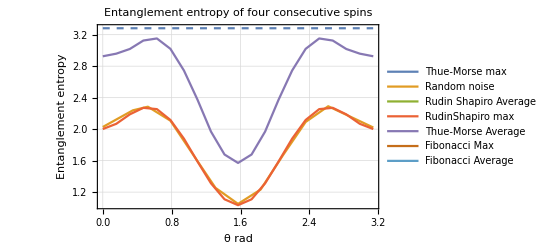

```mathematica
Show[ListLinePlot[{tmmax,fitvals,saturationvalues,rdmean,rdnmax,tmmean,fibomax,fibomean,fibsaturation},PlotRange->All,PlotTheme->"Detailed",PlotLegends->Placed[{"Thue-Morse max ","Random noise","Rudin Shapiro Average","RudinShapiro max","Thue-Morse Average","Fibonacci Max","Fibonacci Average"},{0.5,0.83}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.14},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of four consecutive spins],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

```mathematica
ListLinePlot[Drop[tmmax,{{1,2},{4,5}}]]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[tmmax,{{1,2},{4,5}}].

ListLinePlot::lpn: Drop[tmmax,{{1,2},{4,5}}] is not a list of numbers or pairs of numbers.

ListLinePlot[Drop[tmmax,{{1,2},{4,5}}]]

```mathematica
Table[random[[n+1]]-random[[n]],{n,1,199}];
```

Part::partd: Part specification random⟦2⟧ is longer than depth of object.

Part::partd: Part specification random⟦1⟧ is longer than depth of object.

Part::partd: Part specification random⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ListPlot[Drop[noist90,-150]]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[noist90,-150].

ListPlot::lpn: Drop[noist90,-150] is not a list of numbers or pairs of numbers.

ListPlot[Drop[noist90,-150]]

#### Alternate spin entanglement entropy

1) 0,2,4,6

```mathematica
answers1 = Import["/home/yajur/Dropbox/miniproj/outputs/answersnew1.dat"];
```

```mathematica
answers = Drop[Flatten[answers1],2];
```

```mathematica
Dimensions[answers]
```

{4200}

```mathematica
answersn = Table[Drop[Drop[answers1,-(4200-200n)],(n-1)*200],{n,1,21}];
```

```mathematica
Dimensions[answersn[[1]]]
```

{201}

```mathematica
answersfitvals = Table[FindFit[Drop[answersn[[n]],{1,60}],0*x+c,c,x],{n,1,21}]
```

FindFit::fitc: Number of coordinates (0) is not equal to the number of variables (1).

General::stop: Further output of FindFit::fitc will be suppressed during this calculation.

{FindFit[{{1.91376172082647922},{1.89927161599172489},{1.91243238739074384},{1.83078060436901113},{1.8809390039438878},{1.90738820576866042},{1.90565457862256693},{1.89944845693526343},{1.76677951786732845},{1.89029478851098398},{1.98728095881796274},{1.92461529686879684},{1.76565397574352079},{1.84011945370631813},{1.86473948853585814},{1.7129147052472975},{1.85870061894135441},{2.11570360771978105},{1.87273258290186928},{1.90435541737929093},{1.95843924186789198},{1.89107152796574951},{1.888960533661594},{1.94442166187383836},{2.08410743006731858},{1.9215645638490606},{1.88053463022761158},{1.87912926385036228},{1.84913516210212126},{1.92812195938734154},{1.84667907206388882},{1.81716059546814357},{1.87209203129550472},{1.80347062885461296},{1.75614697181712076},{1.94633957214261821},{2.02776283048580419},{1.96208183400342318},{1.84291821461936545},{1.82544704112110279},{1.75862446219593305},{1.89047136650429604},{1.92386191303117471},{1.80698852848644465},{1.7828311640412382},{2.06640896836059174},{1.96505111065388216},{1.57408031216013855},{1.68472746205517732},{1.91716320653715222},{1.83509016579697515},{1.76415961683782485},{1.61558090331407889},{1.69566278123690828},{1.94902947373442848},{1.80303873602121145},{1.83497252438782499},{1.81484360942055689},{1.91504260749118438},{1.85820947026839711},{1.83686547227899366},{1.92897548880575687},{1.83182480172976181},{2.03058356868480061},{1.93519269148001816},{1.89837641353412323},{1.80747241499994149},{1.84365335443324852},{1.70804304028668619},{1.79714863441132233},{1.82350259182435326},{1.86862652862040335},{1.98073643763212126},{1.96502580833101725},{1.8139974262546652},{1.89809515358927894},{1.8860287050030462},{1.73880362797945809},{1.90707239957358499},{1.81586767283569484},{1.90794697330190322},{1.93727655313148306},{1.93836628752760287},{1.94969979890508882},{2.081458586234751},{1.80300150449947427},{1.8537704904639325},{1.69829133180424008},{1.94536350008088932},{1.99934875090093667},{1.99764195446528503},{1.77613660319651623},{1.87437743391190748},{1.90730446643984974},{1.99249013211395853},{1.86747455534203888},{1.72445666438067735},{2.10654683261586051},{1.83730060232737635},{1.88314129671825681},{1.90932175137724602},{1.96009696659584987},{1.83526539609497141},{1.74300145279038787},{1.87312493723940987},{1.79591247630314221},{1.66470476442361481},{1.83114076804860604},{1.81589026651993768},{1.54278074748236471},{1.84456936052290321},{1.83595845191591245},{1.91090653773164498},{1.95964090070408559},{1.86342843990109941},{1.93938452069935785},{1.79913094960361919},{1.96767201402221637},{1.87778214327109483},{1.84843676915696209},{1.95747163897274401},{1.79982437999467315},{1.90379871390677491},{1.92743939341517634},{2.19204828129271956},{1.90958680651408019},{1.8886759352420508},{1.72152594960062144},{1.79586433787408328},{1.81627325098798065},{1.70993868153553108},{1.91018003167066097},{1.72774163045920459},{1.84519082858999717},{1.86275358758546572},{1.87561896309476839},{1.80035804534705846},{1.79207246741093429},{1.84420904301337618},{1.97440808616346364},{1.77326541684850536}},c,c,x],FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},{2.13093655661585713},{2.07846868581947231},{2.07167477294313462},{2.06683728786536447},{2.23598259837017288},{2.05904943192557699},{2.0894169068014925},{2.09861829797188992},{2.14047487036249828},{2.30489901745489823},{2.23329263384001653},{2.16291010208253942},{2.07476781230924212},{2.19555713722617796},{2.0803385495966884},{2.08677064761031739},{2.04586462281086101},{2.17769252100815702},{2.2301332752846954},{2.08843681779014911},{2.09789630864299914},{2.13145176712369011},{2.10107259770187849},{2.1318683205051836},{2.05110859732627038},{1.90260072818534698},{2.11695572725588832},{2.04492590890510995},{2.05082324394396443},{2.1409999752972908},{1.99412458174753815},{2.10076526392807761},{2.26298450192937795},{2.15872991384021651},{2.12347758480355742},{2.19108981073153553},{2.08542400429486552},{2.06889630967542315},{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},{2.0812727175015131},{1.98687106167438943},{2.0247532090361311},{2.22451118447937235},{2.07193502491740089},{2.04881234827659631},{2.1244556066142688},{1.97248788833229849},{2.12628989214784259},{2.07578138921681221},{2.11544906447112213},{2.16648122893804729},{2.0766369469445598},{2.14257138870756325},{2.05245765840485106},{2.05559949741929193},{1.92964674851960938},{2.02139410262315167},{2.10473380253287035},{2.10139003251337275},{2.0992120510683927},{2.01384750598101991},{2.0253887012463454},{2.05475177166932443},{2.15818035500056782},{2.16392128967223085},{2.09944611103246492},{2.1502128181598521},{2.20513541369072108},{2.19679763024536312},{2.184691857634109},{2.0762844690840554},{2.20050856647502346},{2.13508722067886714},{2.11203805002739475},{2.16689024486502868},{2.11592668755036417},{2.15630854341583733},{2.18437432152485789},{1.9760230172206652},{2.19948351785648644},{2.07445110634576135},{2.06278139033572616},{2.1231212083842288},{2.18337826302699289},{2.03805625196250562},{2.04686592363591924},{2.15427388252376995},{2.16742523079873628},{2.10128773309775507},{1.91895217882289537},{2.21262537779760704},{2.03653714491704996},{2.08306074211035552},{2.10012171746195309},{2.07548552615806647},{2.14571941380191511},{2.02266055320144078},{2.19089127852881038},{2.12859923658595207},{2.12079915728621948},{2.13100873727048557},{2.08290524931863974},{2.19203673124526155},{2.16581040568989769},{2.00631969190567983},{2.13625699943410474},{2.19829946592826175},{2.17858736982573076},{2.00431470489428154},{2.15699828582474895},{2.19146846562832831},{2.27277989196288432},{2.27226620197035123},{2.1846911262020452},{2.18489740272722033},{1.98315172058675748},{2.23643410247760421},{2.09942887170071435},{2.13676053867895543},{2.11660231562123924},{2.06825043952092269},{2.11125337321472495},{2.12979206117769238},{2.26289047714504843},{2.13846490713632953},{2.14377061862492724},{2.12130180097983123},{2.16103687669175626},{2.24445007207118286},{2.0920535133887066}},c,c,x],FindFit[{{2.41794397379062387},{2.47145947050358439},{2.49766984949509485},{2.44222937141221408},{2.4819388381584977},{2.390883314324876},{2.31137091489236468},{2.32471020748407042},{2.339837648082844},{2.23500094604677546},{2.3596430591818649},{2.45936658465403024},{2.40331032799890254},{2.38138671858982853},{2.42155763190408324},{2.34579176955652979},{2.46826321453041864},{2.28277713823790807},{2.41267127904434187},{2.41853869285033873},{2.39391023035868855},{2.37058503339255244},{2.38728829110215246},{2.43109571682168602},{2.36897888655980449},{2.51568057530156253},{2.37920724193310562},{2.28605360327150819},{2.40480638195155017},{2.43513923403253951},{2.37798973643615819},{2.40892892873072784},{2.37002063532475127},{2.4029918260918457},{2.38798254720072745},{2.42085390752242313},{2.35250580982863156},{2.40060964765589446},{2.26595639110614622},{2.41714728785143507},{2.39118766173023056},{2.46357278385229339},{2.33266526992443479},{2.37575345301178009},{2.37616948701123931},{2.30383283457217836},{2.45753281487925568},{2.33845350721397338},{2.37807707462362039},{2.40232590655796141},{2.44099350033007223},{2.32672698027742042},{2.40730353251887985},{2.43745515602523488},{2.25781191150631555},{2.31461358385496396},{2.34264208951677011},{2.34107313630399405},{2.34850420571399932},{2.44195077154583728},{2.46114201633699992},{2.42255883416958895},{2.45778726760467103},{2.4457647728597629},{2.43732911960950638},{2.33288260172080131},{2.3683474108234237},{2.27229211947192145},{2.34523246574348709},{2.38136625246042133},{2.42444472041764358},{2.4181465762260479},{2.28470766606431752},{2.34096205107919042},{2.24697086787979217},{2.28494764280069385},{2.43678810410304703},{2.34665821018637555},{2.29870650073978444},{2.30357015822694011},{2.28572195285976632},{2.26017069824976247},{2.20890693442430042},{2.3650568927579787},{2.33461798593955994},{2.35428974354244769},{2.39919346499901032},{2.41880101642468048},{2.3421181141334646},{2.3841289480450869},{2.46192029485857988},{2.51023418976270785},{2.34434610157630941},{2.36467442567019592},{2.43063893674368003},{2.34526098643706238},{2.47371996801967642},{2.36694946349895385},{2.30399389337634197},{2.38244762311689939},{2.47651360454344838},{2.53131504683249498},{2.46575666013675576},{2.49139799222480596},{2.48435844549655549},{2.42322197765081482},{2.52841088760287036},{2.30147998819440236},{2.30645159003095523},{2.43305684489300944},{2.53830176936034713},{2.42252975343114141},{2.45515528943209027},{2.48943641707139829},{2.30445901958202759},{2.41453139599831923},{2.45229179081313609},{2.49033345758611313},{2.49223492395141877},{2.42870291938129457},{2.36127332813166513},{2.46828676698174077},{2.43488720850744134},{2.47092889924745363},{2.48050041722710057},{2.39803156150213681},{2.51910431112609956},{2.55466731289838611},{2.47475286072181477},{2.43590632751905023},{2.55240907685714147},{2.58597387960053426},{2.524937529044879},{2.38807807137566286},{2.39425990656521837},{2.41151713146795244},{2.51919289385163614},{2.48067245618510279},{2.46793850239352564},{2.48780985290691969},{2.43503974955727776}},c,c,x],FindFit[{{2.5451680475956513},{2.51455059708276529},{2.44980545810392192},{2.53274783793923097},{2.63901438389897836},{2.63368505012332932},{2.62320525494978929},{2.66324700000929848},{2.64276949268600436},{2.59992813099464515},{2.5922390609960515},{2.65087359405398848},{2.54511284283904349},{2.53083415898830477},{2.65245581475205894},{2.62414923849181347},{2.56219651859933828},{2.54148424148865981},{2.64429537766995315},{2.59551716843891489},{2.54901724175413191},{2.58500614398379902},{2.59797780086860009},{2.56337353340152596},{2.48982005641218596},{2.43307565992241637},{2.49147941257097561},{2.54104537530182828},{2.51176412144112993},{2.52977923708634123},{2.44179394889659029},{2.48712817008214771},{2.47497618126139685},{2.49812546534661273},{2.5167479815239453},{2.56607116572623495},{2.59255565958203027},{2.53210182266225248},{2.56436132391236349},{2.56426082103706365},{2.64291646041113992},{2.59802743980124751},{2.61852411144574715},{2.53423773853161061},{2.55587507954857696},{2.56077020519139209},{2.54067497563226041},{2.58278848695784147},{2.53883892126938715},{2.51656503764497819},{2.43988484343098611},{2.42061176403682632},{2.41460824030033638},{2.53245159205009163},{2.59107299481195952},{2.46733309575726656},{2.58327970256369},{2.51453955782678174},{2.53969164741021425},{2.50988066676071941},{2.52563402391156266},{2.55666405279016606},{2.45703279260104424},{2.54971199363062695},{2.62769710349369978},{2.51822738988812311},{2.61920686882079412},{2.61643844314893048},{2.4311417764087051},{2.4571376845082562},{2.55038578483130074},{2.57201523168759572},{2.58060167790652972},{2.59167636332061813},{2.63217397401902842},{2.57196197593260978},{2.58559377018001957},{2.59302895971910008},{2.58862511020880204},{2.60392064669751866},{2.59817038725146166},{2.5923719860949257},{2.66803336351715181},{2.68517502644497164},{2.5563398020294219},{2.55698349509182332},{2.57645089018684192},{2.56194960377337022},{2.69431115767751717},{2.58986051753947422},{2.63398673528980654},{2.65377896795285917},{2.60531530925229582},{2.63510926271871915},{2.57883470836219342},{2.5873705042248738},{2.58973372836581017},{2.60760520577707267},{2.52662605254182671},{2.51403023717226137},{2.54234233841700252},{2.55775252542890286},{2.626774416846831},{2.57515548507976089},{2.54735174000880837},{2.53329850007935553},{2.61435131463037784},{2.59677075277521752},{2.57207585648539716},{2.62287079916926169},{2.60784092895684694},{2.66403451412346959},{2.57550740289565239},{2.56161628258718199},{2.60860312358791147},{2.68095896388155452},{2.64075561433871542},{2.58803656884496913},{2.55811661166277427},{2.50447217005096201},{2.43772772248428593},{2.45367260868795922},{2.52753190473151523},{2.5393641712676267},{2.57796476771953476},{2.57892989141892937},{2.54382732999312466},{2.53779919156709211},{2.45746857344706449},{2.52049490649572316},{2.58328388631633654},{2.6800452062584843},{2.53639393931202006},{2.60188934997615595},{2.6547609023220704},{2.67582978174695407},{2.6613909853756561},{2.63663703313017273},{2.65704595611055661},{2.63797310157648424},{2.70072382002228606}},c,c,x],FindFit[{{2.58400548982700062},{2.60226795483193607},{2.58167751711544558},{2.52457483766211865},{2.42477391047638147},{2.42190498858133729},{2.56609292803172284},{2.49038855777374035},{2.54631262454034468},{2.61913738716834876},{2.63778947542088327},{2.63535202229573518},{2.55328813262189414},{2.51537570784442632},{2.54377115676547172},{2.58310835925746973},{2.55083705057941268},{2.54828224598088005},{2.59121513153029337},{2.57155642116058525},{2.51764762293013877},{2.46420289742170784},{2.50411762392583093},{2.56332860787809835},{2.47683355902058189},{2.50205677442144436},{2.55291580043133815},{2.46914224415444528},{2.44516302189195134},{2.42286654865953421},{2.52943756800225739},{2.46762869290659426},{2.38599367004423701},{2.47371318055589828},{2.46915906243347338},{2.49371621422570344},{2.48366469101178211},{2.47976354407621447},{2.45081406503165145},{2.42045393296328992},{2.41663181570692753},{2.46002659315274386},{2.51681378885511409},{2.53310273339719139},{2.65222386781752384},{2.61985412690682384},{2.52978609430306189},{2.54513771284785317},{2.57728650107184532},{2.54708369243807731},{2.56351307449750498},{2.49367024972170137},{2.43288587941394674},{2.43052558010304942},{2.53018493791318155},{2.54477992742642778},{2.5398524244360603},{2.51762149430014004},{2.52411305809003173},{2.57932948790064609},{2.4605912760707982},{2.47896373153878713},{2.54360797424872054},{2.53836744285407212},{2.55995612747416823},{2.56477340355034533},{2.50939891625758316},{2.4947644192898224},{2.54714073762973525},{2.60078524604982153},{2.52967729052980772},{2.54853837051432297},{2.63763609567844037},{2.66084853939658883},{2.61257824834230013},{2.5507184846555262},{2.59568260905764081},{2.62157936192092222},{2.65381239185622553},{2.64346012771119421},{2.64607566422442719},{2.64880929598763881},{2.48802822585526196},{2.54672498447933338},{2.5242966382184302},{2.55699475887450234},{2.61465274782597712},{2.56797480593231775},{2.53922737157219913},{2.49777974601783637},{2.50757212008154706},{2.47548777716951429},{2.49842345483713402},{2.52268403803078289},{2.50793080010661695},{2.56558404620583769},{2.55543569149494587},{2.55730289977406722},{2.63847874101316515},{2.67351981745033607},{2.57599690533395354},{2.56867616867857684},{2.59988968757026528},{2.63686167840737262},{2.6374024115831296},{2.64800745263842341},{2.61163400183072492},{2.53752898175504837},{2.57558312756268126},{2.57064183785872791},{2.51969723390103928},{2.46386182230437711},{2.53213079798889318},{2.50793188634905828},{2.56429571007859014},{2.54934344914160294},{2.49357590556982922},{2.50477107179490499},{2.52357148963787648},{2.53775473647887218},{2.56869245807096647},{2.54813014511606983},{2.57162218951768518},{2.56059252635326695},{2.55763724202244536},{2.47233527296846711},{2.5342006023193755},{2.56677368771992853},{2.54454470684220491},{2.62088536447271903},{2.5491458981844084},{2.55887750111191759},{2.61687892232175301},{2.58937397199269537},{2.57236969478328836},{2.56800774214731753},{2.52543776821279487},{2.49937570777644336},{2.56033909073011534},{2.52129828244308074},{2.55896153110338043}},c,c,x],FindFit[{{2.3167954025435753},{2.31942777697629543},{2.41300631171935098},{2.39977144640024198},{2.3924639131151082},{2.41008362153219391},{2.33937404634022217},{2.32388355676920799},{2.35579552147249194},{2.35718858787675156},{2.30591800937528557},{2.29490008269730694},{2.23295634572034318},{2.27488823208589075},{2.33324712105489152},{2.31265898751962773},{2.20111362723053983},{2.21270395159951416},{2.27238432660289602},{2.28447810040525301},{2.28821918390858636},{2.25587955487953851},{2.34394958035958823},{2.35402124047823946},{2.43938709954759592},{2.46436342302912559},{2.43552709174474469},{2.41459131021890761},{2.3961800314543158},{2.39129097515973932},{2.37561791104003328},{2.35522696555644462},{2.44439601026171616},{2.45398334751488534},{2.42133688747755826},{2.44133933558371208},{2.45134500571345848},{2.4671499650842259},{2.43446710805318789},{2.41443449774737307},{2.35551083075689238},{2.36129690209191434},{2.3590753851937456},{2.37682927575927128},{2.36691460422193511},{2.37730623449115397},{2.38446914384857767},{2.35853987057811088},{2.39511865723504291},{2.40257551204965214},{2.4018720983522095},{2.37770418279076123},{2.32360630341351415},{2.31579506333145302},{2.26463011107325052},{2.27702572607783171},{2.38943644092371121},{2.44123637727657172},{2.4148573717685955},{2.38111777558860105},{2.33835911727859447},{2.33057556293859536},{2.33522719946013746},{2.39025481953959451},{2.37690899699790403},{2.36941601871717245},{2.44601241465842323},{2.44377952860122694},{2.34335647212794473},{2.35362065393460362},{2.41681634309847482},{2.36660720200270314},{2.32862454883893921},{2.36789708260202891},{2.34989423003513043},{2.31900672797708118},{2.4354268060298625},{2.42390239165207388},{2.35667318075226406},{2.40889252614052207},{2.37374997476999372},{2.39903598694758591},{2.29389513397862777},{2.25631013060407915},{2.38244261259446111},{2.37643411851041675},{2.35115067589422999},{2.35543214868927286},{2.41149050592075209},{2.39972938048251727},{2.48187574036691672},{2.47049837675802664},{2.44594946498099253},{2.4338046555653996},{2.35896741430334966},{2.35257690861521152},{2.34497916549485463},{2.28798608262290815},{2.22750352876966495},{2.30565389598110659},{2.32826906669785894},{2.33445223789070866},{2.38580017123071198},{2.38654462471314499},{2.36738704220888963},{2.38549510531081932},{2.35995376691799619},{2.32544799007527292},{2.30355160408942128},{2.26655783345704887},{2.34531964556605477},{2.4062238909896605},{2.45656581154931208},{2.48850941701242112},{2.49153361280656371},{2.49038165551907653},{2.37205034601439335},{2.3562475243223826},{2.44206963827062085},{2.444681605208884},{2.44675706368877011},{2.42477231219670264},{2.37976989498153335},{2.35873458027764027},{2.35874426613595256},{2.32427503257158197},{2.31141788811647464},{2.31410904437397669},{2.3057313740066272},{2.28329775191667839},{2.27464876603320398},{2.24853185163549707},{2.35164256287175588},{2.3383521305648558},{2.36096625978377439},{2.35738044824911919},{2.21404875182192074},{2.25195043488142455},{2.24305038798690282},{2.20577761181087917},{2.2971193325255781}},c,c,x],FindFit[{{1.92981574822252866},{1.93795901372787505},{2.07937437424215643},{2.09382029197292408},{2.08322107388557276},{2.09429943855107403},{2.07451765165813029},{2.04236891028035306},{2.02397860691149356},{2.02999000308012167},{2.01892953463747338},{2.05190081849973049},{2.05732529204377324},{2.0576827921361085},{2.02787132592664143},{2.00299155677718188},{1.93014081014043626},{1.93081231140372389},{2.01187795128150393},{2.02430987704023568},{2.05705723578984845},{2.05841649480262401},{2.03169427600389652},{2.03378693960241463},{2.00105559574569503},{2.00769805451454442},{2.01016928888059843},{1.98164128858222188},{1.85605961649075812},{1.8541220958511242},{1.80487358253177832},{1.82221106684393219},{2.06307150496976988},{2.05090432512338694},{1.95316367273161018},{1.96438469134281801},{1.9908029520696553},{2.00678865657643879},{2.06767466510342945},{2.09356600502220713},{2.13174162946014789},{2.1028225753946499},{2.05943059222740832},{2.04764807461593357},{1.94543952838790868},{1.9537579458466996},{1.94498979461358457},{1.94815632538536865},{2.00552331362311698},{2.00020671611298928},{1.93838775762499838},{1.92514793816339513},{2.08641502526345946},{2.10357298379914637},{2.00677884552490893},{2.01082019637362119},{1.96509783176578878},{1.93765694521626664},{1.9726624639339132},{1.96977208356320288},{2.07827923634730727},{2.05907142322316705},{1.9083613853429402},{1.90475942951572774},{1.87031962167995736},{1.89684210535582265},{2.00241851838105545},{2.00393591841973429},{1.8296375034254071},{1.83456069896104368},{1.99074978467523378},{2.00660153399840535},{2.05083827462726731},{2.04594557200968064},{1.95782079138633813},{1.93454023723330959},{1.96745123470499506},{1.95242445052570379},{1.89395421939037933},{1.90022573796794858},{2.07293470447777573},{2.08242227050283946},{2.01842006320082801},{2.02231305730764666},{2.06725105863907466},{2.03771369893702214},{2.04603650544324722},{2.07034750256508104},{2.10407791956148005},{2.04715618927149512},{1.93986084716430041},{1.96598066618744327},{2.08696331229980014},{2.09718054855691127},{2.01928577958007072},{2.00024127652954986},{2.0937995686149784},{2.13680103218350492},{2.14332229076507019},{2.15118400958717437},{2.08165589855992517},{2.08727733240592128},{2.19073856909724185},{2.17352343774700296},{2.12551649615072069},{2.1056816839884962},{2.03350666418609327},{2.01153380633861501},{1.96807945868116008},{2.00673061307760969},{2.10189004676598756},{2.11954801402448068},{2.21135070815792556},{2.1960690728326604},{2.17089788700898456},{2.17464762215458318},{2.2007316646033539},{2.21632764878713573},{2.19911194650088238},{2.18034072233276355},{2.14677587128728042},{2.11392292408854621},{2.2248617569051552},{2.22381524466411884},{2.20804016590720043},{2.21812187094238178},{2.13231438483163549},{2.10337684301171413},{2.04387364943910299},{2.04221964139933476},{2.01129466263394097},{2.00021266264288666},{2.03116406716312437},{2.03529951828452127},{1.98705738584097569},{1.97015098019714952},{2.02680036274888575},{2.05312489545296639},{2.03890576943487423},{2.00820037235839788},{2.07489887387002803}},c,c,x],FindFit[{{1.67392935557465594},{1.65910107002301688},{1.63428197905002248},{1.65129034738151348},{1.70276639751692405},{1.69815230606517531},{1.71647970382987269},{1.72536215144769822},{1.81734423271915047},{1.83413854077611838},{1.82003632459268316},{1.80412264858067983},{1.75619203728441353},{1.75535454192381679},{1.67431384703633812},{1.67283820024241758},{1.69436849013105606},{1.70936729712304292},{1.72915151621905894},{1.72248466679770518},{1.76390356833890594},{1.76530449297592296},{1.73752025363452178},{1.72988650861208781},{1.80203319484933822},{1.7947792458878975},{1.79363852236465293},{1.80982748727253417},{1.78938206734112715},{1.78462472702017627},{1.73226906765053501},{1.73208122724598579},{1.74599695156917578},{1.75352415869307565},{1.84103912137146542},{1.82962641964418404},{1.70960862622440013},{1.71691261330105194},{1.71397273940401829},{1.69064233728802371},{1.69004433332014581},{1.71100462547686316},{1.70600186486461714},{1.69428210620220909},{1.74978157418618774},{1.73987636425845249},{1.68048599620866934},{1.69010769650988912},{1.65772305789355756},{1.66220822744745456},{1.72823609877615536},{1.73138905035487589},{1.82122462996872447},{1.80402620336569131},{1.69661020201906299},{1.70701753417843882},{1.69898963802583114},{1.70450150865155403},{1.75144409989411276},{1.75378601872265749},{1.81517869629471296},{1.8071136924452309},{1.76840724755625822},{1.76887027056019863},{1.81949362994173414},{1.81155526907921383},{1.76179124975861945},{1.75668359046018185},{1.75007390980880229},{1.75703959904299678},{1.72053076502266467},{1.72086669424062744},{1.73120816818395706},{1.72541018718014638},{1.63489288655422516},{1.64407788477617989},{1.62615247515604189},{1.61847895741419356},{1.72956249251693883},{1.74288667052971968},{1.707184013208499},{1.69265089699633942},{1.61459718889987114},{1.61172355106480514},{1.61488664970284912},{1.6236985342555923},{1.72570906798291079},{1.71637572461735277},{1.71396108090959376},{1.71359424346106759},{1.77621296454278999},{1.78196205173709332},{1.74081866617057091},{1.72811030154823131},{1.70925889805008024},{1.72939310672007895},{1.76191013943942476},{1.76188508172341285},{1.76259359546564864},{1.742807054731216},{1.8303877478221271},{1.82789235342238565},{1.80708291064411619},{1.81710364875213393},{1.76870167100661746},{1.77130366440103626},{1.84671766803309567},{1.84303900077257588},{1.75934435077684781},{1.75310885229398972},{1.85288288917019872},{1.85263094031058095},{1.75244785460783303},{1.74141659593958353},{1.73000995568601845},{1.7323837416086969},{1.80804794835730642},{1.8112370368347257},{1.73640460752687753},{1.73081310340938188},{1.72008536386720268},{1.72913510042587726},{1.7503580464090327},{1.75573220236001615},{1.79387203092799763},{1.78555605594025213},{1.72811269858385552},{1.71757199463975829},{1.75874217569048552},{1.75396374932543986},{1.75738545597435802},{1.76351247131704447},{1.72772800036517493},{1.73280596411022048},{1.75637126300106594},{1.75622904496845811},{1.730996642598436},{1.73476283307103274},{1.74186018924604991},{1.74362671348954135},{1.75447479146871044}},c,c,x],FindFit[{{1.36273428682461706},{1.37089005441560885},{1.42604282864047605},{1.41239447879739277},{1.56835807618930301},{1.56032625093092481},{1.43001490046893065},{1.45164305121508641},{1.439276093076995},{1.43960684665529715},{1.39344738731379736},{1.39434013874572216},{1.46090522264017997},{1.46572723755737222},{1.47363390202289635},{1.47123150285757132},{1.4305384456161343},{1.42387022058524693},{1.43698877265818403},{1.44688459063468677},{1.51861245048163052},{1.51632405249774993},{1.42572881902377135},{1.42434898089415585},{1.54237674364316812},{1.5339799825752749},{1.51772234293412001},{1.52784727547775345},{1.55629000137452733},{1.54368203763263256},{1.51365747810998319},{1.52210148407270784},{1.48280610422055692},{1.47799560240066752},{1.48395045478311638},{1.48737246963151426},{1.60979328110049913},{1.59701975696810017},{1.63908022108303131},{1.64412586178886899},{1.50225878582068018},{1.51499509205446792},{1.46794381075433011},{1.46246811389887665},{1.43534310497739126},{1.44233886305738923},{1.48158847323205389},{1.47804265244855815},{1.55408242783523365},{1.55127880733499901},{1.4722548250960763},{1.49406594171276597},{1.51108230872099614},{1.50226799086797191},{1.49908630565384504},{1.49076545828847307},{1.52680843829667312},{1.53266031704840522},{1.48217037437180355},{1.48700826853032009},{1.46296697816903376},{1.46662931625302195},{1.47939028390471594},{1.48158687491732377},{1.46606309990785522},{1.46445755878182671},{1.44685080686330014},{1.44004854878055366},{1.513990154422719},{1.50282116638677898},{1.51783647208231076},{1.5150933471996193},{1.54265783598100681},{1.53964058865225129},{1.49086179633461891},{1.51079867826646996},{1.49510732608176356},{1.47635386292702853},{1.50404069699253618},{1.5021577252482714},{1.52607415221636233},{1.52915491277116056},{1.52421501676625137},{1.53231869010158905},{1.46946066415416854},{1.47051066017171528},{1.48188328898702459},{1.46532354719132929},{1.45765729225898966},{1.46921325774307032},{1.52807682411692314},{1.51424762717243655},{1.54779727534244938},{1.54742668936798489},{1.55369805949016371},{1.55508818382030567},{1.47310832213547327},{1.47023264227232287},{1.50090586157687733},{1.51885228522667215},{1.46963738257463028},{1.45347508822074567},{1.53287542345452477},{1.53364395261050923},{1.51071291220066861},{1.53711612082737514},{1.49013139592196531},{1.49056214814680565},{1.44888370365372943},{1.44646583932612516},{1.4960962398315043},{1.47994034411852571},{1.5424446742432838},{1.53505175997364574},{1.53990803885349181},{1.55159353151509039},{1.52517804262284984},{1.53925075418229551},{1.51494355907559042},{1.50583377179409572},{1.46904910636613173},{1.45900872658045677},{1.46938269328734616},{1.46090770185943053},{1.53612507489443817},{1.54157008837221343},{1.566368618542342},{1.57986117352378952},{1.51649035184031122},{1.51642724768983905},{1.59564338493607627},{1.59942083060847828},{1.54266711917947297},{1.52658196884664554},{1.5578109170032346},{1.555089057137095},{1.4801495100568014},{1.48435370527840904},{1.47850945599677153},{1.49536460664646786},{1.36247893666000053}},c,c,x],FindFit[{{1.44220131963245701},{1.42373398135782847},{1.45239367653238527},{1.45597130743460812},{1.43941915234951989},{1.43514195720765958},{1.44831352971632077},{1.43401047925024194},{1.47092204482685407},{1.49585260744469051},{1.38838405933736309},{1.39445731033191578},{1.39548053679409345},{1.41579366840565335},{1.44438169862661625},{1.42356746497412989},{1.41633596103606485},{1.42448588823330669},{1.45391983791986457},{1.44004263374659325},{1.4389867471791935},{1.44246615278543211},{1.45581799302156045},{1.46659195698612965},{1.41573748895009421},{1.43099038532613321},{1.44242629665782896},{1.43131455074452751},{1.41630255504832614},{1.41804326033327177},{1.37937832184964648},{1.3672339986543034},{1.39340442790283614},{1.4098825189426405},{1.35920212022906073},{1.3550064471833505},{1.47766460470213445},{1.47288185051731912},{1.41529797109044009},{1.42063715023245574},{1.45528002910841448},{1.47135646087710104},{1.3644406063415726},{1.36625940657408052},{1.39709283835562981},{1.41058816130297782},{1.34375546727400108},{1.33036702234153537},{1.31035853091930687},{1.31979444808523527},{1.36534620611895741},{1.36675254285066994},{1.40126899872499089},{1.39961080280068462},{1.4375480020503566},{1.4166625764962919},{1.37419217080076672},{1.37545137733267775},{1.34414003558467088},{1.34705059153477036},{1.43547774672985939},{1.42840260479356429},{1.40507644669309029},{1.39512939794376667},{1.39063008098900287},{1.38610418171484939},{1.46758481993615098},{1.48260626571824106},{1.38550062157733267},{1.37495432671686246},{1.39836465891960926},{1.40931751958241947},{1.37759733772341408},{1.36101963616203991},{1.30286557213658583},{1.32012562327083782},{1.47295365851073012},{1.46189574084145724},{1.44746920937831591},{1.44461988080686821},{1.43917027051304891},{1.45828494787316898},{1.36635012271904377},{1.37173819340279346},{1.4123704651741622},{1.38578323048579688},{1.38449746726283229},{1.40304917234123705},{1.43183498973489032},{1.42846582246155807},{1.42060590834767142},{1.41214409121511575},{1.42599693203640165},{1.4378652113677004},{1.40849341942402928},{1.41172419119220161},{1.40214480926807994},{1.38727447901288392},{1.43799148159846868},{1.44280756825384171},{1.42666052138292132},{1.43092778037926949},{1.42001316931777089},{1.39549826341458716},{1.39106666897828513},{1.40303814948499728},{1.48351175370166799},{1.47374792203954663},{1.41090528799632975},{1.41329196699740178},{1.43676897530161729},{1.44280533421789592},{1.42195217389644069},{1.43143079609521817},{1.42002179751007041},{1.41491544592383844},{1.41058693220328935},{1.41879154583871814},{1.45671450499032718},{1.43879849375304003},{1.43097916544139681},{1.44892140610873832},{1.42757068100454876},{1.42442453161397031},{1.46359599499806126},{1.46229009584926462},{1.45401929251888973},{1.47058362857319436},{1.4107277341095692},{1.39378315110719386},{1.46090417705087106},{1.45512629237743507},{1.4964055605193185},{1.51126093774715575},{1.48419344902843098},{1.4914866445423276},{1.36905849714920769},{1.38098136465659027},{1.36611990700459351},{1.35191192762891355},{1.4227512678883727}},c,c,x],FindFit[{{1.41422815115935352},{1.40948931913408271},{1.3843401715428203},{1.39098910742514814},{1.49076312255899124},{1.48136107914558712},{1.51415746320958555},{1.52214070145884683},{1.46646302839303822},{1.46977737873757275},{1.51895512454231008},{1.51442297515188828},{1.39270519862883524},{1.39936567757230579},{1.38367844119459305},{1.38300444761488039},{1.50536207226918073},{1.50525823687331872},{1.43366780293632745},{1.44431808991853106},{1.34578828940752837},{1.34441474154371887},{1.39441375353479335},{1.37475261462317944},{1.47177319944854856},{1.46327155914758933},{1.49588988731171035},{1.49710875890542883},{1.50105442809106293},{1.49168061716428935},{1.42702661519587193},{1.44954319404931398},{1.36349149384849788},{1.36206896179098047},{1.46681115122691819},{1.4823341077811425},{1.56211814064526644},{1.56474266192176437},{1.53437096324821765},{1.52636809685218711},{1.53122040377967861},{1.54070404399347005},{1.54147705413985725},{1.51929799618227102},{1.46526701565374329},{1.47133298723703909},{1.50151717727207235},{1.50289893856923729},{1.47973356412806512},{1.48766491538933132},{1.48331246878423184},{1.4846818951495433},{1.48519261198646624},{1.48072764577277583},{1.46092135121485112},{1.45443159665433752},{1.49416888720620689},{1.51203880217259012},{1.5520681221367163},{1.55056337494437768},{1.48734453622061325},{1.48060364364846842},{1.49990827612678612},{1.50466300546915099},{1.45951952706778165},{1.46166470181906871},{1.53932967726506331},{1.53975015885263722},{1.51949037724929448},{1.51275979287732265},{1.511903417818655},{1.5149857121443906},{1.41025848534863085},{1.4197022159602124},{1.4641606967197891},{1.47091418759345238},{1.46640216076069452},{1.45718357287143041},{1.55003884142360837},{1.55585393574460862},{1.52532308019390417},{1.51311407084737426},{1.55409239604263472},{1.56914885674970228},{1.46439658853231558},{1.45957194351663344},{1.51068792035130128},{1.49717897057185034},{1.46770983674494948},{1.45215602811781874},{1.48165682888141892},{1.49688632852785375},{1.50267102745109571},{1.50474247483789902},{1.41747689003057031},{1.42509273917060941},{1.4793583816104896},{1.47649713274934324},{1.40040474543745797},{1.38684210631914207},{1.44328122119512403},{1.45833854402161789},{1.50365558335083049},{1.49047914196746811},{1.52065724628965171},{1.53034518650758322},{1.51188552250035313},{1.51431901473187591},{1.3936493927832263},{1.38669286626146793},{1.451740490148409},{1.44098336987274123},{1.403637574479637},{1.40982003552104995},{1.37700492113748929},{1.37728066582492126},{1.48513323779355622},{1.48470524090831701},{1.47933535366136737},{1.47573797275239782},{1.50631588282032047},{1.49334440270791857},{1.54941509352931739},{1.55775964727820138},{1.52455872262974634},{1.52314222121084164},{1.58811274403144598},{1.58090081720736531},{1.58831637649081214},{1.60057404593364328},{1.4866533175010932},{1.46962641960092455},{1.50223920049957815},{1.50801127052757567},{1.52608991854080434},{1.51489350404434298},{1.56893661270233875},{1.57037060703170872},{1.50816743120835106},{1.52962933543760848},{1.56628924807522463}},c,c,x],FindFit[{{1.73625700216889345},{1.72613292231332327},{1.75562324436019246},{1.75668063721373247},{1.69289641142226222},{1.70605956693370464},{1.71310537968930032},{1.68722992268809313},{1.6960693720064417},{1.70028052223828552},{1.75005792653312731},{1.7383901941353006},{1.73132653832001959},{1.74707537998706974},{1.7675792650519544},{1.75467193098018348},{1.74426667094137455},{1.74713939867083723},{1.71206720382053335},{1.71304459594209191},{1.70051144218654615},{1.7100964404974317},{1.7077031960551341},{1.7061625206317228},{1.68182396486913577},{1.67413757979814015},{1.63511543272411508},{1.61817931863261899},{1.69069765151045148},{1.69035803390948547},{1.63334327692974357},{1.65099031503849658},{1.70582382608925998},{1.71415455332785061},{1.75140125786519985},{1.7431788572876683},{1.69864555465148004},{1.70734892308828345},{1.75525051675159349},{1.74275114385749075},{1.66377497650361161},{1.67271730220626069},{1.69839013804421257},{1.68709293463217391},{1.78353175969496203},{1.78718768385345017},{1.75080122289633455},{1.73106827166588762},{1.72775597852551299},{1.74539214153182343},{1.76389271804005055},{1.76348967778232901},{1.76658587454069638},{1.77065315126879019},{1.76566207877227255},{1.75547915523811726},{1.76321077931272829},{1.75723004068887834},{1.68028003559200423},{1.70108348129115572},{1.72782975283944507},{1.731153070861843},{1.66368896304195602},{1.65156783279793085},{1.77237319661594439},{1.76249511424435545},{1.85091190841120645},{1.84842048263604863},{1.67266876456196134},{1.67702843701330506},{1.74057998347270093},{1.73154741662900724},{1.70983874194417829},{1.71128829406167293},{1.73074046981258967},{1.74409621178945029},{1.76604811171068166},{1.76081586653928524},{1.71414162770009093},{1.69043307017728761},{1.67648492567529139},{1.69083404139712412},{1.70658326648173064},{1.71836824995010384},{1.70270980187393062},{1.6895894545644583},{1.7092888334252887},{1.70200750673235635},{1.78006468301714449},{1.78655241894850247},{1.81367754531954706},{1.81324645468546253},{1.71343293311472289},{1.71534007806580946},{1.76188278216667071},{1.75954272179484539},{1.82946607989963961},{1.83912754306100679},{1.79569106128377798},{1.79353105678909985},{1.75185983990707039},{1.74269223899980252},{1.70299518796905658},{1.69651892455186326},{1.75989865079964969},{1.78294911726873617},{1.77752052880054312},{1.76623361768187759},{1.76111201850042365},{1.75829143267995636},{1.72346268563839411},{1.72551759812424232},{1.70004324104068427},{1.69238643101799502},{1.6623050505167345},{1.66064187153774734},{1.742727641790631},{1.75672307676236006},{1.6616412558652427},{1.65595906988055219},{1.7399567079317646},{1.73262826670846959},{1.78139159418054094},{1.78180294614441381},{1.68106885572683229},{1.68058161122794614},{1.70210376095378813},{1.69344110507110002},{1.60800040566249258},{1.61111842246254811},{1.77670276305823971},{1.7780180775191774},{1.80265907965735961},{1.82126448638190386},{1.71759020914527771},{1.70366989884447539},{1.77699685544175035},{1.78890304210046613},{1.79074092779587879},{1.77300452379092488},{1.78365250721091617}},c,c,x],FindFit[{{1.98887203473664376},{1.97491121207344955},{1.91825267368708374},{1.93194040472204409},{1.85069504870809576},{1.8631578012203418},{1.88136347938548898},{1.87591263602410674},{2.009422295341877},{2.03763645551300865},{1.95663729276420328},{1.97296399520926902},{2.02093689894906126},{2.00514985685960578},{2.03616832931224323},{2.04306320868785729},{2.17195487373257157},{2.16892104883278503},{2.04239716903846169},{2.03003598799230334},{2.06419360645054928},{2.04706109962783778},{2.04450224310331397},{2.04665221238256434},{2.04660261521642539},{2.02176593100967139},{2.10002994883070437},{2.1063591298996931},{2.14302215519907913},{2.15895875869153775},{2.07004829274114099},{2.07452163982159332},{2.08156165610122113},{2.05309826609350399},{2.06712512090293155},{2.07728135954947391},{2.03771441049511237},{2.02928404288710507},{2.08655012875238732},{2.10488404737002011},{2.12512185737837722},{2.12332700264923613},{2.17759706474008885},{2.17834649582360385},{2.07665342131942143},{2.06349156909617548},{2.07230072529477338},{2.05682935159887048},{2.05803713616012418},{2.09098087637721264},{2.11424567182852607},{2.08740818376898396},{2.01213716570476553},{2.02216357847588935},{2.05900688064247994},{2.07752161559696669},{2.05547606425764728},{2.02330033288021438},{2.06217723630243999},{2.08968395254735295},{2.03035548399294408},{1.99758909015944597},{2.02167415075149526},{2.0461101149750478},{2.05288721302312194},{2.05511714887360242},{2.09343452533978702},{2.09752986205475533},{2.11429753271348409},{2.11034297678132576},{2.02002402219065624},{2.01153172552897619},{2.08641455831742118},{2.09912215754762199},{1.99243677135958164},{1.99492233802475916},{2.05491814694453945},{2.0501743052910113},{1.97405721149422675},{1.97213293977641135},{2.03029630630322577},{2.02435362617333059},{2.10063683300863424},{2.09006560749572001},{2.06879967346314464},{2.05293833615820009},{2.01019098379945049},{2.02513386778407867},{2.09481811715967936},{2.09936062349550223},{2.06153817163705266},{2.07374003986316335},{2.17417572688495575},{2.17615020652985258},{2.19073363029922241},{2.2033196006226965},{2.17607044509499881},{2.15970088730795728},{2.10347223579405629},{2.09183773975977383},{2.02771862522438484},{2.04345680242742755},{2.12755343083434756},{2.10355822995160846},{2.0074088608212457},{2.02649732647999015},{2.09751302117413552},{2.10967727880008571},{2.07848836596349651},{2.05182337283538852},{2.01135170774905214},{2.01356137386254375},{2.05587426393403883},{2.07597668041804795},{1.99929166387854695},{2.01317942763592228},{1.99423207354923315},{2.01308985836495857},{2.00389405551821076},{2.00083733344259596},{2.0856125899197373},{2.1202450159860553},{2.01791763589340256},{1.97796577148293373},{2.06224644456387951},{2.06464529945090192},{2.0224246884963426},{2.01831047398219754},{2.05291666319610666},{2.00543921587917851},{2.00128401995128824},{1.98044137196447534},{2.03903459343125837},{2.04353582983742266},{2.02331820638656756},{2.02051582356541948},{1.94286298011568404},{1.9403775875412268},{2.08597482354240782},{2.07561574674321658},{2.04599266514702372}},c,c,x],FindFit[{{2.27871581758116903},{2.30440210778324062},{2.16418515397892275},{2.17241384650643221},{2.26706626701137282},{2.29066835294543392},{2.13922368277727637},{2.15042924519088485},{2.20758614603707803},{2.19688105742810214},{2.23533254408530091},{2.24368769957671699},{2.23433483413118283},{2.18639041218998287},{2.2471226156215911},{2.25340240564011607},{2.31726909749264065},{2.32310983518100356},{2.32452037363380626},{2.31459308640691841},{2.31504040889777452},{2.26670460376161609},{2.20018829068113853},{2.25264362428092291},{2.24650778163956977},{2.30351876287502266},{2.33464230517267879},{2.35767055571147921},{2.27075256438371032},{2.31641658038556697},{2.31742842695230333},{2.3099871118187516},{2.25406455576184417},{2.22489608502293912},{2.31342859052063554},{2.31683162085105776},{2.32617315843300787},{2.37791217157921198},{2.33170915811022761},{2.32201729482691643},{2.29183022265846281},{2.33813553863247359},{2.34133632065684294},{2.31277313826666164},{2.30082503457393672},{2.28821598865284859},{2.30450135960318026},{2.28929326969718838},{2.26548899991238839},{2.20105524473821301},{2.13486743652083044},{2.12030835446127863},{2.11262309600196918},{2.17323811052484306},{2.31321715553450158},{2.32093993660102882},{2.28831078787163245},{2.26410166316979833},{2.32600446933167371},{2.32361144894277105},{2.24389954108115663},{2.25659568604641336},{2.31411663476898122},{2.34283000594869595},{2.33086027693046693},{2.33824547387681347},{2.31723435727302007},{2.29806605295810851},{2.40391692943647328},{2.4056732149381852},{2.38652859565640263},{2.3798637878635085},{2.37517686423852759},{2.3700897731684174},{2.32056272790057605},{2.29561319817863652},{2.19666979211507751},{2.17595021113452436},{2.38982525642743227},{2.43237480530896688},{2.45668500782146193},{2.42679302514066242},{2.33029726979338703},{2.31724585428556251},{2.29171078326574929},{2.29473412749534367},{2.37882610258097227},{2.33550909535426809},{2.41521643226675975},{2.4157857178449218},{2.30007180010814016},{2.26681700596645053},{2.25860684164772252},{2.31102537537708619},{2.36263576636768935},{2.34804882176609286},{2.35764136738318175},{2.3548808962510841},{2.30639721286670651},{2.30981298862604012},{2.31386546596492559},{2.35110091488102668},{2.37414507794502283},{2.34236605736500891},{2.31751012137298673},{2.29015930056025852},{2.39850254987171851},{2.42762113654699396},{2.43379224429060903},{2.43342483876302884},{2.40644198195310555},{2.40147008413723917},{2.41332957478796972},{2.39062799409987292},{2.4238402659379461},{2.45700235975531722},{2.38788781931378136},{2.34889886323667207},{2.38905825469672895},{2.39044452397413698},{2.3876962661584944},{2.38814326129734189},{2.26496860858882698},{2.24665168099580992},{2.29686909291462715},{2.27903536628041303},{2.30527332666928242},{2.33505689757784563},{2.30315689067749529},{2.31518329065808892},{2.30835445823958096},{2.32614118413359172},{2.27987163548656246},{2.25270569788440644},{2.31148107224673804},{2.2594181509002107},{2.34113291919184619},{2.37165725418362516},{2.34125565330205143},{2.33073054587512818},{2.24985328638908122}},c,c,x],FindFit[{{2.50737233686905681},{2.42866742003510217},{2.48912753403280851},{2.46719767779042298},{2.40272116207288056},{2.46134202283298187},{2.58010785973572965},{2.529345206596461},{2.55270109742257656},{2.52635238696894859},{2.46569861830098436},{2.49654240799012195},{2.46885825116898516},{2.41147062653973032},{2.4191494671166387},{2.50337900142057679},{2.55828226699449823},{2.53796996024420229},{2.43011256275197596},{2.48387543728320459},{2.51167090936462412},{2.56484084543845192},{2.44888869901665407},{2.43357490069096283},{2.45079761385281714},{2.40729375238397214},{2.42019059487207233},{2.46488925467324416},{2.51984662157422035},{2.52202839485948527},{2.54364991753050429},{2.51492050995075056},{2.49256345896462328},{2.46881863983287619},{2.45217045632497976},{2.47328192449144879},{2.46006042067455999},{2.48324463298627096},{2.51289577698156208},{2.49730769172806655},{2.49061631501750824},{2.41797216709119844},{2.48149550921596029},{2.51763983408203407},{2.58674651590189519},{2.61643171498865224},{2.48294322087392771},{2.48493126670565445},{2.54281417025847301},{2.47719694854998718},{2.51463261904276569},{2.48579042643133974},{2.4699676024152919},{2.41170789428251009},{2.43499111196718276},{2.46216907480386515},{2.46425011506238301},{2.53525768999652357},{2.56110779718375259},{2.58147005432729015},{2.57657292593501763},{2.62051171412566175},{2.64312156614225469},{2.60952083342280083},{2.51339316387364731},{2.51714658973705596},{2.49691084828116816},{2.57482633002551653},{2.52202179250921343},{2.45344414438144121},{2.48272729437994588},{2.54050359793659508},{2.58983340152638375},{2.51604067831980904},{2.53088489523939364},{2.54103616590275561},{2.56080447025965485},{2.55083415364913568},{2.57080606169114478},{2.49563397360484185},{2.44014698948500142},{2.49228311624180465},{2.43180753755080659},{2.3663503178801526},{2.40326107899675057},{2.47351124175389803},{2.47160185555065315},{2.55098406209529216},{2.46459454498417685},{2.39203648312582828},{2.5224542600392974},{2.55932455364028355},{2.46539065551665226},{2.50669764279780249},{2.51477891362691342},{2.43674930086271413},{2.37570811866085396},{2.48318154500343491},{2.51769954057369461},{2.57572925222661864},{2.47542939068916912},{2.45826240894000758},{2.46541249197869039},{2.44048401952167682},{2.49599339640009355},{2.47250039843859382},{2.50497854483642968},{2.45929731002216867},{2.42245753767931626},{2.46561724381059344},{2.43763875808919961},{2.46722666335246066},{2.5631720967450029},{2.53811165095714042},{2.44715619687823871},{2.50424111863091925},{2.47368476653740377},{2.34394510147564228},{2.47221793482953745},{2.49054631723459297},{2.5415493188929954},{2.53852926479752128},{2.4383937861315701},{2.46521338971708737},{2.43800513456447643},{2.45661245118905169},{2.47268984937473313},{2.45843293225272674},{2.4980322867136544},{2.51546263290823458},{2.52584866799498142},{2.57551461042835594},{2.49314573919273208},{2.53486644665166327},{2.56178860071874182},{2.57603880721248979},{2.68692544784985232},{2.67118473055975914},{2.59523245430055827},{2.59557305225486479},{2.48718134930226054}},c,c,x],FindFit[{{2.55313414537999162},{2.59924627784583784},{2.55653498916907918},{2.57566054137500933},{2.56101384686583478},{2.56148912743611401},{2.55864823152275012},{2.57646041210747301},{2.50456559146781954},{2.41671569567308886},{2.47812886240061392},{2.48607134350514425},{2.48074656944462024},{2.59909985541708899},{2.65728461748031419},{2.55469802832180282},{2.53688936768043671},{2.53179168181538206},{2.45294931542806927},{2.53865331874434252},{2.55631321393646172},{2.58335379470993454},{2.55509901072429191},{2.49489470988690343},{2.4188661073654929},{2.34690198929933924},{2.41738295004565007},{2.43765333750306867},{2.43992434514814027},{2.46499862925928337},{2.38965171595079617},{2.49467726356287534},{2.53902933872076186},{2.5760200388411203},{2.53302836238791773},{2.49436407047078346},{2.50374910820854613},{2.55281648479325085},{2.584336925807456},{2.62297916181417179},{2.52163717054673375},{2.49783177980254489},{2.60593097759458559},{2.48675497833608761},{2.37828113024805843},{2.44993154111574985},{2.54862312301813487},{2.59765436168521768},{2.50820390454506503},{2.56994711586869684},{2.49396965942972271},{2.48023493617641533},{2.66779782755732731},{2.59915291785736358},{2.56009919312306034},{2.58230375664218537},{2.57832234579294095},{2.62189471143866726},{2.5954306890310419},{2.49670316443383644},{2.50240711551687056},{2.52243109205399829},{2.48667698245777569},{2.49978328664799054},{2.57592305525369136},{2.52362763019293901},{2.39005482563936678},{2.50548255676266862},{2.5380025550965013},{2.50953196762683728},{2.62201127415664859},{2.60494323915951132},{2.49920418353858231},{2.57018587501636286},{2.61667653834280589},{2.53482909136162249},{2.59381402743193856},{2.58007286291477245},{2.6113898387406147},{2.65268882211316548},{2.6490729956899246},{2.63545830378025237},{2.54799117818253995},{2.60187453983745476},{2.61017435725736169},{2.52416372543230638},{2.47820556950540594},{2.57895303450848124},{2.56320731036836413},{2.54024727942479078},{2.56467069007171711},{2.5785095758630785},{2.59562641751307055},{2.59476392398134426},{2.63995396367178126},{2.61277699472699831},{2.48843677742401548},{2.47362322996969875},{2.53025560949428119},{2.53885909275356569},{2.47368695487691381},{2.64924164189995892},{2.67624521043611097},{2.6668816577337604},{2.64054966376365563},{2.6514940745563762},{2.49566093020967328},{2.52334178052043878},{2.513982551226706},{2.48458267216538342},{2.61259774099723297},{2.51132838642584577},{2.54093862659255398},{2.52984756487199736},{2.56279289768888008},{2.50131155622695589},{2.48132651087993494},{2.52656339642361116},{2.55727767027330444},{2.56003344281915535},{2.48131056118565008},{2.48420082905130046},{2.54570838893653129},{2.57851943951024154},{2.5287925092426482},{2.5739376469311579},{2.63207025181261489},{2.50957829401599186},{2.46684610039036434},{2.55659469192822675},{2.52244538530271223},{2.42900872506519372},{2.56595219749987136},{2.5663673218581784},{2.53475366912175915},{2.5631445138097404},{2.61183896915114033},{2.57787347865828664},{2.53784965606736179},{2.53149825194161071},{2.56427484676552009}},c,c,x],FindFit[{{2.5096438835698045},{2.33823641030104046},{2.31980999639137497},{2.31605367649762872},{2.3428753532177331},{2.3228907465738895},{2.27965379913958177},{2.32503989650686327},{2.31153395108404558},{2.33457278349945074},{2.37552242951889259},{2.38914869716299361},{2.3806942349236655},{2.39373147222483995},{2.48816752776053329},{2.41719698202851241},{2.3044043773695746},{2.31722356188361056},{2.36251435446989655},{2.33565991289981945},{2.52013519666213126},{2.55346099130914395},{2.5053706000905529},{2.38639916284815268},{2.41716986672989265},{2.45064235154798871},{2.51054505141114559},{2.53603673035387001},{2.40420959523579914},{2.44520901733878304},{2.46473173909677801},{2.48129392784002301},{2.3698291225369208},{2.42155231246425684},{2.4849162085823191},{2.34490716077644423},{2.48790286974660502},{2.48156501905432325},{2.35876370826849202},{2.52202932057120055},{2.38019439993790538},{2.47611741969111465},{2.36658731295571201},{2.37166051142669687},{2.2992633858568805},{2.38758469957526565},{2.34681612458426203},{2.39896214435690514},{2.39876700068214754},{2.39123074557814785},{2.36277018524782312},{2.40349715481246085},{2.33849752012116241},{2.39684332171504444},{2.46971764561387541},{2.33677294805504809},{2.30993736954459417},{2.41974253282891505},{2.38094020089384273},{2.28480238288542337},{2.30148754683716872},{2.41158180636179109},{2.3473010996507746},{2.35308813522368299},{2.35324453327368355},{2.36818830745718456},{2.22657872647123156},{2.27429091849132092},{2.39352273589740694},{2.30793301720369959},{2.26469590484633976},{2.37231560393397967},{2.32453346832936925},{2.34978583926371032},{2.39092072453475524},{2.33233571772702764},{2.44829932560496166},{2.39995510243753474},{2.41082065909896981},{2.3020223293294646},{2.55546501601790421},{2.43813085061426094},{2.38343142093910343},{2.46239386360369039},{2.43897588247337804},{2.54476227193225446},{2.39067817683761996},{2.46027790993095241},{2.47715309593899491},{2.40974068664012675},{2.37007236677924915},{2.42043634904924732},{2.37916452744486318},{2.38706600551271064},{2.41611414234581989},{2.4171877683123415},{2.55485775059681153},{2.49474746858946128},{2.42394569816985683},{2.44271199488914803},{2.43207289675108651},{2.39365619904652283},{2.4202762316330384},{2.40020584632564304},{2.38247865737836317},{2.39884540877464181},{2.32519151859428819},{2.37298207182557075},{2.5012592193085994},{2.46430072135801881},{2.41220321130341864},{2.42006883803489004},{2.41478581455770858},{2.41689788371295578},{2.43388719743451487},{2.48041506267257939},{2.34040560068069947},{2.42281545128691933},{2.29630654027428838},{2.45976029437394939},{2.47677645684243863},{2.31664448478965213},{2.49670750268800568},{2.46069628685012853},{2.37800073671290235},{2.38219404221949072},{2.43997059325010079},{2.57633917874574836},{2.41990802532977334},{2.55668138852655824},{2.5684882957148365},{2.36906429749500092},{2.39773178045656366},{2.30219146347502335},{2.45225649662434142},{2.40749403726184674},{2.37412588975615035},{2.45689729078427899},{2.46604600523109063},{2.4136370286943043},{2.49608711499758096}},c,c,x],FindFit[{{2.10468866957315814},{2.06614853677810917},{2.18989397490874538},{2.27580134385158939},{2.18375210046693669},{2.17096403116193404},{2.27721274254868655},{2.04078549218375471},{2.14357809859838167},{2.13065193753021642},{2.15955268752981633},{2.25168459786684361},{2.22129956623078639},{2.24631673408711308},{2.0559837275106756},{2.13077640056459616},{2.09878705232706286},{2.06475210274092902},{2.19925139899073496},{2.21130990918305415},{2.1446560999176989},{2.12349300759397952},{2.26899274636875958},{2.1273624417618171},{2.06177072487437618},{2.13527775463163394},{2.10006624295732891},{2.14943150296183783},{2.18128311997066993},{2.19089997273548143},{2.20808359962052014},{2.14909164803672059},{2.1844567464940523},{2.19928198108348116},{2.15491979097151987},{2.11051611409712869},{2.08468146164811596},{2.14565485454657479},{2.26365311634094368},{2.0813034292289605},{2.03405318439382743},{2.19320482527501426},{2.11202091398531966},{2.09336733304716915},{2.17648010869337272},{2.17538887289048466},{2.14262291140072891},{2.07553952242342721},{2.09985855890411255},{2.07359281874207113},{2.17979372340686073},{2.20996821940773325},{2.10862214943167992},{2.19899171549745498},{2.14313209932208171},{2.0782540101028153},{2.05968049892125915},{2.13324255587931466},{2.10143713349481542},{2.08867345584340702},{2.22367370176496682},{2.184376268511385},{1.91797106031751174},{2.22915994098291526},{2.16019401430039659},{2.03107173419059173},{2.12010480433609105},{2.23007872113188066},{2.16448079031281493},{2.09512411992178427},{2.27257198348899214},{1.95068854400392944},{2.08049960388360322},{2.39288948046692918},{2.16858777769309929},{2.11374309607336386},{2.08376857007821359},{2.22963591107463888},{2.17006544277127267},{2.04793574905643006},{2.13175655025423527},{2.16050396402146383},{2.17904023403648273},{2.14952524289683389},{2.26098459965304688},{2.13370414227310423},{2.16340127046807051},{2.37972114880580588},{2.20125240822461255},{2.10017198809765437},{2.09842963297605056},{2.00828077557366447},{2.25779634282007669},{2.17184758449979354},{2.14245152867900979},{2.07299467882464183},{2.0523034049281188},{2.09068644613244281},{2.15835082371346188},{2.05095227559281401},{2.16402774840593448},{2.08452990504877533},{2.12173254872834871},{2.10683483185322551},{2.08840978364325958},{2.05028635097981127},{2.0948908512026283},{2.2327818040519043},{2.00334832498914528},{2.11328205772452904},{2.18274026254571085},{2.24800672292678705},{2.14332984382621694},{2.0818344204304271},{2.27664621079666985},{2.11923365014879384},{2.05430582761682512},{2.21892510297531409},{2.1784728803198341},{2.30406070221380244},{2.22035479382683043},{2.1333054188048326},{2.20045642254325324},{2.10356395016664033},{2.20579260578309855},{2.17613985567455215},{2.19340561223736108},{2.12179590777277038},{2.16968387681803776},{2.23625685391505424},{2.15260921074094558},{2.13108814161220783},{2.07632706207190143},{2.16883523437141657},{2.21346182224240673},{2.17857214218477191},{2.20458804728967328},{2.12685811853662354},{2.06552732802952699},{2.0211765955915193},{2.17076089407404371}},c,c,x],FindFit[{{1.79513422747642326},{1.87531699180077216},{1.94891664980773527},{1.87274146851384993},{1.93707021510623112},{1.77722344928586939},{1.87857555665369724},{1.97072887255934526},{1.73494668903901994},{1.8780213967173307},{1.83668725845654079},{1.79940901351217764},{1.9362194380808313},{1.70751520911719257},{1.91900843860766446},{1.97818711496359212},{1.75877635423155954},{2.05779611619451464},{1.89747961797518161},{1.83318921635998211},{1.87488100521808443},{1.86032092033092167},{1.8900441120471938},{1.90833412546415437},{1.92274533022566185},{2.00744859958992938},{1.98480871053253738},{1.9710631190731247},{1.92424478980518066},{1.86044938927242298},{1.97976786102691627},{1.91978637156448806},{1.7942963567423047},{1.90964666345896217},{2.01778123262497555},{1.94831415010549991},{2.03248287653948534},{2.00147414426405979},{1.7551726530998002},{1.80927953935774544},{1.92656230711457632},{1.95182030299768816},{1.97462737862328308},{1.91725387752101217},{1.97038543817744305},{1.77516523630799772},{1.85352775575838069},{2.00252084521927154},{1.86841226129624727},{1.89070430289685487},{1.67103968449853158},{1.80853123533286353},{1.86042624783963184},{1.83484687167527216},{1.91410600609077619},{1.95388544218534399},{1.89475473162559638},{1.89311087107391995},{1.8497687579270099},{1.94183210992558042},{1.91953076228291364},{1.89514365569071153},{1.8852426620751277},{1.88487023026988898},{1.78861709993101159},{1.78684645601290137},{1.84899945808893573},{1.75811387981971135},{1.81526623656922692},{1.75787956326161066},{1.7726313967072973},{1.80839054783410358},{1.94276105143806488},{2.04599768935167159},{2.02136088684657578},{1.85375723968561412},{1.93548990763500739},{1.95909426793356145},{1.88174352771684172},{1.92267829351810349},{1.8989418248200618},{1.78936505838620308},{1.68077778673129719},{1.91472086918803131},{1.83844187187442887},{1.89910277136244643},{2.02279397686525941},{1.74741400404168945},{1.91459572693553448},{1.80619988958552047},{1.81752060208011312},{1.6915201320342359},{1.81322892632795818},{1.89529185540916756},{1.89746233084033711},{1.98807041990740441},{1.95862462979075236},{1.86510183624137937},{1.92849917125075243},{1.8710507314738849},{1.89789540596734385},{1.9772946272325147},{1.87981088740167213},{1.80467273666388839},{1.68595343750878812},{1.95880057557079956},{2.01898290521103263},{1.98652764643569357},{1.70261543972991158},{1.95742538703136138},{1.86436888736665019},{1.84537731847875297},{1.80863409131644959},{1.98868120323510378},{1.8214962101945833},{1.92099916933774506},{2.02364208493997211},{1.7986200897617517},{2.04182260189587828},{1.93370748281587757},{2.00890752922857807},{1.95282771891183749},{2.03676206796814174},{1.81887304513982318},{1.89159841012823726},{1.86559075232352267},{1.85685127483848134},{1.89966829016780814},{1.98394216561055514},{1.83724433572508672},{1.88669037202583878},{1.82752194873780982},{1.92571470008883616},{1.84440567130405375},{1.77971844233013132},{1.9838611447230512},{1.79503234039732185},{1.94994827583483366},{1.91541102391199813},{1.92872960128013404},{2.05330493174414075}},c,c,x],FindFit[{{1.7795693782541544},{1.93912849129977238},{1.64347373772530525},{1.86521228647600279},{1.84094643422798709},{1.74128036310666756},{1.83709438555670657},{1.74683475273441169},{1.67600688338508697},{1.77063942621138581},{1.81991136630332906},{1.63077657790893427},{1.67553274686710418},{1.6861189672050354},{1.95577078703476692},{1.8092914871773369},{1.62403137766591499},{1.73249073472441806},{1.88746952763488918},{1.80160919333817349},{1.58447114691082702},{1.8629869464593265},{1.84661737621592481},{1.6400508605760824},{1.66463524542751951},{1.7412325376838611},{1.9846552492743057},{1.85941744539104659},{1.61570893114500414},{1.51372079310750918},{1.68970187373253489},{1.81625632684248717},{1.74761245036194279},{1.71457119912643585},{1.85017741909192712},{1.74652781207290864},{1.75495101055385039},{1.67235842239557941},{1.73953770521763107},{1.75650145479852293},{1.64687640269385716},{1.65209232070691714},{1.79965384838604026},{1.95171115506181936},{1.77235609586707188},{1.82444585105051726},{1.90670145279254655},{1.72736126698269032},{1.87505352088925026},{1.85322245057116719},{1.68592054696250937},{1.91741045041276625},{1.753425044034707},{1.78573921798443602},{1.76685607715808213},{1.72739100976610338},{1.77396964454796224},{1.83762715089960893},{1.83935899594766283},{1.87133873362353453},{1.79588092301402402},{1.63080039753479533},{1.69942831818575568},{1.70095385197684168},{1.79844971045041957},{1.89194585284973282},{1.802576405255085},{1.74012291998871582},{1.82744227277799465},{1.74354926117228626},{1.80716185406425356},{1.85913149257264498},{1.65433330730763384},{1.67658816806687061},{1.91319637575698343},{1.82733939601248929},{1.85913038434505351},{1.74934067605384702},{1.73167235431352462},{1.67512727959833208},{1.67019706576121751},{1.79429311063020114},{1.64874765945659796},{1.71152430428475144},{1.85086302666962155},{1.75370126512933866},{1.78233189480861221},{1.84179355521793764},{1.6971548555328233},{1.85851267623756922},{1.77946530720557861},{1.76280873774399782},{1.78191604110351043},{1.78087203489948931},{1.66159806878045058},{1.8597339451885595},{1.8727099436734318},{1.73015630622564487},{1.9322190292017738},{1.78954452216768045},{1.79072671500883418},{1.78365746606320208},{1.6409157986976799},{1.83449221197513102},{1.86276212691574905},{1.86495706918204318},{1.75806442972272903},{1.81758254077670745},{1.61776638053317945},{1.80309026123923011},{1.72854651447126129},{1.52349847228261726},{1.89952079956058073},{1.77109872048672989},{1.74336884261832958},{1.68840176696300537},{1.54627494252483899},{1.67629739829416935},{1.62610589887571666},{1.71192559967504776},{1.80653750928525869},{1.76784973264179013},{1.90521581908990623},{1.62945993638204745},{1.86345400148895957},{1.75638793134523241},{1.59773318132464048},{1.70214578995843802},{1.65715542466108046},{1.81949748174352588},{1.86089599041112686},{1.70171419966092219},{1.78384287273813236},{1.76218552303702758},{1.62811118229945651},{1.91862921014922194},{1.72512574525594742},{1.76503740612260351},{1.89537825410837435},{1.94963875831747391},{2.0280237071514442}},c,c,x],FindFit[{{1.80795106925586024},{1.75378130064220472},{1.84656667879595138},{1.88824741271274821},{1.95304554844583334},{2.01516968697318966},{1.89925033791902642},{1.86534345870283347},{1.73936818583900865},{1.84511701858735977},{1.80725353176675885},{1.73258616808721722},{1.72803578400270053},{1.76413227467399292},{1.8945056569624914},{1.83877157674606129},{1.79258040323904244},{2.04241081687489068},{1.88882559974986775},{1.91920573290241125},{1.91745000711656921},{1.87895651881689729},{1.889235737428693},{1.74921839453499417},{1.82714458814547309},{1.82482797465737701},{1.86700451543109436},{1.85890858540189319},{1.83758596261853624},{1.7841436770598178},{1.93304543495513181},{1.85200532557205078},{1.88180333309002745},{1.87763162053637656},{1.8919484477357682},{1.864835426020508},{1.83152132816729885},{1.85873672767119702},{1.88770493657488991},{1.82330533905015368},{1.84083676150644626},{2.02785486387620972},{2.06579491935343373},{1.85199595344847867},{1.79333558975889607},{1.99481807545108691},{2.00123841565279026},{1.82932844094224878},{1.56733701840591277},{1.89113547613908084},{1.94922163965209649},{1.91121107226269116},{1.95085623204555581},{1.89258961988805008},{1.86977453793718351},{1.8986727158393728},{2.00472897928967431},{2.02305712517227887},{1.79034609565443459},{1.91468140639535589},{2.04893401237226414},{1.94148999013816992},{2.03329144979364251},{1.95757568032389551},{1.93075957965916767},{1.95474208872973532},{1.97667185271564305},{1.91069101338466063},{1.94302665696725607},{1.85665722968878044},{1.76663391804256209},{1.99362843153522817},{1.83752079124196333},{1.87346981292388959},{2.02686714360179199},{1.84682367699696859},{1.84003049317849787},{1.9774534492606004},{1.95980589046698017},{1.8413483777628048},{1.74858614508385757},{1.91161911200819379},{1.75584626292101365},{1.68216151864408414},{1.82668081419805173},{1.82824507505317979},{1.87561554263623465},{1.78257349092388306},{1.7391204188517162},{1.88782601045462961},{2.079701895985131},{1.87738450715993999},{1.89855301487220696},{1.89074217252925481},{1.90607798330527234},{2.00358755399798705},{1.84264355378659794},{1.68898328142951071},{1.81772449996943797},{1.91965067343921891},{1.75622933120364277},{1.69268668727082239},{1.90170506542785223},{1.87591439428157703},{1.76232291201985558},{1.98062032109407027},{1.92339558902848107},{2.09369926580392818},{1.95953549892865131},{1.87454198125056859},{1.79898053692293236},{1.69429501738779598},{1.86713477246099369},{1.69690658854939791},{1.81321366277957319},{1.80059425274691498},{1.86469007597783398},{1.96816294074942033},{1.85099639263544269},{2.02830307458320913},{2.07451205635963243},{1.70565866450364934},{1.96059972227315038},{1.96708010734873739},{1.83230324833598757},{1.90352721087227139},{1.97600423940240355},{1.90488942580721621},{1.91426973247683585},{1.80338261417888313},{2.04034395257066636},{1.87861002788333886},{1.76723461131152759},{1.86562461172994576},{1.77002834427745093},{1.9666336352852567},{1.68512785976442103},{1.90537463376323291},{1.83158264504910617},{1.84220412052049243},{1.99737093474029148}},c,c,x]}

```mathematica
answersfitvals/.Rule->List
```

FindFit::fitc: Number of coordinates (0) is not equal to the number of variables (1).

General::stop: Further output of FindFit::fitc will be suppressed during this calculation.

{FindFit[{{1.91376172082647922},{1.89927161599172489},{1.91243238739074384},{1.83078060436901113},{1.8809390039438878},{1.90738820576866042},{1.90565457862256693},{1.89944845693526343},{1.76677951786732845},{1.89029478851098398},{1.98728095881796274},{1.92461529686879684},{1.76565397574352079},{1.84011945370631813},{1.86473948853585814},{1.7129147052472975},{1.85870061894135441},{2.11570360771978105},{1.87273258290186928},{1.90435541737929093},{1.95843924186789198},{1.89107152796574951},{1.888960533661594},{1.94442166187383836},{2.08410743006731858},{1.9215645638490606},{1.88053463022761158},{1.87912926385036228},{1.84913516210212126},{1.92812195938734154},{1.84667907206388882},{1.81716059546814357},{1.87209203129550472},{1.80347062885461296},{1.75614697181712076},{1.94633957214261821},{2.02776283048580419},{1.96208183400342318},{1.84291821461936545},{1.82544704112110279},{1.75862446219593305},{1.89047136650429604},{1.92386191303117471},{1.80698852848644465},{1.7828311640412382},{2.06640896836059174},{1.96505111065388216},{1.57408031216013855},{1.68472746205517732},{1.91716320653715222},{1.83509016579697515},{1.76415961683782485},{1.61558090331407889},{1.69566278123690828},{1.94902947373442848},{1.80303873602121145},{1.83497252438782499},{1.81484360942055689},{1.91504260749118438},{1.85820947026839711},{1.83686547227899366},{1.92897548880575687},{1.83182480172976181},{2.03058356868480061},{1.93519269148001816},{1.89837641353412323},{1.80747241499994149},{1.84365335443324852},{1.70804304028668619},{1.79714863441132233},{1.82350259182435326},{1.86862652862040335},{1.98073643763212126},{1.96502580833101725},{1.8139974262546652},{1.89809515358927894},{1.8860287050030462},{1.73880362797945809},{1.90707239957358499},{1.81586767283569484},{1.90794697330190322},{1.93727655313148306},{1.93836628752760287},{1.94969979890508882},{2.081458586234751},{1.80300150449947427},{1.8537704904639325},{1.69829133180424008},{1.94536350008088932},{1.99934875090093667},{1.99764195446528503},{1.77613660319651623},{1.87437743391190748},{1.90730446643984974},{1.99249013211395853},{1.86747455534203888},{1.72445666438067735},{2.10654683261586051},{1.83730060232737635},{1.88314129671825681},{1.90932175137724602},{1.96009696659584987},{1.83526539609497141},{1.74300145279038787},{1.87312493723940987},{1.79591247630314221},{1.66470476442361481},{1.83114076804860604},{1.81589026651993768},{1.54278074748236471},{1.84456936052290321},{1.83595845191591245},{1.91090653773164498},{1.95964090070408559},{1.86342843990109941},{1.93938452069935785},{1.79913094960361919},{1.96767201402221637},{1.87778214327109483},{1.84843676915696209},{1.95747163897274401},{1.79982437999467315},{1.90379871390677491},{1.92743939341517634},{2.19204828129271956},{1.90958680651408019},{1.8886759352420508},{1.72152594960062144},{1.79586433787408328},{1.81627325098798065},{1.70993868153553108},{1.91018003167066097},{1.72774163045920459},{1.84519082858999717},{1.86275358758546572},{1.87561896309476839},{1.80035804534705846},{1.79207246741093429},{1.84420904301337618},{1.97440808616346364},{1.77326541684850536}},c,c,x],FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},{2.13093655661585713},{2.07846868581947231},{2.07167477294313462},{2.06683728786536447},{2.23598259837017288},{2.05904943192557699},{2.0894169068014925},{2.09861829797188992},{2.14047487036249828},{2.30489901745489823},{2.23329263384001653},{2.16291010208253942},{2.07476781230924212},{2.19555713722617796},{2.0803385495966884},{2.08677064761031739},{2.04586462281086101},{2.17769252100815702},{2.2301332752846954},{2.08843681779014911},{2.09789630864299914},{2.13145176712369011},{2.10107259770187849},{2.1318683205051836},{2.05110859732627038},{1.90260072818534698},{2.11695572725588832},{2.04492590890510995},{2.05082324394396443},{2.1409999752972908},{1.99412458174753815},{2.10076526392807761},{2.26298450192937795},{2.15872991384021651},{2.12347758480355742},{2.19108981073153553},{2.08542400429486552},{2.06889630967542315},{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},{2.0812727175015131},{1.98687106167438943},{2.0247532090361311},{2.22451118447937235},{2.07193502491740089},{2.04881234827659631},{2.1244556066142688},{1.97248788833229849},{2.12628989214784259},{2.07578138921681221},{2.11544906447112213},{2.16648122893804729},{2.0766369469445598},{2.14257138870756325},{2.05245765840485106},{2.05559949741929193},{1.92964674851960938},{2.02139410262315167},{2.10473380253287035},{2.10139003251337275},{2.0992120510683927},{2.01384750598101991},{2.0253887012463454},{2.05475177166932443},{2.15818035500056782},{2.16392128967223085},{2.09944611103246492},{2.1502128181598521},{2.20513541369072108},{2.19679763024536312},{2.184691857634109},{2.0762844690840554},{2.20050856647502346},{2.13508722067886714},{2.11203805002739475},{2.16689024486502868},{2.11592668755036417},{2.15630854341583733},{2.18437432152485789},{1.9760230172206652},{2.19948351785648644},{2.07445110634576135},{2.06278139033572616},{2.1231212083842288},{2.18337826302699289},{2.03805625196250562},{2.04686592363591924},{2.15427388252376995},{2.16742523079873628},{2.10128773309775507},{1.91895217882289537},{2.21262537779760704},{2.03653714491704996},{2.08306074211035552},{2.10012171746195309},{2.07548552615806647},{2.14571941380191511},{2.02266055320144078},{2.19089127852881038},{2.12859923658595207},{2.12079915728621948},{2.13100873727048557},{2.08290524931863974},{2.19203673124526155},{2.16581040568989769},{2.00631969190567983},{2.13625699943410474},{2.19829946592826175},{2.17858736982573076},{2.00431470489428154},{2.15699828582474895},{2.19146846562832831},{2.27277989196288432},{2.27226620197035123},{2.1846911262020452},{2.18489740272722033},{1.98315172058675748},{2.23643410247760421},{2.09942887170071435},{2.13676053867895543},{2.11660231562123924},{2.06825043952092269},{2.11125337321472495},{2.12979206117769238},{2.26289047714504843},{2.13846490713632953},{2.14377061862492724},{2.12130180097983123},{2.16103687669175626},{2.24445007207118286},{2.0920535133887066}},c,c,x],FindFit[{{2.41794397379062387},{2.47145947050358439},{2.49766984949509485},{2.44222937141221408},{2.4819388381584977},{2.390883314324876},{2.31137091489236468},{2.32471020748407042},{2.339837648082844},{2.23500094604677546},{2.3596430591818649},{2.45936658465403024},{2.40331032799890254},{2.38138671858982853},{2.42155763190408324},{2.34579176955652979},{2.46826321453041864},{2.28277713823790807},{2.41267127904434187},{2.41853869285033873},{2.39391023035868855},{2.37058503339255244},{2.38728829110215246},{2.43109571682168602},{2.36897888655980449},{2.51568057530156253},{2.37920724193310562},{2.28605360327150819},{2.40480638195155017},{2.43513923403253951},{2.37798973643615819},{2.40892892873072784},{2.37002063532475127},{2.4029918260918457},{2.38798254720072745},{2.42085390752242313},{2.35250580982863156},{2.40060964765589446},{2.26595639110614622},{2.41714728785143507},{2.39118766173023056},{2.46357278385229339},{2.33266526992443479},{2.37575345301178009},{2.37616948701123931},{2.30383283457217836},{2.45753281487925568},{2.33845350721397338},{2.37807707462362039},{2.40232590655796141},{2.44099350033007223},{2.32672698027742042},{2.40730353251887985},{2.43745515602523488},{2.25781191150631555},{2.31461358385496396},{2.34264208951677011},{2.34107313630399405},{2.34850420571399932},{2.44195077154583728},{2.46114201633699992},{2.42255883416958895},{2.45778726760467103},{2.4457647728597629},{2.43732911960950638},{2.33288260172080131},{2.3683474108234237},{2.27229211947192145},{2.34523246574348709},{2.38136625246042133},{2.42444472041764358},{2.4181465762260479},{2.28470766606431752},{2.34096205107919042},{2.24697086787979217},{2.28494764280069385},{2.43678810410304703},{2.34665821018637555},{2.29870650073978444},{2.30357015822694011},{2.28572195285976632},{2.26017069824976247},{2.20890693442430042},{2.3650568927579787},{2.33461798593955994},{2.35428974354244769},{2.39919346499901032},{2.41880101642468048},{2.3421181141334646},{2.3841289480450869},{2.46192029485857988},{2.51023418976270785},{2.34434610157630941},{2.36467442567019592},{2.43063893674368003},{2.34526098643706238},{2.47371996801967642},{2.36694946349895385},{2.30399389337634197},{2.38244762311689939},{2.47651360454344838},{2.53131504683249498},{2.46575666013675576},{2.49139799222480596},{2.48435844549655549},{2.42322197765081482},{2.52841088760287036},{2.30147998819440236},{2.30645159003095523},{2.43305684489300944},{2.53830176936034713},{2.42252975343114141},{2.45515528943209027},{2.48943641707139829},{2.30445901958202759},{2.41453139599831923},{2.45229179081313609},{2.49033345758611313},{2.49223492395141877},{2.42870291938129457},{2.36127332813166513},{2.46828676698174077},{2.43488720850744134},{2.47092889924745363},{2.48050041722710057},{2.39803156150213681},{2.51910431112609956},{2.55466731289838611},{2.47475286072181477},{2.43590632751905023},{2.55240907685714147},{2.58597387960053426},{2.524937529044879},{2.38807807137566286},{2.39425990656521837},{2.41151713146795244},{2.51919289385163614},{2.48067245618510279},{2.46793850239352564},{2.48780985290691969},{2.43503974955727776}},c,c,x],FindFit[{{2.5451680475956513},{2.51455059708276529},{2.44980545810392192},{2.53274783793923097},{2.63901438389897836},{2.63368505012332932},{2.62320525494978929},{2.66324700000929848},{2.64276949268600436},{2.59992813099464515},{2.5922390609960515},{2.65087359405398848},{2.54511284283904349},{2.53083415898830477},{2.65245581475205894},{2.62414923849181347},{2.56219651859933828},{2.54148424148865981},{2.64429537766995315},{2.59551716843891489},{2.54901724175413191},{2.58500614398379902},{2.59797780086860009},{2.56337353340152596},{2.48982005641218596},{2.43307565992241637},{2.49147941257097561},{2.54104537530182828},{2.51176412144112993},{2.52977923708634123},{2.44179394889659029},{2.48712817008214771},{2.47497618126139685},{2.49812546534661273},{2.5167479815239453},{2.56607116572623495},{2.59255565958203027},{2.53210182266225248},{2.56436132391236349},{2.56426082103706365},{2.64291646041113992},{2.59802743980124751},{2.61852411144574715},{2.53423773853161061},{2.55587507954857696},{2.56077020519139209},{2.54067497563226041},{2.58278848695784147},{2.53883892126938715},{2.51656503764497819},{2.43988484343098611},{2.42061176403682632},{2.41460824030033638},{2.53245159205009163},{2.59107299481195952},{2.46733309575726656},{2.58327970256369},{2.51453955782678174},{2.53969164741021425},{2.50988066676071941},{2.52563402391156266},{2.55666405279016606},{2.45703279260104424},{2.54971199363062695},{2.62769710349369978},{2.51822738988812311},{2.61920686882079412},{2.61643844314893048},{2.4311417764087051},{2.4571376845082562},{2.55038578483130074},{2.57201523168759572},{2.58060167790652972},{2.59167636332061813},{2.63217397401902842},{2.57196197593260978},{2.58559377018001957},{2.59302895971910008},{2.58862511020880204},{2.60392064669751866},{2.59817038725146166},{2.5923719860949257},{2.66803336351715181},{2.68517502644497164},{2.5563398020294219},{2.55698349509182332},{2.57645089018684192},{2.56194960377337022},{2.69431115767751717},{2.58986051753947422},{2.63398673528980654},{2.65377896795285917},{2.60531530925229582},{2.63510926271871915},{2.57883470836219342},{2.5873705042248738},{2.58973372836581017},{2.60760520577707267},{2.52662605254182671},{2.51403023717226137},{2.54234233841700252},{2.55775252542890286},{2.626774416846831},{2.57515548507976089},{2.54735174000880837},{2.53329850007935553},{2.61435131463037784},{2.59677075277521752},{2.57207585648539716},{2.62287079916926169},{2.60784092895684694},{2.66403451412346959},{2.57550740289565239},{2.56161628258718199},{2.60860312358791147},{2.68095896388155452},{2.64075561433871542},{2.58803656884496913},{2.55811661166277427},{2.50447217005096201},{2.43772772248428593},{2.45367260868795922},{2.52753190473151523},{2.5393641712676267},{2.57796476771953476},{2.57892989141892937},{2.54382732999312466},{2.53779919156709211},{2.45746857344706449},{2.52049490649572316},{2.58328388631633654},{2.6800452062584843},{2.53639393931202006},{2.60188934997615595},{2.6547609023220704},{2.67582978174695407},{2.6613909853756561},{2.63663703313017273},{2.65704595611055661},{2.63797310157648424},{2.70072382002228606}},c,c,x],FindFit[{{2.58400548982700062},{2.60226795483193607},{2.58167751711544558},{2.52457483766211865},{2.42477391047638147},{2.42190498858133729},{2.56609292803172284},{2.49038855777374035},{2.54631262454034468},{2.61913738716834876},{2.63778947542088327},{2.63535202229573518},{2.55328813262189414},{2.51537570784442632},{2.54377115676547172},{2.58310835925746973},{2.55083705057941268},{2.54828224598088005},{2.59121513153029337},{2.57155642116058525},{2.51764762293013877},{2.46420289742170784},{2.50411762392583093},{2.56332860787809835},{2.47683355902058189},{2.50205677442144436},{2.55291580043133815},{2.46914224415444528},{2.44516302189195134},{2.42286654865953421},{2.52943756800225739},{2.46762869290659426},{2.38599367004423701},{2.47371318055589828},{2.46915906243347338},{2.49371621422570344},{2.48366469101178211},{2.47976354407621447},{2.45081406503165145},{2.42045393296328992},{2.41663181570692753},{2.46002659315274386},{2.51681378885511409},{2.53310273339719139},{2.65222386781752384},{2.61985412690682384},{2.52978609430306189},{2.54513771284785317},{2.57728650107184532},{2.54708369243807731},{2.56351307449750498},{2.49367024972170137},{2.43288587941394674},{2.43052558010304942},{2.53018493791318155},{2.54477992742642778},{2.5398524244360603},{2.51762149430014004},{2.52411305809003173},{2.57932948790064609},{2.4605912760707982},{2.47896373153878713},{2.54360797424872054},{2.53836744285407212},{2.55995612747416823},{2.56477340355034533},{2.50939891625758316},{2.4947644192898224},{2.54714073762973525},{2.60078524604982153},{2.52967729052980772},{2.54853837051432297},{2.63763609567844037},{2.66084853939658883},{2.61257824834230013},{2.5507184846555262},{2.59568260905764081},{2.62157936192092222},{2.65381239185622553},{2.64346012771119421},{2.64607566422442719},{2.64880929598763881},{2.48802822585526196},{2.54672498447933338},{2.5242966382184302},{2.55699475887450234},{2.61465274782597712},{2.56797480593231775},{2.53922737157219913},{2.49777974601783637},{2.50757212008154706},{2.47548777716951429},{2.49842345483713402},{2.52268403803078289},{2.50793080010661695},{2.56558404620583769},{2.55543569149494587},{2.55730289977406722},{2.63847874101316515},{2.67351981745033607},{2.57599690533395354},{2.56867616867857684},{2.59988968757026528},{2.63686167840737262},{2.6374024115831296},{2.64800745263842341},{2.61163400183072492},{2.53752898175504837},{2.57558312756268126},{2.57064183785872791},{2.51969723390103928},{2.46386182230437711},{2.53213079798889318},{2.50793188634905828},{2.56429571007859014},{2.54934344914160294},{2.49357590556982922},{2.50477107179490499},{2.52357148963787648},{2.53775473647887218},{2.56869245807096647},{2.54813014511606983},{2.57162218951768518},{2.56059252635326695},{2.55763724202244536},{2.47233527296846711},{2.5342006023193755},{2.56677368771992853},{2.54454470684220491},{2.62088536447271903},{2.5491458981844084},{2.55887750111191759},{2.61687892232175301},{2.58937397199269537},{2.57236969478328836},{2.56800774214731753},{2.52543776821279487},{2.49937570777644336},{2.56033909073011534},{2.52129828244308074},{2.55896153110338043}},c,c,x],FindFit[{{2.3167954025435753},{2.31942777697629543},{2.41300631171935098},{2.39977144640024198},{2.3924639131151082},{2.41008362153219391},{2.33937404634022217},{2.32388355676920799},{2.35579552147249194},{2.35718858787675156},{2.30591800937528557},{2.29490008269730694},{2.23295634572034318},{2.27488823208589075},{2.33324712105489152},{2.31265898751962773},{2.20111362723053983},{2.21270395159951416},{2.27238432660289602},{2.28447810040525301},{2.28821918390858636},{2.25587955487953851},{2.34394958035958823},{2.35402124047823946},{2.43938709954759592},{2.46436342302912559},{2.43552709174474469},{2.41459131021890761},{2.3961800314543158},{2.39129097515973932},{2.37561791104003328},{2.35522696555644462},{2.44439601026171616},{2.45398334751488534},{2.42133688747755826},{2.44133933558371208},{2.45134500571345848},{2.4671499650842259},{2.43446710805318789},{2.41443449774737307},{2.35551083075689238},{2.36129690209191434},{2.3590753851937456},{2.37682927575927128},{2.36691460422193511},{2.37730623449115397},{2.38446914384857767},{2.35853987057811088},{2.39511865723504291},{2.40257551204965214},{2.4018720983522095},{2.37770418279076123},{2.32360630341351415},{2.31579506333145302},{2.26463011107325052},{2.27702572607783171},{2.38943644092371121},{2.44123637727657172},{2.4148573717685955},{2.38111777558860105},{2.33835911727859447},{2.33057556293859536},{2.33522719946013746},{2.39025481953959451},{2.37690899699790403},{2.36941601871717245},{2.44601241465842323},{2.44377952860122694},{2.34335647212794473},{2.35362065393460362},{2.41681634309847482},{2.36660720200270314},{2.32862454883893921},{2.36789708260202891},{2.34989423003513043},{2.31900672797708118},{2.4354268060298625},{2.42390239165207388},{2.35667318075226406},{2.40889252614052207},{2.37374997476999372},{2.39903598694758591},{2.29389513397862777},{2.25631013060407915},{2.38244261259446111},{2.37643411851041675},{2.35115067589422999},{2.35543214868927286},{2.41149050592075209},{2.39972938048251727},{2.48187574036691672},{2.47049837675802664},{2.44594946498099253},{2.4338046555653996},{2.35896741430334966},{2.35257690861521152},{2.34497916549485463},{2.28798608262290815},{2.22750352876966495},{2.30565389598110659},{2.32826906669785894},{2.33445223789070866},{2.38580017123071198},{2.38654462471314499},{2.36738704220888963},{2.38549510531081932},{2.35995376691799619},{2.32544799007527292},{2.30355160408942128},{2.26655783345704887},{2.34531964556605477},{2.4062238909896605},{2.45656581154931208},{2.48850941701242112},{2.49153361280656371},{2.49038165551907653},{2.37205034601439335},{2.3562475243223826},{2.44206963827062085},{2.444681605208884},{2.44675706368877011},{2.42477231219670264},{2.37976989498153335},{2.35873458027764027},{2.35874426613595256},{2.32427503257158197},{2.31141788811647464},{2.31410904437397669},{2.3057313740066272},{2.28329775191667839},{2.27464876603320398},{2.24853185163549707},{2.35164256287175588},{2.3383521305648558},{2.36096625978377439},{2.35738044824911919},{2.21404875182192074},{2.25195043488142455},{2.24305038798690282},{2.20577761181087917},{2.2971193325255781}},c,c,x],FindFit[{{1.92981574822252866},{1.93795901372787505},{2.07937437424215643},{2.09382029197292408},{2.08322107388557276},{2.09429943855107403},{2.07451765165813029},{2.04236891028035306},{2.02397860691149356},{2.02999000308012167},{2.01892953463747338},{2.05190081849973049},{2.05732529204377324},{2.0576827921361085},{2.02787132592664143},{2.00299155677718188},{1.93014081014043626},{1.93081231140372389},{2.01187795128150393},{2.02430987704023568},{2.05705723578984845},{2.05841649480262401},{2.03169427600389652},{2.03378693960241463},{2.00105559574569503},{2.00769805451454442},{2.01016928888059843},{1.98164128858222188},{1.85605961649075812},{1.8541220958511242},{1.80487358253177832},{1.82221106684393219},{2.06307150496976988},{2.05090432512338694},{1.95316367273161018},{1.96438469134281801},{1.9908029520696553},{2.00678865657643879},{2.06767466510342945},{2.09356600502220713},{2.13174162946014789},{2.1028225753946499},{2.05943059222740832},{2.04764807461593357},{1.94543952838790868},{1.9537579458466996},{1.94498979461358457},{1.94815632538536865},{2.00552331362311698},{2.00020671611298928},{1.93838775762499838},{1.92514793816339513},{2.08641502526345946},{2.10357298379914637},{2.00677884552490893},{2.01082019637362119},{1.96509783176578878},{1.93765694521626664},{1.9726624639339132},{1.96977208356320288},{2.07827923634730727},{2.05907142322316705},{1.9083613853429402},{1.90475942951572774},{1.87031962167995736},{1.89684210535582265},{2.00241851838105545},{2.00393591841973429},{1.8296375034254071},{1.83456069896104368},{1.99074978467523378},{2.00660153399840535},{2.05083827462726731},{2.04594557200968064},{1.95782079138633813},{1.93454023723330959},{1.96745123470499506},{1.95242445052570379},{1.89395421939037933},{1.90022573796794858},{2.07293470447777573},{2.08242227050283946},{2.01842006320082801},{2.02231305730764666},{2.06725105863907466},{2.03771369893702214},{2.04603650544324722},{2.07034750256508104},{2.10407791956148005},{2.04715618927149512},{1.93986084716430041},{1.96598066618744327},{2.08696331229980014},{2.09718054855691127},{2.01928577958007072},{2.00024127652954986},{2.0937995686149784},{2.13680103218350492},{2.14332229076507019},{2.15118400958717437},{2.08165589855992517},{2.08727733240592128},{2.19073856909724185},{2.17352343774700296},{2.12551649615072069},{2.1056816839884962},{2.03350666418609327},{2.01153380633861501},{1.96807945868116008},{2.00673061307760969},{2.10189004676598756},{2.11954801402448068},{2.21135070815792556},{2.1960690728326604},{2.17089788700898456},{2.17464762215458318},{2.2007316646033539},{2.21632764878713573},{2.19911194650088238},{2.18034072233276355},{2.14677587128728042},{2.11392292408854621},{2.2248617569051552},{2.22381524466411884},{2.20804016590720043},{2.21812187094238178},{2.13231438483163549},{2.10337684301171413},{2.04387364943910299},{2.04221964139933476},{2.01129466263394097},{2.00021266264288666},{2.03116406716312437},{2.03529951828452127},{1.98705738584097569},{1.97015098019714952},{2.02680036274888575},{2.05312489545296639},{2.03890576943487423},{2.00820037235839788},{2.07489887387002803}},c,c,x],FindFit[{{1.67392935557465594},{1.65910107002301688},{1.63428197905002248},{1.65129034738151348},{1.70276639751692405},{1.69815230606517531},{1.71647970382987269},{1.72536215144769822},{1.81734423271915047},{1.83413854077611838},{1.82003632459268316},{1.80412264858067983},{1.75619203728441353},{1.75535454192381679},{1.67431384703633812},{1.67283820024241758},{1.69436849013105606},{1.70936729712304292},{1.72915151621905894},{1.72248466679770518},{1.76390356833890594},{1.76530449297592296},{1.73752025363452178},{1.72988650861208781},{1.80203319484933822},{1.7947792458878975},{1.79363852236465293},{1.80982748727253417},{1.78938206734112715},{1.78462472702017627},{1.73226906765053501},{1.73208122724598579},{1.74599695156917578},{1.75352415869307565},{1.84103912137146542},{1.82962641964418404},{1.70960862622440013},{1.71691261330105194},{1.71397273940401829},{1.69064233728802371},{1.69004433332014581},{1.71100462547686316},{1.70600186486461714},{1.69428210620220909},{1.74978157418618774},{1.73987636425845249},{1.68048599620866934},{1.69010769650988912},{1.65772305789355756},{1.66220822744745456},{1.72823609877615536},{1.73138905035487589},{1.82122462996872447},{1.80402620336569131},{1.69661020201906299},{1.70701753417843882},{1.69898963802583114},{1.70450150865155403},{1.75144409989411276},{1.75378601872265749},{1.81517869629471296},{1.8071136924452309},{1.76840724755625822},{1.76887027056019863},{1.81949362994173414},{1.81155526907921383},{1.76179124975861945},{1.75668359046018185},{1.75007390980880229},{1.75703959904299678},{1.72053076502266467},{1.72086669424062744},{1.73120816818395706},{1.72541018718014638},{1.63489288655422516},{1.64407788477617989},{1.62615247515604189},{1.61847895741419356},{1.72956249251693883},{1.74288667052971968},{1.707184013208499},{1.69265089699633942},{1.61459718889987114},{1.61172355106480514},{1.61488664970284912},{1.6236985342555923},{1.72570906798291079},{1.71637572461735277},{1.71396108090959376},{1.71359424346106759},{1.77621296454278999},{1.78196205173709332},{1.74081866617057091},{1.72811030154823131},{1.70925889805008024},{1.72939310672007895},{1.76191013943942476},{1.76188508172341285},{1.76259359546564864},{1.742807054731216},{1.8303877478221271},{1.82789235342238565},{1.80708291064411619},{1.81710364875213393},{1.76870167100661746},{1.77130366440103626},{1.84671766803309567},{1.84303900077257588},{1.75934435077684781},{1.75310885229398972},{1.85288288917019872},{1.85263094031058095},{1.75244785460783303},{1.74141659593958353},{1.73000995568601845},{1.7323837416086969},{1.80804794835730642},{1.8112370368347257},{1.73640460752687753},{1.73081310340938188},{1.72008536386720268},{1.72913510042587726},{1.7503580464090327},{1.75573220236001615},{1.79387203092799763},{1.78555605594025213},{1.72811269858385552},{1.71757199463975829},{1.75874217569048552},{1.75396374932543986},{1.75738545597435802},{1.76351247131704447},{1.72772800036517493},{1.73280596411022048},{1.75637126300106594},{1.75622904496845811},{1.730996642598436},{1.73476283307103274},{1.74186018924604991},{1.74362671348954135},{1.75447479146871044}},c,c,x],FindFit[{{1.36273428682461706},{1.37089005441560885},{1.42604282864047605},{1.41239447879739277},{1.56835807618930301},{1.56032625093092481},{1.43001490046893065},{1.45164305121508641},{1.439276093076995},{1.43960684665529715},{1.39344738731379736},{1.39434013874572216},{1.46090522264017997},{1.46572723755737222},{1.47363390202289635},{1.47123150285757132},{1.4305384456161343},{1.42387022058524693},{1.43698877265818403},{1.44688459063468677},{1.51861245048163052},{1.51632405249774993},{1.42572881902377135},{1.42434898089415585},{1.54237674364316812},{1.5339799825752749},{1.51772234293412001},{1.52784727547775345},{1.55629000137452733},{1.54368203763263256},{1.51365747810998319},{1.52210148407270784},{1.48280610422055692},{1.47799560240066752},{1.48395045478311638},{1.48737246963151426},{1.60979328110049913},{1.59701975696810017},{1.63908022108303131},{1.64412586178886899},{1.50225878582068018},{1.51499509205446792},{1.46794381075433011},{1.46246811389887665},{1.43534310497739126},{1.44233886305738923},{1.48158847323205389},{1.47804265244855815},{1.55408242783523365},{1.55127880733499901},{1.4722548250960763},{1.49406594171276597},{1.51108230872099614},{1.50226799086797191},{1.49908630565384504},{1.49076545828847307},{1.52680843829667312},{1.53266031704840522},{1.48217037437180355},{1.48700826853032009},{1.46296697816903376},{1.46662931625302195},{1.47939028390471594},{1.48158687491732377},{1.46606309990785522},{1.46445755878182671},{1.44685080686330014},{1.44004854878055366},{1.513990154422719},{1.50282116638677898},{1.51783647208231076},{1.5150933471996193},{1.54265783598100681},{1.53964058865225129},{1.49086179633461891},{1.51079867826646996},{1.49510732608176356},{1.47635386292702853},{1.50404069699253618},{1.5021577252482714},{1.52607415221636233},{1.52915491277116056},{1.52421501676625137},{1.53231869010158905},{1.46946066415416854},{1.47051066017171528},{1.48188328898702459},{1.46532354719132929},{1.45765729225898966},{1.46921325774307032},{1.52807682411692314},{1.51424762717243655},{1.54779727534244938},{1.54742668936798489},{1.55369805949016371},{1.55508818382030567},{1.47310832213547327},{1.47023264227232287},{1.50090586157687733},{1.51885228522667215},{1.46963738257463028},{1.45347508822074567},{1.53287542345452477},{1.53364395261050923},{1.51071291220066861},{1.53711612082737514},{1.49013139592196531},{1.49056214814680565},{1.44888370365372943},{1.44646583932612516},{1.4960962398315043},{1.47994034411852571},{1.5424446742432838},{1.53505175997364574},{1.53990803885349181},{1.55159353151509039},{1.52517804262284984},{1.53925075418229551},{1.51494355907559042},{1.50583377179409572},{1.46904910636613173},{1.45900872658045677},{1.46938269328734616},{1.46090770185943053},{1.53612507489443817},{1.54157008837221343},{1.566368618542342},{1.57986117352378952},{1.51649035184031122},{1.51642724768983905},{1.59564338493607627},{1.59942083060847828},{1.54266711917947297},{1.52658196884664554},{1.5578109170032346},{1.555089057137095},{1.4801495100568014},{1.48435370527840904},{1.47850945599677153},{1.49536460664646786},{1.36247893666000053}},c,c,x],FindFit[{{1.44220131963245701},{1.42373398135782847},{1.45239367653238527},{1.45597130743460812},{1.43941915234951989},{1.43514195720765958},{1.44831352971632077},{1.43401047925024194},{1.47092204482685407},{1.49585260744469051},{1.38838405933736309},{1.39445731033191578},{1.39548053679409345},{1.41579366840565335},{1.44438169862661625},{1.42356746497412989},{1.41633596103606485},{1.42448588823330669},{1.45391983791986457},{1.44004263374659325},{1.4389867471791935},{1.44246615278543211},{1.45581799302156045},{1.46659195698612965},{1.41573748895009421},{1.43099038532613321},{1.44242629665782896},{1.43131455074452751},{1.41630255504832614},{1.41804326033327177},{1.37937832184964648},{1.3672339986543034},{1.39340442790283614},{1.4098825189426405},{1.35920212022906073},{1.3550064471833505},{1.47766460470213445},{1.47288185051731912},{1.41529797109044009},{1.42063715023245574},{1.45528002910841448},{1.47135646087710104},{1.3644406063415726},{1.36625940657408052},{1.39709283835562981},{1.41058816130297782},{1.34375546727400108},{1.33036702234153537},{1.31035853091930687},{1.31979444808523527},{1.36534620611895741},{1.36675254285066994},{1.40126899872499089},{1.39961080280068462},{1.4375480020503566},{1.4166625764962919},{1.37419217080076672},{1.37545137733267775},{1.34414003558467088},{1.34705059153477036},{1.43547774672985939},{1.42840260479356429},{1.40507644669309029},{1.39512939794376667},{1.39063008098900287},{1.38610418171484939},{1.46758481993615098},{1.48260626571824106},{1.38550062157733267},{1.37495432671686246},{1.39836465891960926},{1.40931751958241947},{1.37759733772341408},{1.36101963616203991},{1.30286557213658583},{1.32012562327083782},{1.47295365851073012},{1.46189574084145724},{1.44746920937831591},{1.44461988080686821},{1.43917027051304891},{1.45828494787316898},{1.36635012271904377},{1.37173819340279346},{1.4123704651741622},{1.38578323048579688},{1.38449746726283229},{1.40304917234123705},{1.43183498973489032},{1.42846582246155807},{1.42060590834767142},{1.41214409121511575},{1.42599693203640165},{1.4378652113677004},{1.40849341942402928},{1.41172419119220161},{1.40214480926807994},{1.38727447901288392},{1.43799148159846868},{1.44280756825384171},{1.42666052138292132},{1.43092778037926949},{1.42001316931777089},{1.39549826341458716},{1.39106666897828513},{1.40303814948499728},{1.48351175370166799},{1.47374792203954663},{1.41090528799632975},{1.41329196699740178},{1.43676897530161729},{1.44280533421789592},{1.42195217389644069},{1.43143079609521817},{1.42002179751007041},{1.41491544592383844},{1.41058693220328935},{1.41879154583871814},{1.45671450499032718},{1.43879849375304003},{1.43097916544139681},{1.44892140610873832},{1.42757068100454876},{1.42442453161397031},{1.46359599499806126},{1.46229009584926462},{1.45401929251888973},{1.47058362857319436},{1.4107277341095692},{1.39378315110719386},{1.46090417705087106},{1.45512629237743507},{1.4964055605193185},{1.51126093774715575},{1.48419344902843098},{1.4914866445423276},{1.36905849714920769},{1.38098136465659027},{1.36611990700459351},{1.35191192762891355},{1.4227512678883727}},c,c,x],FindFit[{{1.41422815115935352},{1.40948931913408271},{1.3843401715428203},{1.39098910742514814},{1.49076312255899124},{1.48136107914558712},{1.51415746320958555},{1.52214070145884683},{1.46646302839303822},{1.46977737873757275},{1.51895512454231008},{1.51442297515188828},{1.39270519862883524},{1.39936567757230579},{1.38367844119459305},{1.38300444761488039},{1.50536207226918073},{1.50525823687331872},{1.43366780293632745},{1.44431808991853106},{1.34578828940752837},{1.34441474154371887},{1.39441375353479335},{1.37475261462317944},{1.47177319944854856},{1.46327155914758933},{1.49588988731171035},{1.49710875890542883},{1.50105442809106293},{1.49168061716428935},{1.42702661519587193},{1.44954319404931398},{1.36349149384849788},{1.36206896179098047},{1.46681115122691819},{1.4823341077811425},{1.56211814064526644},{1.56474266192176437},{1.53437096324821765},{1.52636809685218711},{1.53122040377967861},{1.54070404399347005},{1.54147705413985725},{1.51929799618227102},{1.46526701565374329},{1.47133298723703909},{1.50151717727207235},{1.50289893856923729},{1.47973356412806512},{1.48766491538933132},{1.48331246878423184},{1.4846818951495433},{1.48519261198646624},{1.48072764577277583},{1.46092135121485112},{1.45443159665433752},{1.49416888720620689},{1.51203880217259012},{1.5520681221367163},{1.55056337494437768},{1.48734453622061325},{1.48060364364846842},{1.49990827612678612},{1.50466300546915099},{1.45951952706778165},{1.46166470181906871},{1.53932967726506331},{1.53975015885263722},{1.51949037724929448},{1.51275979287732265},{1.511903417818655},{1.5149857121443906},{1.41025848534863085},{1.4197022159602124},{1.4641606967197891},{1.47091418759345238},{1.46640216076069452},{1.45718357287143041},{1.55003884142360837},{1.55585393574460862},{1.52532308019390417},{1.51311407084737426},{1.55409239604263472},{1.56914885674970228},{1.46439658853231558},{1.45957194351663344},{1.51068792035130128},{1.49717897057185034},{1.46770983674494948},{1.45215602811781874},{1.48165682888141892},{1.49688632852785375},{1.50267102745109571},{1.50474247483789902},{1.41747689003057031},{1.42509273917060941},{1.4793583816104896},{1.47649713274934324},{1.40040474543745797},{1.38684210631914207},{1.44328122119512403},{1.45833854402161789},{1.50365558335083049},{1.49047914196746811},{1.52065724628965171},{1.53034518650758322},{1.51188552250035313},{1.51431901473187591},{1.3936493927832263},{1.38669286626146793},{1.451740490148409},{1.44098336987274123},{1.403637574479637},{1.40982003552104995},{1.37700492113748929},{1.37728066582492126},{1.48513323779355622},{1.48470524090831701},{1.47933535366136737},{1.47573797275239782},{1.50631588282032047},{1.49334440270791857},{1.54941509352931739},{1.55775964727820138},{1.52455872262974634},{1.52314222121084164},{1.58811274403144598},{1.58090081720736531},{1.58831637649081214},{1.60057404593364328},{1.4866533175010932},{1.46962641960092455},{1.50223920049957815},{1.50801127052757567},{1.52608991854080434},{1.51489350404434298},{1.56893661270233875},{1.57037060703170872},{1.50816743120835106},{1.52962933543760848},{1.56628924807522463}},c,c,x],FindFit[{{1.73625700216889345},{1.72613292231332327},{1.75562324436019246},{1.75668063721373247},{1.69289641142226222},{1.70605956693370464},{1.71310537968930032},{1.68722992268809313},{1.6960693720064417},{1.70028052223828552},{1.75005792653312731},{1.7383901941353006},{1.73132653832001959},{1.74707537998706974},{1.7675792650519544},{1.75467193098018348},{1.74426667094137455},{1.74713939867083723},{1.71206720382053335},{1.71304459594209191},{1.70051144218654615},{1.7100964404974317},{1.7077031960551341},{1.7061625206317228},{1.68182396486913577},{1.67413757979814015},{1.63511543272411508},{1.61817931863261899},{1.69069765151045148},{1.69035803390948547},{1.63334327692974357},{1.65099031503849658},{1.70582382608925998},{1.71415455332785061},{1.75140125786519985},{1.7431788572876683},{1.69864555465148004},{1.70734892308828345},{1.75525051675159349},{1.74275114385749075},{1.66377497650361161},{1.67271730220626069},{1.69839013804421257},{1.68709293463217391},{1.78353175969496203},{1.78718768385345017},{1.75080122289633455},{1.73106827166588762},{1.72775597852551299},{1.74539214153182343},{1.76389271804005055},{1.76348967778232901},{1.76658587454069638},{1.77065315126879019},{1.76566207877227255},{1.75547915523811726},{1.76321077931272829},{1.75723004068887834},{1.68028003559200423},{1.70108348129115572},{1.72782975283944507},{1.731153070861843},{1.66368896304195602},{1.65156783279793085},{1.77237319661594439},{1.76249511424435545},{1.85091190841120645},{1.84842048263604863},{1.67266876456196134},{1.67702843701330506},{1.74057998347270093},{1.73154741662900724},{1.70983874194417829},{1.71128829406167293},{1.73074046981258967},{1.74409621178945029},{1.76604811171068166},{1.76081586653928524},{1.71414162770009093},{1.69043307017728761},{1.67648492567529139},{1.69083404139712412},{1.70658326648173064},{1.71836824995010384},{1.70270980187393062},{1.6895894545644583},{1.7092888334252887},{1.70200750673235635},{1.78006468301714449},{1.78655241894850247},{1.81367754531954706},{1.81324645468546253},{1.71343293311472289},{1.71534007806580946},{1.76188278216667071},{1.75954272179484539},{1.82946607989963961},{1.83912754306100679},{1.79569106128377798},{1.79353105678909985},{1.75185983990707039},{1.74269223899980252},{1.70299518796905658},{1.69651892455186326},{1.75989865079964969},{1.78294911726873617},{1.77752052880054312},{1.76623361768187759},{1.76111201850042365},{1.75829143267995636},{1.72346268563839411},{1.72551759812424232},{1.70004324104068427},{1.69238643101799502},{1.6623050505167345},{1.66064187153774734},{1.742727641790631},{1.75672307676236006},{1.6616412558652427},{1.65595906988055219},{1.7399567079317646},{1.73262826670846959},{1.78139159418054094},{1.78180294614441381},{1.68106885572683229},{1.68058161122794614},{1.70210376095378813},{1.69344110507110002},{1.60800040566249258},{1.61111842246254811},{1.77670276305823971},{1.7780180775191774},{1.80265907965735961},{1.82126448638190386},{1.71759020914527771},{1.70366989884447539},{1.77699685544175035},{1.78890304210046613},{1.79074092779587879},{1.77300452379092488},{1.78365250721091617}},c,c,x],FindFit[{{1.98887203473664376},{1.97491121207344955},{1.91825267368708374},{1.93194040472204409},{1.85069504870809576},{1.8631578012203418},{1.88136347938548898},{1.87591263602410674},{2.009422295341877},{2.03763645551300865},{1.95663729276420328},{1.97296399520926902},{2.02093689894906126},{2.00514985685960578},{2.03616832931224323},{2.04306320868785729},{2.17195487373257157},{2.16892104883278503},{2.04239716903846169},{2.03003598799230334},{2.06419360645054928},{2.04706109962783778},{2.04450224310331397},{2.04665221238256434},{2.04660261521642539},{2.02176593100967139},{2.10002994883070437},{2.1063591298996931},{2.14302215519907913},{2.15895875869153775},{2.07004829274114099},{2.07452163982159332},{2.08156165610122113},{2.05309826609350399},{2.06712512090293155},{2.07728135954947391},{2.03771441049511237},{2.02928404288710507},{2.08655012875238732},{2.10488404737002011},{2.12512185737837722},{2.12332700264923613},{2.17759706474008885},{2.17834649582360385},{2.07665342131942143},{2.06349156909617548},{2.07230072529477338},{2.05682935159887048},{2.05803713616012418},{2.09098087637721264},{2.11424567182852607},{2.08740818376898396},{2.01213716570476553},{2.02216357847588935},{2.05900688064247994},{2.07752161559696669},{2.05547606425764728},{2.02330033288021438},{2.06217723630243999},{2.08968395254735295},{2.03035548399294408},{1.99758909015944597},{2.02167415075149526},{2.0461101149750478},{2.05288721302312194},{2.05511714887360242},{2.09343452533978702},{2.09752986205475533},{2.11429753271348409},{2.11034297678132576},{2.02002402219065624},{2.01153172552897619},{2.08641455831742118},{2.09912215754762199},{1.99243677135958164},{1.99492233802475916},{2.05491814694453945},{2.0501743052910113},{1.97405721149422675},{1.97213293977641135},{2.03029630630322577},{2.02435362617333059},{2.10063683300863424},{2.09006560749572001},{2.06879967346314464},{2.05293833615820009},{2.01019098379945049},{2.02513386778407867},{2.09481811715967936},{2.09936062349550223},{2.06153817163705266},{2.07374003986316335},{2.17417572688495575},{2.17615020652985258},{2.19073363029922241},{2.2033196006226965},{2.17607044509499881},{2.15970088730795728},{2.10347223579405629},{2.09183773975977383},{2.02771862522438484},{2.04345680242742755},{2.12755343083434756},{2.10355822995160846},{2.0074088608212457},{2.02649732647999015},{2.09751302117413552},{2.10967727880008571},{2.07848836596349651},{2.05182337283538852},{2.01135170774905214},{2.01356137386254375},{2.05587426393403883},{2.07597668041804795},{1.99929166387854695},{2.01317942763592228},{1.99423207354923315},{2.01308985836495857},{2.00389405551821076},{2.00083733344259596},{2.0856125899197373},{2.1202450159860553},{2.01791763589340256},{1.97796577148293373},{2.06224644456387951},{2.06464529945090192},{2.0224246884963426},{2.01831047398219754},{2.05291666319610666},{2.00543921587917851},{2.00128401995128824},{1.98044137196447534},{2.03903459343125837},{2.04353582983742266},{2.02331820638656756},{2.02051582356541948},{1.94286298011568404},{1.9403775875412268},{2.08597482354240782},{2.07561574674321658},{2.04599266514702372}},c,c,x],FindFit[{{2.27871581758116903},{2.30440210778324062},{2.16418515397892275},{2.17241384650643221},{2.26706626701137282},{2.29066835294543392},{2.13922368277727637},{2.15042924519088485},{2.20758614603707803},{2.19688105742810214},{2.23533254408530091},{2.24368769957671699},{2.23433483413118283},{2.18639041218998287},{2.2471226156215911},{2.25340240564011607},{2.31726909749264065},{2.32310983518100356},{2.32452037363380626},{2.31459308640691841},{2.31504040889777452},{2.26670460376161609},{2.20018829068113853},{2.25264362428092291},{2.24650778163956977},{2.30351876287502266},{2.33464230517267879},{2.35767055571147921},{2.27075256438371032},{2.31641658038556697},{2.31742842695230333},{2.3099871118187516},{2.25406455576184417},{2.22489608502293912},{2.31342859052063554},{2.31683162085105776},{2.32617315843300787},{2.37791217157921198},{2.33170915811022761},{2.32201729482691643},{2.29183022265846281},{2.33813553863247359},{2.34133632065684294},{2.31277313826666164},{2.30082503457393672},{2.28821598865284859},{2.30450135960318026},{2.28929326969718838},{2.26548899991238839},{2.20105524473821301},{2.13486743652083044},{2.12030835446127863},{2.11262309600196918},{2.17323811052484306},{2.31321715553450158},{2.32093993660102882},{2.28831078787163245},{2.26410166316979833},{2.32600446933167371},{2.32361144894277105},{2.24389954108115663},{2.25659568604641336},{2.31411663476898122},{2.34283000594869595},{2.33086027693046693},{2.33824547387681347},{2.31723435727302007},{2.29806605295810851},{2.40391692943647328},{2.4056732149381852},{2.38652859565640263},{2.3798637878635085},{2.37517686423852759},{2.3700897731684174},{2.32056272790057605},{2.29561319817863652},{2.19666979211507751},{2.17595021113452436},{2.38982525642743227},{2.43237480530896688},{2.45668500782146193},{2.42679302514066242},{2.33029726979338703},{2.31724585428556251},{2.29171078326574929},{2.29473412749534367},{2.37882610258097227},{2.33550909535426809},{2.41521643226675975},{2.4157857178449218},{2.30007180010814016},{2.26681700596645053},{2.25860684164772252},{2.31102537537708619},{2.36263576636768935},{2.34804882176609286},{2.35764136738318175},{2.3548808962510841},{2.30639721286670651},{2.30981298862604012},{2.31386546596492559},{2.35110091488102668},{2.37414507794502283},{2.34236605736500891},{2.31751012137298673},{2.29015930056025852},{2.39850254987171851},{2.42762113654699396},{2.43379224429060903},{2.43342483876302884},{2.40644198195310555},{2.40147008413723917},{2.41332957478796972},{2.39062799409987292},{2.4238402659379461},{2.45700235975531722},{2.38788781931378136},{2.34889886323667207},{2.38905825469672895},{2.39044452397413698},{2.3876962661584944},{2.38814326129734189},{2.26496860858882698},{2.24665168099580992},{2.29686909291462715},{2.27903536628041303},{2.30527332666928242},{2.33505689757784563},{2.30315689067749529},{2.31518329065808892},{2.30835445823958096},{2.32614118413359172},{2.27987163548656246},{2.25270569788440644},{2.31148107224673804},{2.2594181509002107},{2.34113291919184619},{2.37165725418362516},{2.34125565330205143},{2.33073054587512818},{2.24985328638908122}},c,c,x],FindFit[{{2.50737233686905681},{2.42866742003510217},{2.48912753403280851},{2.46719767779042298},{2.40272116207288056},{2.46134202283298187},{2.58010785973572965},{2.529345206596461},{2.55270109742257656},{2.52635238696894859},{2.46569861830098436},{2.49654240799012195},{2.46885825116898516},{2.41147062653973032},{2.4191494671166387},{2.50337900142057679},{2.55828226699449823},{2.53796996024420229},{2.43011256275197596},{2.48387543728320459},{2.51167090936462412},{2.56484084543845192},{2.44888869901665407},{2.43357490069096283},{2.45079761385281714},{2.40729375238397214},{2.42019059487207233},{2.46488925467324416},{2.51984662157422035},{2.52202839485948527},{2.54364991753050429},{2.51492050995075056},{2.49256345896462328},{2.46881863983287619},{2.45217045632497976},{2.47328192449144879},{2.46006042067455999},{2.48324463298627096},{2.51289577698156208},{2.49730769172806655},{2.49061631501750824},{2.41797216709119844},{2.48149550921596029},{2.51763983408203407},{2.58674651590189519},{2.61643171498865224},{2.48294322087392771},{2.48493126670565445},{2.54281417025847301},{2.47719694854998718},{2.51463261904276569},{2.48579042643133974},{2.4699676024152919},{2.41170789428251009},{2.43499111196718276},{2.46216907480386515},{2.46425011506238301},{2.53525768999652357},{2.56110779718375259},{2.58147005432729015},{2.57657292593501763},{2.62051171412566175},{2.64312156614225469},{2.60952083342280083},{2.51339316387364731},{2.51714658973705596},{2.49691084828116816},{2.57482633002551653},{2.52202179250921343},{2.45344414438144121},{2.48272729437994588},{2.54050359793659508},{2.58983340152638375},{2.51604067831980904},{2.53088489523939364},{2.54103616590275561},{2.56080447025965485},{2.55083415364913568},{2.57080606169114478},{2.49563397360484185},{2.44014698948500142},{2.49228311624180465},{2.43180753755080659},{2.3663503178801526},{2.40326107899675057},{2.47351124175389803},{2.47160185555065315},{2.55098406209529216},{2.46459454498417685},{2.39203648312582828},{2.5224542600392974},{2.55932455364028355},{2.46539065551665226},{2.50669764279780249},{2.51477891362691342},{2.43674930086271413},{2.37570811866085396},{2.48318154500343491},{2.51769954057369461},{2.57572925222661864},{2.47542939068916912},{2.45826240894000758},{2.46541249197869039},{2.44048401952167682},{2.49599339640009355},{2.47250039843859382},{2.50497854483642968},{2.45929731002216867},{2.42245753767931626},{2.46561724381059344},{2.43763875808919961},{2.46722666335246066},{2.5631720967450029},{2.53811165095714042},{2.44715619687823871},{2.50424111863091925},{2.47368476653740377},{2.34394510147564228},{2.47221793482953745},{2.49054631723459297},{2.5415493188929954},{2.53852926479752128},{2.4383937861315701},{2.46521338971708737},{2.43800513456447643},{2.45661245118905169},{2.47268984937473313},{2.45843293225272674},{2.4980322867136544},{2.51546263290823458},{2.52584866799498142},{2.57551461042835594},{2.49314573919273208},{2.53486644665166327},{2.56178860071874182},{2.57603880721248979},{2.68692544784985232},{2.67118473055975914},{2.59523245430055827},{2.59557305225486479},{2.48718134930226054}},c,c,x],FindFit[{{2.55313414537999162},{2.59924627784583784},{2.55653498916907918},{2.57566054137500933},{2.56101384686583478},{2.56148912743611401},{2.55864823152275012},{2.57646041210747301},{2.50456559146781954},{2.41671569567308886},{2.47812886240061392},{2.48607134350514425},{2.48074656944462024},{2.59909985541708899},{2.65728461748031419},{2.55469802832180282},{2.53688936768043671},{2.53179168181538206},{2.45294931542806927},{2.53865331874434252},{2.55631321393646172},{2.58335379470993454},{2.55509901072429191},{2.49489470988690343},{2.4188661073654929},{2.34690198929933924},{2.41738295004565007},{2.43765333750306867},{2.43992434514814027},{2.46499862925928337},{2.38965171595079617},{2.49467726356287534},{2.53902933872076186},{2.5760200388411203},{2.53302836238791773},{2.49436407047078346},{2.50374910820854613},{2.55281648479325085},{2.584336925807456},{2.62297916181417179},{2.52163717054673375},{2.49783177980254489},{2.60593097759458559},{2.48675497833608761},{2.37828113024805843},{2.44993154111574985},{2.54862312301813487},{2.59765436168521768},{2.50820390454506503},{2.56994711586869684},{2.49396965942972271},{2.48023493617641533},{2.66779782755732731},{2.59915291785736358},{2.56009919312306034},{2.58230375664218537},{2.57832234579294095},{2.62189471143866726},{2.5954306890310419},{2.49670316443383644},{2.50240711551687056},{2.52243109205399829},{2.48667698245777569},{2.49978328664799054},{2.57592305525369136},{2.52362763019293901},{2.39005482563936678},{2.50548255676266862},{2.5380025550965013},{2.50953196762683728},{2.62201127415664859},{2.60494323915951132},{2.49920418353858231},{2.57018587501636286},{2.61667653834280589},{2.53482909136162249},{2.59381402743193856},{2.58007286291477245},{2.6113898387406147},{2.65268882211316548},{2.6490729956899246},{2.63545830378025237},{2.54799117818253995},{2.60187453983745476},{2.61017435725736169},{2.52416372543230638},{2.47820556950540594},{2.57895303450848124},{2.56320731036836413},{2.54024727942479078},{2.56467069007171711},{2.5785095758630785},{2.59562641751307055},{2.59476392398134426},{2.63995396367178126},{2.61277699472699831},{2.48843677742401548},{2.47362322996969875},{2.53025560949428119},{2.53885909275356569},{2.47368695487691381},{2.64924164189995892},{2.67624521043611097},{2.6668816577337604},{2.64054966376365563},{2.6514940745563762},{2.49566093020967328},{2.52334178052043878},{2.513982551226706},{2.48458267216538342},{2.61259774099723297},{2.51132838642584577},{2.54093862659255398},{2.52984756487199736},{2.56279289768888008},{2.50131155622695589},{2.48132651087993494},{2.52656339642361116},{2.55727767027330444},{2.56003344281915535},{2.48131056118565008},{2.48420082905130046},{2.54570838893653129},{2.57851943951024154},{2.5287925092426482},{2.5739376469311579},{2.63207025181261489},{2.50957829401599186},{2.46684610039036434},{2.55659469192822675},{2.52244538530271223},{2.42900872506519372},{2.56595219749987136},{2.5663673218581784},{2.53475366912175915},{2.5631445138097404},{2.61183896915114033},{2.57787347865828664},{2.53784965606736179},{2.53149825194161071},{2.56427484676552009}},c,c,x],FindFit[{{2.5096438835698045},{2.33823641030104046},{2.31980999639137497},{2.31605367649762872},{2.3428753532177331},{2.3228907465738895},{2.27965379913958177},{2.32503989650686327},{2.31153395108404558},{2.33457278349945074},{2.37552242951889259},{2.38914869716299361},{2.3806942349236655},{2.39373147222483995},{2.48816752776053329},{2.41719698202851241},{2.3044043773695746},{2.31722356188361056},{2.36251435446989655},{2.33565991289981945},{2.52013519666213126},{2.55346099130914395},{2.5053706000905529},{2.38639916284815268},{2.41716986672989265},{2.45064235154798871},{2.51054505141114559},{2.53603673035387001},{2.40420959523579914},{2.44520901733878304},{2.46473173909677801},{2.48129392784002301},{2.3698291225369208},{2.42155231246425684},{2.4849162085823191},{2.34490716077644423},{2.48790286974660502},{2.48156501905432325},{2.35876370826849202},{2.52202932057120055},{2.38019439993790538},{2.47611741969111465},{2.36658731295571201},{2.37166051142669687},{2.2992633858568805},{2.38758469957526565},{2.34681612458426203},{2.39896214435690514},{2.39876700068214754},{2.39123074557814785},{2.36277018524782312},{2.40349715481246085},{2.33849752012116241},{2.39684332171504444},{2.46971764561387541},{2.33677294805504809},{2.30993736954459417},{2.41974253282891505},{2.38094020089384273},{2.28480238288542337},{2.30148754683716872},{2.41158180636179109},{2.3473010996507746},{2.35308813522368299},{2.35324453327368355},{2.36818830745718456},{2.22657872647123156},{2.27429091849132092},{2.39352273589740694},{2.30793301720369959},{2.26469590484633976},{2.37231560393397967},{2.32453346832936925},{2.34978583926371032},{2.39092072453475524},{2.33233571772702764},{2.44829932560496166},{2.39995510243753474},{2.41082065909896981},{2.3020223293294646},{2.55546501601790421},{2.43813085061426094},{2.38343142093910343},{2.46239386360369039},{2.43897588247337804},{2.54476227193225446},{2.39067817683761996},{2.46027790993095241},{2.47715309593899491},{2.40974068664012675},{2.37007236677924915},{2.42043634904924732},{2.37916452744486318},{2.38706600551271064},{2.41611414234581989},{2.4171877683123415},{2.55485775059681153},{2.49474746858946128},{2.42394569816985683},{2.44271199488914803},{2.43207289675108651},{2.39365619904652283},{2.4202762316330384},{2.40020584632564304},{2.38247865737836317},{2.39884540877464181},{2.32519151859428819},{2.37298207182557075},{2.5012592193085994},{2.46430072135801881},{2.41220321130341864},{2.42006883803489004},{2.41478581455770858},{2.41689788371295578},{2.43388719743451487},{2.48041506267257939},{2.34040560068069947},{2.42281545128691933},{2.29630654027428838},{2.45976029437394939},{2.47677645684243863},{2.31664448478965213},{2.49670750268800568},{2.46069628685012853},{2.37800073671290235},{2.38219404221949072},{2.43997059325010079},{2.57633917874574836},{2.41990802532977334},{2.55668138852655824},{2.5684882957148365},{2.36906429749500092},{2.39773178045656366},{2.30219146347502335},{2.45225649662434142},{2.40749403726184674},{2.37412588975615035},{2.45689729078427899},{2.46604600523109063},{2.4136370286943043},{2.49608711499758096}},c,c,x],FindFit[{{2.10468866957315814},{2.06614853677810917},{2.18989397490874538},{2.27580134385158939},{2.18375210046693669},{2.17096403116193404},{2.27721274254868655},{2.04078549218375471},{2.14357809859838167},{2.13065193753021642},{2.15955268752981633},{2.25168459786684361},{2.22129956623078639},{2.24631673408711308},{2.0559837275106756},{2.13077640056459616},{2.09878705232706286},{2.06475210274092902},{2.19925139899073496},{2.21130990918305415},{2.1446560999176989},{2.12349300759397952},{2.26899274636875958},{2.1273624417618171},{2.06177072487437618},{2.13527775463163394},{2.10006624295732891},{2.14943150296183783},{2.18128311997066993},{2.19089997273548143},{2.20808359962052014},{2.14909164803672059},{2.1844567464940523},{2.19928198108348116},{2.15491979097151987},{2.11051611409712869},{2.08468146164811596},{2.14565485454657479},{2.26365311634094368},{2.0813034292289605},{2.03405318439382743},{2.19320482527501426},{2.11202091398531966},{2.09336733304716915},{2.17648010869337272},{2.17538887289048466},{2.14262291140072891},{2.07553952242342721},{2.09985855890411255},{2.07359281874207113},{2.17979372340686073},{2.20996821940773325},{2.10862214943167992},{2.19899171549745498},{2.14313209932208171},{2.0782540101028153},{2.05968049892125915},{2.13324255587931466},{2.10143713349481542},{2.08867345584340702},{2.22367370176496682},{2.184376268511385},{1.91797106031751174},{2.22915994098291526},{2.16019401430039659},{2.03107173419059173},{2.12010480433609105},{2.23007872113188066},{2.16448079031281493},{2.09512411992178427},{2.27257198348899214},{1.95068854400392944},{2.08049960388360322},{2.39288948046692918},{2.16858777769309929},{2.11374309607336386},{2.08376857007821359},{2.22963591107463888},{2.17006544277127267},{2.04793574905643006},{2.13175655025423527},{2.16050396402146383},{2.17904023403648273},{2.14952524289683389},{2.26098459965304688},{2.13370414227310423},{2.16340127046807051},{2.37972114880580588},{2.20125240822461255},{2.10017198809765437},{2.09842963297605056},{2.00828077557366447},{2.25779634282007669},{2.17184758449979354},{2.14245152867900979},{2.07299467882464183},{2.0523034049281188},{2.09068644613244281},{2.15835082371346188},{2.05095227559281401},{2.16402774840593448},{2.08452990504877533},{2.12173254872834871},{2.10683483185322551},{2.08840978364325958},{2.05028635097981127},{2.0948908512026283},{2.2327818040519043},{2.00334832498914528},{2.11328205772452904},{2.18274026254571085},{2.24800672292678705},{2.14332984382621694},{2.0818344204304271},{2.27664621079666985},{2.11923365014879384},{2.05430582761682512},{2.21892510297531409},{2.1784728803198341},{2.30406070221380244},{2.22035479382683043},{2.1333054188048326},{2.20045642254325324},{2.10356395016664033},{2.20579260578309855},{2.17613985567455215},{2.19340561223736108},{2.12179590777277038},{2.16968387681803776},{2.23625685391505424},{2.15260921074094558},{2.13108814161220783},{2.07632706207190143},{2.16883523437141657},{2.21346182224240673},{2.17857214218477191},{2.20458804728967328},{2.12685811853662354},{2.06552732802952699},{2.0211765955915193},{2.17076089407404371}},c,c,x],FindFit[{{1.79513422747642326},{1.87531699180077216},{1.94891664980773527},{1.87274146851384993},{1.93707021510623112},{1.77722344928586939},{1.87857555665369724},{1.97072887255934526},{1.73494668903901994},{1.8780213967173307},{1.83668725845654079},{1.79940901351217764},{1.9362194380808313},{1.70751520911719257},{1.91900843860766446},{1.97818711496359212},{1.75877635423155954},{2.05779611619451464},{1.89747961797518161},{1.83318921635998211},{1.87488100521808443},{1.86032092033092167},{1.8900441120471938},{1.90833412546415437},{1.92274533022566185},{2.00744859958992938},{1.98480871053253738},{1.9710631190731247},{1.92424478980518066},{1.86044938927242298},{1.97976786102691627},{1.91978637156448806},{1.7942963567423047},{1.90964666345896217},{2.01778123262497555},{1.94831415010549991},{2.03248287653948534},{2.00147414426405979},{1.7551726530998002},{1.80927953935774544},{1.92656230711457632},{1.95182030299768816},{1.97462737862328308},{1.91725387752101217},{1.97038543817744305},{1.77516523630799772},{1.85352775575838069},{2.00252084521927154},{1.86841226129624727},{1.89070430289685487},{1.67103968449853158},{1.80853123533286353},{1.86042624783963184},{1.83484687167527216},{1.91410600609077619},{1.95388544218534399},{1.89475473162559638},{1.89311087107391995},{1.8497687579270099},{1.94183210992558042},{1.91953076228291364},{1.89514365569071153},{1.8852426620751277},{1.88487023026988898},{1.78861709993101159},{1.78684645601290137},{1.84899945808893573},{1.75811387981971135},{1.81526623656922692},{1.75787956326161066},{1.7726313967072973},{1.80839054783410358},{1.94276105143806488},{2.04599768935167159},{2.02136088684657578},{1.85375723968561412},{1.93548990763500739},{1.95909426793356145},{1.88174352771684172},{1.92267829351810349},{1.8989418248200618},{1.78936505838620308},{1.68077778673129719},{1.91472086918803131},{1.83844187187442887},{1.89910277136244643},{2.02279397686525941},{1.74741400404168945},{1.91459572693553448},{1.80619988958552047},{1.81752060208011312},{1.6915201320342359},{1.81322892632795818},{1.89529185540916756},{1.89746233084033711},{1.98807041990740441},{1.95862462979075236},{1.86510183624137937},{1.92849917125075243},{1.8710507314738849},{1.89789540596734385},{1.9772946272325147},{1.87981088740167213},{1.80467273666388839},{1.68595343750878812},{1.95880057557079956},{2.01898290521103263},{1.98652764643569357},{1.70261543972991158},{1.95742538703136138},{1.86436888736665019},{1.84537731847875297},{1.80863409131644959},{1.98868120323510378},{1.8214962101945833},{1.92099916933774506},{2.02364208493997211},{1.7986200897617517},{2.04182260189587828},{1.93370748281587757},{2.00890752922857807},{1.95282771891183749},{2.03676206796814174},{1.81887304513982318},{1.89159841012823726},{1.86559075232352267},{1.85685127483848134},{1.89966829016780814},{1.98394216561055514},{1.83724433572508672},{1.88669037202583878},{1.82752194873780982},{1.92571470008883616},{1.84440567130405375},{1.77971844233013132},{1.9838611447230512},{1.79503234039732185},{1.94994827583483366},{1.91541102391199813},{1.92872960128013404},{2.05330493174414075}},c,c,x],FindFit[{{1.7795693782541544},{1.93912849129977238},{1.64347373772530525},{1.86521228647600279},{1.84094643422798709},{1.74128036310666756},{1.83709438555670657},{1.74683475273441169},{1.67600688338508697},{1.77063942621138581},{1.81991136630332906},{1.63077657790893427},{1.67553274686710418},{1.6861189672050354},{1.95577078703476692},{1.8092914871773369},{1.62403137766591499},{1.73249073472441806},{1.88746952763488918},{1.80160919333817349},{1.58447114691082702},{1.8629869464593265},{1.84661737621592481},{1.6400508605760824},{1.66463524542751951},{1.7412325376838611},{1.9846552492743057},{1.85941744539104659},{1.61570893114500414},{1.51372079310750918},{1.68970187373253489},{1.81625632684248717},{1.74761245036194279},{1.71457119912643585},{1.85017741909192712},{1.74652781207290864},{1.75495101055385039},{1.67235842239557941},{1.73953770521763107},{1.75650145479852293},{1.64687640269385716},{1.65209232070691714},{1.79965384838604026},{1.95171115506181936},{1.77235609586707188},{1.82444585105051726},{1.90670145279254655},{1.72736126698269032},{1.87505352088925026},{1.85322245057116719},{1.68592054696250937},{1.91741045041276625},{1.753425044034707},{1.78573921798443602},{1.76685607715808213},{1.72739100976610338},{1.77396964454796224},{1.83762715089960893},{1.83935899594766283},{1.87133873362353453},{1.79588092301402402},{1.63080039753479533},{1.69942831818575568},{1.70095385197684168},{1.79844971045041957},{1.89194585284973282},{1.802576405255085},{1.74012291998871582},{1.82744227277799465},{1.74354926117228626},{1.80716185406425356},{1.85913149257264498},{1.65433330730763384},{1.67658816806687061},{1.91319637575698343},{1.82733939601248929},{1.85913038434505351},{1.74934067605384702},{1.73167235431352462},{1.67512727959833208},{1.67019706576121751},{1.79429311063020114},{1.64874765945659796},{1.71152430428475144},{1.85086302666962155},{1.75370126512933866},{1.78233189480861221},{1.84179355521793764},{1.6971548555328233},{1.85851267623756922},{1.77946530720557861},{1.76280873774399782},{1.78191604110351043},{1.78087203489948931},{1.66159806878045058},{1.8597339451885595},{1.8727099436734318},{1.73015630622564487},{1.9322190292017738},{1.78954452216768045},{1.79072671500883418},{1.78365746606320208},{1.6409157986976799},{1.83449221197513102},{1.86276212691574905},{1.86495706918204318},{1.75806442972272903},{1.81758254077670745},{1.61776638053317945},{1.80309026123923011},{1.72854651447126129},{1.52349847228261726},{1.89952079956058073},{1.77109872048672989},{1.74336884261832958},{1.68840176696300537},{1.54627494252483899},{1.67629739829416935},{1.62610589887571666},{1.71192559967504776},{1.80653750928525869},{1.76784973264179013},{1.90521581908990623},{1.62945993638204745},{1.86345400148895957},{1.75638793134523241},{1.59773318132464048},{1.70214578995843802},{1.65715542466108046},{1.81949748174352588},{1.86089599041112686},{1.70171419966092219},{1.78384287273813236},{1.76218552303702758},{1.62811118229945651},{1.91862921014922194},{1.72512574525594742},{1.76503740612260351},{1.89537825410837435},{1.94963875831747391},{2.0280237071514442}},c,c,x],FindFit[{{1.80795106925586024},{1.75378130064220472},{1.84656667879595138},{1.88824741271274821},{1.95304554844583334},{2.01516968697318966},{1.89925033791902642},{1.86534345870283347},{1.73936818583900865},{1.84511701858735977},{1.80725353176675885},{1.73258616808721722},{1.72803578400270053},{1.76413227467399292},{1.8945056569624914},{1.83877157674606129},{1.79258040323904244},{2.04241081687489068},{1.88882559974986775},{1.91920573290241125},{1.91745000711656921},{1.87895651881689729},{1.889235737428693},{1.74921839453499417},{1.82714458814547309},{1.82482797465737701},{1.86700451543109436},{1.85890858540189319},{1.83758596261853624},{1.7841436770598178},{1.93304543495513181},{1.85200532557205078},{1.88180333309002745},{1.87763162053637656},{1.8919484477357682},{1.864835426020508},{1.83152132816729885},{1.85873672767119702},{1.88770493657488991},{1.82330533905015368},{1.84083676150644626},{2.02785486387620972},{2.06579491935343373},{1.85199595344847867},{1.79333558975889607},{1.99481807545108691},{2.00123841565279026},{1.82932844094224878},{1.56733701840591277},{1.89113547613908084},{1.94922163965209649},{1.91121107226269116},{1.95085623204555581},{1.89258961988805008},{1.86977453793718351},{1.8986727158393728},{2.00472897928967431},{2.02305712517227887},{1.79034609565443459},{1.91468140639535589},{2.04893401237226414},{1.94148999013816992},{2.03329144979364251},{1.95757568032389551},{1.93075957965916767},{1.95474208872973532},{1.97667185271564305},{1.91069101338466063},{1.94302665696725607},{1.85665722968878044},{1.76663391804256209},{1.99362843153522817},{1.83752079124196333},{1.87346981292388959},{2.02686714360179199},{1.84682367699696859},{1.84003049317849787},{1.9774534492606004},{1.95980589046698017},{1.8413483777628048},{1.74858614508385757},{1.91161911200819379},{1.75584626292101365},{1.68216151864408414},{1.82668081419805173},{1.82824507505317979},{1.87561554263623465},{1.78257349092388306},{1.7391204188517162},{1.88782601045462961},{2.079701895985131},{1.87738450715993999},{1.89855301487220696},{1.89074217252925481},{1.90607798330527234},{2.00358755399798705},{1.84264355378659794},{1.68898328142951071},{1.81772449996943797},{1.91965067343921891},{1.75622933120364277},{1.69268668727082239},{1.90170506542785223},{1.87591439428157703},{1.76232291201985558},{1.98062032109407027},{1.92339558902848107},{2.09369926580392818},{1.95953549892865131},{1.87454198125056859},{1.79898053692293236},{1.69429501738779598},{1.86713477246099369},{1.69690658854939791},{1.81321366277957319},{1.80059425274691498},{1.86469007597783398},{1.96816294074942033},{1.85099639263544269},{2.02830307458320913},{2.07451205635963243},{1.70565866450364934},{1.96059972227315038},{1.96708010734873739},{1.83230324833598757},{1.90352721087227139},{1.97600423940240355},{1.90488942580721621},{1.91426973247683585},{1.80338261417888313},{2.04034395257066636},{1.87861002788333886},{1.76723461131152759},{1.86562461172994576},{1.77002834427745093},{1.9666336352852567},{1.68512785976442103},{1.90537463376323291},{1.83158264504910617},{1.84220412052049243},{1.99737093474029148}},c,c,x]}

```mathematica
alternatefitvals = Table[{0.05( n) Pi,Flatten[answersfitvals/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}]
```

FindFit::fitc: Number of coordinates (0) is not equal to the number of variables (1).

General::stop: Further output of FindFit::fitc will be suppressed during this calculation.

Part::partw: Part 11 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 12 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 13 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindFit::fitc: Number of coordinates (0) is not equal to the number of variables (1).

General::stop: Further output of FindFit::fitc will be suppressed during this calculation.

Part::partw: Part 11 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 12 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 13 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{0.15708,FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},130,{2.14377061862492724},{2.12130180097983123},{2.16103687669175626},{2.24445007207118286},{2.0920535133887066}},c,c,x]},18,1}
 |  |  |  |

FindFit::fitc: Number of coordinates (0) is not equal to the number of variables (1).

General::stop: Further output of FindFit::fitc will be suppressed during this calculation.

Part::partw: Part 11 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 12 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

Part::partw: Part 13 of {FindFit[{{2.07060020277667123},{2.02986080512572542},{2.11910620169030706},{2.15368409120264115},{2.02435651693288854},{2.13294540402455413},{2.05701943550221067},«38»,{2.14748799767978182},{1.95279830845970714},{2.00775088642720112},{2.08315636038025343},{2.04018393468573489},«91»},c,c,x],«8»,FindFit[{«1»},c,c,x]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

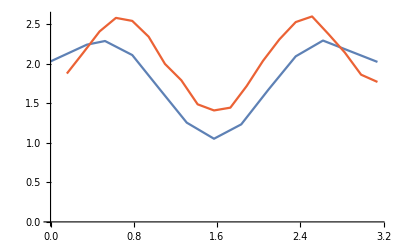

```mathematica
ListPlot[{fitvals,alternatefitvals,fibsaturation,alternatefitvals2,saturationvalues,altfibomax,altfibomean},Joined->True]
```

```mathematica
2
```

2

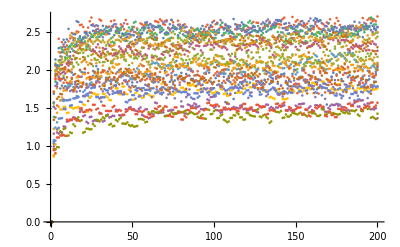

```mathematica
ListPlot[Table[Drop[Drop[answers,-(4200-200n)],(n-1)*200],{n,1,21}]]
```

2) 1,3,5,7

```mathematica
answers2 = Flatten[Drop[Import["/home/yajur/Dropbox/miniproj/outputs/answersnew2.dat"],1]];
```

```mathematica
Dimensions[answers2]
```

{4200}

```mathematica
answersn2 = Table[Drop[Drop[answers2,-(4200-200n)],(n-1)*200],{n,1,21}];
```

```mathematica
answersfitvals2 = Table[FindFit[Drop[answersn2[[n]],{1,60}],0*x+c,c,x],{n,1,21}]
```

{{c→1.87400647601036142},{c→2.13692286118809183},{c→2.40609525950376752},{c→2.57724198312609025},{c→2.53910062645542355},{c→2.33987088587237619},{c→1.99552607791886879},{c→1.78936045615009002},{c→1.48527797854227317},{c→1.40807529175599005},{c→1.44304394413840246},{c→1.71665477019620982},{c→2.03513217008079553},{c→2.30554422654149103},{c→2.5244336806632498},{c→2.59527980179658751},{c→2.37338415842230122},{c→2.14051746110010448},{c→1.8595888127008861},{c→1.767971577124782},{c→1.88558660565346598}}

```mathematica
alternatefitvals2 = Table[{0.05( n) Pi,Flatten[answersfitvals2/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}]
```

{{0.15708,1.87400647601036142},{0.314159,2.13692286118809183},{0.471239,2.40609525950376752},{0.628319,2.57724198312609025},{0.785398,2.53910062645542355},{0.942478,2.33987088587237619},{1.09956,1.99552607791886879},{1.25664,1.78936045615009002},{1.41372,1.48527797854227317},{1.5708,1.40807529175599005},{1.72788,1.44304394413840246},{1.88496,1.71665477019620982},{2.04204,2.03513217008079553},{2.19911,2.30554422654149103},{2.35619,2.5244336806632498},{2.51327,2.59527980179658751},{2.67035,2.37338415842230122},{2.82743,2.14051746110010448},{2.98451,1.8595888127008861},{3.14159,1.767971577124782}}

#### Final plot

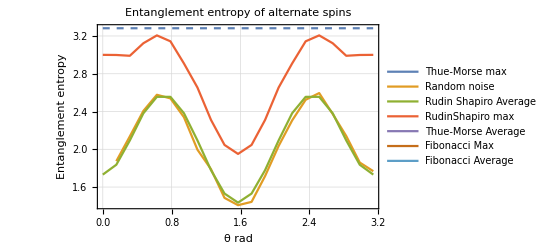

```mathematica
Show[ListLinePlot[{alttmmax,alternatefitvals2,altrdmean,altrdmax,alttmmean,altfibomax,altfibomean},PlotRange->All,PlotTheme->"Detailed",PlotLegends->Placed[{"Thue-Morse max ","Random noise","Rudin Shapiro Average","RudinShapiro max","Thue-Morse Average","Fibonacci Max","Fibonacci Average"},{0.5,0.83}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.14},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of alternate spins],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

```mathematica
Show[ListLinePlot[Table[Abs[Fourier[fibo64n[[n]]]],{n,1,21}],PlotRange->All],ListLinePlot[Table[Abs[Fourier[fibo32n[[n]]]],{n,1,21}],PlotRange->All]]
```

Part::partd: Part specification fibo64n⟦1⟧ is longer than depth of object.

Fourier::fftl: Argument fibo64n⟦1⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification fibo64n⟦2⟧ is longer than depth of object.

Fourier::fftl: Argument fibo64n⟦2⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification fibo64n⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Fourier::fftl: Argument fibo64n⟦3⟧ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

-Graphics-

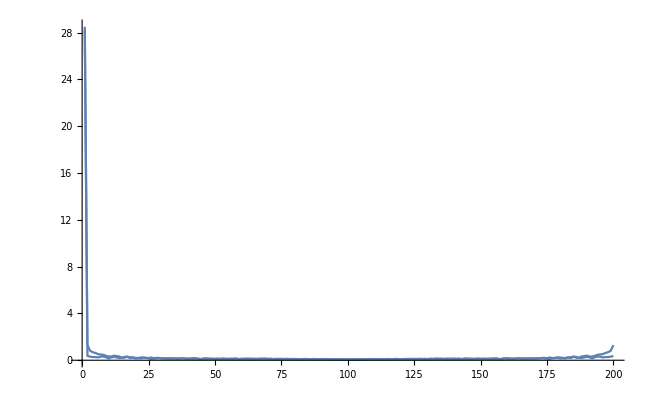

```mathematica
Show[ListLinePlot[Abs[Fourier[nois45]],PlotRange->All],ListLinePlot[Abs[Fourier[nois0]],PlotRange->All]]
```

## dt = pi/8 kick*after

```mathematica
kanoisedatac8=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answersnewkac8.dat"]];
```

```mathematica
Dimensions[kanoisedatac8]
```

{4200}

```mathematica
kanoise8n=Table[Drop[Drop[kanoisedatac8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[kanoise8n]
```

{21,200}

```mathematica
kanoise8max=Table[{0.05*(n-1)*Pi,Max[kanoise8n[[n]]]},{n,1,21}];
```

```mathematica
kanoise8mean=Table[{0.05 (n-1) Pi,Mean[kanoise8n[[n]]]},{n,1,21}];
```

```mathematica
kafitvals8 = Table[FindFit[Drop[kanoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
kafitvals8n = Table[{0.05( n-1) Pi,Flatten[kafitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

```mathematica
ListLinePlot[Table[kanoise8n[[n]],{n,1,11}],PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise-- kick * after],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

-Graphics-

```mathematica
Manipulate[Show[ListLinePlot[kanoise8n[[1]],PlotStyle->Red],Plot[ventropy[t]/.{a->q,b->w},{t,0,200},PlotRange->All]],{q,0,10},{w,1,100}]
```

Part::partd: Part specification kanoise8n⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: kanoise8n⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[kanoise8n⟦1⟧,PlotStyle→RGBColor[1, 0, 0]],].

```mathematica
FindFit[kanoise8n[[1]],0.0056 e Vnet[R*3.086*10^19]/.{ρ0->3 a ρMilkyway,Rc->b RcMilkyway,Σ0->c Subscript[Σ, MilkyWay],Rd-> d Subscript[Rd, MilkyWay]},{a,b,c,d,e},R]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

FindFit[{0.,0.962376237623762565,1.56320428908142817,2.18960015033330446,2.52828209749867927,2.58608268193100788,2.67636120258411969,2.58287627903409733,2.57025109435260379,2.47606602413471677,2.46337879815730698,2.45483576375255064,2.46039550545011032,2.43442038059175392,2.47103035783385883,2.52620809012129222,2.54930378765075627,2.56447054553120912,2.5591871593852269,2.5431588592184351,2.53534408077240636,2.53639240741648164,2.56725466596359153,2.56152130991483595,2.5844908796908026,2.57932353118606894,2.56293983537857883,2.5896533066666998,2.57164670587208244,2.55341109838146041,2.55257050530619445,2.51780370874769099,2.58209117207416172,2.6059720113946967,2.6223049426597993,2.65945013825448795,2.66535865623457413,2.62544078332408004,2.60672691808737156,2.60300460648169008,2.59647164484316884,2.60080985273716703,2.62713041790072222,2.60881120950826828,2.61810752749055054,2.58274349715934726,2.6050821100140511,2.58683501143752315,2.5476583174449372,2.59396374544272002,2.5473425000456813,2.58398997030350008,2.5726007562620401,2.55591226849605357,2.59562317850814361,2.63233985233591383,2.62911658358138434,2.59245854212194926,2.5755569660584019,2.54899108761079374,2.56499683206192275,2.58444465026965675,2.5524255711545587,2.54516160868945729,2.52005401880448687,2.56050689267361076,2.57287035703164291,2.54758934774133827,2.58248349696420254,2.574302270611184,2.59133139354399766,2.58804834892369673,2.58626193285406103,2.57293639655516637,2.57650368180233746,2.56967296058321137,2.59494866208228014,2.58160724211325698,2.57752630425768414,2.52328383782580357,2.57493637754018456,2.57902782860770019,2.55608464440642891,2.56210256419372984,2.55078923104498978,2.54566714271459871,2.56615993197685288,2.5672361310811187,2.58452576948200896,2.54419640611719755,2.51841121451589656,2.56475426454125355,2.53941203362500279,2.55435035879400241,2.54916013146667364,2.5398637380714475,2.57485788565097584,2.59765457947525702,2.60867155140860607,2.59691593621430261,2.59566215827505342,2.63377453962245589,2.58674582421262889,2.57784360814762881,2.57719814990240481,2.57204649333376434,2.55294264472354548,2.58627923259769643,2.61067235837738165,2.62485580581362266,2.6080010991431668,2.62549023538598414,2.61825605484978885,2.60183203729823154,2.60646117143431289,2.57666817485103428,2.58721445666561101,2.58544467324482152,2.56629940622826958,2.56266084456742949,2.59319687510873953,2.5763095817818229,2.5665525911179734,2.59961902896799346,2.59778680484756297,2.62445906624828851,2.61694564569203036,2.5940297182209453,2.5499850148379748,2.57099510293591171,2.57518265081071984,2.57720257457037727,2.58265471750373132,2.58950246590238375,2.56994449678810044,2.52852597205050556,2.53099076014519708,2.54539815142046155,2.5656358085362081,2.58668194402508345,2.59856482608870865,2.57149496074984629,2.53859751808298606,2.54567004282316045,2.57583513360223515,2.60571951992357942,2.58815899679594663,2.57927162250059539,2.59684562647765915,2.61897379120361196,2.60613942202530602,2.62993167564188468,2.60877296684929938,2.60189939287103611,2.61836891464324317,2.62998259198083195,2.63787616305265349,2.5853722716920764,2.61272793423928729,2.61127247509479554,2.58998153762573136,2.62355405773144623,2.59733304528510312,2.60418631786460608,2.6081807640961272,2.58425101345303121,2.5771827877546678,2.56250852599328605,2.57657426448781335,2.56432471556319053,2.54630534856783131,2.55744306367633012,2.55375015273697992,2.58199064251102817,2.57798222830665447,2.54311588480770556,2.54792916571653105,2.52461789675879089,2.56266331194743469,2.59103077109949531,2.57329930052992051,2.5547721124069378,2.55395992811337624,2.61090391107393671,2.61538412769643935,2.59002737381854375,2.59167293930301002,2.5519912759063268,2.57954095852158805,2.57432677551237621,2.55784255889556977,2.55343723098269004,2.55318524930328783,2.54853427428416302,2.55586468377749654,2.50563225404090373,2.55748508843244649,2.54997201011467123,2.57102944315366777,2.55018236257318165},0.0056 e Vnet[3.086×10^19 R],{a,b,c,d,e},R]

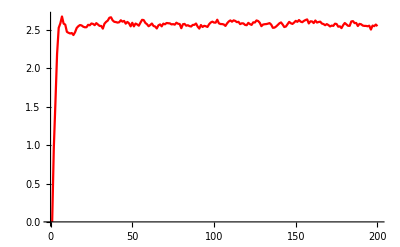

```mathematica
Show[ListLinePlot[kanoise8n⟦1⟧,PlotStyle->Red],Plot[0.0056 e Vnet[R 3.086 10^19]/.{ρ0->3 a ρMilkyway,Rc->b RcMilkyway,Σ0->c Subscript[Σ, MilkyWay],Rd->d Subscript[Rd, MilkyWay]}/.{a->3.17430152813834,b->0.5928821014105422,c->2.0010491612113515,d->1.1916892403341486,e->1.163438902967638},{R,1,200},PlotRange->All]]
```

```mathematica
Manipulate[Show[ListLinePlot[kanoise8n[[1]],PlotStyle->Red,PlotRange->All],Plot[0.0056 e Vnet[R*3.086*10^19]/.{ρ0->3 a ρMilkyway,Rc->b RcMilkyway,Σ0->c Subscript[Σ, MilkyWay],Rd-> d Subscript[Rd, MilkyWay]},{R,0,200},PlotRange->All],PlotRange->All],{a,0.1,4},{b,0.1,4},{c,0.1,4},{d,0.1,4},{e,0.1,4}]
```

Part::partd: Part specification kanoise8n⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: kanoise8n⟦1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[kanoise8n⟦1⟧,PlotStyle→RGBColor[1, 0, 0],PlotRange→All],,PlotRange→All].

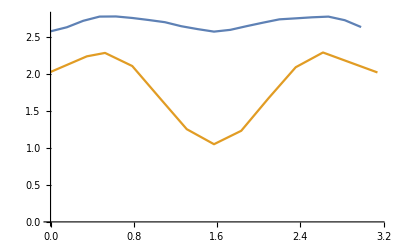

```mathematica
ListLinePlot[{kafitvals8n,fitvals}]
```

## dt = pi/16

#### 4+4

```mathematica
noise16=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answersnew16.dat"]];
```

```mathematica
Dimensions[noise16]
```

{4200}

```mathematica
noise16n=Table[Drop[Drop[noise16,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
noise16max=Table[{0.05*(n-1)*Pi,Max[noise16n[[n]]]},{n,1,21}];
```

```mathematica
noise16mean=Table[{0.05 (n-1) Pi,Mean[noise16n[[n]]]},{n,1,21}];
```

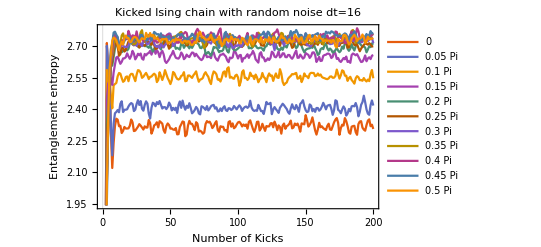

```mathematica
ListLinePlot[Table[noise16n[[n]],{n,1,11}],PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise dt = 16],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

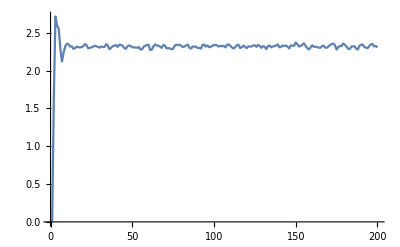

```mathematica
ListLinePlot[noise16n[[1]],PlotRange->All]
```

```mathematica
Manipulate[Show[ListLinePlot[kanoise8n[[1]],PlotStyle->Red],Plot[ventropy[t]/.{a->q,b->w},{t,0,200},PlotRange->All]],{q,0,10},{w,1,100}]
```

Part::partd: Part specification kanoise8n⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: kanoise8n⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[kanoise8n⟦1⟧,PlotStyle→RGBColor[1, 0, 0]],].

```mathematica
Manipulate[Show[ListLinePlot[noise16n[[1]],PlotRange->All],Plot[0.0056 e Vnet[R*3.086*10^19]/.{ρ0->3 a ρMilkyway,Rc->b RcMilkyway,Σ0->c Subscript[Σ, MilkyWay],Rd-> d Subscript[Rd, MilkyWay]},{R,0,200},PlotRange->All],PlotRange->All],{a,0.1,4},{b,0.1,4},{c,0.1,4},{d,0.1,4},{e,0.1,4}]
```

Part::partd: Part specification noise16n⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: noise16n⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[noise16n⟦1⟧,PlotRange→All],,PlotRange→All].

```mathematica
fitvals16 = Table[FindFit[Drop[noise16n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
fitvals16n = Table[{0.05( n-1) Pi,Flatten[fitvals16/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

#### final plot

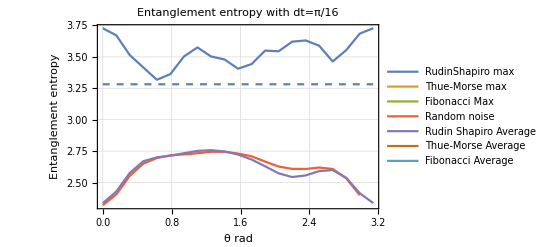

```mathematica
Show[ListLinePlot[{rd16max,tm16max,fibo16max,fitvals16n,rd16mean,tm16mean,fibo16mean},PlotRange->All,PlotTheme->"Detailed",PlotLegends->Placed[{"RudinShapiro max","Thue-Morse max ","Fibonacci Max","Random noise","Rudin Shapiro Average","Thue-Morse Average","Fibonacci Average"},{0.8,0.47}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.14},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy with dt = Pi/16],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

## dt = pi/32

#### 4+4

```mathematica
noise32=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answerscorrect_32.dat"]];
```

```mathematica
noise32 = Flatten@ToExpression@StringSplit[noise32,","];
```

```mathematica
noise32[[1]]
```

0.

```mathematica
Dimensions[noise32]
```

{4200}

```mathematica
Dimensions[noise32n[[1]]]
```

{200}

```mathematica
noise32n[[1,1]]
```

0.

```mathematica
noise32n=Table[Drop[Drop[noise32,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
noise32max=Table[{0.05*(n-1)*Pi,Max[noise32n[[n]]]},{n,1,21}];
```

```mathematica
noise32mean=Table[{0.05 (n-1) Pi,Mean[noise32n[[n]]]},{n,1,21}];
```

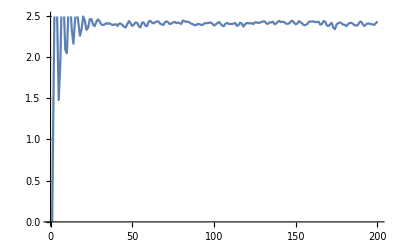

```mathematica
ListLinePlot[noise32n[[1]]]
```

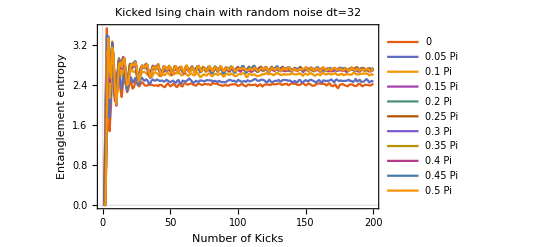

```mathematica
ListLinePlot[Table[noise32n[[n]],{n,1,11}],PlotRange->All,PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise dt = 32],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

```mathematica
fitvals32 = Table[FindFit[Drop[noise32n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
fitvals32n = Table[{0.05( n-1) Pi,Flatten[fitvals32/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

## dt = pi/64

#### 4+4

```mathematica
noise64=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answerscorrect_64.dat"]];
```

```mathematica
noise64 = Flatten@ToExpression@StringSplit[noise64,","];
```

```mathematica
noise64[[1]]
```

0.

```mathematica
Dimensions[noise32]
```

{4200}

```mathematica
Dimensions[noise32n[[1]]]
```

{200}

```mathematica
noise64n[[1,1]]
```

0.

```mathematica
noise64n=Table[Drop[Drop[noise64,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
noise64max=Table[{0.05*(n-1)*Pi,Max[noise64n[[n]]]},{n,1,21}];
```

```mathematica
noise64mean=Table[{0.05 (n-1) Pi,Mean[noise64n[[n]]]},{n,1,21}];
```

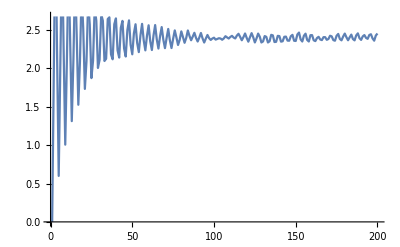

```mathematica
ListLinePlot[noise64n[[1]]]
```

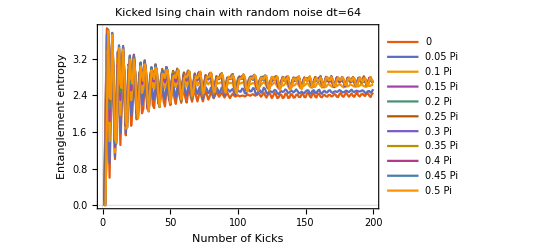

```mathematica
ListLinePlot[Table[noise64n[[n]],{n,1,11}],PlotRange->All,PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise dt = 64],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

```mathematica
fitvals64 = Table[FindFit[Drop[noise64n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
fitvals64n = Table[{0.05( n-1) Pi,Flatten[fitvals64/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

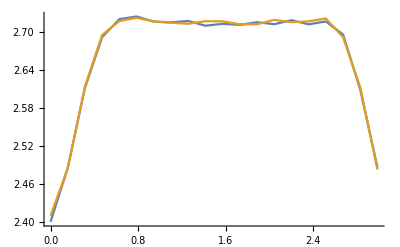

```mathematica
ListLinePlot[{fitvals64n,fitvals32n}]
```

## dt = pi/128

#### 4+4

```mathematica
noise128=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/128answerscorrect.dat"]];
```

```mathematica
noise128 = Flatten@ToExpression@StringSplit[noise128,","];
```

```mathematica
noise64[[1]]
```

0.

```mathematica
Dimensions[noise32]
```

{4200}

```mathematica
Dimensions[noise32n[[1]]]
```

{200}

```mathematica
noise128n[[1,1]]
```

0.

```mathematica
noise128n=Table[Drop[Drop[noise128,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
noise128max=Table[{0.05*(n-1)*Pi,Max[noise128n[[n]]]},{n,1,21}];
```

```mathematica
noise128mean=Table[{0.05 (n-1) Pi,Mean[noise128n[[n]]]},{n,1,21}];
```

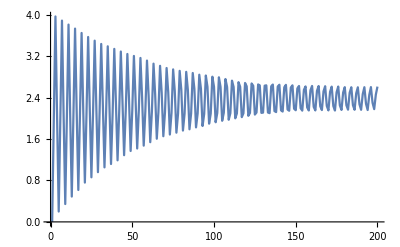

```mathematica
ListLinePlot[noise128n[[1]]]
```

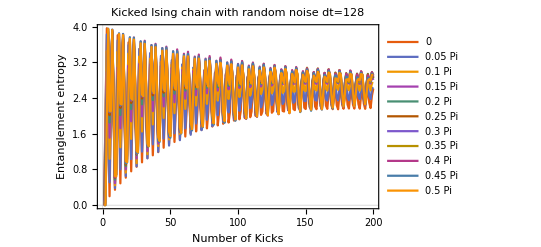

```mathematica
ListLinePlot[Table[noise128n[[n]],{n,1,11}],PlotRange->All,PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise dt = 128],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

```mathematica
fitvals128 = Table[FindFit[Drop[noise128n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
fitvals128n = Table[{0.05( n-1) Pi,Flatten[fitvals128/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

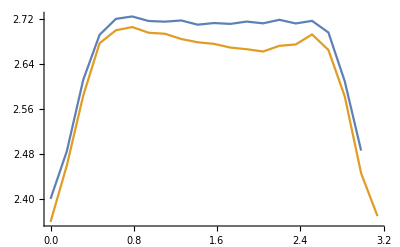

```mathematica
ListLinePlot[{fitvals64n,fitvals128n}]
```

## dt = pi/2048

#### 4+4

```mathematica
noise2048=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/2048answerscorrect.dat"]];
```

```mathematica
noise2048 = Flatten@ToExpression@StringSplit[noise2048,","];
```

```mathematica
noise64[[1]]
```

0.

```mathematica
Dimensions[noise32]
```

{4200}

```mathematica
Dimensions[noise32n[[1]]]
```

{200}

```mathematica
noise128n[[1,1]]
```

0.

```mathematica
noise2048n=Table[Drop[Drop[noise2048,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
noise2048max=Table[{0.05*(n-1)*Pi,Max[noise2048n[[n]]]},{n,1,21}];
```

```mathematica
noise2048mean=Table[{0.05 (n-1) Pi,Mean[noise2048n[[n]]]},{n,1,21}];
```

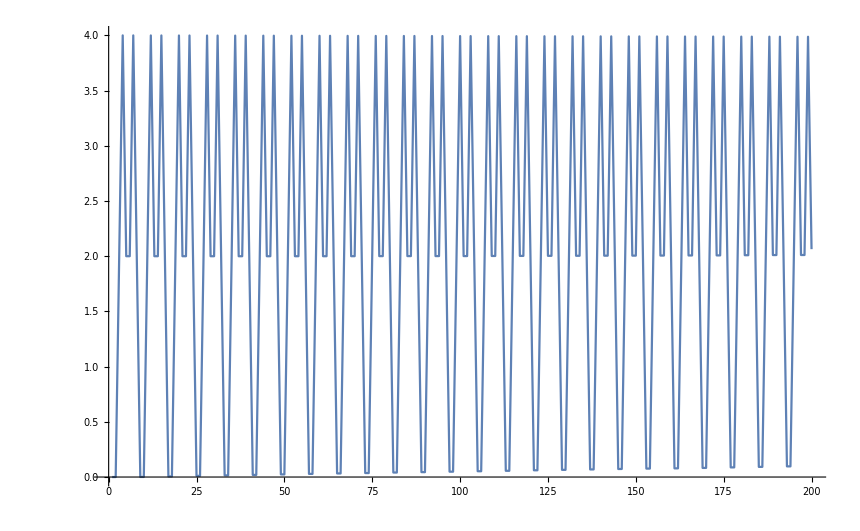

```mathematica
ListLinePlot[noise2048n[[11]]]
```

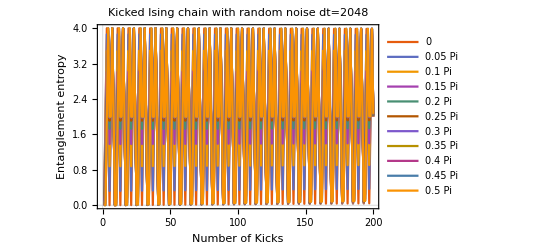

```mathematica
ListLinePlot[Table[noise2048n[[n]],{n,1,11}],PlotRange->All,PlotLegends->{"0","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"},PlotTheme->"Scientific",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of Kicks],None}},PlotLabel->HoldForm[Kicked Ising chain with random noise dt = 2048],LabelStyle->{FontFamily->"TeX Gyre Pagella",11,GrayLevel[0]}]
```

```mathematica
fitvals2048  = Table[FindFit[Drop[noise2048n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
fitvals2048n = Table[{0.05( n-1) Pi,Flatten[fitvals2048/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,21}];
```

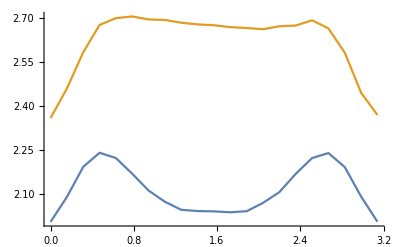

```mathematica
ListLinePlot[{fitvals2048n,fitvals128n}]
```

## All plots

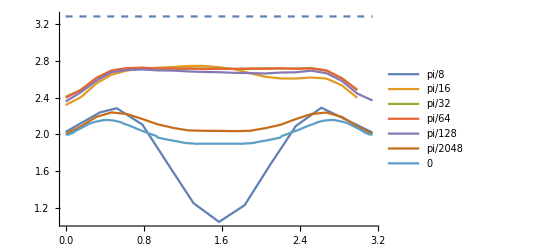

```mathematica
Show[ListLinePlot[{fitvals,fitvals16n,fitvals32n,fitvals64n,fitvals128n,fitvals2048n,entropymean},PlotLegends->{pi/8,pi/16,pi/32,pi/64,pi/128,pi/2048,0}, PlotRange->All],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All]
```

```mathematica
Show[ListLinePlot[Abs[Fourier[tm64n[[20]]]],PlotRange->All],ListLinePlot[Abs[Fourier[tm32n[[20]]]],PlotRange->All]]
```

Part::partd: Part specification tm64n⟦20⟧ is longer than depth of object.

Fourier::fftl: Argument tm64n⟦20⟧ is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::lpn: Abs[Fourier[tm64n⟦20⟧]] is not a list of numbers or pairs of numbers.

Part::partd: Part specification tm32n⟦20⟧ is longer than depth of object.

Fourier::fftl: Argument tm32n⟦20⟧ is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::lpn: Abs[Fourier[tm32n⟦20⟧]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Abs[Fourier[tm64n⟦20⟧]],PlotRange→All],ListLinePlot[Abs[Fourier[tm32n⟦20⟧]],PlotRange→All]].

Show[ListLinePlot[Abs[Fourier[tm64n⟦20⟧]],PlotRange→All],ListLinePlot[Abs[Fourier[tm32n⟦20⟧]],PlotRange→All]]

## Jordan Wigner

```mathematica
jwdata=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/noiseentropy.dat"]]
```

{0,0,0,1,1,1,1,2,2,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,1,1,2,2,2,2,2,1,0,0,1,2,1,1,0,0,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,1,2,2,2,2,2,1,1,1,1,1,1,2,2,2,2,2,1,0,0,1,1,1,1,1,1,2,2,2,1,1,1,1,1,2,2,2,2,2,2,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,2,1,1,2,1,1,1,1,2,2,1,1,2,2,2,2,1,1,0,0,1,1,1,1,2}

```mathematica
Dimensions[jwdata]
```

{200}

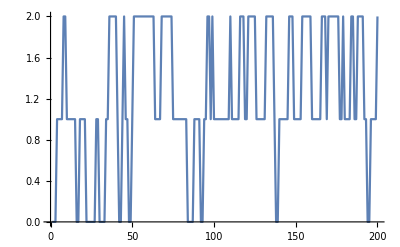

```mathematica
ListLinePlot[jwdata]
```

## kicked interactions

## dt = pi/8

```mathematica
noisedataw8=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answersneww8.dat"]];
```

```mathematica
Dimensions[noisedataw8]
```

{4200}

```mathematica
wnoise8n=Table[Drop[Drop[noisedataw8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
wnoise8max=Table[{0.05*(n-1)*Pi,Max[wnoise8n[[n]]]},{n,1,21}];
```

```mathematica
wnoise8mean=Table[{0.05 (n-1) Pi,Mean[wnoise8n[[n]]]},{n,1,21}];
```

```mathematica
wfitvals8 = Table[FindFit[Drop[wnoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
wfitvals8n = Table[{0.05( n-1) Pi,Flatten[wfitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

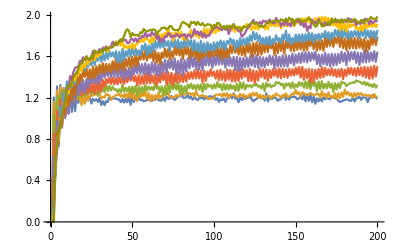

```mathematica
ListLinePlot[Table[wnoise8n[[n]],{n,1,10}]]
```

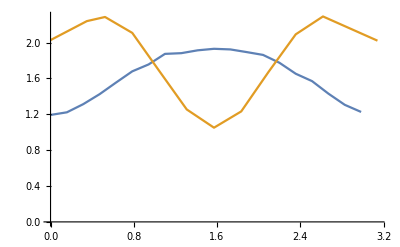

```mathematica
ListLinePlot[{wfitvals8n,fitvals}]
```

## dt = pi/8 kick*after

```mathematica
kanoisedataw8=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/answersnewkaw8.dat"]];
```

```mathematica
Dimensions[kanoisedataw8]
```

{4200}

```mathematica
kawnoise8n=Table[Drop[Drop[kanoisedataw8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
kawnoise8max=Table[{0.05*(n-1)*Pi,Max[kawnoise8n[[n]]]},{n,1,21}];
```

```mathematica
kawnoise8mean=Table[{0.05 (n-1) Pi,Mean[kawnoise8n[[n]]]},{n,1,21}];
```

```mathematica
kawfitvals8 = Table[FindFit[Drop[kawnoise8n[[n]],{1,60}],0*x+c,c,x],{n,1,21}];
```

```mathematica
kawfitvals8n = Table[{0.05( n-1) Pi,Flatten[kawfitvals8/.Rule->List][[ 2;; ;; 2]][[n]]},{n,1,20}];
```

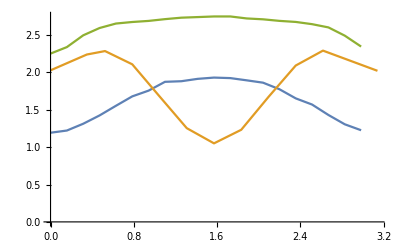

```mathematica
ListLinePlot[{wfitvals8n,fitvals,kawfitvals8n}]
```

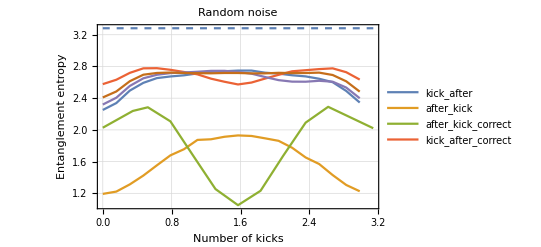

```mathematica
Show[ListLinePlot[{kawfitvals8n,wfitvals8n,fitvals,kafitvals8n,fitvals16n,fitvals32n},PlotTheme->"Detailed",PlotLegends->{"kick_after","after_kick","after_kick_correct","kick_after_correct"}],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm["Random noise"],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All]
```

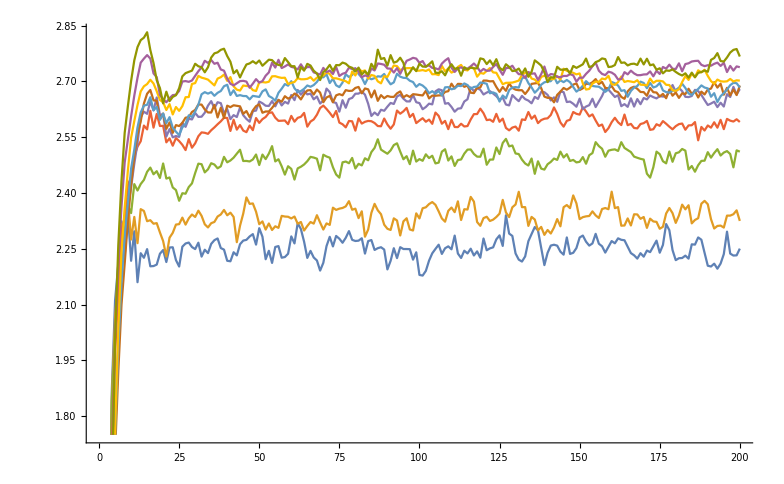

```mathematica
ListLinePlot[Table[kawnoise8n[[n]],{n,1,10}]]
```